```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

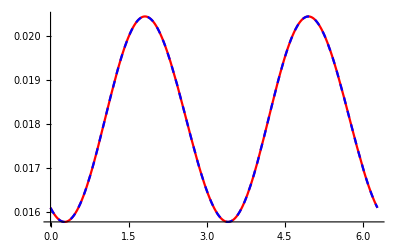

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

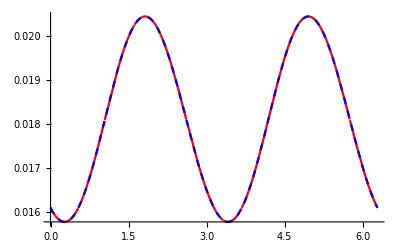
```mathematica
0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-Graphics-
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -(ⅈ (0.+0. ⅈ) ComplexInfinity)/(4 π) encountered.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

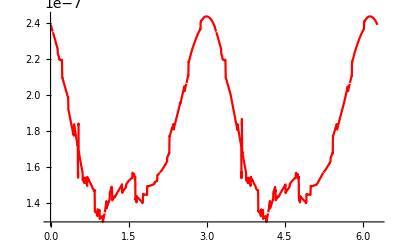

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

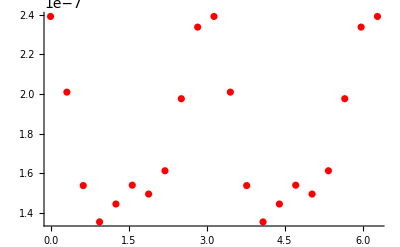

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
If[showQ,
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
];
v2=NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2," at k_T=",kT];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

## b = 1

### r = 0.1

```mathematica
showdσHZ[bu,x1u,x3u,kT,False]
```

NIntegrate::inumr: The integrand Cos[2 ϕ$143101] dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::inumr: The integrand dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] Sin[2 ϕ$143101] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::inumr: The integrand Cos[2 ϕ$143101] dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{NIntegrate[Cos[2 ϕ$143101] dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}],{ϕ$143101,0,2 π}]/NIntegrate[dσHZ[x1u,x2u$143101,bu+x3u,bu+x4u$143101,{kT,ϕ$143101}],{ϕ$143101,0,2 π}],NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ$143101}] Sin[2 ϕ$143101],{ϕ$143101,0,2 π}]/NIntegrate[dσHZ[x1u,x2u$143101,bu+x3u,bu+x4u$143101,{kT,ϕ$143101}],{ϕ$143101,0,2 π}]}

```mathematica
showdσHZ[2,bu,x1u,x3u,kT,False]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3207651 near {ϕ$3207651} = {4.52821}. NIntegrate obtained -7.82983×10^-8 and 1.56701×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3207651 near {ϕ$3207651} = {5.42406}. NIntegrate obtained 5.70936×10^-21 and 9.96811×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3207651 near {ϕ$3207651} = {4.0128}. NIntegrate obtained 1.41335×10^-7 and 2.29773×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-0.553992,4.0396×10^-14}

```mathematica
showdσHZ[4,bu,x1u,x3u,kT,False]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3516374 near {ϕ$3516374} = {5.26452}. NIntegrate obtained -6.47938×10^-13 and 3.88327×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3516374 near {ϕ$3516374} = {4.0128}. NIntegrate obtained 1.41335×10^-7 and 2.29773×10^-13 for the integral and error estimates.

{0.255988,-4.58442×10^-6}

```mathematica
v2kTr01={};
For[i=1,i≤120,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr01,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$146042 near {ϕ$146042} = {0.944835}. NIntegrate obtained 1.05313×10^-18 and 7.75677×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$198005 near {ϕ$198005} = {5.08045}. NIntegrate obtained -4.84395×10^-16 and 2.90601×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$288347 near {ϕ$288347} = {4.20915}. NIntegrate obtained -4.10856×10^-18 and 3.96797×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
v2kTr01
```

{{0.25,{-0.0157187,4.45577×10^-15}},{0.5,{-0.062827,-9.20926×10^-12}},{0.75,{-0.139328,-2.00755×10^-13}},{1.,{-0.240227,1.77613×10^-12}},{1.25,{-0.35739,-2.93311×10^-14}},{1.5,{-0.479261,2.14831×10^-11}},{1.75,{-0.591091,7.7825×10^-10}},{2.,{-0.677349,-1.10209×10^-13}},{2.25,{-0.726966,2.70404×10^-14}},{2.5,{-0.738423,1.05985×10^-13}},{2.75,{-0.719943,-4.26028×10^-14}},{3.,{-0.684442,-2.18537×10^-10}},{3.25,{-0.643735,-1.25544×10^-6}},{3.5,{-0.605698,-1.79259×10^-14}},{3.75,{-0.574323,-4.14661×10^-14}},{4.,{-0.550945,1.79277×10^-14}},{4.25,{-0.535463,1.70267×10^-14}},{4.5,{-0.527157,3.12895×10^-14}},{4.75,{-0.525121,-2.42844×10^-15}},{5.,{-0.528467,2.38943×10^-14}},{5.25,{-0.536388,2.11343×10^-8}},{5.5,{-0.548162,1.11488×10^-14}},{5.75,{-0.563122,5.39756×10^-15}},{6.,{-0.580625,4.77842×10^-15}},{6.25,{-0.600009,4.35246×10^-15}},{6.5,{-0.620565,-3.95808×10^-15}},{6.75,{-0.641511,4.96233×10^-15}},{7.,{-0.661978,1.08362×10^-14}},{7.25,{-0.681019,1.36393×10^-14}},{7.5,{-0.697642,-1.31854×10^-14}},{7.75,{-0.710858,-2.09258×10^-14}},{8.,{-0.719767,-1.24401×10^-15}},{8.25,{-0.723653,-1.38475×10^-14}},{8.5,{-0.722076,2.28796×10^-14}},{8.75,{-0.714966,2.02798×10^-6}},{9.,{-0.702631,1.28915×10^-7}},{9.25,{-0.685778,7.09638×10^-15}},{9.5,{-0.665429,-8.58115×10^-8}},{9.75,{-0.642763,1.7996×10^-9}},{10.,{-0.619111,7.59579×10^-9}},{10.25,{-0.595719,-3.10156×10^-9}},{10.5,{-0.573702,-4.43718×10^-7}},{10.75,{-0.553992,4.0396×10^-14}},{11.,{-0.53727,-4.74415×10^-9}},{11.25,{-0.523987,2.72869×10^-14}},{11.5,{-0.514373,-3.49629×10^-14}},{11.75,{-0.50846,2.78817×10^-14}},{12.,{-0.506108,-1.46144×10^-14}},{12.25,{-0.507021,2.18606×10^-14}},{12.5,{-0.510778,-3.72986×10^-14}},{12.75,{-0.516844,3.90508×10^-14}},{13.,{-0.524609,2.11315×10^-14}},{13.25,{-0.533384,2.88333×10^-15}},{13.5,{-0.542427,-5.10646×10^-14}},{13.75,{-0.551004,2.16152×10^-6}},{14.,{-0.558401,-5.68867×10^-9}},{14.25,{-0.56399,-4.19282×10^-14}},{14.5,{-0.567259,-4.80718×10^-14}},{14.75,{-0.567875,4.71065×10^-14}},{15.,{-0.565682,8.06853×10^-15}},{15.25,{-0.560756,1.25152×10^-14}},{15.5,{-0.553334,9.57761×10^-10}},{15.75,{-0.543873,-9.58429×10^-15}},{16.,{-0.532927,-3.87923×10^-15}},{16.25,{-0.521115,-6.79951×10^-15}},{16.5,{-0.509113,8.01134×10^-14}},{16.75,{-0.497507,-3.77202×10^-14}},{17.,{-0.486919,-5.34595×10^-14}},{17.25,{-0.47777,3.74349×10^-15}},{17.5,{-0.470421,7.5323×10^-14}},{17.75,{-0.46511,-4.73588×10^-15}},{18.,{-0.461929,-4.03007×10^-14}},{18.25,{-0.460896,2.94048×10^-6}},{18.5,{-0.461883,-2.08973×10^-14}},{18.75,{-0.464681,-1.17763×10^-14}},{19.,{-0.46897,-3.82806×10^-14}},{19.25,{-0.474371,1.868×10^-14}},{19.5,{-0.48043,1.03184×10^-13}},{19.75,{-0.4867,-1.72874×10^-14}},{20.,{-0.492639,-3.25637×10^-6}},{20.25,{-0.49782,-7.17622×10^-14}},{20.5,{-0.501737,9.25496×10^-15}},{20.75,{-0.504133,-4.93938×10^-8}},{21.,{-0.50468,5.34446×10^-8}},{21.25,{-0.503273,6.48964×10^-14}},{21.5,{-0.499926,6.12715×10^-8}},{21.75,{-0.49478,8.20305×10^-15}},{22.,{-0.488089,2.61801×10^-8}},{22.25,{-0.480229,-5.37731×10^-14}},{22.5,{-0.471636,-2.37645×10^-8}},{22.75,{-0.46269,-7.61967×10^-8}},{23.,{-0.453883,-4.35823×10^-14}},{23.25,{-0.445733,9.61877×10^-8}},{23.5,{-0.438406,-6.45213×10^-8}},{23.75,{-0.432338,-2.3747×10^-13}},{24.,{-0.427743,-9.23792×10^-8}},{24.25,{-0.424703,4.40993×10^-14}},{24.5,{-0.423252,-1.17549×10^-14}},{24.75,{-0.423365,3.09228×10^-7}},{25.,{-0.42485,-3.94661×10^-14}},{25.25,{-0.427551,5.47303×10^-17}},{25.5,{-0.431117,-7.25639×10^-15}},{25.75,{-0.435291,-2.88181×10^-14}},{26.,{-0.439572,-1.21974×10^-14}},{26.25,{-0.44375,-1.4636×10^-8}},{26.5,{-0.447275,-1.24115×10^-6}},{26.75,{-0.449846,-2.78558×10^-15}},{27.,{-0.45121,4.63195×10^-7}},{27.25,{-0.451113,2.4201×10^-14}},{27.5,{-0.449424,9.53021×10^-15}},{27.75,{-0.446123,2.46799×10^-14}},{28.,{-0.441333,-2.2754×10^-6}},{28.25,{-0.435217,1.81927×10^-14}},{28.5,{-0.42805,5.97059×10^-14}},{28.75,{-0.420203,1.0879×10^-14}},{29.,{-0.411968,-2.64344×10^-7}},{29.25,{-0.40379,-6.46534×10^-9}},{29.5,{-0.396003,3.62264×10^-7}},{29.75,{-0.388929,2.53649×10^-7}},{30.,{-0.38282,-2.61585×10^-14}}}

```mathematica
v2kTr01={};
For[i=1,i≤240,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kTr01,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTr01
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192131759 near {ϕ$192131759} = {5.71858}. NIntegrate obtained 9.12678×10^-18 and 7.00796×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192194508 near {ϕ$192194508} = {0.944835}. NIntegrate obtained 1.05313×10^-18 and 7.75677×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192246433 near {ϕ$192246433} = {1.90204}. NIntegrate obtained -3.23138×10^-18 and 3.01729×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{-0.00391806,9.24485×10^-15}},{0.25,{-0.0157187,4.45577×10^-15}},{0.375,{-0.0354044,-3.24943×10^-14}},{0.5,{-0.062827,-9.20926×10^-12}},{0.625,{-0.0976425,1.13234×10^-11}},{0.75,{-0.139328,-2.00755×10^-13}},{0.875,{-0.18716,3.65879×10^-14}},{1.,{-0.240227,1.77613×10^-12}},{1.125,{-0.297416,1.63936×10^-12}},{1.25,{-0.35739,-2.93311×10^-14}},{1.375,{-0.418602,5.56247×10^-14}},{1.5,{-0.479261,2.14831×10^-11}},{1.625,{-0.537441,-4.3328×10^-12}},{1.75,{-0.591091,7.7825×10^-10}},{1.875,{-0.638266,-1.63048×10^-13}},{2.,{-0.677349,-1.10209×10^-13}},{2.125,{-0.707092,-2.29806×10^-14}},{2.25,{-0.726966,2.70404×10^-14}},{2.375,{-0.737136,6.27389×10^-14}},{2.5,{-0.738423,1.05985×10^-13}},{2.625,{-0.732143,6.6596×10^-14}},{2.75,{-0.719943,-4.26028×10^-14}},{2.875,{-0.703491,-5.24726×10^-15}},{3.,{-0.684442,-2.18537×10^-10}},{3.125,{-0.664112,2.06704×10^-7}},{3.25,{-0.643735,-1.25544×10^-6}},{3.375,{-0.624029,2.33796×10^-9}},{3.5,{-0.605698,-1.79259×10^-14}},{3.625,{-0.589021,3.152×10^-15}},{3.75,{-0.574323,-4.14661×10^-14}},{3.875,{-0.561591,3.64852×10^-14}},{4.,{-0.550945,1.79277×10^-14}},{4.125,{-0.542226,1.09035×10^-14}},{4.25,{-0.535463,1.70267×10^-14}},{4.375,{-0.530442,4.75911×10^-14}},{4.5,{-0.527157,3.12895×10^-14}},{4.625,{-0.525386,3.59845×10^-14}},{4.75,{-0.525121,-2.42844×10^-15}},{4.875,{-0.526151,2.7405×10^-14}},{5.,{-0.528467,2.38943×10^-14}},{5.125,{-0.531883,1.14919×10^-15}},{5.25,{-0.536388,2.11343×10^-8}},{5.375,{-0.54182,1.20107×10^-14}},{5.5,{-0.548162,1.11488×10^-14}},{5.625,{-0.555274,-8.20707×10^-15}},{5.75,{-0.563122,5.39756×10^-15}},{5.875,{-0.571586,7.41448×10^-15}},{6.,{-0.580625,4.77842×10^-15}},{6.125,{-0.590118,1.36165×10^-14}},{6.25,{-0.600009,4.35246×10^-15}},{6.375,{-0.610183,6.64694×10^-15}},{6.5,{-0.620565,-3.95808×10^-15}},{6.625,{-0.631035,-0.0000186778}},{6.75,{-0.641511,4.96233×10^-15}},{6.875,{-0.651861,2.55459×10^-15}},{7.,{-0.661978,1.08362×10^-14}},{7.125,{-0.671738,-2.92902×10^-15}},{7.25,{-0.681019,1.36393×10^-14}},{7.375,{-0.689696,6.94386×10^-15}},{7.5,{-0.697642,-1.31854×10^-14}},{7.625,{-0.704735,5.44791×10^-15}},{7.75,{-0.710858,-2.09258×10^-14}},{7.875,{-0.715901,-9.91784×10^-15}},{8.,{-0.719767,-1.24401×10^-15}},{8.125,{-0.722373,1.05616×10^-14}},{8.25,{-0.723653,-1.38475×10^-14}},{8.375,{-0.723562,-1.03857×10^-6}},{8.5,{-0.722076,2.28796×10^-14}},{8.625,{-0.719204,-8.35843×10^-15}},{8.75,{-0.714966,2.02798×10^-6}},{8.875,{-0.709417,-5.23131×10^-15}},{9.,{-0.702631,1.28915×10^-7}},{9.125,{-0.694717,-2.14784×10^-14}},{9.25,{-0.685778,7.09638×10^-15}},{9.375,{-0.676018,5.70954×10^-10}},{9.5,{-0.665429,-8.58115×10^-8}},{9.625,{-0.65429,4.1604×10^-9}},{9.75,{-0.642763,1.7996×10^-9}},{9.875,{-0.630964,4.22605×10^-10}},{10.,{-0.619111,7.59579×10^-9}},{10.125,{-0.607292,-2.63884×10^-9}},{10.25,{-0.595719,-3.10156×10^-9}},{10.375,{-0.584465,-1.55127×10^-8}},{10.5,{-0.573702,-4.43718×10^-7}},{10.625,{-0.56351,1.85527×10^-9}},{10.75,{-0.553992,4.0396×10^-14}},{10.875,{-0.545223,-1.78051×10^-14}},{11.,{-0.53727,-4.74415×10^-9}},{11.125,{-0.530179,4.19585×10^-14}},{11.25,{-0.523987,2.72869×10^-14}},{11.375,{-0.518713,2.44227×10^-14}},{11.5,{-0.514373,-3.49629×10^-14}},{11.625,{-0.510956,-2.06649×10^-14}},{11.75,{-0.50846,2.78817×10^-14}},{11.875,{-0.506853,3.11422×10^-14}},{12.,{-0.506108,-1.46144×10^-14}},{12.125,{-0.506172,4.08252×10^-14}},{12.25,{-0.507021,2.18606×10^-14}},{12.375,{-0.50857,5.42349×10^-14}},{12.5,{-0.510778,-3.72986×10^-14}},{12.625,{-0.513558,-2.71448×10^-14}},{12.75,{-0.516844,3.90508×10^-14}},{12.875,{-0.520556,-5.9532×10^-6}},{13.,{-0.524609,2.11315×10^-14}},{13.125,{-0.528908,-1.20543×10^-14}},{13.25,{-0.533384,2.88333×10^-15}},{13.375,{-0.537917,3.56506×10^-14}},{13.5,{-0.542427,-5.10646×10^-14}},{13.625,{-0.546816,-3.23183×10^-14}},{13.75,{-0.551004,2.16152×10^-6}},{13.875,{-0.554886,6.62078×10^-14}},{14.,{-0.558401,-5.68867×10^-9}},{14.125,{-0.561471,-2.89749×10^-9}},{14.25,{-0.56399,-4.19282×10^-14}},{14.375,{-0.565932,-3.45317×10^-14}},{14.5,{-0.567259,-4.80718×10^-14}},{14.625,{-0.567907,2.41045×10^-14}},{14.75,{-0.567875,4.71065×10^-14}},{14.875,{-0.567117,3.72258×10^-14}},{15.,{-0.565682,8.06853×10^-15}},{15.125,{-0.563538,-7.51051×10^-14}},{15.25,{-0.560756,1.25152×10^-14}},{15.375,{-0.5573,3.55902×10^-14}},{15.5,{-0.553334,9.57761×10^-10}},{15.625,{-0.548818,-4.80804×10^-14}},{15.75,{-0.543873,-9.58429×10^-15}},{15.875,{-0.538548,9.39554×10^-8}},{16.,{-0.532927,-3.87923×10^-15}},{16.125,{-0.527067,4.65576×10^-14}},{16.25,{-0.521115,-6.79951×10^-15}},{16.375,{-0.515081,5.54892×10^-9}},{16.5,{-0.509113,8.01134×10^-14}},{16.625,{-0.503211,2.72188×10^-7}},{16.75,{-0.497507,-3.77202×10^-14}},{16.875,{-0.492054,-1.25119×10^-14}},{17.,{-0.486919,-5.34595×10^-14}},{17.125,{-0.482131,-7.41066×10^-15}},{17.25,{-0.47777,3.74349×10^-15}},{17.375,{-0.473844,5.9667×10^-15}},{17.5,{-0.470421,7.5323×10^-14}},{17.625,{-0.467491,4.3907×10^-14}},{17.75,{-0.46511,-4.73588×10^-15}},{17.875,{-0.463243,-2.10496×10^-8}},{18.,{-0.461929,-4.03007×10^-14}},{18.125,{-0.461149,-6.54288×10^-14}},{18.25,{-0.460896,2.94048×10^-6}},{18.375,{-0.461134,-1.98077×10^-14}},{18.5,{-0.461883,-2.08973×10^-14}},{18.625,{-0.463071,6.68107×10^-14}},{18.75,{-0.464681,-1.17763×10^-14}},{18.875,{-0.466657,-1.70866×10^-8}},{19.,{-0.46897,-3.82806×10^-14}},{19.125,{-0.471552,1.23226×10^-14}},{19.25,{-0.474371,1.868×10^-14}},{19.375,{-0.47735,9.2783×10^-14}},{19.5,{-0.48043,1.03184×10^-13}},{19.625,{-0.483582,-5.14005×10^-14}},{19.75,{-0.4867,-1.72874×10^-14}},{19.875,{-0.489746,-1.59723×10^-14}},{20.,{-0.492639,-3.25637×10^-6}},{20.125,{-0.495363,7.63791×10^-15}},{20.25,{-0.49782,-7.17622×10^-14}},{20.375,{-0.499985,-1.57414×10^-14}},{20.5,{-0.501737,9.25496×10^-15}},{20.625,{-0.503164,-4.27794×10^-14}},{20.75,{-0.504133,-4.93938×10^-8}},{20.875,{-0.504649,4.76289×10^-8}},{21.,{-0.50468,5.34446×10^-8}},{21.125,{-0.504224,-5.54497×10^-8}},{21.25,{-0.503273,6.48964×10^-14}},{21.375,{-0.50183,-6.0334×10^-14}},{21.5,{-0.499926,6.12715×10^-8}},{21.625,{-0.497555,6.92067×10^-14}},{21.75,{-0.49478,8.20305×10^-15}},{21.875,{-0.491599,3.77525×10^-14}},{22.,{-0.488089,2.61801×10^-8}},{22.125,{-0.484275,-5.54828×10^-14}},{22.25,{-0.480229,-5.37731×10^-14}},{22.375,{-0.475975,3.36491×10^-14}},{22.5,{-0.471636,-2.37645×10^-8}},{22.625,{-0.467145,-1.30164×10^-13}},{22.75,{-0.46269,-7.61967×10^-8}},{22.875,{-0.458232,-8.47578×10^-8}},{23.,{-0.453883,-4.35823×10^-14}},{23.125,{-0.449626,1.29812×10^-13}},{23.25,{-0.445733,9.61877×10^-8}},{23.375,{-0.441914,-1.37089×10^-6}},{23.5,{-0.438406,-6.45213×10^-8}},{23.625,{-0.4352,4.34374×10^-15}},{23.75,{-0.432338,-2.3747×10^-13}},{23.875,{-0.429846,-2.68353×10^-6}},{24.,{-0.427743,-9.23792×10^-8}},{24.125,{-0.426012,-1.60375×10^-13}},{24.25,{-0.424703,4.40993×10^-14}},{24.375,{-0.423768,6.27334×10^-14}},{24.5,{-0.423252,-1.17549×10^-14}},{24.625,{-0.423113,3.00584×10^-7}},{24.75,{-0.423365,3.09228×10^-7}},{24.875,{-0.423923,-2.36848×10^-14}},{25.,{-0.42485,-3.94661×10^-14}},{25.125,{-0.42606,-3.28257×10^-7}},{25.25,{-0.427551,5.47303×10^-17}},{25.375,{-0.429246,-1.18742×10^-14}},{25.5,{-0.431117,-7.25639×10^-15}},{25.625,{-0.433147,-1.20703×10^-7}},{25.75,{-0.435291,-2.88181×10^-14}},{25.875,{-0.437456,-2.9449×10^-8}},{26.,{-0.439572,-1.21974×10^-14}},{26.125,{-0.441723,4.65413×10^-8}},{26.25,{-0.44375,-1.4636×10^-8}},{26.375,{-0.445603,7.76898×10^-7}},{26.5,{-0.447275,-1.24115×10^-6}},{26.625,{-0.448714,-1.56567×10^-8}},{26.75,{-0.449846,-2.78558×10^-15}},{26.875,{-0.450702,1.62737×10^-14}},{27.,{-0.45121,4.63195×10^-7}},{27.125,{-0.451354,-9.7451×10^-7}},{27.25,{-0.451113,2.4201×10^-14}},{27.375,{-0.450448,-2.64888×10^-14}},{27.5,{-0.449424,9.53021×10^-15}},{27.625,{-0.447953,-8.43784×10^-15}},{27.75,{-0.446123,2.46799×10^-14}},{27.875,{-0.443904,-1.23919×10^-14}},{28.,{-0.441333,-2.2754×10^-6}},{28.125,{-0.438432,5.87047×10^-15}},{28.25,{-0.435217,1.81927×10^-14}},{28.375,{-0.431741,4.95195×10^-14}},{28.5,{-0.42805,5.97059×10^-14}},{28.625,{-0.424174,-4.26775×10^-14}},{28.75,{-0.420203,1.0879×10^-14}},{28.875,{-0.416064,-2.10964×10^-7}},{29.,{-0.411968,-2.64344×10^-7}},{29.125,{-0.407836,-7.9619×10^-16}},{29.25,{-0.40379,-6.46534×10^-9}},{29.375,{-0.399811,-3.37582×10^-7}},{29.5,{-0.396003,3.62264×10^-7}},{29.625,{-0.392349,4.68287×10^-8}},{29.75,{-0.388929,2.53649×10^-7}},{29.875,{-0.385746,2.70477×10^-7}},{30.,{-0.38282,-2.61585×10^-14}}}

```mathematica
v2kTr01={{0.125,{-0.003918057710614559,9.244854885711647*^-15}},{0.25,{-0.015718719721257,4.455768613178577*^-15}},{0.375,{-0.035404393455990855,-3.24942552743455*^-14}},{0.5,{-0.06282700520498571,-9.209262174235287*^-12}},{0.625,{-0.09764251133096699,1.1323373487828947*^-11}},{0.75,{-0.13932777556625237,-2.0075541724325464*^-13}},{0.875,{-0.1871596950255955,3.6587891032648094*^-14}},{1.,{-0.2402268659614949,1.7761272106741705*^-12}},{1.125,{-0.29741608683685067,1.63936386445259*^-12}},{1.25,{-0.35738980707365536,-2.9331080873408746*^-14}},{1.375,{-0.41860210294753264,5.5624657311130876*^-14}},{1.5,{-0.4792613331839505,2.1483054629612167*^-11}},{1.625,{-0.5374405029017671,-4.33280410886713*^-12}},{1.75,{-0.5910905844362639,7.782502667849232*^-10}},{1.875,{-0.6382657283683378,-1.6304778766370707*^-13}},{2.,{-0.6773485071187965,-1.1020930550360381*^-13}},{2.125,{-0.7070922567638241,-2.2980585681298934*^-14}},{2.25,{-0.7269659742677628,2.704041641059906*^-14}},{2.375,{-0.7371361605396004,6.273889630496712*^-14}},{2.5,{-0.7384228508900981,1.0598538605139731*^-13}},{2.625,{-0.7321427588980837,6.659595237400903*^-14}},{2.75,{-0.7199432377360689,-4.260275997313958*^-14}},{2.875,{-0.7034905063569131,-5.247259673659533*^-15}},{3.,{-0.6844423879210192,-2.1853706117116236*^-10}},{3.125,{-0.6641124978889632,2.067040341464235*^-7}},{3.25,{-0.6437348216121175,-1.2554414576815327*^-6}},{3.375,{-0.6240287203305982,2.3379570679486058*^-9}},{3.5,{-0.6056977704518648,-1.7925891529668374*^-14}},{3.625,{-0.5890209403411332,3.1520035514624035*^-15}},{3.75,{-0.5743230810965477,-4.1466113956369136*^-14}},{3.875,{-0.5615908182140499,3.648522336489531*^-14}},{4.,{-0.5509450813004367,1.7927726800391485*^-14}},{4.125,{-0.5422263685405077,1.0903453666383883*^-14}},{4.25,{-0.535463471178256,1.70266968146611*^-14}},{4.375,{-0.5304417121950176,4.759113761210206*^-14}},{4.5,{-0.5271569742812412,3.128951738783436*^-14}},{4.625,{-0.5253862269155424,3.598453744249841*^-14}},{4.75,{-0.5251213439483727,-2.428438280829479*^-15}},{4.875,{-0.5261507000273551,2.740499076043137*^-14}},{5.,{-0.5284673400166482,2.3894269069901594*^-14}},{5.125,{-0.5318829019586997,1.149190308111416*^-15}},{5.25,{-0.5363884128225829,2.1134322259835257*^-8}},{5.375,{-0.5418199157681947,1.2010731556825687*^-14}},{5.5,{-0.5481620285702847,1.1148763365957442*^-14}},{5.625,{-0.5552737445041922,-8.207069955019638*^-15}},{5.75,{-0.5631222515577617,5.397564812856081*^-15}},{5.875,{-0.5715864634218168,7.414484970014047*^-15}},{6.,{-0.5806247305756812,4.77842247006239*^-15}},{6.125,{-0.5901175885917581,1.3616455397502957*^-14}},{6.25,{-0.6000091086421262,4.352458936126006*^-15}},{6.375,{-0.6101831594975383,6.646937432759431*^-15}},{6.5,{-0.6205652794316837,-3.958075861245624*^-15}},{6.625,{-0.6310351690619019,-0.000018677847951257842}},{6.75,{-0.641511244041416,4.962331055710025*^-15}},{6.875,{-0.6518606611667205,2.554591094168787*^-15}},{7.,{-0.6619780296717406,1.0836216739777441*^-14}},{7.125,{-0.6717382011865476,-2.9290169948253282*^-15}},{7.25,{-0.6810190635678771,1.3639273580277793*^-14}},{7.375,{-0.6896961869618619,6.943860915145641*^-15}},{7.5,{-0.6976424505607638,-1.318541182628416*^-14}},{7.625,{-0.7047345966199451,5.447913040411827*^-15}},{7.75,{-0.7108584400080679,-2.0925760370717457*^-14}},{7.875,{-0.7159012569390238,-9.91784094948124*^-15}},{8.,{-0.7197674742523701,-1.2440075599238084*^-15}},{8.125,{-0.7223729235444168,1.0561550325913656*^-14}},{8.25,{-0.7236530530050557,-1.3847475036530753*^-14}},{8.375,{-0.7235617043911938,-1.0385721845199884*^-6}},{8.5,{-0.7220755757408699,2.287960614425298*^-14}},{8.625,{-0.7192036223031588,-8.35843469193545*^-15}},{8.75,{-0.7149657237731009,2.027975084614235*^-6}},{8.875,{-0.7094169934332586,-5.231311626546625*^-15}},{9.,{-0.7026313798074314,1.2891481340484175*^-7}},{9.125,{-0.6947167039601682,-2.147836268823866*^-14}},{9.25,{-0.685777837770821,7.096383091306253*^-15}},{9.375,{-0.676018020597335,5.709536337482595*^-10}},{9.5,{-0.6654285735792814,-8.581145590162497*^-8}},{9.625,{-0.654289558294374,4.160395754737705*^-9}},{9.75,{-0.6427632459378138,1.7996043544820085*^-9}},{9.875,{-0.6309636673004227,4.226048165496085*^-10}},{10.,{-0.6191110639479821,7.595792922208492*^-9}},{10.125,{-0.6072917387608915,-2.638841929245373*^-9}},{10.25,{-0.5957188246440015,-3.1015597792991535*^-9}},{10.375,{-0.5844645343467849,-1.551269967745795*^-8}},{10.5,{-0.57370150503722,-4.4371818780436207*^-7}},{10.625,{-0.5635097362380815,1.8552656231098774*^-9}},{10.75,{-0.5539916214788152,4.0395969162598574*^-14}},{10.875,{-0.5452226924354484,-1.780511057889443*^-14}},{11.,{-0.5372698734812158,-4.744145593705214*^-9}},{11.125,{-0.5301790327086909,4.195848666449436*^-14}},{11.25,{-0.5239872611307822,2.728685607364563*^-14}},{11.375,{-0.5187128507420379,2.4422684108623936*^-14}},{11.5,{-0.5143725975494813,-3.496286680063301*^-14}},{11.625,{-0.510955748904712,-2.0664917798758742*^-14}},{11.75,{-0.5084597678727364,2.7881696845516474*^-14}},{11.875,{-0.5068530909992728,3.1142175367135745*^-14}},{12.,{-0.5061075684239557,-1.461442305709657*^-14}},{12.125,{-0.5061716891195183,4.0825170656166505*^-14}},{12.25,{-0.5070213530125814,2.1860598265125716*^-14}},{12.375,{-0.5085695649902339,5.423487024647039*^-14}},{12.5,{-0.510777510724057,-3.7298607318384654*^-14}},{12.625,{-0.5135580520205365,-2.7144829964143545*^-14}},{12.75,{-0.516843769387631,3.905077961491842*^-14}},{12.875,{-0.5205564772213358,-5.953200852970119*^-6}},{13.,{-0.5246091726286898,2.113148931274359*^-14}},{13.125,{-0.5289076310929574,-1.2054313735626946*^-14}},{13.25,{-0.5333844134675617,2.883326672743894*^-15}},{13.375,{-0.5379172659817382,3.56506201745071*^-14}},{13.5,{-0.5424269721690292,-5.1064580363419865*^-14}},{13.625,{-0.546815862479167,-3.2318346559616534*^-14}},{13.75,{-0.551003726867789,2.1615203883493048*^-6}},{13.875,{-0.5548861803313295,6.620780524955221*^-14}},{14.,{-0.5584008919648269,-5.688665305842023*^-9}},{14.125,{-0.5614709362637526,-2.897494281422422*^-9}},{14.25,{-0.5639898471470772,-4.1928217124719556*^-14}},{14.375,{-0.5659324345221263,-3.4531692542762257*^-14}},{14.5,{-0.5672586242649905,-4.807176917575697*^-14}},{14.625,{-0.5679067183134074,2.4104502828648115*^-14}},{14.75,{-0.5678747986966025,4.710647930983182*^-14}},{14.875,{-0.5671169769243197,3.72258226325579*^-14}},{15.,{-0.5656816070173624,8.06852755841809*^-15}},{15.125,{-0.5635384254091744,-7.510508136295701*^-14}},{15.25,{-0.56075552551836,1.25152175074836*^-14}},{15.375,{-0.5573004513694695,3.5590212147582575*^-14}},{15.5,{-0.5533341837568391,9.577606751690335*^-10}},{15.625,{-0.5488184443536331,-4.8080410027081485*^-14}},{15.75,{-0.5438728526359264,-9.584287837352239*^-15}},{15.875,{-0.5385484248118637,9.3955412023375*^-8}},{16.,{-0.5329268665170057,-3.8792326671220296*^-15}},{16.125,{-0.527067341734732,4.655757932398242*^-14}},{16.25,{-0.5211152931915697,-6.7995068199288484*^-15}},{16.375,{-0.5150812721601088,5.548916646547927*^-9}},{16.5,{-0.5091125901884977,8.011336983399773*^-14}},{16.625,{-0.503210597506499,2.7218779042229064*^-7}},{16.75,{-0.49750694351250224,-3.772022823975667*^-14}},{16.875,{-0.4920537949899836,-1.2511884263301538*^-14}},{17.,{-0.48691881104524515,-5.345949023786466*^-14}},{17.125,{-0.4821307158749294,-7.410663561568436*^-15}},{17.25,{-0.47777045845568183,3.7434932908790614*^-15}},{17.375,{-0.47384415636903865,5.966703863615523*^-15}},{17.5,{-0.4704211495107554,7.532302330341834*^-14}},{17.625,{-0.46749090679274174,4.390700693813543*^-14}},{17.75,{-0.4651098856213215,-4.735876892443972*^-15}},{17.875,{-0.46324289313407163,-2.104956549555236*^-8}},{18.,{-0.4619286731818374,-4.030065275947804*^-14}},{18.125,{-0.461149077605719,-6.542881813006678*^-14}},{18.25,{-0.460895788762363,2.940479971703702*^-6}},{18.375,{-0.46113375363503656,-1.980772529508429*^-14}},{18.5,{-0.461883473081167,-2.0897297555967427*^-14}},{18.625,{-0.46307099222403986,6.681066146310082*^-14}},{18.75,{-0.46468060214693285,-1.177628293229202*^-14}},{18.875,{-0.4666571776539901,-1.7086602708282606*^-8}},{19.,{-0.46896956430538544,-3.828063149989548*^-14}},{19.125,{-0.4715519322773859,1.2322568083549429*^-14}},{19.25,{-0.4743706366449681,1.8680041343858585*^-14}},{19.375,{-0.4773503356144509,9.278299313068467*^-14}},{19.5,{-0.480430334113364,1.0318391124324963*^-13}},{19.625,{-0.4835823912600917,-5.14004639915888*^-14}},{19.75,{-0.4866998422630719,-1.7287423727555124*^-14}},{19.875,{-0.4897457666307268,-1.597230991496991*^-14}},{20.,{-0.4926391948866737,-3.25636684229374*^-6}},{20.125,{-0.4953630392999924,7.63791365314107*^-15}},{20.25,{-0.4978198385421389,-7.17621977032122*^-14}},{20.375,{-0.4999851266323586,-1.5741426666256957*^-14}},{20.5,{-0.5017369547339656,9.254957801709921*^-15}},{20.625,{-0.5031636579503245,-4.2779378693736176*^-14}},{20.75,{-0.5041334259129382,-4.9393755943928894*^-8}},{20.875,{-0.5046489107715457,4.76288951391161*^-8}},{21.,{-0.5046801237408688,5.344459368659944*^-8}},{21.125,{-0.504223877709701,-5.5449739133984515*^-8}},{21.25,{-0.5032732619523007,6.489640882211827*^-14}},{21.375,{-0.5018302417174715,-6.033401053662525*^-14}},{21.5,{-0.49992571609102104,6.127152660289473*^-8}},{21.625,{-0.49755516133334904,6.920669434659163*^-14}},{21.75,{-0.4947798164341914,8.203047498184611*^-15}},{21.875,{-0.49159876889154186,3.7752479276997184*^-14}},{22.,{-0.4880890150013355,2.6180097567770878*^-8}},{22.125,{-0.4842748163077433,-5.5482811489787554*^-14}},{22.25,{-0.4802293154570574,-5.377307437107822*^-14}},{22.375,{-0.4759754602071142,3.364912282960911*^-14}},{22.5,{-0.471635866831603,-2.3764486157273692*^-8}},{22.625,{-0.4671447714425382,-1.3016389315369388*^-13}},{22.75,{-0.46268986296936804,-7.619666953358566*^-8}},{22.875,{-0.45823245579980426,-8.475776061132287*^-8}},{23.,{-0.45388331389909664,-4.358226719250919*^-14}},{23.125,{-0.4496261773431517,1.2981206420934466*^-13}},{23.25,{-0.4457326712051796,9.618772204798758*^-8}},{23.375,{-0.44191434974351523,-1.3708939314195487*^-6}},{23.5,{-0.4384057757477033,-6.452133754270889*^-8}},{23.625,{-0.4352000848031097,4.343737142225139*^-15}},{23.75,{-0.4323384936006302,-2.374703016560287*^-13}},{23.875,{-0.4298464001530676,-2.6835303414091216*^-6}},{24.,{-0.42774329253115484,-9.237924090252065*^-8}},{24.125,{-0.4260122730013701,-1.6037490877630148*^-13}},{24.25,{-0.4247031567019669,4.409930619066391*^-14}},{24.375,{-0.42376795667412026,6.273343426917469*^-14}},{24.5,{-0.4232523021784899,-1.1754861454399368*^-14}},{24.625,{-0.42311307956741384,3.0058374124292336*^-7}},{24.75,{-0.4233649059889497,3.092283985634873*^-7}},{24.875,{-0.42392298901895437,-2.368480464842721*^-14}},{25.,{-0.42485047255910835,-3.946606557341267*^-14}},{25.125,{-0.42606027925299195,-3.282572556989622*^-7}},{25.25,{-0.42755088604521085,5.4730319659071236*^-17}},{25.375,{-0.4292463383192781,-1.1874230210186027*^-14}},{25.5,{-0.4311171000966129,-7.256387564780687*^-15}},{25.625,{-0.43314686190293206,-1.2070281234177507*^-7}},{25.75,{-0.43529145102834615,-2.881805837704058*^-14}},{25.875,{-0.4374557756665144,-2.9449024212099173*^-8}},{26.,{-0.43957192800694617,-1.2197409264483674*^-14}},{26.125,{-0.441722961502819,4.654125022016889*^-8}},{26.25,{-0.443750308925389,-1.4635979953332415*^-8}},{26.375,{-0.44560321163111033,7.768982996323666*^-7}},{26.5,{-0.44727461468616014,-1.2411452655714186*^-6}},{26.625,{-0.44871350918640085,-1.5656745865351604*^-8}},{26.75,{-0.44984616406922656,-2.7855840196869317*^-15}},{26.875,{-0.4507019432825056,1.6273714362356918*^-14}},{27.,{-0.45121017341818476,4.631950585133083*^-7}},{27.125,{-0.4513544106332651,-9.745103498577046*^-7}},{27.25,{-0.45111319996299515,2.4201012930772588*^-14}},{27.375,{-0.4504476558170241,-2.6488805190751227*^-14}},{27.5,{-0.44942414196121505,9.530213205262386*^-15}},{27.625,{-0.4479534600519532,-8.437836593057415*^-15}},{27.75,{-0.446122732979754,2.4679867204052903*^-14}},{27.875,{-0.4439039480821522,-1.239187635463128*^-14}},{28.,{-0.441333010915874,-2.275395158346231*^-6}},{28.125,{-0.4384324819950191,5.870473379266322*^-15}},{28.25,{-0.4352168639917436,1.819273635604562*^-14}},{28.375,{-0.43174072945042513,4.9519451179217836*^-14}},{28.5,{-0.42804991239419665,5.970586863076394*^-14}},{28.625,{-0.4241736359202971,-4.2677503346019027*^-14}},{28.75,{-0.4202032069696325,1.0879005736680512*^-14}},{28.875,{-0.41606411033910085,-2.1096354416855767*^-7}},{29.,{-0.4119681248300768,-2.643443418682811*^-7}},{29.125,{-0.40783575377292375,-7.961902697241522*^-16}},{29.25,{-0.40378988368510366,-6.465343161779006*^-9}},{29.375,{-0.3998109555466155,-3.3758241775275253*^-7}},{29.5,{-0.3960027985608335,3.622637540194912*^-7}},{29.625,{-0.39234925257912306,4.682866576419484*^-8}},{29.75,{-0.3889291027409299,2.5364903611170395*^-7}},{29.875,{-0.38574645668502355,2.704772699814783*^-7}},{30.,{-0.3828198488896162,-2.6158514875207895*^-14}}};
```

```mathematica
v4kTr01={};
For[i=1,i≤240,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v4kTr01,{kT,showdσHZ[4,bu,x1u,x3u,kT,False]}];
]
v4kTr01
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3618577 near {ϕ$3618577} = {5.71858}. NIntegrate obtained 3.48462×10^-9 and 1.24428×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3618577 near {ϕ$3618577} = {5.71858}. NIntegrate obtained 1.67289×10^-13 and 2.56095×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3785470 near {ϕ$3785470} = {4.08643}. NIntegrate obtained 1.35159×10^-8 and 1.52543×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{3.5297×10^-6,1.69453×10^-10}},{0.25,{0.0000571857,-5.34902×10^-10}},{0.375,{0.000294395,-1.30601×10^-9}},{0.5,{0.000945763,7.77634×10^-9}},{0.625,{0.00234095,1.28529×10^-9}},{0.75,{0.0049063,-7.44241×10^-10}},{0.875,{0.00914927,1.43357×10^-9}},{1.,{0.0156382,1.9551×10^-9}},{1.125,{0.0249617,-1.16834×10^-9}},{1.25,{0.0376813,-7.92907×10^-9}},{1.375,{0.0542556,1.82624×10^-8}},{1.5,{0.0749647,2.49224×10^-9}},{1.625,{0.0998211,-3.34515×10^-9}},{1.75,{0.128488,-5.27857×10^-8}},{1.875,{0.160254,-2.36974×10^-7}},{2.,{0.194023,-6.06946×10^-8}},{2.125,{0.228419,-1.26761×10^-7}},{2.25,{0.261985,-1.30279×10^-8}},{2.375,{0.29324,-4.00362×10^-9}},{2.5,{0.320964,2.30572×10^-8}},{2.625,{0.34432,-1.6862×10^-8}},{2.75,{0.362823,-5.19414×10^-9}},{2.875,{0.37643,1.64074×10^-8}},{3.,{0.385356,-9.48803×10^-7}},{3.125,{0.390093,-4.69569×10^-6}},{3.25,{0.391192,-4.154×10^-6}},{3.375,{0.389315,4.45814×10^-8}},{3.5,{0.385059,2.32376×10^-8}},{3.625,{0.379006,-4.14458×10^-7}},{3.75,{0.371647,-5.97487×10^-7}},{3.875,{0.363403,2.24326×10^-6}},{4.,{0.35466,4.37033×10^-7}},{4.125,{0.345679,1.00228×10^-7}},{4.25,{0.336703,9.72904×10^-8}},{4.375,{0.327919,-1.31129×10^-8}},{4.5,{0.319486,-2.52443×10^-6}},{4.625,{0.311474,8.44867×10^-8}},{4.75,{0.304018,5.95081×10^-8}},{4.875,{0.297168,-1.79842×10^-7}},{5.,{0.290982,2.32001×10^-7}},{5.125,{0.285478,2.8268×10^-6}},{5.25,{0.280733,1.26649×10^-7}},{5.375,{0.27672,2.66961×10^-7}},{5.5,{0.273476,6.82615×10^-8}},{5.625,{0.270999,7.3285×10^-7}},{5.75,{0.269301,2.02908×10^-7}},{5.875,{0.268372,5.14749×10^-9}},{6.,{0.268218,5.83631×10^-7}},{6.125,{0.26881,-1.82903×10^-7}},{6.25,{0.270152,2.12391×10^-7}},{6.375,{0.272204,-1.35339×10^-8}},{6.5,{0.274955,-1.79912×10^-7}},{6.625,{0.278335,5.92001×10^-6}},{6.75,{0.282376,4.12469×10^-7}},{6.875,{0.286954,-1.21038×10^-7}},{7.,{0.292034,1.42681×10^-7}},{7.125,{0.297566,1.40175×10^-7}},{7.25,{0.303448,-2.55463×10^-6}},{7.375,{0.309609,8.1248×10^-8}},{7.5,{0.315949,-4.40041×10^-8}},{7.625,{0.322362,-1.83849×10^-8}},{7.75,{0.328743,4.92083×10^-8}},{7.875,{0.334969,3.82155×10^-8}},{8.,{0.340923,2.95913×10^-7}},{8.125,{0.346483,-4.07468×10^-7}},{8.25,{0.351525,-1.74602×10^-7}},{8.375,{0.355933,4.96545×10^-7}},{8.5,{0.359584,1.66278×10^-6}},{8.625,{0.362394,-9.43274×10^-7}},{8.75,{0.364259,-8.89703×10^-6}},{8.875,{0.365106,-5.23067×10^-6}},{9.,{0.364878,-8.98368×10^-7}},{9.125,{0.363505,-0.0000211529}},{9.25,{0.361037,-1.52929×10^-7}},{9.375,{0.35737,-3.26803×10^-6}},{9.5,{0.352627,7.3278×10^-6}},{9.625,{0.346768,3.89699×10^-6}},{9.75,{0.339861,-0.0000297583}},{9.875,{0.33194,5.93842×10^-7}},{10.,{0.323124,0.0000206669}},{10.125,{0.313455,-3.813×10^-6}},{10.25,{0.30307,1.71555×10^-6}},{10.375,{0.292022,-5.10672×10^-7}},{10.5,{0.280427,-1.56864×10^-7}},{10.625,{0.268381,6.02915×10^-7}},{10.75,{0.255988,-4.58442×10^-6}},{10.875,{0.243347,1.31971×10^-6}},{11.,{0.230506,-1.308×10^-6}},{11.125,{0.217616,4.14332×10^-6}},{11.25,{0.20472,4.41699×10^-7}},{11.375,{0.191921,-8.02642×10^-7}},{11.5,{0.17928,-4.44014×10^-7}},{11.625,{0.166873,-0.0000121088}},{11.75,{0.154776,-4.0614×10^-7}},{11.875,{0.143033,3.56433×10^-6}},{12.,{0.131707,6.89836×10^-6}},{12.125,{0.120841,-3.20828×10^-6}},{12.25,{0.110494,3.18887×10^-6}},{12.375,{0.100693,2.88469×10^-6}},{12.5,{0.0914997,-0.0000164344}},{12.625,{0.0828626,0.0000145044}},{12.75,{0.0749936,7.54661×10^-7}},{12.875,{0.0677644,-6.41489×10^-6}},{13.,{0.0612013,-1.84782×10^-6}},{13.125,{0.0553862,0.000101978}},{13.25,{0.0503204,-1.01596×10^-6}},{13.375,{0.0459627,2.06523×10^-6}},{13.5,{0.0423176,-2.17215×10^-6}},{13.625,{0.0393961,2.00969×10^-6}},{13.75,{0.0371762,4.28781×10^-6}},{13.875,{0.0356308,0.000020342}},{14.,{0.0347426,2.50653×10^-6}},{14.125,{0.0344399,-2.28254×10^-7}},{14.25,{0.0347451,-1.50938×10^-6}},{14.375,{0.0355338,2.18188×10^-6}},{14.5,{0.0368014,1.92445×10^-6}},{14.625,{0.0384558,-8.68593×10^-7}},{14.75,{0.0404517,-0.0000116105}},{14.875,{0.0426913,-1.21124×10^-6}},{15.,{0.0451502,1.4684×10^-7}},{15.125,{0.0477158,-1.956×10^-6}},{15.25,{0.0503301,7.89724×10^-7}},{15.375,{0.0528899,1.64273×10^-6}},{15.5,{0.0554233,-0.0000305596}},{15.625,{0.0577679,5.23555×10^-6}},{15.75,{0.0598912,-0.0000255544}},{15.875,{0.0618021,2.62105×10^-6}},{16.,{0.0633768,-0.000012681}},{16.125,{0.0645835,5.15215×10^-6}},{16.25,{0.0654298,2.84188×10^-6}},{16.375,{0.0658535,4.16213×10^-7}},{16.5,{0.0658789,1.29093×10^-6}},{16.625,{0.065461,3.94003×10^-6}},{16.75,{0.0645632,1.71633×10^-6}},{16.875,{0.0633025,-1.65834×10^-6}},{17.,{0.0615877,2.24594×10^-6}},{17.125,{0.0594634,-1.57749×10^-7}},{17.25,{0.0569498,-2.90069×10^-6}},{17.375,{0.0540616,1.9943×10^-7}},{17.5,{0.0508384,3.99054×10^-7}},{17.625,{0.0473126,-1.91527×10^-6}},{17.75,{0.0435107,-0.0000165802}},{17.875,{0.0394688,0.0000240941}},{18.,{0.0352165,-6.13396×10^-6}},{18.125,{0.0308359,0.0000427578}},{18.25,{0.0263104,5.67961×10^-7}},{18.375,{0.0217194,0.0000118516}},{18.5,{0.0171033,-4.62735×10^-6}},{18.625,{0.0124945,3.29559×10^-6}},{18.75,{0.00793259,1.39009×10^-6}},{18.875,{0.00345972,1.6121×10^-8}},{19.,{-0.000868284,-6.73179×10^-7}},{19.125,{-0.00503479,-4.75854×10^-8}},{19.25,{-0.0089781,-1.29483×10^-7}},{19.375,{-0.0127021,4.49295×10^-7}},{19.5,{-0.016136,5.15229×10^-6}},{19.625,{-0.0192556,2.29941×10^-7}},{19.75,{-0.022071,-1.29517×10^-6}},{19.875,{-0.0245321,-8.03315×10^-7}},{20.,{-0.0266234,7.23675×10^-6}},{20.125,{-0.0283325,1.24743×10^-6}},{20.25,{-0.0296702,-3.39329×10^-7}},{20.375,{-0.0305961,1.08248×10^-6}},{20.5,{-0.0312249,-6.57797×10^-7}},{20.625,{-0.0313982,-1.45273×10^-6}},{20.75,{-0.0312512,-0.0000162844}},{20.875,{-0.0307734,0.0000380855}},{21.,{-0.0299908,-0.0000171292}},{21.125,{-0.0289429,1.96033×10^-6}},{21.25,{-0.0276454,-5.21569×10^-6}},{21.375,{-0.0261518,9.95972×10^-6}},{21.5,{-0.0244833,0.0000300659}},{21.625,{-0.0227246,-0.0000426486}},{21.75,{-0.0208619,-9.46952×10^-6}},{21.875,{-0.0189876,0.0000158148}},{22.,{-0.0171248,7.96744×10^-7}},{22.125,{-0.0153193,4.25309×10^-7}},{22.25,{-0.0136179,7.26307×10^-6}},{22.375,{-0.0120586,-6.39231×10^-14}},{22.5,{-0.0106429,-1.7509×10^-7}},{22.625,{-0.00945772,-1.11936×10^-6}},{22.75,{-0.00851841,-5.81878×10^-8}},{22.875,{-0.00782957,-5.97171×10^-8}},{23.,{-0.00741986,3.95651×10^-14}},{23.125,{-0.00742567,3.77385×10^-6}},{23.25,{-0.00750246,-1.00238×10^-7}},{23.375,{-0.00802411,1.0317×10^-7}},{23.5,{-0.00888044,-1.00182×10^-7}},{23.625,{-0.0100185,-1.67735×10^-14}},{23.75,{-0.0115045,3.71669×10^-13}},{23.875,{-0.0132344,-4.35263×10^-6}},{24.,{-0.0152596,-1.47449×10^-7}},{24.125,{-0.0175411,1.53483×10^-7}},{24.25,{-0.0200814,1.5358×10^-7}},{24.375,{-0.0228448,1.60809×10^-7}},{24.5,{-0.0258069,-2.30486×10^-14}},{24.625,{-0.0289108,1.65743×10^-7}},{24.75,{-0.0321707,-7.9755×10^-7}},{24.875,{-0.0355361,-5.04094×10^-8}},{25.,{-0.0389792,-1.64552×10^-14}},{25.125,{-0.0424517,3.41426×10^-7}},{25.25,{-0.0459324,5.59465×10^-15}},{25.375,{-0.049402,2.07892×10^-14}},{25.5,{-0.052802,1.46725×10^-14}},{25.625,{-0.0560772,-1.95571×10^-14}},{25.75,{-0.0592095,4.97469×10^-14}},{25.875,{-0.0622478,3.93823×10^-8}},{26.,{-0.0651031,6.3295×10^-8}},{26.125,{-0.0676568,-5.13795×10^-8}},{26.25,{-0.0700418,2.12889×10^-9}},{26.375,{-0.0721377,-7.9186×10^-7}},{26.5,{-0.0739724,-7.0932×10^-8}},{26.625,{-0.0755192,-1.47334×10^-8}},{26.75,{-0.0767852,6.63642×10^-8}},{26.875,{-0.0777158,-7.0451×10^-8}},{27.,{-0.0783737,7.48096×10^-8}},{27.125,{-0.0787167,8.12191×10^-7}},{27.25,{-0.0787987,-8.96431×10^-8}},{27.375,{-0.0786257,3.8433×10^-14}},{27.5,{-0.0781563,-5.49111×10^-7}},{27.625,{-0.077509,-3.46833×10^-6}},{27.75,{-0.076657,-3.37175×10^-14}},{27.875,{-0.0756187,8.07865×10^-8}},{28.,{-0.0744614,4.03567×10^-6}},{28.125,{-0.0731546,-4.03335×10^-6}},{28.25,{-0.071874,-4.26477×10^-14}},{28.375,{-0.0705288,8.49629×10^-8}},{28.5,{-0.0691899,1.71488×10^-6}},{28.625,{-0.0678998,1.07644×10^-15}},{28.75,{-0.066618,3.11708×10^-14}},{28.875,{-0.0656087,2.59463×10^-7}},{29.,{-0.0646474,-1.81366×10^-7}},{29.125,{-0.0638895,-2.0805×10^-7}},{29.25,{-0.0633022,2.36137×10^-7}},{29.375,{-0.0629638,-2.65176×10^-7}},{29.5,{-0.0628476,2.94897×10^-7}},{29.625,{-0.0630162,2.90621×10^-7}},{29.75,{-0.0634242,3.55116×10^-7}},{29.875,{-0.0641262,3.84891×10^-7}},{30.,{-0.0651219,-4.13947×10^-7}}}

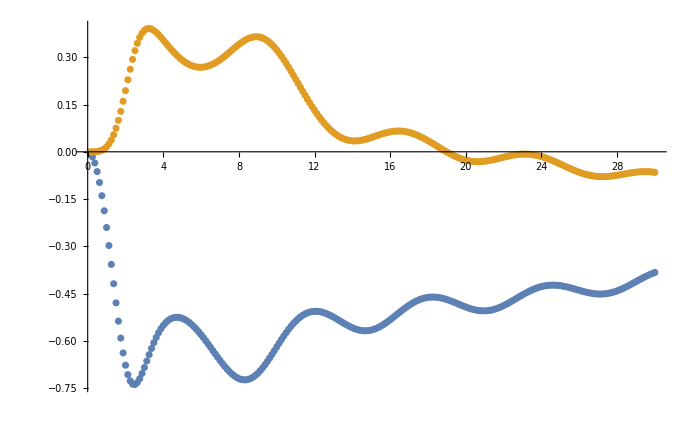

```mathematica
ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v4kTr01[[All,1]],Re[v4kTr01[[All,2,1]]]}]}]
```

### r = 0.25

```mathematica
v2kTr025={};
For[i=1,i≤120,i++,
x1u=1/8{Cos[π/2],Sin[π/2]};
x3u=1/8{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr025,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110680692 near {ϕ$110680692} = {2.3561}. NIntegrate obtained -2.11419×10^-18 and 5.0358×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110754266 near {ϕ$110754266} = {5.22771}. NIntegrate obtained 2.25448×10^-16 and 1.80831×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110874374 near {ϕ$110874374} = {2.08612}. NIntegrate obtained 1.82115×10^-16 and 1.83901×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTr025
```

{{0.25,{-0.0157221,-2.41379×10^-16}},{0.5,{-0.0628756,1.16033×10^-13}},{0.75,{-0.139514,2.41869×10^-13}},{1.,{-0.240682,-9.41755×10^-14}},{1.25,{-0.358253,-7.55837×10^-16}},{1.5,{-0.480566,1.1285×10^-16}},{1.75,{-0.592539,7.92261×10^-10}},{2.,{-0.678149,-6.70196×10^-15}},{2.25,{-0.726055,4.35925×10^-15}},{2.5,{-0.735045,-1.94286×10^-15}},{2.75,{-0.714107,2.50598×10^-15}},{3.,{-0.676825,-7.80316×10^-10}},{3.25,{-0.63525,2.10671×10^-7}},{3.5,{-0.597127,1.51335×10^-15}},{3.75,{-0.566174,1.03888×10^-10}},{4.,{-0.543477,1.1877×10^-15}},{4.25,{-0.528769,3.27477×10^-8}},{4.5,{-0.521233,6.1827×10^-16}},{4.75,{-0.519932,-9.05992×10^-8}},{5.,{-0.523973,3.47998×10^-16}},{5.25,{-0.532572,6.42106×10^-11}},{5.5,{-0.545035,-1.38116×10^-10}},{5.75,{-0.560729,-2.23483×10^-15}},{6.,{-0.579039,3.38877×10^-15}},{6.25,{-0.599325,-3.26078×10^-11}},{6.5,{-0.620877,-2.05654×10^-15}},{6.75,{-0.642886,1.53868×10^-15}},{7.,{-0.664418,1.77479×10^-15}},{7.25,{-0.684415,1.00659×10^-15}},{7.5,{-0.701722,-6.23953×10^-16}},{7.75,{-0.715139,2.25239×10^-15}},{8.,{-0.723523,3.17998×10^-15}},{8.25,{-0.725913,2.10652×10^-15}},{8.5,{-0.721664,1.6207×10^-15}},{8.75,{-0.710577,-5.01832×10^-15}},{9.,{-0.692965,-7.57584×10^-11}},{9.25,{-0.669651,-2.82211×10^-10}},{9.5,{-0.641937,-1.9695×10^-9}},{9.75,{-0.611325,1.14119×10^-9}},{10.,{-0.579539,-5.10811×10^-10}},{10.25,{-0.548201,-1.45764×10^-10}},{10.5,{-0.518731,-1.98419×10^-9}},{10.75,{-0.492295,3.74871×10^-8}},{11.,{-0.469759,6.52556×10^-6}},{11.25,{-0.45166,-2.02602×10^-9}},{11.5,{-0.438295,-8.69866×10^-7}},{11.75,{-0.429698,1.20137×10^-15}},{12.,{-0.425696,8.1348×10^-16}},{12.25,{-0.42594,-1.11964×10^-14}},{12.5,{-0.429913,-1.0847×10^-7}},{12.75,{-0.436951,1.09338×10^-14}},{13.,{-0.446214,-2.71472×10^-15}},{13.25,{-0.456739,1.43915×10^-15}},{13.5,{-0.467414,-9.94575×10^-15}},{13.75,{-0.477044,5.02243×10^-7}},{14.,{-0.484355,-4.10757×10^-7}},{14.25,{-0.48817,-3.62165×10^-10}},{14.5,{-0.487432,6.46763×10^-15}},{14.75,{-0.481372,-7.86929×10^-15}},{15.,{-0.469619,-1.39306×10^-15}},{15.25,{-0.452244,-6.25834×10^-10}},{15.5,{-0.429791,-1.1628×10^-14}},{15.75,{-0.403218,-1.07527×10^-14}},{16.,{-0.373778,-5.27398×10^-7}},{16.25,{-0.342879,-2.90102×10^-7}},{16.5,{-0.31193,-8.95848×10^-7}},{16.75,{-0.282237,-1.65425×10^-9}},{17.,{-0.254889,7.14438×10^-9}},{17.25,{-0.230748,7.93413×10^-8}},{17.5,{-0.210411,-1.74149×10^-8}},{17.75,{-0.194243,2.43155×10^-8}},{18.,{-0.182385,4.86987×10^-9}},{18.25,{-0.174785,4.519×10^-7}},{18.5,{-0.171196,-2.55907×10^-9}},{18.75,{-0.171198,7.27569×10^-15}},{19.,{-0.174184,-5.75667×10^-15}},{19.25,{-0.179345,-9.05611×10^-15}},{19.5,{-0.185657,1.89456×10^-6}},{19.75,{-0.191878,8.16411×10^-9}},{20.,{-0.196565,-2.33297×10^-9}},{20.25,{-0.198138,1.93264×10^-9}},{20.5,{-0.195009,-4.48211×10^-9}},{20.75,{-0.185756,1.23731×10^-8}},{21.,{-0.16933,3.92504×10^-10}},{21.25,{-0.145285,-1.95049×10^-9}},{21.5,{-0.113923,-9.26632×10^-16}},{21.75,{-0.0762806,-1.33097×10^-9}},{22.,{-0.0340279,-1.32369×10^-8}},{22.25,{0.0107713,2.13528×10^-14}},{22.5,{0.0559492,-7.3274×10^-8}},{22.75,{0.0996921,-3.06299×10^-8}},{23.,{0.140306,7.72214×10^-8}},{23.25,{0.176586,-4.51354×10^-8}},{23.5,{0.207716,1.45684×10^-7}},{23.75,{0.23341,-1.44263×10^-7}},{24.,{0.253535,4.66774×10^-8}},{24.25,{0.26813,6.59985×10^-9}},{24.5,{0.277439,-1.79015×10^-7}},{24.75,{0.281807,2.19601×10^-8}},{25.,{0.281729,6.15917×10^-8}},{25.25,{0.277797,-9.25834×10^-16}},{25.5,{0.270708,-1.84115×10^-7}},{25.75,{0.261542,-4.15435×10^-8}},{26.,{0.251566,-3.59209×10^-7}},{26.25,{0.242349,9.22774×10^-8}},{26.5,{0.235681,9.40175×10^-9}},{26.75,{0.233438,-9.03462×10^-8}},{27.,{0.237091,-1.28148×10^-7}},{27.25,{0.24743,-8.29506×10^-8}},{27.5,{0.264215,6.20238×10^-8}},{27.75,{0.28608,-7.58276×10^-7}},{28.,{0.310809,3.69901×10^-8}},{28.25,{0.335914,4.30307×10^-8}},{28.5,{0.359061,-1.41654×10^-8}},{28.75,{0.378408,-1.55423×10^-7}},{29.,{0.392657,-1.4651×10^-7}},{29.25,{0.401143,-7.95764×10^-8}},{29.5,{0.403514,-3.01587×10^-7}},{29.75,{0.39963,3.18068×10^-7}},{30.,{0.389552,-2.93246×10^-7}}}

### r = 0.5

```mathematica
v2kTr05={};
For[i=1,i≤120,i++,
x1u=1/4{Cos[π/2],Sin[π/2]};
x3u=1/4{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119294760 near {ϕ$119294760} = {2.47882}. NIntegrate obtained -4.78133×10^-17 and 1.44362×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119366529 near {ϕ$119366529} = {5.35043}. NIntegrate obtained -1.52×10^-15 and 1.84099×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119452361 near {ϕ$119452361} = {2.08612}. NIntegrate obtained 3.65414×10^-15 and 1.00431×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTr05
```

{{0.25,{-0.0157083,-4.05279×10^-16}},{0.5,{-0.0629432,-5.87232×10^-14}},{0.75,{-0.139938,3.69346×10^-13}},{1.,{-0.241898,-9.80784×10^-14}},{1.25,{-0.360771,-5.61855×10^-15}},{1.5,{-0.484544,2.26672×10^-12}},{1.75,{-0.596931,-9.49207×10^-9}},{2.,{-0.680079,3.49782×10^-16}},{2.25,{-0.721722,6.38164×10^-14}},{2.5,{-0.722091,2.49838×10^-16}},{2.75,{-0.693155,-2.94402×10^-11}},{3.,{-0.650732,-1.1387×10^-16}},{3.25,{-0.6073,-6.59918×10^-8}},{3.5,{-0.569821,7.27002×10^-9}},{3.75,{-0.540937,-2.13394×10^-9}},{4.,{-0.520875,-4.96253×10^-11}},{4.25,{-0.508864,2.21709×10^-8}},{4.5,{-0.503829,2.57298×10^-16}},{4.75,{-0.504775,-2.18389×10^-16}},{5.,{-0.510865,-3.66857×10^-17}},{5.25,{-0.521426,8.46509×10^-9}},{5.5,{-0.535909,1.07528×10^-17}},{5.75,{-0.553836,-8.01161×10^-16}},{6.,{-0.574735,-5.15664×10^-11}},{6.25,{-0.59807,4.81692×10^-11}},{6.5,{-0.623166,-5.52602×10^-11}},{6.75,{-0.649125,1.71295×10^-12}},{7.,{-0.674739,-4.81775×10^-9}},{7.25,{-0.698413,1.27876×10^-11}},{7.5,{-0.718119,-5.09679×10^-16}},{7.75,{-0.731428,3.58282×10^-16}},{8.,{-0.735652,4.56242×10^-11}},{8.25,{-0.728158,5.86217×10^-11}},{8.5,{-0.706838,1.58122×10^-10}},{8.75,{-0.670635,-1.38826×10^-15}},{9.,{-0.62004,-2.96106×10^-10}},{9.25,{-0.557219,4.88726×10^-9}},{9.5,{-0.485783,9.0896×10^-10}},{9.75,{-0.410139,1.64442×10^-10}},{10.,{-0.334779,7.18462×10^-10}},{10.25,{-0.26357,-3.57671×10^-11}},{10.5,{-0.199404,6.10921×10^-10}},{10.75,{-0.144114,9.10481×10^-8}},{11.,{-0.0986211,1.1569×10^-10}},{11.25,{-0.0631837,1.18439×10^-15}},{11.5,{-0.0376296,-1.59247×10^-7}},{11.75,{-0.0215857,-4.73678×10^-7}},{12.,{-0.0145918,-7.96459×10^-8}},{12.25,{-0.0161928,1.65863×10^-7}},{12.5,{-0.0258911,-8.5204×10^-9}},{12.75,{-0.0430249,1.1516×10^-9}},{13.,{-0.0664803,5.12141×10^-9}},{13.25,{-0.0941586,-5.66777×10^-9}},{13.5,{-0.122195,4.6751×10^-9}},{13.75,{-0.144104,1.74337×10^-6}},{14.,{-0.15066,-6.65365×10^-9}},{14.25,{-0.132114,-1.69542×10^-10}},{14.5,{-0.0835191,-7.2797×10^-9}},{14.75,{-0.0101311,1.29645×10^-15}},{15.,{0.0735168,-7.18798×10^-7}},{15.25,{0.151394,-4.97429×10^-9}},{15.5,{0.213157,-4.76828×10^-9}},{15.75,{0.255481,8.14981×10^-10}},{16.,{0.279479,4.50999×10^-9}},{16.25,{0.287917,-2.37955×10^-10}},{16.5,{0.283549,3.42012×10^-7}},{16.75,{0.268481,-7.44833×10^-9}},{17.,{0.244103,3.27938×10^-9}},{17.25,{0.21112,2.71377×10^-9}},{17.5,{0.169755,1.39416×10^-8}},{17.75,{0.119866,-6.17876×10^-9}},{18.,{0.0611568,-6.15851×10^-9}},{18.25,{-0.00661805,1.67143×10^-6}},{18.5,{-0.0832651,1.10075×10^-9}},{18.75,{-0.167669,-1.83698×10^-7}},{19.,{-0.257121,-2.6934×10^-8}},{19.25,{-0.346624,-1.69342×10^-9}},{19.5,{-0.428522,8.65665×10^-9}},{19.75,{-0.493118,3.27587×10^-8}},{20.,{-0.530749,1.19917×10^-8}},{20.25,{-0.535007,-4.04218×10^-8}},{20.5,{-0.505446,-2.28124×10^-8}},{20.75,{-0.447996,1.29209×10^-8}},{21.,{-0.372535,4.51847×10^-9}},{21.25,{-0.289643,-1.67224×10^-9}},{21.5,{-0.207919,-3.64643×10^-8}},{21.75,{-0.133098,-1.85069×10^-9}},{22.,{-0.0682472,1.90379×10^-8}},{22.25,{-0.0145597,-3.33865×10^-9}},{22.5,{0.0278852,7.19541×10^-9}},{22.75,{0.059524,-2.58159×10^-8}},{23.,{0.0809921,-2.95193×10^-8}},{23.25,{0.0928221,8.59615×10^-8}},{23.5,{0.095319,-1.53925×10^-8}},{23.75,{0.0887274,-1.50672×10^-7}},{24.,{0.0730315,-7.58447×10^-8}},{24.25,{0.0480879,-4.15413×10^-7}},{24.5,{0.0139053,-1.33382×10^-7}},{24.75,{-0.0290157,-1.46488×10^-8}},{25.,{-0.0790213,-1.42553×10^-7}},{25.25,{-0.13237,-1.69672×10^-7}},{25.5,{-0.182334,-9.24631×10^-9}},{25.75,{-0.219003,2.47004×10^-7}},{26.,{-0.231491,-7.38519×10^-9}},{26.25,{-0.21255,-2.8724×10^-8}},{26.5,{-0.163133,0.0000115338}},{26.75,{-0.092653,-4.87498×10^-8}},{27.,{-0.0143494,4.30797×10^-8}},{27.25,{0.0604248,-6.9454×10^-8}},{27.5,{0.124699,1.10051×10^-7}},{27.75,{0.175607,4.43614×10^-8}},{28.,{0.212727,-7.47863×10^-8}},{28.25,{0.237009,-1.3122×10^-7}},{28.5,{0.249544,3.95598×10^-7}},{28.75,{0.251302,-2.36994×10^-7}},{29.,{0.242966,6.18428×10^-8}},{29.25,{0.224815,-2.71616×10^-8}},{29.5,{0.196861,-3.14431×10^-7}},{29.75,{0.158859,7.58288×10^-8}},{30.,{0.110689,2.90214×10^-8}}}

### r = 1

#### b = 1

```mathematica
v2kT={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137465713 near {ϕ$137465713} = {1.04301}. NIntegrate obtained 1.98183×10^-14 and 5.06602×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137556301 near {ϕ$137556301} = {4.45458}. NIntegrate obtained 2.59974×10^-14 and 2.56419×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137665585 near {ϕ$137665585} = {5.22771}. NIntegrate obtained 1.00625×10^-13 and 3.28241×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
v2kT
```

{{0.25,{-0.0153703,1.77692×10^-14}},{0.5,{-0.0620339,1.10448×10^-13}},{0.75,{-0.138959,1.17468×10^-12}},{1.,{-0.242273,-3.70558×10^-13}},{1.25,{-0.364797,2.033×10^-10}},{1.5,{-0.493546,-1.37362×10^-13}},{1.75,{-0.606603,3.51993×10^-12}},{2.,{-0.677615,-7.85472×10^-17}},{2.25,{-0.69319,2.55159×10^-9}},{2.5,{-0.664932,-1.65424×10^-11}},{2.75,{-0.617398,3.18941×10^-10}},{3.,{-0.569738,-1.90247×10^-11}},{3.25,{-0.530485,-1.81875×10^-8}},{3.5,{-0.501266,2.36214×10^-12}},{3.75,{-0.480934,7.72866×10^-11}},{4.,{-0.467766,2.40431×10^-12}},{4.25,{-0.460269,2.28429×10^-9}},{4.5,{-0.457377,-2.646×10^-10}},{4.75,{-0.45843,-7.48485×10^-9}},{5.,{-0.463108,-1.37125×10^-9}},{5.25,{-0.47137,3.44803×10^-9}},{5.5,{-0.483405,-1.30649×10^-16}},{5.75,{-0.499585,1.42334×10^-11}},{6.,{-0.520401,2.74762×10^-10}},{6.25,{-0.546295,2.53357×10^-15}},{6.5,{-0.577233,-1.93072×10^-15}},{6.75,{-0.611625,-1.14548×10^-11}},{7.,{-0.643758,-2.46894×10^-11}},{7.25,{-0.658651,-2.26715×10^-10}},{7.5,{-0.626095,-2.9069×10^-10}},{7.75,{-0.509444,-2.82749×10^-9}},{8.,{-0.3127,-1.49843×10^-10}},{8.25,{-0.110023,1.76213×10^-8}},{8.5,{0.0293966,7.26664×10^-9}},{8.75,{0.0991128,5.15503×10^-8}},{9.,{0.123171,-6.38262×10^-9}},{9.25,{0.123018,-9.50091×10^-10}},{9.5,{0.110967,2.62038×10^-10}},{9.75,{0.0929324,-1.34412×10^-9}},{10.,{0.071309,8.47169×10^-9}},{10.25,{0.0467296,4.33892×10^-8}},{10.5,{0.0189296,4.93291×10^-8}},{10.75,{-0.0127806,3.43465×10^-9}},{11.,{-0.0491431,-8.79825×10^-10}},{11.25,{-0.0905767,6.46263×10^-9}},{11.5,{-0.136709,-1.10339×10^-8}},{11.75,{-0.185819,1.56697×10^-8}},{12.,{-0.234489,9.49791×10^-10}},{12.25,{-0.277797,-1.80933×10^-8}},{12.5,{-0.310366,3.04244×10^-8}},{12.75,{-0.32795,1.95269×10^-8}},{13.,{-0.328691,7.78354×10^-10}},{13.25,{-0.313306,-3.29113×10^-8}},{13.5,{-0.284242,-3.70662×10^-9}},{13.75,{-0.244548,4.24948×10^-9}},{14.,{-0.197058,9.23277×10^-8}},{14.25,{-0.144132,-6.46267×10^-9}},{14.5,{-0.0878284,9.0544×10^-9}},{14.75,{-0.0302958,-1.03988×10^-8}},{15.,{0.0257865,-4.41467×10^-9}},{15.25,{0.0769866,-7.50119×10^-10}},{15.5,{0.119312,-1.63202×10^-7}},{15.75,{0.148943,-3.98118×10^-8}},{16.,{0.163312,6.77564×10^-9}},{16.25,{0.161955,1.0904×10^-8}},{16.5,{0.146655,2.39442×10^-8}},{16.75,{0.120628,8.18727×10^-9}},{17.,{0.0875722,-2.41548×10^-8}},{17.25,{0.0506979,5.20923×10^-9}},{17.5,{0.0123565,-8.49207×10^-9}},{17.75,{-0.0259929,3.22052×10^-8}},{18.,{-0.0635916,-7.18094×10^-8}},{18.25,{-0.100094,-5.76294×10^-8}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19.,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20.,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21.,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22.,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23.,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}},{23.75,{0.0352241,-1.93356×10^-7}},{24.,{0.00412,3.49766×10^-7}},{24.25,{-0.0327422,1.24181×10^-10}},{24.5,{-0.0745895,3.26366×10^-7}},{24.75,{-0.119062,5.44607×10^-8}},{25.,{-0.161741,-1.68162×10^-7}},{25.25,{-0.196578,-1.13476×10^-7}},{25.5,{-0.217601,1.07283×10^-7}},{25.75,{-0.221355,-4.87923×10^-7}},{26.,{-0.208227,1.21816×10^-7}},{26.25,{-0.181843,-6.59003×10^-8}},{26.5,{-0.147045,2.41588×10^-7}},{26.75,{-0.108162,8.39299×10^-8}},{27.,{-0.06843,1.28776×10^-7}},{27.25,{-0.0298023,1.62718×10^-7}},{27.5,{0.00651692,-4.51779×10^-7}},{27.75,{0.0397111,2.1227×10^-7}},{28.,{0.0690481,5.04303×10^-8}},{28.25,{0.0936486,1.01842×10^-7}},{28.5,{0.112412,2.22292×10^-7}},{28.75,{0.124098,2.17534×10^-7}},{29.,{0.127522,-1.62677×10^-7}},{29.25,{0.121893,8.59436×10^-8}},{29.5,{0.10717,-1.08371×10^-7}},{29.75,{0.0842682,1.87234×10^-8}},{30.,{0.0550126,-4.363×10^-7}}}

```mathematica
v2kT={};
For[i=1,i≤240,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kT
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172623638 near {ϕ$172623638} = {2.57699}. NIntegrate obtained -4.16334×10^-17 and 4.88864×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172717834 near {ϕ$172717834} = {1.04301}. NIntegrate obtained 1.98183×10^-14 and 5.06602×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172808422 near {ϕ$172808422} = {0.326199}. NIntegrate obtained -1.13828×10^-14 and 5.5298×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
{{0.125,{-0.0038145666343051333,-8.770296131118043*^-18}},{0.25,{-0.015370303774242809,1.7769218865201226*^-14}},{0.375,{-0.03478799715529221,-2.485673761449122*^-14}},{0.5,{-0.062033854653153135,1.1044824126021148*^-13}},{0.625,{-0.09688970636896405,-4.802867840181144*^-14}},{0.75,{-0.13895894530129987,1.1746760402533138*^-12}},{0.875,{-0.18767201809769854,1.3599308973306837*^-13}},{1.,{-0.24227284840377084,-3.705584516153792*^-13}},{1.125,{-0.3017631071327574,8.40659185454109*^-15}},{1.25,{-0.36479685257132444,2.03300275408307*^-10}},{1.375,{-0.4295408726611799,1.4346608999221128*^-11}},{1.5,{-0.4935462545338007,-1.3736245507186947*^-13}},{1.625,{-0.55373373845127,2.7687515447364226*^-13}},{1.75,{-0.6066027342700241,3.5199298986767468*^-12}},{1.875,{-0.6487510075044597,-7.95501088320471*^-9}},{2.,{-0.677615358940052,-7.854719824280913*^-17}},{2.125,{-0.6921638988980808,-5.877907199455664*^-17}},{2.25,{-0.6931901738297919,2.5515907936889136*^-9}},{2.375,{-0.6830488591849327,-2.7070759933888894*^-11}},{2.5,{-0.6649321089100702,-1.6542396658808482*^-11}},{2.625,{-0.6421181509627638,-7.19807111204913*^-17}},{2.75,{-0.6173983354122009,3.1894069697736614*^-10}},{2.875,{-0.5928295382586416,-8.652219940414481*^-11}},{3.,{-0.5697384783058826,-1.9024686676086125*^-11}},{3.125,{-0.5488552806539309,4.357910267936902*^-9}},{3.25,{-0.5304853678478362,-1.8187476613841656*^-8}},{3.375,{-0.514662487111251,3.205852917590607*^-11}},{3.5,{-0.5012655434825574,2.362139232379727*^-12}},{3.625,{-0.49009685235904876,1.2062354309457428*^-9}},{3.75,{-0.4809341348538826,7.728655260097078*^-11}},{3.875,{-0.4735567521374093,2.1669551987315467*^-11}},{4.,{-0.46776639040835283,2.4043099076459743*^-12}},{4.125,{-0.46338572729979044,-1.9871356255715666*^-9}},{4.25,{-0.4602694766355951,2.2842938117113635*^-9}},{4.375,{-0.4582975020517393,4.112738034263924*^-11}},{4.5,{-0.45737709848908636,-2.6459958623624444*^-10}},{4.625,{-0.45743666609035105,1.4689147078888108*^-9}},{4.75,{-0.45842964327899915,-7.484851498416402*^-9}},{4.875,{-0.46032370275658935,-2.5713707684613013*^-10}},{5.,{-0.46310779021610066,-1.3712534670396533*^-9}},{5.125,{-0.4667837438238167,-1.0239570442654021*^-10}},{5.25,{-0.47137016379617547,3.4480297702592567*^-9}},{5.375,{-0.47689639658224264,1.0185882805063667*^-8}},{5.5,{-0.48340462829858677,-1.3064862821084218*^-16}},{5.625,{-0.4909475202400304,-3.5885111347141615*^-10}},{5.75,{-0.4995850244361453,1.423344748949777*^-11}},{5.875,{-0.5093816166836549,2.987297297810001*^-12}},{6.,{-0.5204009405259216,2.7476150804417533*^-10}},{6.125,{-0.532695887360128,-5.111586286447776*^-16}},{6.25,{-0.5462945270855182,2.533566513832376*^-15}},{6.375,{-0.5611759244807163,-1.0918216923616846*^-15}},{6.5,{-0.5772326695516907,-1.9307243431914002*^-15}},{6.625,{-0.5942085617851417,6.527851703397193*^-7}},{6.75,{-0.611624941261184,-1.145481241545447*^-11}},{6.875,{-0.6286119048809296,-1.2352274845334554*^-9}},{7.,{-0.6437578704106229,-2.4689414366078834*^-11}},{7.125,{-0.6548516017335444,4.020902932626045*^-16}},{7.25,{-0.6586511454450078,-2.2671543457063428*^-10}},{7.375,{-0.6507856659168332,-4.8029998958123*^-10}},{7.5,{-0.6260948798292884,-2.906903758874852*^-10}},{7.625,{-0.5797587653386406,2.6468322330340016*^-8}},{7.75,{-0.5094436060825578,-2.8274905450754082*^-9}},{7.875,{-0.4176696638240725,1.165557385667161*^-10}},{8.,{-0.3127001568032249,-1.4984272522717237*^-10}},{8.125,{-0.20640431457964284,7.784916453572846*^-10}},{8.25,{-0.11002346166297973,1.76213080455171*^-8}},{8.375,{-0.030688480328536598,-5.073079848895744*^-10}},{8.5,{0.029396586686098465,7.266637614962103*^-9}},{8.625,{0.07162741303856758,4.798172958532609*^-8}},{8.75,{0.09911283511377558,5.15503078078277*^-8}},{8.875,{0.1152854257435328,5.150587837327192*^-9}},{9.,{0.12317100288371782,-6.3826171831989315*^-9}},{9.125,{0.1251598556590087,-3.863930324180945*^-8}},{9.25,{0.12301824022670999,-9.50091362653667*^-10}},{9.375,{0.11797926505274271,-8.726014206656516*^-10}},{9.5,{0.1109669876096405,2.620381383439199*^-10}},{9.625,{0.10249356506802704,9.218029505727073*^-10}},{9.75,{0.09293238374440915,-1.3441154978021209*^-9}},{9.875,{0.08249896886222301,-5.546269484549476*^-9}},{10.,{0.07130896973595931,8.47169445824443*^-9}},{10.125,{0.05939273342600049,6.750027719013291*^-10}},{10.25,{0.04672958171071315,4.33892282797973*^-8}},{10.375,{0.03327021167474194,2.9074247340966017*^-9}},{10.5,{0.018929582991274403,4.932907672318059*^-8}},{10.625,{0.0036110335040011156,1.92512293299272*^-8}},{10.75,{-0.012780556695824017,3.4346509102841225*^-9}},{10.875,{-0.03034027081431167,4.324260429674358*^-8}},{11.,{-0.04914309652831915,-8.798252620692403*^-10}},{11.125,{-0.06922330171874276,-2.190145471428356*^-10}},{11.25,{-0.090576688316893,6.4626269237177645*^-9}},{11.375,{-0.11311812352551533,1.0529468814856192*^-8}},{11.5,{-0.136708521058601,-1.1033906130299018*^-8}},{11.625,{-0.1610636412417012,4.242955871885293*^-11}},{11.75,{-0.18581935335879288,1.566971093523524*^-8}},{11.875,{-0.21048962466790191,6.003760530631209*^-9}},{12.,{-0.23448917168911598,9.497906648349837*^-10}},{12.125,{-0.2571550525975473,-6.831782446148319*^-8}},{12.25,{-0.27779716282642714,-1.8093309951838823*^-8}},{12.375,{-0.2957334481632961,2.3175546121128544*^-9}},{12.5,{-0.3103659708978077,3.042438163936668*^-8}},{12.625,{-0.3212096395353938,2.588294890963012*^-8}},{12.75,{-0.32794959786110156,1.952688159417017*^-8}},{12.875,{-0.33043471585181744,7.466464731199854*^-7}},{13.,{-0.3286914992406541,7.783544369806296*^-10}},{13.125,{-0.32288791563580826,1.3832461642299231*^-9}},{13.25,{-0.3133057245055995,-3.291125763139785*^-8}},{13.375,{-0.30029388605755963,-9.466693757195717*^-9}},{13.5,{-0.2842418950802804,-3.7066213982523582*^-9}},{13.625,{-0.2655358682344628,2.4052208234159764*^-9}},{13.75,{-0.24454795541806823,4.249484658791227*^-9}},{13.875,{-0.22161861851500086,-4.267003248770652*^-9}},{14.,{-0.19705760854870333,9.232773458052011*^-8}},{14.125,{-0.17115148392152654,7.230774471952747*^-11}},{14.25,{-0.14413238248873098,-6.4626660365719775*^-9}},{14.375,{-0.11627533859694629,-3.95151809436999*^-9}},{14.5,{-0.08782837791280503,9.054399528965831*^-9}},{14.625,{-0.059064600501465676,-1.815661943082681*^-8}},{14.75,{-0.030295842098810748,-1.0398767252133559*^-8}},{14.875,{-0.00187656100414676,9.564632506909921*^-8}},{15.,{0.025786526327060313,-4.4146709066272754*^-9}},{15.125,{0.05224030733121436,1.2145866373786358*^-7}},{15.25,{0.07698661849629682,-7.501192091078092*^-10}},{15.375,{0.09951677222373859,-2.395759501218834*^-7}},{15.5,{0.11931185030441603,-1.6320169373384063*^-7}},{15.625,{0.13591855458098143,2.6323438436675254*^-8}},{15.75,{0.14894312415829705,-3.9811813532938125*^-8}},{15.875,{0.15811920441716093,-6.571553518005781*^-7}},{16.,{0.16331182862433666,6.775642060945504*^-9}},{16.125,{0.16453632164043125,3.451776923005785*^-7}},{16.25,{0.16195530127928567,1.0904008548060991*^-8}},{16.375,{0.15586566820540948,-5.856106208189421*^-9}},{16.5,{0.14665473514453153,2.3944201313874438*^-8}},{16.625,{0.1347449033628869,-5.94791375086431*^-8}},{16.75,{0.1206284574361209,8.18726790090496*^-9}},{16.875,{0.10476255950741153,1.597787739307408*^-8}},{17.,{0.08757222390690272,-2.4154818888100097*^-8}},{17.125,{0.06944332511167735,-1.7255325887560422*^-8}},{17.25,{0.05069788314207085,5.209228323515558*^-9}},{17.375,{0.031602080784626285,5.3851957648149655*^-9}},{17.5,{0.012356457924273449,-8.492074884500232*^-9}},{17.625,{-0.006878400069119971,5.071649221215491*^-8}},{17.75,{-0.025992938167556212,3.2205245879034055*^-8}},{17.875,{-0.044915026683393595,2.8235149488587112*^-8}},{18.,{-0.0635915975354855,-7.180941484215929*^-8}},{18.125,{-0.08199376720334547,2.2421869553245094*^-8}},{18.25,{-0.10009379366472551,-5.7629362680555393*^-8}},{18.375,{-0.1178717396323955,-5.308192498435593*^-8}},{18.5,{-0.13528958020224263,1.2843834481107857*^-8}},{18.625,{-0.15229746178705766,1.1577887120470588*^-8}},{18.75,{-0.16880500291898254,3.0828820042084766*^-8}},{18.875,{-0.18468008243409265,4.022618542525332*^-9}},{19.,{-0.1997420713822689,1.2841134839065155*^-8}},{19.125,{-0.21372394031556527,9.339306251395149*^-9}},{19.25,{-0.22627881062030591,-8.61930011278599*^-9}},{19.375,{-0.2369575412087999,-1.4205010381434548*^-7}},{19.5,{-0.2452172603062858,-1.6140369547695166*^-8}},{19.625,{-0.2504187027300958,-2.2053764660425456*^-8}},{19.75,{-0.25186087080652686,-2.6623312486213505*^-8}},{19.875,{-0.24886432146159176,-1.8278743642287222*^-8}},{20.,{-0.24083540469107942,1.907883119889603*^-8}},{20.125,{-0.22740252143494968,-1.8959363795010147*^-8}},{20.25,{-0.20853636764698505,-1.9073111494478228*^-8}},{20.375,{-0.18464289289575359,-2.2476774938629513*^-8}},{20.5,{-0.1565706658835486,2.3200394321981184*^-8}},{20.625,{-0.1255751940461361,1.1354988784566779*^-9}},{20.75,{-0.09311662767328212,-1.6078359424170658*^-9}},{20.875,{-0.06069130510378376,-2.5510781720197452*^-8}},{21.,{-0.02964418925000249,4.008578860586756*^-8}},{21.125,{-0.0010140404149581437,-6.349580893147823*^-9}},{21.25,{0.02450334873765068,1.836253019961593*^-8}},{21.375,{0.04655469382496608,4.8848136632172036*^-9}},{21.5,{0.06505843044393464,-1.7130306603637772*^-8}},{21.625,{0.08013400717415561,-6.907034236865978*^-8}},{21.75,{0.09202558699541653,3.627621394360486*^-9}},{21.875,{0.10104344129153521,1.4669503918614154*^-8}},{22.,{0.10750560900676612,-5.252652172720938*^-8}},{22.125,{0.11172219745225771,2.5009921938664007*^-8}},{22.25,{0.11397008494126462,-1.0340229048122765*^-8}},{22.375,{0.11449078898693496,-1.345958034283419*^-7}},{22.5,{0.11346574600033521,-3.85159791992006*^-8}},{22.625,{0.1110712899168813,-9.149304463872573*^-8}},{22.75,{0.10739191788629823,-9.994343755065057*^-8}},{22.875,{0.10251885983416134,1.0651013568898881*^-7}},{23.,{0.09648263405551326,-1.8618768637936514*^-7}},{23.125,{0.08931086904126878,7.093198429341704*^-8}},{23.25,{0.0809875810098753,8.222807097935609*^-8}},{23.375,{0.07145716992352505,-1.6800102889758003*^-7}},{23.5,{0.06069747547032684,-1.9006903612493493*^-7}},{23.625,{0.04864499290638047,3.785554618475615*^-8}},{23.75,{0.035224072437261875,-1.9335605736010814*^-7}},{23.875,{0.020397904336888865,2.646037286004819*^-7}},{24.,{0.004120000250285188,3.497660527738634*^-7}},{24.125,{-0.013610565905500437,2.0090207442280426*^-7}},{24.25,{-0.03274223117264212,1.2418090260350386*^-10}},{24.375,{-0.05314638046247782,2.451838671469473*^-7}},{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v4kTr01[[All,1]],Re[v4kTr01[[All,2,1]]]}]}]24.5,{-0.074589548795838,3.2636615680707444*^-7}},{24.625,{-0.09672378684794822,1.4244828000456934*^-7}},{24.75,{-0.11906174069597159,5.446074673066934*^-8}},{24.875,{-0.14097423975266055,-2.218367282414495*^-8}},{25.,{-0.16174085280010547,-1.6816166733325572*^-7}},{25.125,{-0.1805406556886541,-1.433516818957498*^-7}},{25.25,{-0.19657752903538464,-1.1347595581348781*^-7}},{25.375,{-0.20911611252246826,-1.1519862171122622*^-7}},{25.5,{-0.21760115667704305,1.0728266843237122*^-7}},{25.625,{-0.22170261856420678,2.3440341327054375*^-7}},{25.75,{-0.22135530947741341,-4.879233309556845*^-7}},{25.875,{-0.21672981391035637,-1.4218883005669763*^-7}},{26.,{-0.20822656367240502,1.218161122109372*^-7}},{26.125,{-0.19639636606724714,8.100550539477312*^-7}},{26.25,{-0.18184339390327633,-6.590028213718615*^-8}},{26.375,{-0.16519115228506792,1.3669169847766928*^-7}},{26.5,{-0.14704513769213645,2.415876776269508*^-7}},{26.625,{-0.1278768047468305,3.4425429795674145*^-7}},{26.75,{-0.10816248250822058,8.392993596909107*^-8}},{26.875,{-0.08826150384698674,4.077629036161783*^-7}},{27.,{-0.06843004873430975,1.2877566638553538*^-7}},{27.125,{-0.04888997227635365,-4.98843349273612*^-7}},{27.25,{-0.02980228240468462,1.6271806740265945*^-7}},{27.375,{-0.011298320087779614,9.842329651647929*^-8}},{27.5,{0.00651692447581312,-4.517788570104052*^-7}},{27.625,{0.023550594933635212,1.8898300969370754*^-7}},{27.75,{0.03971106544028546,2.12269775634385*^-7}},{27.875,{0.054919696076814815,2.338265396311496*^-8}},{28.,{0.06904811337710506,5.043033016240346*^-8}},{28.125,{0.08200343414429004,1.4879430408371898*^-7}},{28.25,{0.09364864844663295,1.0184164896006994*^-7}},{28.375,{0.10383615793196048,5.229567518913376*^-8}},{28.5,{0.11241161213775382,2.2229187005210472*^-7}},{28.625,{0.11921839082233468,2.4144626597174657*^-7}},{28.75,{0.12409777221326003,2.1753433556520006*^-7}},{28.875,{0.12690641346936135,2.734557337650676*^-7}},{29.,{0.12752226221839869,-1.6267679742047877*^-7}},{29.125,{0.12586645696691046,-1.9717192591996535*^-7}},{29.25,{0.1218927091839019,8.594358628600922*^-8}},{29.375,{0.11563509839763449,-2.8414361155551573*^-7}},{29.5,{0.10716956129891317,-1.0837082157693481*^-7}},{29.625,{0.09664706698571604,4.6860156403408514*^-7}},{29.75,{0.08426817499022542,1.8723369294340568*^-8}},{29.875,{0.07029714424057545,-2.7226333746782884*^-8}},{30.,{0.05501261160481038,-4.3629956338177634*^-7}}}
```

```mathematica
v2kT={{0.125,{-0.0038145666343051333,-8.770296131118043*^-18}},{0.25,{-0.015370303774242809,1.7769218865201226*^-14}},{0.375,{-0.03478799715529221,-2.485673761449122*^-14}},{0.5,{-0.062033854653153135,1.1044824126021148*^-13}},{0.625,{-0.09688970636896405,-4.802867840181144*^-14}},{0.75,{-0.13895894530129987,1.1746760402533138*^-12}},{0.875,{-0.18767201809769854,1.3599308973306837*^-13}},{1.,{-0.24227284840377084,-3.705584516153792*^-13}},{1.125,{-0.3017631071327574,8.40659185454109*^-15}},{1.25,{-0.36479685257132444,2.03300275408307*^-10}},{1.375,{-0.4295408726611799,1.4346608999221128*^-11}},{1.5,{-0.4935462545338007,-1.3736245507186947*^-13}},{1.625,{-0.55373373845127,2.7687515447364226*^-13}},{1.75,{-0.6066027342700241,3.5199298986767468*^-12}},{1.875,{-0.6487510075044597,-7.95501088320471*^-9}},{2.,{-0.677615358940052,-7.854719824280913*^-17}},{2.125,{-0.6921638988980808,-5.877907199455664*^-17}},{2.25,{-0.6931901738297919,2.5515907936889136*^-9}},{2.375,{-0.6830488591849327,-2.7070759933888894*^-11}},{2.5,{-0.6649321089100702,-1.6542396658808482*^-11}},{2.625,{-0.6421181509627638,-7.19807111204913*^-17}},{2.75,{-0.6173983354122009,3.1894069697736614*^-10}},{2.875,{-0.5928295382586416,-8.652219940414481*^-11}},{3.,{-0.5697384783058826,-1.9024686676086125*^-11}},{3.125,{-0.5488552806539309,4.357910267936902*^-9}},{3.25,{-0.5304853678478362,-1.8187476613841656*^-8}},{3.375,{-0.514662487111251,3.205852917590607*^-11}},{3.5,{-0.5012655434825574,2.362139232379727*^-12}},{3.625,{-0.49009685235904876,1.2062354309457428*^-9}},{3.75,{-0.4809341348538826,7.728655260097078*^-11}},{3.875,{-0.4735567521374093,2.1669551987315467*^-11}},{4.,{-0.46776639040835283,2.4043099076459743*^-12}},{4.125,{-0.46338572729979044,-1.9871356255715666*^-9}},{4.25,{-0.4602694766355951,2.2842938117113635*^-9}},{4.375,{-0.4582975020517393,4.112738034263924*^-11}},{4.5,{-0.45737709848908636,-2.6459958623624444*^-10}},{4.625,{-0.45743666609035105,1.4689147078888108*^-9}},{4.75,{-0.45842964327899915,-7.484851498416402*^-9}},{4.875,{-0.46032370275658935,-2.5713707684613013*^-10}},{5.,{-0.46310779021610066,-1.3712534670396533*^-9}},{5.125,{-0.4667837438238167,-1.0239570442654021*^-10}},{5.25,{-0.47137016379617547,3.4480297702592567*^-9}},{5.375,{-0.47689639658224264,1.0185882805063667*^-8}},{5.5,{-0.48340462829858677,-1.3064862821084218*^-16}},{5.625,{-0.4909475202400304,-3.5885111347141615*^-10}},{5.75,{-0.4995850244361453,1.423344748949777*^-11}},{5.875,{-0.5093816166836549,2.987297297810001*^-12}},{6.,{-0.5204009405259216,2.7476150804417533*^-10}},{6.125,{-0.532695887360128,-5.111586286447776*^-16}},{6.25,{-0.5462945270855182,2.533566513832376*^-15}},{6.375,{-0.5611759244807163,-1.0918216923616846*^-15}},{6.5,{-0.5772326695516907,-1.9307243431914002*^-15}},{6.625,{-0.5942085617851417,6.527851703397193*^-7}},{6.75,{-0.611624941261184,-1.145481241545447*^-11}},{6.875,{-0.6286119048809296,-1.2352274845334554*^-9}},{7.,{-0.6437578704106229,-2.4689414366078834*^-11}},{7.125,{-0.6548516017335444,4.020902932626045*^-16}},{7.25,{-0.6586511454450078,-2.2671543457063428*^-10}},{7.375,{-0.6507856659168332,-4.8029998958123*^-10}},{7.5,{-0.6260948798292884,-2.906903758874852*^-10}},{7.625,{-0.5797587653386406,2.6468322330340016*^-8}},{7.75,{-0.5094436060825578,-2.8274905450754082*^-9}},{7.875,{-0.4176696638240725,1.165557385667161*^-10}},{8.,{-0.3127001568032249,-1.4984272522717237*^-10}},{8.125,{-0.20640431457964284,7.784916453572846*^-10}},{8.25,{-0.11002346166297973,1.76213080455171*^-8}},{8.375,{-0.030688480328536598,-5.073079848895744*^-10}},{8.5,{0.029396586686098465,7.266637614962103*^-9}},{8.625,{0.07162741303856758,4.798172958532609*^-8}},{8.75,{0.09911283511377558,5.15503078078277*^-8}},{8.875,{0.1152854257435328,5.150587837327192*^-9}},{9.,{0.12317100288371782,-6.3826171831989315*^-9}},{9.125,{0.1251598556590087,-3.863930324180945*^-8}},{9.25,{0.12301824022670999,-9.50091362653667*^-10}},{9.375,{0.11797926505274271,-8.726014206656516*^-10}},{9.5,{0.1109669876096405,2.620381383439199*^-10}},{9.625,{0.10249356506802704,9.218029505727073*^-10}},{9.75,{0.09293238374440915,-1.3441154978021209*^-9}},{9.875,{0.08249896886222301,-5.546269484549476*^-9}},{10.,{0.07130896973595931,8.47169445824443*^-9}},{10.125,{0.05939273342600049,6.750027719013291*^-10}},{10.25,{0.04672958171071315,4.33892282797973*^-8}},{10.375,{0.03327021167474194,2.9074247340966017*^-9}},{10.5,{0.018929582991274403,4.932907672318059*^-8}},{10.625,{0.0036110335040011156,1.92512293299272*^-8}},{10.75,{-0.012780556695824017,3.4346509102841225*^-9}},{10.875,{-0.03034027081431167,4.324260429674358*^-8}},{11.,{-0.04914309652831915,-8.798252620692403*^-10}},{11.125,{-0.06922330171874276,-2.190145471428356*^-10}},{11.25,{-0.090576688316893,6.4626269237177645*^-9}},{11.375,{-0.11311812352551533,1.0529468814856192*^-8}},{11.5,{-0.136708521058601,-1.1033906130299018*^-8}},{11.625,{-0.1610636412417012,4.242955871885293*^-11}},{11.75,{-0.18581935335879288,1.566971093523524*^-8}},{11.875,{-0.21048962466790191,6.003760530631209*^-9}},{12.,{-0.23448917168911598,9.497906648349837*^-10}},{12.125,{-0.2571550525975473,-6.831782446148319*^-8}},{12.25,{-0.27779716282642714,-1.8093309951838823*^-8}},{12.375,{-0.2957334481632961,2.3175546121128544*^-9}},{12.5,{-0.3103659708978077,3.042438163936668*^-8}},{12.625,{-0.3212096395353938,2.588294890963012*^-8}},{12.75,{-0.32794959786110156,1.952688159417017*^-8}},{12.875,{-0.33043471585181744,7.466464731199854*^-7}},{13.,{-0.3286914992406541,7.783544369806296*^-10}},{13.125,{-0.32288791563580826,1.3832461642299231*^-9}},{13.25,{-0.3133057245055995,-3.291125763139785*^-8}},{13.375,{-0.30029388605755963,-9.466693757195717*^-9}},{13.5,{-0.2842418950802804,-3.7066213982523582*^-9}},{13.625,{-0.2655358682344628,2.4052208234159764*^-9}},{13.75,{-0.24454795541806823,4.249484658791227*^-9}},{13.875,{-0.22161861851500086,-4.267003248770652*^-9}},{14.,{-0.19705760854870333,9.232773458052011*^-8}},{14.125,{-0.17115148392152654,7.230774471952747*^-11}},{14.25,{-0.14413238248873098,-6.4626660365719775*^-9}},{14.375,{-0.11627533859694629,-3.95151809436999*^-9}},{14.5,{-0.08782837791280503,9.054399528965831*^-9}},{14.625,{-0.059064600501465676,-1.815661943082681*^-8}},{14.75,{-0.030295842098810748,-1.0398767252133559*^-8}},{14.875,{-0.00187656100414676,9.564632506909921*^-8}},{15.,{0.025786526327060313,-4.4146709066272754*^-9}},{15.125,{0.05224030733121436,1.2145866373786358*^-7}},{15.25,{0.07698661849629682,-7.501192091078092*^-10}},{15.375,{0.09951677222373859,-2.395759501218834*^-7}},{15.5,{0.11931185030441603,-1.6320169373384063*^-7}},{15.625,{0.13591855458098143,2.6323438436675254*^-8}},{15.75,{0.14894312415829705,-3.9811813532938125*^-8}},{15.875,{0.15811920441716093,-6.571553518005781*^-7}},{16.,{0.16331182862433666,6.775642060945504*^-9}},{16.125,{0.16453632164043125,3.451776923005785*^-7}},{16.25,{0.16195530127928567,1.0904008548060991*^-8}},{16.375,{0.15586566820540948,-5.856106208189421*^-9}},{16.5,{0.14665473514453153,2.3944201313874438*^-8}},{16.625,{0.1347449033628869,-5.94791375086431*^-8}},{16.75,{0.1206284574361209,8.18726790090496*^-9}},{16.875,{0.10476255950741153,1.597787739307408*^-8}},{17.,{0.08757222390690272,-2.4154818888100097*^-8}},{17.125,{0.06944332511167735,-1.7255325887560422*^-8}},{17.25,{0.05069788314207085,5.209228323515558*^-9}},{17.375,{0.031602080784626285,5.3851957648149655*^-9}},{17.5,{0.012356457924273449,-8.492074884500232*^-9}},{17.625,{-0.006878400069119971,5.071649221215491*^-8}},{17.75,{-0.025992938167556212,3.2205245879034055*^-8}},{17.875,{-0.044915026683393595,2.8235149488587112*^-8}},{18.,{-0.0635915975354855,-7.180941484215929*^-8}},{18.125,{-0.08199376720334547,2.2421869553245094*^-8}},{18.25,{-0.10009379366472551,-5.7629362680555393*^-8}},{18.375,{-0.1178717396323955,-5.308192498435593*^-8}},{18.5,{-0.13528958020224263,1.2843834481107857*^-8}},{18.625,{-0.15229746178705766,1.1577887120470588*^-8}},{18.75,{-0.16880500291898254,3.0828820042084766*^-8}},{18.875,{-0.18468008243409265,4.022618542525332*^-9}},{19.,{-0.1997420713822689,1.2841134839065155*^-8}},{19.125,{-0.21372394031556527,9.339306251395149*^-9}},{19.25,{-0.22627881062030591,-8.61930011278599*^-9}},{19.375,{-0.2369575412087999,-1.4205010381434548*^-7}},{19.5,{-0.2452172603062858,-1.6140369547695166*^-8}},{19.625,{-0.2504187027300958,-2.2053764660425456*^-8}},{19.75,{-0.25186087080652686,-2.6623312486213505*^-8}},{19.875,{-0.24886432146159176,-1.8278743642287222*^-8}},{20.,{-0.24083540469107942,1.907883119889603*^-8}},{20.125,{-0.22740252143494968,-1.8959363795010147*^-8}},{20.25,{-0.20853636764698505,-1.9073111494478228*^-8}},{20.375,{-0.18464289289575359,-2.2476774938629513*^-8}},{20.5,{-0.1565706658835486,2.3200394321981184*^-8}},{20.625,{-0.1255751940461361,1.1354988784566779*^-9}},{20.75,{-0.09311662767328212,-1.6078359424170658*^-9}},{20.875,{-0.06069130510378376,-2.5510781720197452*^-8}},{21.,{-0.02964418925000249,4.008578860586756*^-8}},{21.125,{-0.0010140404149581437,-6.349580893147823*^-9}},{21.25,{0.02450334873765068,1.836253019961593*^-8}},{21.375,{0.04655469382496608,4.8848136632172036*^-9}},{21.5,{0.06505843044393464,-1.7130306603637772*^-8}},{21.625,{0.08013400717415561,-6.907034236865978*^-8}},{21.75,{0.09202558699541653,3.627621394360486*^-9}},{21.875,{0.10104344129153521,1.4669503918614154*^-8}},{22.,{0.10750560900676612,-5.252652172720938*^-8}},{22.125,{0.11172219745225771,2.5009921938664007*^-8}},{22.25,{0.11397008494126462,-1.0340229048122765*^-8}},{22.375,{0.11449078898693496,-1.345958034283419*^-7}},{22.5,{0.11346574600033521,-3.85159791992006*^-8}},{22.625,{0.1110712899168813,-9.149304463872573*^-8}},{22.75,{0.10739191788629823,-9.994343755065057*^-8}},{22.875,{0.10251885983416134,1.0651013568898881*^-7}},{23.,{0.09648263405551326,-1.8618768637936514*^-7}},{23.125,{0.08931086904126878,7.093198429341704*^-8}},{23.25,{0.0809875810098753,8.222807097935609*^-8}},{23.375,{0.07145716992352505,-1.6800102889758003*^-7}},{23.5,{0.06069747547032684,-1.9006903612493493*^-7}},{23.625,{0.04864499290638047,3.785554618475615*^-8}},{23.75,{0.035224072437261875,-1.9335605736010814*^-7}},{23.875,{0.020397904336888865,2.646037286004819*^-7}},{24.,{0.004120000250285188,3.497660527738634*^-7}},{24.125,{-0.013610565905500437,2.0090207442280426*^-7}},{24.25,{-0.03274223117264212,1.2418090260350386*^-10}},{24.375,{-0.05314638046247782,2.451838671469473*^-7}},{24.5,{-0.074589548795838,3.2636615680707444*^-7}},{24.625,{-0.09672378684794822,1.4244828000456934*^-7}},{24.75,{-0.11906174069597159,5.446074673066934*^-8}},{24.875,{-0.14097423975266055,-2.218367282414495*^-8}},{25.,{-0.16174085280010547,-1.6816166733325572*^-7}},{25.125,{-0.1805406556886541,-1.433516818957498*^-7}},{25.25,{-0.19657752903538464,-1.1347595581348781*^-7}},{25.375,{-0.20911611252246826,-1.1519862171122622*^-7}},{25.5,{-0.21760115667704305,1.0728266843237122*^-7}},{25.625,{-0.22170261856420678,2.3440341327054375*^-7}},{25.75,{-0.22135530947741341,-4.879233309556845*^-7}},{25.875,{-0.21672981391035637,-1.4218883005669763*^-7}},{26.,{-0.20822656367240502,1.218161122109372*^-7}},{26.125,{-0.19639636606724714,8.100550539477312*^-7}},{26.25,{-0.18184339390327633,-6.590028213718615*^-8}},{26.375,{-0.16519115228506792,1.3669169847766928*^-7}},{26.5,{-0.14704513769213645,2.415876776269508*^-7}},{26.625,{-0.1278768047468305,3.4425429795674145*^-7}},{26.75,{-0.10816248250822058,8.392993596909107*^-8}},{26.875,{-0.08826150384698674,4.077629036161783*^-7}},{27.,{-0.06843004873430975,1.2877566638553538*^-7}},{27.125,{-0.04888997227635365,-4.98843349273612*^-7}},{27.25,{-0.02980228240468462,1.6271806740265945*^-7}},{27.375,{-0.011298320087779614,9.842329651647929*^-8}},{27.5,{0.00651692447581312,-4.517788570104052*^-7}},{27.625,{0.023550594933635212,1.8898300969370754*^-7}},{27.75,{0.03971106544028546,2.12269775634385*^-7}},{27.875,{0.054919696076814815,2.338265396311496*^-8}},{28.,{0.06904811337710506,5.043033016240346*^-8}},{28.125,{0.08200343414429004,1.4879430408371898*^-7}},{28.25,{0.09364864844663295,1.0184164896006994*^-7}},{28.375,{0.10383615793196048,5.229567518913376*^-8}},{28.5,{0.11241161213775382,2.2229187005210472*^-7}},{28.625,{0.11921839082233468,2.4144626597174657*^-7}},{28.75,{0.12409777221326003,2.1753433556520006*^-7}},{28.875,{0.12690641346936135,2.734557337650676*^-7}},{29.,{0.12752226221839869,-1.6267679742047877*^-7}},{29.125,{0.12586645696691046,-1.9717192591996535*^-7}},{29.25,{0.1218927091839019,8.594358628600922*^-8}},{29.375,{0.11563509839763449,-2.8414361155551573*^-7}},{29.5,{0.10716956129891317,-1.0837082157693481*^-7}},{29.625,{0.09664706698571604,4.6860156403408514*^-7}},{29.75,{0.08426817499022542,1.8723369294340568*^-8}},{29.875,{0.07029714424057545,-2.7226333746782884*^-8}},{30.,{0.05501261160481038,-4.3629956338177634*^-7}}};
```

```mathematica
v4kTr1={};
For[i=1,i≤240,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v4kTr1,{kT,showdσHZ[4,bu,x1u,x3u,kT,False]}];
]
v4kTr1
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$87737970 near {ϕ$87737970} = {2.57699}. NIntegrate obtained -4.41264×10^-11 and 1.6649×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$87786041 near {ϕ$87786041} = {1.04301}. NIntegrate obtained -3.51692×10^-11 and 2.14292×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$87847519 near {ϕ$87847519} = {1.90204}. NIntegrate obtained -8.5482×10^-12 and 2.97105×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{2.14428×10^-6,-9.29547×10^-12}},{0.25,{0.0000356245,-3.15329×10^-11}},{0.375,{0.000188605,-1.86668×10^-11}},{0.5,{0.000625046,9.08171×10^-11}},{0.625,{0.00160011,-3.46168×10^-11}},{0.75,{0.00347379,-1.50466×10^-11}},{0.875,{0.00671884,7.96312×10^-11}},{1.,{0.0119186,-1.77416×10^-10}},{1.125,{0.0197449,-6.97304×10^-11}},{1.25,{0.0309024,1.61935×10^-10}},{1.375,{0.0460239,9.82693×10^-11}},{1.5,{0.0655043,4.91879×10^-9}},{1.625,{0.0892873,-1.1046×10^-10}},{1.75,{0.116659,6.77086×10^-10}},{1.875,{0.146159,8.42801×10^-9}},{2.,{0.175716,2.36449×10^-9}},{2.125,{0.203032,-2.4386×10^-9}},{2.25,{0.226108,-1.02606×10^-7}},{2.375,{0.243657,-6.70823×10^-10}},{2.5,{0.255283,-2.24762×10^-10}},{2.625,{0.261339,-1.72347×10^-8}},{2.75,{0.262666,-2.39762×10^-8}},{2.875,{0.260301,-9.6835×10^-9}},{3.,{0.255265,3.7357×10^-9}},{3.125,{0.248448,7.38046×10^-8}},{3.25,{0.240566,2.66625×10^-8}},{3.375,{0.232163,-3.89214×10^-10}},{3.5,{0.223639,4.02281×10^-10}},{3.625,{0.215274,-6.57553×10^-8}},{3.75,{0.207263,-1.11177×10^-9}},{3.875,{0.199737,1.36473×10^-8}},{4.,{0.19278,-2.19811×10^-9}},{4.125,{0.186447,-8.08758×10^-9}},{4.25,{0.180771,1.29355×10^-8}},{4.375,{0.175771,-1.45596×10^-8}},{4.5,{0.17146,9.9383×10^-8}},{4.625,{0.167842,-6.68166×10^-9}},{4.75,{0.164922,1.03094×10^-8}},{4.875,{0.162704,1.32836×10^-9}},{5.,{0.16119,8.7572×10^-10}},{5.125,{0.160385,4.95836×10^-8}},{5.25,{0.160294,-7.12214×10^-9}},{5.375,{0.160924,4.00937×10^-8}},{5.5,{0.162282,3.00658×10^-8}},{5.625,{0.164375,1.54207×10^-8}},{5.75,{0.167208,-3.69425×10^-10}},{5.875,{0.170779,-5.49381×10^-8}},{6.,{0.17508,-4.04746×10^-8}},{6.125,{0.180088,2.6178×10^-8}},{6.25,{0.185755,-5.0833×10^-7}},{6.375,{0.191995,-1.62251×10^-9}},{6.5,{0.198666,-3.50067×10^-8}},{6.625,{0.20553,5.98888×10^-7}},{6.75,{0.212241,-5.2569×10^-7}},{6.875,{0.218234,-8.82231×10^-7}},{7.,{0.222698,5.48068×10^-6}},{7.125,{0.224486,-3.97566×10^-7}},{7.25,{0.222049,7.23634×10^-6}},{7.375,{0.213509,4.80551×10^-7}},{7.5,{0.196951,-5.93309×10^-7}},{7.625,{0.17107,-1.71222×10^-7}},{7.75,{0.136122,9.55038×10^-8}},{7.875,{0.0947995,-1.19894×10^-7}},{8.,{0.05204,-1.46686×10^-7}},{8.125,{0.0135776,-1.27425×10^-7}},{8.25,{-0.0161033,-7.55156×10^-7}},{8.375,{-0.0349843,2.96031×10^-7}},{8.5,{-0.0433652,2.23101×10^-7}},{8.625,{-0.042905,1.70799×10^-7}},{8.75,{-0.0356811,-7.5636×10^-7}},{8.875,{-0.0235954,2.29591×10^-6}},{9.,{-0.00816648,-1.10917×10^-7}},{9.125,{0.00950409,3.88168×10^-7}},{9.25,{0.028635,1.76414×10^-10}},{9.375,{0.0486722,-6.35792×10^-10}},{9.5,{0.0693154,3.54077×10^-7}},{9.625,{0.0902414,1.6377×10^-9}},{9.75,{0.111261,1.624×10^-7}},{9.875,{0.132197,-6.71163×10^-8}},{10.,{0.152878,-6.36942×10^-7}},{10.125,{0.173109,-3.68421×10^-8}},{10.25,{0.192669,2.78972×10^-7}},{10.375,{0.21129,2.51274×10^-6}},{10.5,{0.228647,2.09079×10^-7}},{10.625,{0.244356,-4.77392×10^-7}},{10.75,{0.257955,-5.27069×10^-7}},{10.875,{0.26891,-8.05474×10^-7}},{11.,{0.27662,-7.661×10^-7}},{11.125,{0.28042,1.2884×10^-6}},{11.25,{0.279599,4.57413×10^-7}},{11.375,{0.273429,2.15432×10^-6}},{11.5,{0.261282,-2.55029×10^-7}},{11.625,{0.242549,4.35362×10^-6}},{11.75,{0.216855,-1.23739×10^-9}},{11.875,{0.184093,6.60469×10^-9}},{12.,{0.144481,1.36552×10^-9}},{12.125,{0.0986467,-2.96456×10^-7}},{12.25,{0.0476316,7.67636×10^-9}},{12.375,{-0.00712975,3.40647×10^-9}},{12.5,{-0.0638901,-2.22299×10^-9}},{12.625,{-0.120711,5.4154×10^-7}},{12.75,{-0.175608,3.54441×10^-8}},{12.875,{-0.226703,6.66237×10^-7}},{13.,{-0.272338,1.08544×10^-9}},{13.125,{-0.311169,2.53714×10^-9}},{13.25,{-0.34221,-5.71189×10^-8}},{13.375,{-0.364815,-1.47567×10^-8}},{13.5,{-0.378661,-5.81563×10^-9}},{13.625,{-0.383689,5.20195×10^-8}},{13.75,{-0.380054,9.29865×10^-10}},{13.875,{-0.368062,-7.4999×10^-9}},{14.,{-0.348146,1.55091×10^-7}},{14.125,{-0.320826,1.56292×10^-10}},{14.25,{-0.286672,-1.07816×10^-8}},{14.375,{-0.246379,-6.74407×10^-9}},{14.5,{-0.200694,-1.05331×10^-7}},{14.625,{-0.150489,9.61063×10^-8}},{14.75,{-0.0967389,-7.84363×10^-9}},{14.875,{-0.0405746,1.52535×10^-7}},{15.,{0.0167203,-7.14949×10^-9}},{15.125,{0.0737358,1.94366×10^-7}},{15.25,{0.128932,-4.1296×10^-9}},{15.375,{0.18073,-7.42066×10^-9}},{15.5,{0.227543,1.28197×10^-8}},{15.625,{0.267932,3.61585×10^-9}},{15.75,{0.300648,6.2308×10^-8}},{15.875,{0.324777,4.40956×10^-9}},{16.,{0.33979,1.17535×10^-8}},{16.125,{0.345575,5.1194×10^-7}},{16.25,{0.342445,2.15323×10^-8}},{16.375,{0.331082,-2.24787×10^-8}},{16.5,{0.312443,3.75537×10^-8}},{16.625,{0.287687,-9.49138×10^-8}},{16.75,{0.258075,-9.23525×10^-9}},{16.875,{0.224872,-1.03672×10^-8}},{17.,{0.189273,-4.52324×10^-8}},{17.125,{0.152365,6.55057×10^-9}},{17.25,{0.115085,-5.67055×10^-9}},{17.375,{0.0782241,3.28046×10^-8}},{17.5,{0.0424267,5.57448×10^-8}},{17.625,{0.00820566,3.46568×10^-8}},{17.75,{-0.0240401,6.46059×10^-9}},{17.875,{-0.0540054,5.13575×10^-9}},{18.,{-0.0814611,-1.22024×10^-7}},{18.125,{-0.106225,2.56355×10^-8}},{18.25,{-0.128161,-9.49154×10^-8}},{18.375,{-0.147144,-1.11315×10^-7}},{18.5,{-0.16306,2.77934×10^-8}},{18.625,{-0.1758,6.94439×10^-8}},{18.75,{-0.185238,-4.05792×10^-8}},{18.875,{-0.191235,-1.83387×10^-8}},{19.,{-0.19365,8.14122×10^-8}},{19.125,{-0.192325,-8.8624×10^-9}},{19.25,{-0.187121,1.25856×10^-8}},{19.375,{-0.177933,-1.69646×10^-7}},{19.5,{-0.164727,-2.46443×10^-8}},{19.625,{-0.147591,-2.58455×10^-8}},{19.75,{-0.126799,-4.62835×10^-8}},{19.875,{-0.102855,-5.46951×10^-8}},{20.,{-0.0765531,4.55108×10^-8}},{20.125,{-0.0489749,8.58873×10^-9}},{20.25,{-0.0214434,-9.85817×10^-8}},{20.375,{0.00460181,3.49163×10^-8}},{20.5,{0.027776,4.46435×10^-8}},{20.625,{0.0469474,3.33835×10^-9}},{20.75,{0.0613922,-9.3867×10^-10}},{20.875,{0.0708768,-2.02632×10^-8}},{21.,{0.0756344,7.44112×10^-8}},{21.125,{0.0762613,2.7895×10^-8}},{21.25,{0.0735763,4.30423×10^-8}},{21.375,{0.0684913,4.75846×10^-8}},{21.5,{0.0618688,-1.08055×10^-6}},{21.625,{0.0545025,2.61698×10^-8}},{21.75,{0.0470346,1.79508×10^-9}},{21.875,{0.0399716,4.7335×10^-8}},{22.,{0.0336976,-8.07954×10^-8}},{22.125,{0.0284685,-3.44431×10^-8}},{22.25,{0.024473,5.84764×10^-8}},{22.375,{0.0218227,5.22335×10^-8}},{22.5,{0.0205365,4.20698×10^-8}},{22.625,{0.0207269,-6.34449×10^-8}},{22.75,{0.0222704,-1.44475×10^-7}},{22.875,{0.0251464,1.16331×10^-7}},{23.,{0.0292734,-1.18554×10^-7}},{23.125,{0.0345564,1.89628×10^-7}},{23.25,{0.0408654,8.24295×10^-8}},{23.375,{0.0480319,-6.01341×10^-8}},{23.5,{0.0558636,-2.82078×10^-7}},{23.625,{0.0641109,8.65765×10^-8}},{23.75,{0.0724628,-1.34595×10^-7}},{23.875,{0.0805991,1.39263×10^-7}},{24.,{0.0880641,1.56785×10^-7}},{24.125,{0.0943683,3.02642×10^-7}},{24.25,{0.098941,-5.56665×10^-7}},{24.375,{0.101154,4.24606×10^-7}},{24.5,{0.100388,-1.75095×10^-7}},{24.625,{0.0959696,1.9425×10^-7}},{24.75,{0.0873515,3.56532×10^-8}},{24.875,{0.0741266,-1.08494×10^-7}},{25.,{0.0561336,1.388×10^-7}},{25.125,{0.0335104,-1.33888×10^-7}},{25.25,{0.00678612,-2.74336×10^-7}},{25.375,{-0.0231683,-1.8462×10^-7}},{25.5,{-0.0551437,1.72709×10^-7}},{25.625,{-0.0877268,1.62529×10^-7}},{25.75,{-0.11938,1.1969×10^-7}},{25.875,{-0.148909,-1.48793×10^-7}},{26.,{-0.174906,4.61187×10^-8}},{26.125,{-0.196519,1.20188×10^-7}},{26.25,{-0.213127,1.98074×10^-7}},{26.375,{-0.224395,1.82127×10^-8}},{26.5,{-0.230176,-1.30391×10^-7}},{26.625,{-0.230785,2.28372×10^-7}},{26.75,{-0.226252,1.86232×10^-7}},{26.875,{-0.216993,4.94229×10^-7}},{27.,{-0.203365,2.61141×10^-7}},{27.125,{-0.185791,-7.07582×10^-7}},{27.25,{-0.164666,3.14298×10^-7}},{27.375,{-0.140377,3.67884×10^-7}},{27.5,{-0.113421,-3.55927×10^-7}},{27.625,{-0.0841403,3.5067×10^-7}},{27.75,{-0.0530128,3.8924×10^-7}},{27.875,{-0.020481,-3.8906×10^-7}},{28.,{0.0129111,-4.04706×10^-7}},{28.125,{0.0466681,-3.95996×10^-7}},{28.25,{0.08013,-1.88674×10^-7}},{28.375,{0.112686,4.15812×10^-7}},{28.5,{0.143622,3.10002×10^-7}},{28.625,{0.172209,-8.48838×10^-7}},{28.75,{0.197684,-9.9311×10^-7}},{28.875,{0.219289,-3.06609×10^-7}},{29.,{0.236329,4.92037×10^-8}},{29.125,{0.248186,2.85632×10^-7}},{29.25,{0.254363,7.081×10^-8}},{29.375,{0.254534,2.74137×10^-7}},{29.5,{0.248572,-9.45627×10^-8}},{29.625,{0.236556,-1.95843×10^-7}},{29.75,{0.218781,1.5432×10^-7}},{29.875,{0.195776,-2.53375×10^-7}},{30.,{0.168181,2.91277×10^-7}}}

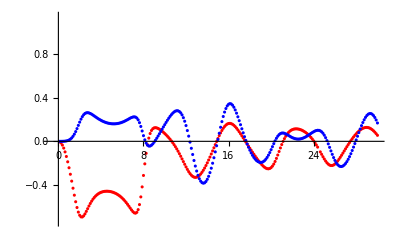

```mathematica
ListPlot[{Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v4kTr1[[All,1]],Re[v4kTr1[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

#### b = 0.1

```mathematica
v2kT={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.1,0};
kT=0.25*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$210629 near {ϕ$210629} = {3.77963}. NIntegrate obtained -6.80615×10^-13 and 4.13938×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$269569 near {ϕ$269569} = {6.12082642907296292644758750611799769103527069091796875}. NIntegrate obtained 8.30516×10^-14 and 2.27662×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$348353 near {ϕ$348353} = {6.001928524374696760634861902872216887772083282470703125}. NIntegrate obtained -1.94428×10^-14 and 1.73353×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
v2kT
```

{{0.25,{0.0021463,-1.28626×10^-14}},{0.5,{0.00868605,6.64234×10^-15}},{0.75,{0.0198684,-3.78716×10^-15}},{1.,{0.0360553,3.33933×10^-14}},{1.25,{0.0577168,3.76078×10^-14}},{1.5,{0.0854292,-4.10588×10^-14}},{1.75,{0.119865,2.91799×10^-12}},{2.,{0.161763,-2.75788×10^-12}},{2.25,{0.211849,3.54951×10^-13}},{2.5,{0.27068,1.12891×10^-12}},{2.75,{0.338333,2.32364×10^-12}},{3.,{0.413874,-2.69565×10^-12}},{3.25,{0.494497,8.83901×10^-12}},{3.5,{0.574373,-9.53273×10^-14}},{3.75,{0.643559,8.35955×10^-17}},{4.,{0.687989,-1.03748×10^-9}},{4.25,{0.692155,1.52666×10^-12}},{4.5,{0.645172,-5.19713×10^-11}},{4.75,{0.547549,-1.03885×10^-10}},{5.,{0.413,-6.77529×10^-12}},{5.25,{0.262688,-8.42856×10^-11}},{5.5,{0.116424,-2.73326×10^-13}},{5.75,{-0.0128447,-1.34284×10^-11}},{6.,{-0.119525,-6.36056×10^-12}},{6.25,{-0.203123,-1.51258×10^-11}},{6.5,{-0.265723,-7.02925×10^-11}},{6.75,{-0.310225,-1.79956×10^-11}},{7.,{-0.33942,-3.55439×10^-11}},{7.25,{-0.355597,-3.9182×10^-11}},{7.5,{-0.360438,-2.09936×10^-12}},{7.75,{-0.355048,8.75221×10^-10}},{8.,{-0.340032,-5.0527×10^-12}},{8.25,{-0.315619,6.5638×10^-10}},{8.5,{-0.28184,3.41057×10^-11}},{8.75,{-0.238846,-1.2783×10^-11}},{9.,{-0.18748,-6.26604×10^-10}},{9.25,{-0.130281,-2.44963×10^-10}},{9.5,{-0.072953,9.70602×10^-11}},{9.75,{-0.0258179,1.63814×10^-10}},{10.,{-0.00347556,2.33753×10^-10}},{10.25,{-0.0200538,-9.56334×10^-11}},{10.5,{-0.0803463,-6.29667×10^-10}},{10.75,{-0.174189,-7.53828×10^-9}},{11.,{-0.281493,1.02428×10^-10}},{11.25,{-0.383404,-7.31797×10^-10}},{11.5,{-0.469051,8.52694×10^-11}},{11.75,{-0.53524,8.13962×10^-11}},{12.,{-0.583182,1.49535×10^-10}},{12.25,{-0.615679,3.86591×10^-10}},{12.5,{-0.635599,-1.0917×10^-8}},{12.75,{-0.645286,-1.50917×10^-9}},{13.,{-0.646432,-8.6774×10^-11}},{13.25,{-0.640115,-3.63653×10^-10}},{13.5,{-0.626895,-1.86649×10^-10}},{13.75,{-0.606902,2.398×10^-10}},{14.,{-0.579912,-5.58597×10^-10}},{14.25,{-0.545446,-1.55497×10^-10}},{14.5,{-0.502905,-1.81869×10^-10}},{14.75,{-0.451833,1.53394×10^-10}},{15.,{-0.392385,1.99254×10^-10}},{15.25,{-0.32611,-9.98784×10^-10}},{15.5,{-0.256984,-2.24173×10^-10}},{15.75,{-0.192287,-3.33128×10^-10}},{16.,{-0.142213,-6.24668×10^-10}},{16.25,{-0.117064,1.2944×10^-9}},{16.5,{-0.122508,-4.00107×10^-10}},{16.75,{-0.156226,-1.61951×10^-9}},{17.,{-0.209105,-2.05875×10^-8}},{17.25,{-0.269872,-4.12376×10^-10}},{17.5,{-0.329292,-3.73732×10^-11}},{17.75,{-0.381727,8.32175×10^-10}},{18.,{-0.42466,-2.04146×10^-9}},{18.25,{-0.457544,-1.4015×10^-9}},{18.5,{-0.480803,-3.02928×10^-8}},{18.75,{-0.495186,2.08409×10^-10}},{19.,{-0.501434,-9.19686×10^-10}},{19.25,{-0.500117,-6.08944×10^-10}},{19.5,{-0.491586,-2.40541×10^-9}},{19.75,{-0.475969,-2.40796×10^-9}},{20.,{-0.453205,-1.98876×10^-9}},{20.25,{-0.4231,-1.72388×10^-8}},{20.5,{-0.385429,-1.80723×10^-9}},{20.75,{-0.340112,-2.67005×10^-9}},{21.,{-0.287477,-2.39857×10^-9}},{21.25,{-0.228654,-2.64255×10^-9}},{21.5,{-0.166058,-6.11159×10^-9}},{21.75,{-0.10382,-1.99483×10^-10}},{22.,{-0.0478536,-1.36342×10^-9}},{22.25,{-0.00511281,1.54892×10^-8}},{22.5,{0.0181226,-6.73691×10^-9}},{22.75,{0.0184297,1.03386×10^-9}},{23.,{-0.00334353,-3.13614×10^-9}},{23.25,{-0.0423993,-1.19756×10^-9}},{23.5,{-0.0918431,1.3867×10^-9}},{23.75,{-0.14481,1.92099×10^-8}},{24.,{-0.195887,-2.0301×10^-9}},{24.25,{-0.241514,-9.83026×10^-10}},{24.5,{-0.279744,3.14355×10^-8}},{24.75,{-0.30975,-1.63262×10^-10}},{25.,{-0.331367,2.54113×10^-8}},{25.25,{-0.344748,2.30925×10^-9}},{25.5,{-0.350146,3.61007×10^-9}},{25.75,{-0.347792,2.86775×10^-9}},{26.,{-0.337842,2.11966×10^-9}},{26.25,{-0.320373,-1.54293×10^-9}},{26.5,{-0.295432,8.85691×10^-9}},{26.75,{-0.263114,4.42113×10^-9}},{27.,{-0.223715,-3.78863×10^-8}},{27.25,{-0.177936,3.90758×10^-9}},{27.5,{-0.127159,3.53197×10^-9}},{27.75,{-0.0737425,2.19927×10^-8}},{28.,{-0.0212211,-5.76377×10^-9}},{28.25,{0.0257622,-1.35453×10^-8}},{28.5,{0.0620071,2.73433×10^-9}},{28.75,{0.0828392,9.53879×10^-9}},{29.,{0.0854259,-3.70989×10^-9}},{29.25,{0.0697351,1.61782×10^-8}},{29.5,{0.0385637,1.04965×10^-8}},{29.75,{-0.00336292,2.01297×10^-8}},{30.,{-0.0507255,8.53026×10^-9}}}

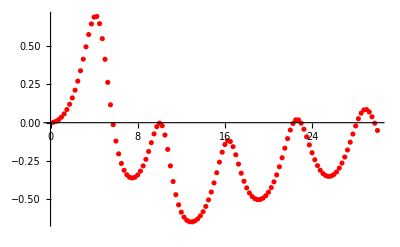

```mathematica
ListPlot[{Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

```mathematica
v2kTb02={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.2,0};
kT=0.25*i;
AppendTo[v2kTb02,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$9627505 near {ϕ$9627505} = {3.87781}. NIntegrate obtained 1.5668×10^-14 and 2.97948×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$9694317 near {ϕ$9694317} = {6.01778009555628290438988869937020353972911834716796875}. NIntegrate obtained 6.97081×10^-14 and 1.03014×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$9798316 near {ϕ$9798316} = {0.576679}. NIntegrate obtained -2.65165×10^-13 and 1.0038×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTb02
```

{{0.25,{0.00120005,5.98027×10^-16}},{0.5,{0.00484064,1.14007×10^-14}},{0.75,{0.0110282,-1.07208×10^-13}},{1.,{0.0199274,2.54618×10^-15}},{1.25,{0.0317627,8.41119×10^-14}},{1.5,{0.0468171,1.74042×10^-13}},{1.75,{0.0654236,2.66122×10^-17}},{2.,{0.0879378,-1.04973×10^-12}},{2.25,{0.114674,2.82114×10^-15}},{2.5,{0.14577,9.41872×10^-13}},{2.75,{0.18093,-2.39×10^-12}},{3.,{0.218953,-9.62305×10^-11}},{3.25,{0.256927,2.29637×10^-9}},{3.5,{0.289082,-1.56849×10^-12}},{3.75,{0.305596,-7.2228×10^-18}},{4.,{0.29269,5.62982×10^-9}},{4.25,{0.236452,1.11352×10^-11}},{4.5,{0.131609,-8.38239×10^-13}},{4.75,{-0.0102193,4.43951×10^-12}},{5.,{-0.163272,7.34491×10^-11}},{5.25,{-0.301583,2.63769×10^-10}},{5.5,{-0.410447,4.24856×10^-11}},{5.75,{-0.487181,7.47374×10^-11}},{6.,{-0.535832,-1.49713×10^-11}},{6.25,{-0.562288,4.92507×10^-10}},{6.5,{-0.571781,1.14725×10^-7}},{6.75,{-0.568139,-8.58199×10^-11}},{7.,{-0.553792,3.80709×10^-12}},{7.25,{-0.530035,-2.58482×10^-11}},{7.5,{-0.497289,-6.71574×10^-11}},{7.75,{-0.455334,-4.22624×10^-11}},{8.,{-0.403555,1.01906×10^-11}},{8.25,{-0.341287,-1.26032×10^-10}},{8.5,{-0.268399,-1.12183×10^-9}},{8.75,{-0.186291,-8.49465×10^-11}},{9.,{-0.0993531,-1.2918×10^-9}},{9.25,{-0.0164173,-1.60126×10^-11}},{9.5,{0.0492215,-7.69317×10^-9}},{9.75,{0.0832938,-2.25993×10^-10}},{10.,{0.0773342,-1.64166×10^-10}},{10.25,{0.0340631,-1.29661×10^-9}},{10.5,{-0.0340215,1.26271×10^-8}},{10.75,{-0.111511,-5.3079×10^-10}},{11.,{-0.186194,1.61529×10^-11}},{11.25,{-0.251075,1.45082×10^-11}},{11.5,{-0.303415,1.17462×10^-10}},{11.75,{-0.342991,-6.53192×10^-11}},{12.,{-0.370704,4.75126×10^-12}},{12.25,{-0.387757,-5.45482×10^-11}},{12.5,{-0.395254,-3.81883×10^-10}},{12.75,{-0.394039,1.21226×10^-10}},{13.,{-0.384654,5.00907×10^-11}},{13.25,{-0.367356,-9.45435×10^-11}},{13.5,{-0.342159,-2.70804×10^-10}},{13.75,{-0.308901,-1.37342×10^-10}},{14.,{-0.267352,8.07747×10^-11}},{14.25,{-0.217385,5.09931×10^-8}},{14.5,{-0.159235,4.56522×10^-10}},{14.75,{-0.0939094,-4.57533×10^-10}},{15.,{-0.0236993,5.79058×10^-10}},{15.25,{0.0472688,4.70379×10^-10}},{15.5,{0.112768,4.97195×10^-10}},{15.75,{0.164949,1.41495×10^-9}},{16.,{0.19596,1.21005×10^-9}},{16.25,{0.200449,1.93136×10^-10}},{16.5,{0.177748,1.52422×10^-10}},{16.75,{0.132275,3.02227×10^-10}},{17.,{0.0718378,-3.01646×10^-10}},{17.25,{0.00497991,2.24984×10^-8}},{17.5,{-0.0611226,-5.09428×10^-10}},{17.75,{-0.121542,2.77911×10^-8}},{18.,{-0.173491,-3.43288×10^-8}},{18.25,{-0.21576,-2.02523×10^-10}},{18.5,{-0.248106,4.42768×10^-9}},{18.75,{-0.270776,5.54283×10^-10}},{19.,{-0.284191,-6.1474×10^-10}},{19.25,{-0.288757,2.17543×10^-9}},{19.5,{-0.284779,1.2813×10^-9}},{19.75,{-0.272427,4.64154×10^-10}},{20.,{-0.251758,1.03915×10^-9}},{20.25,{-0.222782,7.31035×10^-10}},{20.5,{-0.18558,-3.26514×10^-8}},{20.75,{-0.140516,2.91041×10^-9}},{21.,{-0.088542,2.57527×10^-9}},{21.25,{-0.0316099,3.63799×10^-9}},{21.5,{0.0268718,4.61162×10^-9}},{21.75,{0.0817394,3.50222×10^-8}},{22.,{0.126278,-8.67206×10^-10}},{22.25,{0.153301,2.68949×10^-8}},{22.5,{0.157117,9.45149×10^-8}},{22.75,{0.135645,-2.49986×10^-9}},{23.,{0.0914338,4.35577×10^-10}},{23.25,{0.0307896,-7.582×10^-10}},{23.5,{-0.0383763,-5.55097×10^-9}},{23.75,{-0.108758,-8.43307×10^-9}},{24.,{-0.174923,2.82652×10^-8}},{24.25,{-0.23355,1.82978×10^-9}},{24.5,{-0.283036,1.54162×10^-8}},{24.75,{-0.322923,-2.24065×10^-9}},{25.,{-0.353388,-1.15135×10^-8}},{25.25,{-0.374873,5.81177×10^-10}},{25.5,{-0.38786,5.09261×10^-8}},{25.75,{-0.392742,-2.52093×10^-9}},{26.,{-0.389767,4.20277×10^-10}},{26.25,{-0.379024,2.53651×10^-9}},{26.5,{-0.360475,7.28979×10^-9}},{26.75,{-0.334035,1.78793×10^-10}},{27.,{-0.299735,1.21742×10^-8}},{27.25,{-0.257999,4.03857×10^-9}},{27.5,{-0.210099,7.70365×10^-9}},{27.75,{-0.158783,1.3498×10^-8}},{28.,{-0.108942,-1.10664×10^-7}},{28.25,{-0.0678878,1.68516×10^-8}},{28.5,{-0.0444845,1.15379×10^-8}},{28.75,{-0.0465873,7.26623×10^-9}},{29.,{-0.0775133,-1.92088×10^-8}},{29.25,{-0.133916,7.15144×10^-9}},{29.5,{-0.206969,1.18129×10^-8}},{29.75,{-0.286134,2.43145×10^-8}},{30.,{-0.362663,2.09513×10^-8}}}

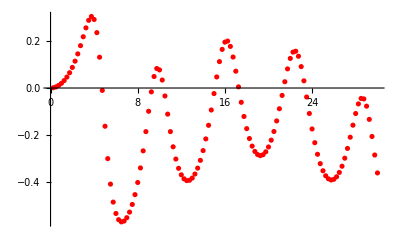

```mathematica
ListPlot[{Transpose[{v2kTb02[[All,1]],Re[v2kTb02[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$17932229 near {ϕ$17932229} = {6.0340560481230842426736415973209659568965435028076171875}. NIntegrate obtained 1.872×10^-12 and 5.85235×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$18000193 near {ϕ$18000193} = {0.576679}. NIntegrate obtained 2.40176×10^-13 and 1.53719×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$18098288 near {ϕ$18098288} = {0.736213}. NIntegrate obtained 7.61457×10^-15 and 6.79915×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.25,{0.000064888,1.22706×10^-13}},{0.5,{0.000221925,6.82512×10^-14}},{0.75,{0.000418715,5.42285×10^-15}},{1.,{0.000630125,1.4875×10^-14}},{1.25,{0.000860762,3.17951×10^-14}},{1.5,{0.00112042,2.30695×10^-15}},{1.75,{0.00136801,-1.13698×10^-9}},{2.,{0.00140516,3.42668×10^-17}},{2.25,{0.000695671,-2.6535×10^-17}},{2.5,{-0.00192499,7.56752×10^-14}},{2.75,{-0.00867524,1.93545×10^-10}},{3.,{-0.0233385,1.46726×10^-17}},{3.25,{-0.0515442,5.28193×10^-11}},{3.5,{-0.0999498,-1.52687×10^-17}},{3.75,{-0.173014,9.1355×10^-11}},{4.,{-0.267552,-1.21003×10^-10}},{4.25,{-0.369846,-6.8016×10^-17}},{4.5,{-0.461315,1.51825×10^-12}},{4.75,{-0.528976,7.18672×10^-12}},{5.,{-0.570032,8.98492×10^-10}},{5.25,{-0.58857,-1.84707×10^-9}},{5.5,{-0.590552,3.93447×10^-11}},{5.75,{-0.581008,-2.0911×10^-11}},{6.,{-0.563315,-3.60457×10^-12}},{6.25,{-0.5394,3.95843×10^-11}},{6.5,{-0.510136,-4.02757×10^-10}},{6.75,{-0.475678,1.69057×10^-12}},{7.,{-0.435695,3.55199×10^-10}},{7.25,{-0.389527,3.09541×10^-10}},{7.5,{-0.33633,5.49457×10^-10}},{7.75,{-0.275236,-1.6556×10^-11}},{8.,{-0.205636,-7.11656×10^-10}},{8.25,{-0.127631,5.70025×10^-10}},{8.5,{-0.042754,4.92401×10^-10}},{8.75,{0.0450866,2.23667×10^-11}},{9.,{0.128753,-6.95647×10^-11}},{9.25,{0.197903,-2.02911×10^-10}},{9.5,{0.240982,1.98533×10^-10}},{9.75,{0.249297,-5.87544×10^-11}},{10.,{0.22126,3.35356×10^-10}},{10.25,{0.163517,2.35805×10^-10}},{10.5,{0.0878975,3.53214×10^-11}},{10.75,{0.0066449,2.43144×10^-9}},{11.,{-0.0709199,-2.5615×10^-11}},{11.25,{-0.139279,-1.91749×10^-10}},{11.5,{-0.196022,-4.65186×10^-10}},{11.75,{-0.240695,2.36542×10^-10}},{12.,{-0.273837,6.2528×10^-8}},{12.25,{-0.296342,-1.17724×10^-10}},{12.5,{-0.30911,8.64263×10^-11}},{12.75,{-0.312871,-1.31633×10^-11}},{13.,{-0.308122,-2.48904×10^-10}},{13.25,{-0.295114,1.7722×10^-10}},{13.5,{-0.27388,-7.55433×10^-11}},{13.75,{-0.24429,7.29495×10^-10}},{14.,{-0.206156,1.91293×10^-11}},{14.25,{-0.159414,2.90695×10^-10}},{14.5,{-0.104437,5.80381×10^-10}},{14.75,{-0.0425127,5.6826×10^-10}},{15.,{0.0234787,5.34826×10^-11}},{15.25,{0.0883278,7.66321×10^-10}},{15.5,{0.144114,-1.05288×10^-9}},{15.75,{0.180919,2.98482×10^-10}},{16.,{0.189306,-5.51832×10^-8}},{16.25,{0.164084,1.41927×10^-7}},{16.5,{0.107172,1.03493×10^-9}},{16.75,{0.027213,7.11946×10^-10}},{17.,{-0.0639858,2.1957×10^-8}},{17.25,{-0.155578,7.8966×10^-8}},{17.5,{-0.240039,6.82981×10^-11}},{17.75,{-0.313415,5.57437×10^-9}},{18.,{-0.374427,1.40934×10^-8}},{18.25,{-0.423372,-6.94022×10^-10}},{18.5,{-0.461264,-1.91279×10^-9}},{18.75,{-0.489297,3.83611×10^-9}},{19.,{-0.508567,-8.90913×10^-10}},{19.25,{-0.519933,-1.04103×10^-9}},{19.5,{-0.523967,1.93937×10^-9}},{19.75,{-0.520939,-1.2411×10^-9}},{20.,{-0.510819,-9.90352×10^-11}},{20.25,{-0.493305,-4.72338×10^-9}},{20.5,{-0.467884,7.30908×10^-8}},{20.75,{-0.434007,-1.15995×10^-9}},{21.,{-0.391484,1.0599×10^-7}},{21.25,{-0.341323,1.43509×10^-8}},{21.5,{-0.287216,-5.07321×10^-10}},{21.75,{-0.237441,-1.49596×10^-8}},{22.,{-0.205534,-9.10504×10^-9}},{22.25,{-0.20634,-7.41989×10^-9}},{22.5,{-0.246471,-8.2244×10^-9}},{22.75,{-0.317474,-1.92597×10^-8}},{23.,{-0.400806,3.5773×10^-9}},{23.25,{-0.479555,4.60787×10^-9}},{23.5,{-0.544636,-1.42279×10^-8}},{23.75,{-0.593775,2.07906×10^-9}},{24.,{-0.62819,4.53995×10^-9}},{24.25,{-0.65014,3.57264×10^-10}},{24.5,{-0.661741,-4.25502×10^-9}},{24.75,{-0.664567,-1.17329×10^-8}},{25.,{-0.659578,-1.44763×10^-8}},{25.25,{-0.647158,-2.79484×10^-8}},{25.5,{-0.627168,-1.51254×10^-8}},{25.75,{-0.598978,-1.56784×10^-8}},{26.,{-0.561489,-1.36374×10^-8}},{26.25,{-0.513177,-1.60226×10^-8}},{26.5,{-0.452207,-6.39793×10^-9}},{26.75,{-0.376747,-1.41371×10^-8}},{27.,{-0.285649,-2.46012×10^-8}},{27.25,{-0.179688,-2.57732×10^-8}},{27.5,{-0.063385,-1.78347×10^-8}},{27.75,{0.0532968,4.85157×10^-9}},{28.,{0.15513,-2.82713×10^-8}},{28.25,{0.225675,-5.57699×10^-8}},{28.5,{0.254357,-3.26471×10^-8}},{28.75,{0.241617,-2.40937×10^-8}},{29.,{0.197684,5.36212×10^-7}},{29.25,{0.136659,-1.5814×10^-8}},{29.5,{0.0709878,-1.05875×10^-8}},{29.75,{0.00910943,-7.31454×10^-8}},{30.,{-0.0443549,6.77252×10^-9}}}

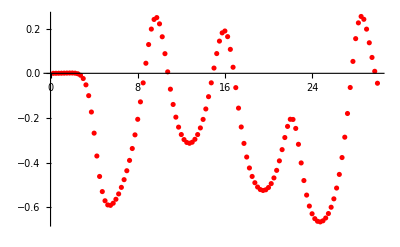

```mathematica
v2kTb03={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.3,0};
kT=0.25*i;
AppendTo[v2kTb03,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTb03
ListPlot[{Transpose[{v2kTb03[[All,1]],Re[v2kTb03[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25156833 near {ϕ$25156833} = {0.51532}. NIntegrate obtained -1.2719×10^-14 and 3.92368×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25266945 near {ϕ$25266945} = {5.6695}. NIntegrate obtained 1.49759×10^-14 and 6.30927×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25374593 near {ϕ$25374593} = {2.09839}. NIntegrate obtained 1.26748×10^-14 and 4.51587×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.25,{-0.00130699,-1.33024×10^-15}},{0.5,{-0.00535888,6.87039×10^-15}},{0.75,{-0.012366,1.47677×10^-14}},{1.,{-0.0225015,-8.67264×10^-15}},{1.25,{-0.0359113,-1.85383×10^-14}},{1.5,{-0.05279,-1.64489×10^-13}},{1.75,{-0.0735184,-5.4744×10^-17}},{2.,{-0.0988551,-6.06364×10^-17}},{2.25,{-0.130156,3.74386×10^-12}},{2.5,{-0.169517,4.49135×10^-13}},{2.75,{-0.219568,-2.85731×10^-11}},{3.,{-0.282402,-2.01836×10^-11}},{3.25,{-0.357153,-8.06401×10^-14}},{3.5,{-0.437167,-1.96764×10^-17}},{3.75,{-0.510219,-4.92962×10^-17}},{4.,{-0.56433,2.1162×10^-12}},{4.25,{-0.594519,-9.76461×10^-12}},{4.5,{-0.603532,-5.8083×10^-11}},{4.75,{-0.59756,-1.1045×10^-10}},{5.,{-0.582333,-1.11624×10^-11}},{5.25,{-0.561689,2.41134×10^-10}},{5.5,{-0.537703,-5.65621×10^-10}},{5.75,{-0.511236,2.30833×10^-12}},{6.,{-0.482414,-1.30725×10^-12}},{6.25,{-0.450928,3.47562×10^-10}},{6.5,{-0.416204,3.3832×10^-11}},{6.75,{-0.377499,-1.99195×10^-11}},{7.,{-0.333947,1.58752×10^-11}},{7.25,{-0.284622,-2.24187×10^-11}},{7.5,{-0.228619,-5.11865×10^-12}},{7.75,{-0.165228,-3.08023×10^-10}},{8.,{-0.0942362,3.40173×10^-9}},{8.25,{-0.0164482,2.61545×10^-11}},{8.5,{0.0655665,-4.11675×10^-10}},{8.75,{0.146602,-8.29437×10^-11}},{9.,{0.218278,-4.18482×10^-10}},{9.25,{0.269709,-9.94984×10^-10}},{9.5,{0.290215,1.02391×10^-9}},{9.75,{0.273621,6.86961×10^-11}},{10.,{0.221647,-1.21991×10^-9}},{10.25,{0.14359,-3.01794×10^-10}},{10.5,{0.0523354,3.258×10^-9}},{10.75,{-0.0402562,6.18764×10^-10}},{11.,{-0.125961,2.57803×10^-10}},{11.25,{-0.200442,-4.27808×10^-10}},{11.5,{-0.262256,-2.01478×10^-10}},{11.75,{-0.311649,6.44419×10^-11}},{12.,{-0.349644,3.42507×10^-10}},{12.25,{-0.377464,-3.45169×10^-9}},{12.5,{-0.396247,-2.89334×10^-10}},{12.75,{-0.406893,-2.99349×10^-10}},{13.,{-0.410022,3.42808×10^-8}},{13.25,{-0.405963,-1.68381×10^-8}},{13.5,{-0.394759,-1.53032×10^-10}},{13.75,{-0.3762,-1.51424×10^-8}},{14.,{-0.349884,2.20025×10^-9}},{14.25,{-0.315379,4.33599×10^-9}},{14.5,{-0.272571,1.9667×10^-9}},{14.75,{-0.222415,-1.26001×10^-9}},{15.,{-0.168311,1.46658×10^-9}},{15.25,{-0.11814,4.34006×10^-9}},{15.5,{-0.0857999,1.31484×10^-8}},{15.75,{-0.0888273,2.49633×10^-7}},{16.,{-0.138711,1.56901×10^-8}},{16.25,{-0.229477,2.72615×10^-9}},{16.5,{-0.338902,4.77749×10^-9}},{16.75,{-0.443248,1.69097×10^-9}},{17.,{-0.528785,3.7797×10^-9}},{17.25,{-0.592139,-1.23373×10^-9}},{17.5,{-0.63547,1.29737×10^-9}},{17.75,{-0.662508,5.55521×10^-9}},{18.,{-0.676653,8.52376×10^-9}},{18.25,{-0.68039,1.31079×10^-9}},{18.5,{-0.675251,8.16616×10^-9}},{18.75,{-0.661927,7.8557×10^-11}},{19.,{-0.640389,-8.90435×10^-10}},{19.25,{-0.609958,1.27021×10^-9}},{19.5,{-0.569362,-1.91863×10^-9}},{19.75,{-0.516797,1.70182×10^-9}},{20.,{-0.450098,-1.17931×10^-8}},{20.25,{-0.367165,-1.08815×10^-8}},{20.5,{-0.266858,-6.27937×10^-9}},{20.75,{-0.150574,1.07402×10^-8}},{21.,{-0.0243355,-2.14317×10^-8}},{21.25,{0.0997281,-7.46543×10^-9}},{21.5,{0.204714,-7.05635×10^-9}},{21.75,{0.27453,-1.64489×10^-8}},{22.,{0.301178,-1.14799×10^-8}},{22.25,{0.288045,1.90076×10^-8}},{22.5,{0.246682,2.3775×10^-8}},{22.75,{0.190609,3.29814×10^-8}},{23.,{0.130881,1.09426×10^-8}},{23.25,{0.0746974,4.93412×10^-10}},{23.5,{0.0259368,-4.66459×10^-9}},{23.75,{-0.0137017,1.33894×10^-8}},{24.,{-0.0438029,-6.50603×10^-9}},{24.25,{-0.0645141,-5.02594×10^-9}},{24.5,{-0.0762132,7.31956×10^-9}},{24.75,{-0.079306,-3.43821×10^-9}},{25.,{-0.0741486,3.07516×10^-9}},{25.25,{-0.061049,4.15686×10^-8}},{25.5,{-0.0403131,2.16245×10^-8}},{25.75,{-0.0123491,-1.37618×10^-8}},{26.,{0.0221801,4.96273×10^-8}},{26.25,{0.0621695,1.88183×10^-7}},{26.5,{0.105823,2.49166×10^-8}},{26.75,{0.150472,1.73421×10^-8}},{27.,{0.192478,7.6626×10^-9}},{27.25,{0.227415,-1.16649×10^-8}},{27.5,{0.250659,8.07499×10^-9}},{27.75,{0.258303,5.07105×10^-8}},{28.,{0.248183,-5.36803×10^-8}},{28.25,{0.220529,7.15355×10^-9}},{28.5,{0.17792,9.41836×10^-8}},{28.75,{0.124538,5.67941×10^-8}},{29.,{0.065115,5.9015×10^-9}},{29.25,{0.00399367,-2.24349×10^-8}},{29.5,{-0.0554035,8.29539×10^-9}},{29.75,{-0.11071,3.68466×10^-8}},{30.,{-0.160511,-4.68161×10^-9}}}

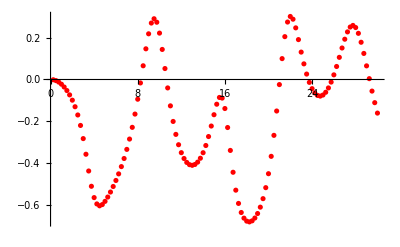

```mathematica
v2kTb04={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.4,0};
kT=0.25*i;
AppendTo[v2kTb04,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTb04
ListPlot[{Transpose[{v2kTb04[[All,1]],Re[v2kTb04[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32996074 near {ϕ$32996074} = {2.57699}. NIntegrate obtained -2.0231×10^-13 and 2.53474×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33072193 near {ϕ$33072193} = {0.638038}. NIntegrate obtained 5.67775×10^-15 and 1.25353×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33152740 near {ϕ$33152740} = {4.23369}. NIntegrate obtained 4.42571×10^-15 and 5.51897×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.25,{-0.00293846,-3.22797×10^-14}},{0.5,{-0.0119878,4.02166×10^-15}},{0.75,{-0.0274896,8.06758×10^-15}},{1.,{-0.0496732,3.74573×10^-14}},{1.25,{-0.0786963,4.28705×10^-14}},{1.5,{-0.114789,-6.03559×10^-13}},{1.75,{-0.158429,-6.17377×10^-17}},{2.,{-0.210431,2.61652×10^-12}},{2.25,{-0.271718,-1.06397×10^-12}},{2.5,{-0.342421,-5.93237×10^-11}},{2.75,{-0.420021,3.53641×10^-11}},{3.,{-0.497264,7.23566×10^-12}},{3.25,{-0.562566,-7.13039×10^-9}},{3.5,{-0.605292,1.42908×10^-9}},{3.75,{-0.62223,-3.90179×10^-9}},{4.,{-0.618239,-5.81003×10^-10}},{4.25,{-0.601331,1.24109×10^-9}},{4.5,{-0.578195,2.59104×10^-9}},{4.75,{-0.552817,-3.57247×10^-11}},{5.,{-0.526988,1.47112×10^-9}},{5.25,{-0.501173,3.04482×10^-9}},{5.5,{-0.47516,1.02292×10^-10}},{5.75,{-0.448418,-7.07705×10^-11}},{6.,{-0.420273,1.03417×10^-8}},{6.25,{-0.389976,1.79615×10^-8}},{6.5,{-0.356724,-3.05977×10^-9}},{6.75,{-0.319663,-4.44271×10^-11}},{7.,{-0.277894,-2.47251×10^-11}},{7.25,{-0.230502,2.16695×10^-10}},{7.5,{-0.176646,-2.85718×10^-10}},{7.75,{-0.115746,2.7498×10^-12}},{8.,{-0.0478498,-1.51385×10^-10}},{8.25,{0.0257362,5.98577×10^-10}},{8.5,{0.101504,-3.03453×10^-10}},{8.75,{0.172664,1.71001×10^-10}},{9.,{0.228584,-4.39478×10^-8}},{9.25,{0.256093,-1.35779×10^-10}},{9.5,{0.243768,1.80117×10^-10}},{9.75,{0.187961,2.44382×10^-10}},{10.,{0.0961155,-3.32592×10^-9}},{10.25,{-0.0161986,9.39926×10^-10}},{10.5,{-0.132316,-8.89064×10^-10}},{10.75,{-0.240029,1.53059×10^-9}},{11.,{-0.333077,-8.73848×10^-11}},{11.25,{-0.409818,2.59413×10^-8}},{11.5,{-0.471218,-5.93729×10^-11}},{11.75,{-0.519297,-1.65977×10^-7}},{12.,{-0.55623,3.19914×10^-14}},{12.25,{-0.58392,-9.15752×10^-10}},{12.5,{-0.603832,-1.34332×10^-10}},{12.75,{-0.616939,-5.77897×10^-9}},{13.,{-0.623691,8.20746×10^-9}},{13.25,{-0.623961,-9.89742×10^-9}},{13.5,{-0.616931,-9.21197×10^-9}},{13.75,{-0.600898,-5.27947×10^-10}},{14.,{-0.57304,-8.64402×10^-9}},{14.25,{-0.529286,-1.75417×10^-9}},{14.5,{-0.464894,1.09976×10^-9}},{14.75,{-0.376998,-3.81623×10^-9}},{15.,{-0.270524,5.50331×10^-9}},{15.25,{-0.164605,-3.38064×10^-9}},{15.5,{-0.087889,-3.76231×10^-9}},{15.75,{-0.058007,-3.55694×10^-9}},{16.,{-0.068785,2.06293×10^-9}},{16.25,{-0.101157,1.31209×10^-9}},{16.5,{-0.13856,2.46724×10^-8}},{16.75,{-0.171809,-1.55624×10^-7}},{17.,{-0.197223,1.84117×10^-8}},{17.25,{-0.213924,-1.32234×10^-8}},{17.5,{-0.222123,-6.69793×10^-9}},{17.75,{-0.2223,9.57063×10^-9}},{18.,{-0.21489,-6.14174×10^-8}},{18.25,{-0.200167,7.39934×10^-9}},{18.5,{-0.178263,-2.05153×10^-9}},{18.75,{-0.149237,4.9509×10^-9}},{19.,{-0.113092,-1.16386×10^-8}},{19.25,{-0.070118,-3.76135×10^-9}},{19.5,{-0.0208926,-9.86587×10^-9}},{19.75,{0.0333654,-2.04069×10^-9}},{20.,{0.0905492,-4.21111×10^-9}},{20.25,{0.147491,-1.285×10^-8}},{20.5,{0.199981,-2.5641×10^-8}},{20.75,{0.243209,-8.28052×10^-9}},{21.,{0.272559,-2.52265×10^-8}},{21.25,{0.284694,-2.42728×10^-8}},{21.5,{0.278405,1.94579×10^-8}},{21.75,{0.254908,-4.16011×10^-8}},{22.,{0.217366,-1.3882×10^-8}},{22.25,{0.169974,-9.59871×10^-9}},{22.5,{0.116993,-3.66937×10^-8}},{22.75,{0.062076,2.75005×10^-8}},{23.,{0.00794649,-3.01615×10^-8}},{23.25,{-0.0435514,1.25449×10^-8}},{23.5,{-0.0913512,-1.59653×10^-8}},{23.75,{-0.134919,4.47874×10^-9}},{24.,{-0.174075,-2.16859×10^-8}},{24.25,{-0.208816,5.94535×10^-8}},{24.5,{-0.239213,-8.45132×10^-8}},{24.75,{-0.26531,3.69644×10^-8}},{25.,{-0.287072,-1.98294×10^-8}},{25.25,{-0.304354,-8.21445×10^-7}},{25.5,{-0.316903,3.54906×10^-9}},{25.75,{-0.324407,-4.23101×10^-9}},{26.,{-0.326601,-2.85156×10^-8}},{26.25,{-0.323405,6.47479×10^-9}},{26.5,{-0.315083,-3.31133×10^-7}},{26.75,{-0.302306,-1.48647×10^-8}},{27.,{-0.286127,-1.17954×10^-8}},{27.25,{-0.267735,3.28228×10^-8}},{27.5,{-0.248234,2.31983×10^-8}},{27.75,{-0.228432,-6.87637×10^-7}},{28.,{-0.208734,-4.3891×10^-8}},{28.25,{-0.189261,-4.57546×10^-8}},{28.5,{-0.169846,-4.8988×10^-7}},{28.75,{-0.150243,1.1607×10^-7}},{29.,{-0.130176,6.18468×10^-8}},{29.25,{-0.109409,-1.70999×10^-8}},{29.5,{-0.0878411,1.65943×10^-8}},{29.75,{-0.0654788,-2.8936×10^-7}},{30.,{-0.04255,3.99352×10^-8}}}

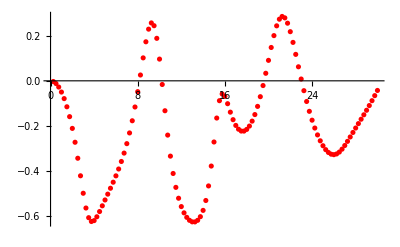

```mathematica
v2kTb05={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={0.5,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTb05
ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

```mathematica
Getv2kT[b_]:=Module[{v2kTb05},
v2kTb05={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05

]
```

```mathematica
Getv2kT[10.0]
```

-Graphics-

{{0.25,showdσ[{10.,0},{0,1/2},{0,1/2},0.25,False]},{0.5,showdσ[{10.,0},{0,1/2},{0,1/2},0.5,False]},{0.75,showdσ[{10.,0},{0,1/2},{0,1/2},0.75,False]},{1.,showdσ[{10.,0},{0,1/2},{0,1/2},1.,False]},{1.25,showdσ[{10.,0},{0,1/2},{0,1/2},1.25,False]},{1.5,showdσ[{10.,0},{0,1/2},{0,1/2},1.5,False]},{1.75,showdσ[{10.,0},{0,1/2},{0,1/2},1.75,False]},{2.,showdσ[{10.,0},{0,1/2},{0,1/2},2.,False]},{2.25,showdσ[{10.,0},{0,1/2},{0,1/2},2.25,False]},{2.5,showdσ[{10.,0},{0,1/2},{0,1/2},2.5,False]},{2.75,showdσ[{10.,0},{0,1/2},{0,1/2},2.75,False]},{3.,showdσ[{10.,0},{0,1/2},{0,1/2},3.,False]},{3.25,showdσ[{10.,0},{0,1/2},{0,1/2},3.25,False]},{3.5,showdσ[{10.,0},{0,1/2},{0,1/2},3.5,False]},{3.75,showdσ[{10.,0},{0,1/2},{0,1/2},3.75,False]},{4.,showdσ[{10.,0},{0,1/2},{0,1/2},4.,False]},{4.25,showdσ[{10.,0},{0,1/2},{0,1/2},4.25,False]},{4.5,showdσ[{10.,0},{0,1/2},{0,1/2},4.5,False]},{4.75,showdσ[{10.,0},{0,1/2},{0,1/2},4.75,False]},{5.,showdσ[{10.,0},{0,1/2},{0,1/2},5.,False]},{5.25,showdσ[{10.,0},{0,1/2},{0,1/2},5.25,False]},{5.5,showdσ[{10.,0},{0,1/2},{0,1/2},5.5,False]},{5.75,showdσ[{10.,0},{0,1/2},{0,1/2},5.75,False]},{6.,showdσ[{10.,0},{0,1/2},{0,1/2},6.,False]},{6.25,showdσ[{10.,0},{0,1/2},{0,1/2},6.25,False]},{6.5,showdσ[{10.,0},{0,1/2},{0,1/2},6.5,False]},{6.75,showdσ[{10.,0},{0,1/2},{0,1/2},6.75,False]},{7.,showdσ[{10.,0},{0,1/2},{0,1/2},7.,False]},{7.25,showdσ[{10.,0},{0,1/2},{0,1/2},7.25,False]},{7.5,showdσ[{10.,0},{0,1/2},{0,1/2},7.5,False]},{7.75,showdσ[{10.,0},{0,1/2},{0,1/2},7.75,False]},{8.,showdσ[{10.,0},{0,1/2},{0,1/2},8.,False]},{8.25,showdσ[{10.,0},{0,1/2},{0,1/2},8.25,False]},{8.5,showdσ[{10.,0},{0,1/2},{0,1/2},8.5,False]},{8.75,showdσ[{10.,0},{0,1/2},{0,1/2},8.75,False]},{9.,showdσ[{10.,0},{0,1/2},{0,1/2},9.,False]},{9.25,showdσ[{10.,0},{0,1/2},{0,1/2},9.25,False]},{9.5,showdσ[{10.,0},{0,1/2},{0,1/2},9.5,False]},{9.75,showdσ[{10.,0},{0,1/2},{0,1/2},9.75,False]},{10.,showdσ[{10.,0},{0,1/2},{0,1/2},10.,False]},{10.25,showdσ[{10.,0},{0,1/2},{0,1/2},10.25,False]},{10.5,showdσ[{10.,0},{0,1/2},{0,1/2},10.5,False]},{10.75,showdσ[{10.,0},{0,1/2},{0,1/2},10.75,False]},{11.,showdσ[{10.,0},{0,1/2},{0,1/2},11.,False]},{11.25,showdσ[{10.,0},{0,1/2},{0,1/2},11.25,False]},{11.5,showdσ[{10.,0},{0,1/2},{0,1/2},11.5,False]},{11.75,showdσ[{10.,0},{0,1/2},{0,1/2},11.75,False]},{12.,showdσ[{10.,0},{0,1/2},{0,1/2},12.,False]},{12.25,showdσ[{10.,0},{0,1/2},{0,1/2},12.25,False]},{12.5,showdσ[{10.,0},{0,1/2},{0,1/2},12.5,False]},{12.75,showdσ[{10.,0},{0,1/2},{0,1/2},12.75,False]},{13.,showdσ[{10.,0},{0,1/2},{0,1/2},13.,False]},{13.25,showdσ[{10.,0},{0,1/2},{0,1/2},13.25,False]},{13.5,showdσ[{10.,0},{0,1/2},{0,1/2},13.5,False]},{13.75,showdσ[{10.,0},{0,1/2},{0,1/2},13.75,False]},{14.,showdσ[{10.,0},{0,1/2},{0,1/2},14.,False]},{14.25,showdσ[{10.,0},{0,1/2},{0,1/2},14.25,False]},{14.5,showdσ[{10.,0},{0,1/2},{0,1/2},14.5,False]},{14.75,showdσ[{10.,0},{0,1/2},{0,1/2},14.75,False]},{15.,showdσ[{10.,0},{0,1/2},{0,1/2},15.,False]},{15.25,showdσ[{10.,0},{0,1/2},{0,1/2},15.25,False]},{15.5,showdσ[{10.,0},{0,1/2},{0,1/2},15.5,False]},{15.75,showdσ[{10.,0},{0,1/2},{0,1/2},15.75,False]},{16.,showdσ[{10.,0},{0,1/2},{0,1/2},16.,False]},{16.25,showdσ[{10.,0},{0,1/2},{0,1/2},16.25,False]},{16.5,showdσ[{10.,0},{0,1/2},{0,1/2},16.5,False]},{16.75,showdσ[{10.,0},{0,1/2},{0,1/2},16.75,False]},{17.,showdσ[{10.,0},{0,1/2},{0,1/2},17.,False]},{17.25,showdσ[{10.,0},{0,1/2},{0,1/2},17.25,False]},{17.5,showdσ[{10.,0},{0,1/2},{0,1/2},17.5,False]},{17.75,showdσ[{10.,0},{0,1/2},{0,1/2},17.75,False]},{18.,showdσ[{10.,0},{0,1/2},{0,1/2},18.,False]},{18.25,showdσ[{10.,0},{0,1/2},{0,1/2},18.25,False]},{18.5,showdσ[{10.,0},{0,1/2},{0,1/2},18.5,False]},{18.75,showdσ[{10.,0},{0,1/2},{0,1/2},18.75,False]},{19.,showdσ[{10.,0},{0,1/2},{0,1/2},19.,False]},{19.25,showdσ[{10.,0},{0,1/2},{0,1/2},19.25,False]},{19.5,showdσ[{10.,0},{0,1/2},{0,1/2},19.5,False]},{19.75,showdσ[{10.,0},{0,1/2},{0,1/2},19.75,False]},{20.,showdσ[{10.,0},{0,1/2},{0,1/2},20.,False]},{20.25,showdσ[{10.,0},{0,1/2},{0,1/2},20.25,False]},{20.5,showdσ[{10.,0},{0,1/2},{0,1/2},20.5,False]},{20.75,showdσ[{10.,0},{0,1/2},{0,1/2},20.75,False]},{21.,showdσ[{10.,0},{0,1/2},{0,1/2},21.,False]},{21.25,showdσ[{10.,0},{0,1/2},{0,1/2},21.25,False]},{21.5,showdσ[{10.,0},{0,1/2},{0,1/2},21.5,False]},{21.75,showdσ[{10.,0},{0,1/2},{0,1/2},21.75,False]},{22.,showdσ[{10.,0},{0,1/2},{0,1/2},22.,False]},{22.25,showdσ[{10.,0},{0,1/2},{0,1/2},22.25,False]},{22.5,showdσ[{10.,0},{0,1/2},{0,1/2},22.5,False]},{22.75,showdσ[{10.,0},{0,1/2},{0,1/2},22.75,False]},{23.,showdσ[{10.,0},{0,1/2},{0,1/2},23.,False]},{23.25,showdσ[{10.,0},{0,1/2},{0,1/2},23.25,False]},{23.5,showdσ[{10.,0},{0,1/2},{0,1/2},23.5,False]},{23.75,showdσ[{10.,0},{0,1/2},{0,1/2},23.75,False]},{24.,showdσ[{10.,0},{0,1/2},{0,1/2},24.,False]},{24.25,showdσ[{10.,0},{0,1/2},{0,1/2},24.25,False]},{24.5,showdσ[{10.,0},{0,1/2},{0,1/2},24.5,False]},{24.75,showdσ[{10.,0},{0,1/2},{0,1/2},24.75,False]},{25.,showdσ[{10.,0},{0,1/2},{0,1/2},25.,False]},{25.25,showdσ[{10.,0},{0,1/2},{0,1/2},25.25,False]},{25.5,showdσ[{10.,0},{0,1/2},{0,1/2},25.5,False]},{25.75,showdσ[{10.,0},{0,1/2},{0,1/2},25.75,False]},{26.,showdσ[{10.,0},{0,1/2},{0,1/2},26.,False]},{26.25,showdσ[{10.,0},{0,1/2},{0,1/2},26.25,False]},{26.5,showdσ[{10.,0},{0,1/2},{0,1/2},26.5,False]},{26.75,showdσ[{10.,0},{0,1/2},{0,1/2},26.75,False]},{27.,showdσ[{10.,0},{0,1/2},{0,1/2},27.,False]},{27.25,showdσ[{10.,0},{0,1/2},{0,1/2},27.25,False]},{27.5,showdσ[{10.,0},{0,1/2},{0,1/2},27.5,False]},{27.75,showdσ[{10.,0},{0,1/2},{0,1/2},27.75,False]},{28.,showdσ[{10.,0},{0,1/2},{0,1/2},28.,False]},{28.25,showdσ[{10.,0},{0,1/2},{0,1/2},28.25,False]},{28.5,showdσ[{10.,0},{0,1/2},{0,1/2},28.5,False]},{28.75,showdσ[{10.,0},{0,1/2},{0,1/2},28.75,False]},{29.,showdσ[{10.,0},{0,1/2},{0,1/2},29.,False]},{29.25,showdσ[{10.,0},{0,1/2},{0,1/2},29.25,False]},{29.5,showdσ[{10.,0},{0,1/2},{0,1/2},29.5,False]},{29.75,showdσ[{10.,0},{0,1/2},{0,1/2},29.75,False]},{30.,showdσ[{10.,0},{0,1/2},{0,1/2},30.,False]}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119427788 near {ϕ$119427788} = {2.57699}. NIntegrate obtained -6.76958×10^-14 and 2.49466×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119499110 near {ϕ$119499110} = {5.53451}. NIntegrate obtained 1.68572×10^-14 and 6.28383×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119606758 near {ϕ$119606758} = {0.215381}. NIntegrate obtained -9.05265×10^-15 and 8.48222×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

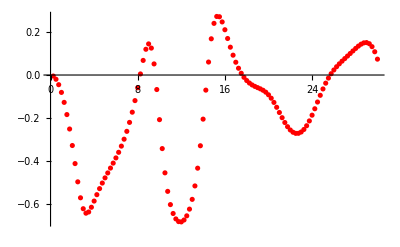

{{0.25,{-0.00484338,-1.59547×10^-14}},{0.5,{-0.0197155,1.78561×10^-14}},{0.75,{-0.0450247,-2.50067×10^-14}},{1.,{-0.0808985,-2.61122×10^-13}},{1.25,{-0.127269,-1.67868×10^-13}},{1.5,{-0.184048,-3.83796×10^-14}},{1.75,{-0.251139,2.49516×10^-13}},{2.,{-0.32795,-5.25417×10^-11}},{2.25,{-0.412015,1.87108×10^-13}},{2.5,{-0.496891,9.50542×10^-12}},{2.75,{-0.571168,-1.19963×10^-16}},{3.,{-0.621983,5.94845×10^-14}},{3.25,{-0.642704,-6.02892×10^-17}},{3.5,{-0.637093,-1.5205×10^-9}},{3.75,{-0.615148,3.50746×10^-12}},{4.,{-0.586367,-4.41924×10^-12}},{4.25,{-0.556628,9.87632×10^-11}},{4.5,{-0.5285,3.57239×10^-11}},{4.75,{-0.502562,-4.60994×10^-10}},{5.,{-0.478462,1.91149×10^-10}},{5.25,{-0.455498,-1.77169×10^-8}},{5.5,{-0.432885,-5.02318×10^-10}},{5.75,{-0.409849,-8.0978×10^-9}},{6.,{-0.385642,-3.686×10^-11}},{6.25,{-0.359528,-7.00863×10^-10}},{6.5,{-0.330754,-8.17521×10^-10}},{6.75,{-0.298535,-6.37396×10^-11}},{7.,{-0.26204,3.29905×10^-11}},{7.25,{-0.220421,-1.10889×10^-10}},{7.5,{-0.172903,1.91899×10^-11}},{7.75,{-0.119012,-9.56258×10^-16}},{8.,{-0.0590556,-1.15774×10^-11}},{8.25,{0.00498262,7.64686×10^-10}},{8.5,{0.0679542,1.2679×10^-9}},{8.75,{0.119771,5.67354×10^-10}},{9.,{0.144749,-1.38676×10^-9}},{9.25,{0.125258,-1.55716×10^-9}},{9.5,{0.0516656,-4.87833×10^-11}},{9.75,{-0.0675366,1.75322×10^-10}},{10.,{-0.207667,2.05722×10^-10}},{10.25,{-0.342279,-1.6793×10^-8}},{10.5,{-0.455074,-6.26408×10^-10}},{10.75,{-0.541252,-4.2933×10^-10}},{11.,{-0.602841,-3.5862×10^-10}},{11.25,{-0.64418,-7.62218×10^-9}},{11.5,{-0.669471,-4.31828×10^-9}},{11.75,{-0.681865,-1.98727×10^-10}},{12.,{-0.683283,-2.93778×10^-9}},{12.25,{-0.674477,-1.15825×10^-10}},{12.5,{-0.655121,2.46717×10^-9}},{12.75,{-0.623877,-8.98617×10^-9}},{13.,{-0.578476,-1.55098×10^-10}},{13.25,{-0.51597,-2.33114×10^-8}},{13.5,{-0.433372,-7.30469×10^-9}},{13.75,{-0.329085,-1.12609×10^-8}},{14.,{-0.205241,2.7816×10^-9}},{14.25,{-0.0702961,-6.73956×10^-9}},{14.5,{0.0603909,-2.01832×10^-9}},{14.75,{0.168491,4.12894×10^-9}},{15.,{0.240304,-4.38076×10^-11}},{15.25,{0.272414,-1.77033×10^-8}},{15.5,{0.271054,-6.16023×10^-9}},{15.75,{0.246983,-3.27954×10^-12}},{16.,{0.210651,2.47636×10^-8}},{16.25,{0.169844,-6.01853×10^-9}},{16.5,{0.129488,3.8211×10^-9}},{16.75,{0.0922866,8.40903×10^-9}},{17.,{0.0594833,-1.07231×10^-8}},{17.25,{0.0314753,2.62553×10^-9}},{17.5,{0.00818277,1.53609×10^-8}},{17.75,{-0.0107178,7.41927×10^-8}},{18.,{-0.0256854,5.23291×10^-9}},{18.25,{-0.0372683,-8.54622×10^-10}},{18.5,{-0.0461032,-2.60969×10^-9}},{18.75,{-0.0529348,-1.31701×10^-9}},{19.,{-0.0586465,-1.03744×10^-8}},{19.25,{-0.0642673,-4.17508×10^-9}},{19.5,{-0.0709415,-7.37236×10^-9}},{19.75,{-0.0798418,-2.37064×10^-8}},{20.,{-0.091958,3.90667×10^-8}},{20.25,{-0.107872,7.1011×10^-9}},{20.5,{-0.127525,7.6886×10^-9}},{20.75,{-0.150142,1.96608×10^-8}},{21.,{-0.174366,1.36501×10^-10}},{21.25,{-0.19853,-4.61998×10^-9}},{21.5,{-0.220997,-1.74227×10^-8}},{21.75,{-0.240389,5.02048×10^-7}},{22.,{-0.255674,1.49912×10^-8}},{22.25,{-0.266158,-1.32009×10^-8}},{22.5,{-0.271389,8.62786×10^-9}},{22.75,{-0.271082,1.5774×10^-8}},{23.,{-0.265074,1.97485×10^-8}},{23.25,{-0.253329,5.46291×10^-7}},{23.5,{-0.236008,-1.52972×10^-8}},{23.75,{-0.21356,-2.45942×10^-8}},{24.,{-0.186811,5.99339×10^-8}},{24.25,{-0.15699,-1.85818×10^-8}},{24.5,{-0.125631,-1.80558×10^-7}},{24.75,{-0.0944029,-3.69333×10^-10}},{25.,{-0.0647847,-1.70073×10^-8}},{25.25,{-0.0378792,-1.91745×10^-7}},{25.5,{-0.014236,8.07136×10^-9}},{25.75,{0.00611163,-1.01358×10^-8}},{26.,{0.0235291,2.10888×10^-6}},{26.25,{0.0386187,-7.05641×10^-9}},{26.5,{0.0520635,-7.53969×10^-10}},{26.75,{0.0644819,-1.11628×10^-7}},{27.,{0.0764176,-1.49246×10^-8}},{27.25,{0.0882346,1.50801×10^-7}},{27.5,{0.100116,-1.14362×10^-8}},{27.75,{0.112019,5.48299×10^-8}},{28.,{0.123664,-2.52295×10^-8}},{28.25,{0.134473,-2.23503×10^-7}},{28.5,{0.143535,-9.24958×10^-9}},{28.75,{0.149558,6.22211×10^-6}},{29.,{0.150912,-1.77781×10^-7}},{29.25,{0.145682,3.1794×10^-7}},{29.5,{0.13195,4.79245×10^-8}},{29.75,{0.108201,1.664×10^-8}},{30.,{0.0738465,-2.45669×10^-7}}}

```mathematica
Getv2kT[0.6]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$127689162 near {ϕ$127689162} = {1.04301}. NIntegrate obtained 1.98183×10^-14 and 5.06602×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$127779672 near {ϕ$127779672} = {4.45458}. NIntegrate obtained 2.59974×10^-14 and 2.56419×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$127888878 near {ϕ$127888878} = {5.22771}. NIntegrate obtained 1.00625×10^-13 and 3.28241×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

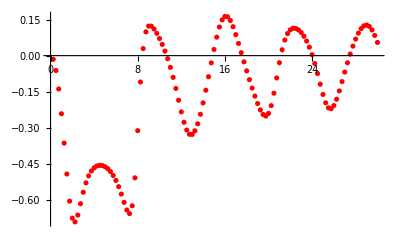

{{0.25,{-0.0153703,1.77692×10^-14}},{0.5,{-0.0620339,1.10448×10^-13}},{0.75,{-0.138959,1.17468×10^-12}},{1.,{-0.242273,-3.70558×10^-13}},{1.25,{-0.364797,2.033×10^-10}},{1.5,{-0.493546,-1.37362×10^-13}},{1.75,{-0.606603,3.51993×10^-12}},{2.,{-0.677615,-7.85472×10^-17}},{2.25,{-0.69319,2.55159×10^-9}},{2.5,{-0.664932,-1.65424×10^-11}},{2.75,{-0.617398,3.18941×10^-10}},{3.,{-0.569738,-1.90247×10^-11}},{3.25,{-0.530485,-1.81875×10^-8}},{3.5,{-0.501266,2.36214×10^-12}},{3.75,{-0.480934,7.72866×10^-11}},{4.,{-0.467766,2.40431×10^-12}},{4.25,{-0.460269,2.28429×10^-9}},{4.5,{-0.457377,-2.646×10^-10}},{4.75,{-0.45843,-7.48485×10^-9}},{5.,{-0.463108,-1.37125×10^-9}},{5.25,{-0.47137,3.44803×10^-9}},{5.5,{-0.483405,-1.30649×10^-16}},{5.75,{-0.499585,1.42334×10^-11}},{6.,{-0.520401,2.74762×10^-10}},{6.25,{-0.546295,2.53357×10^-15}},{6.5,{-0.577233,-1.93072×10^-15}},{6.75,{-0.611625,-1.14548×10^-11}},{7.,{-0.643758,-2.46894×10^-11}},{7.25,{-0.658651,-2.26715×10^-10}},{7.5,{-0.626095,-2.9069×10^-10}},{7.75,{-0.509444,-2.82749×10^-9}},{8.,{-0.3127,-1.49843×10^-10}},{8.25,{-0.110023,1.76213×10^-8}},{8.5,{0.0293966,7.26664×10^-9}},{8.75,{0.0991128,5.15503×10^-8}},{9.,{0.123171,-6.38262×10^-9}},{9.25,{0.123018,-9.50091×10^-10}},{9.5,{0.110967,2.62038×10^-10}},{9.75,{0.0929324,-1.34412×10^-9}},{10.,{0.071309,8.47169×10^-9}},{10.25,{0.0467296,4.33892×10^-8}},{10.5,{0.0189296,4.93291×10^-8}},{10.75,{-0.0127806,3.43465×10^-9}},{11.,{-0.0491431,-8.79825×10^-10}},{11.25,{-0.0905767,6.46263×10^-9}},{11.5,{-0.136709,-1.10339×10^-8}},{11.75,{-0.185819,1.56697×10^-8}},{12.,{-0.234489,9.49791×10^-10}},{12.25,{-0.277797,-1.80933×10^-8}},{12.5,{-0.310366,3.04244×10^-8}},{12.75,{-0.32795,1.95269×10^-8}},{13.,{-0.328691,7.78354×10^-10}},{13.25,{-0.313306,-3.29113×10^-8}},{13.5,{-0.284242,-3.70662×10^-9}},{13.75,{-0.244548,4.24948×10^-9}},{14.,{-0.197058,9.23277×10^-8}},{14.25,{-0.144132,-6.46267×10^-9}},{14.5,{-0.0878284,9.0544×10^-9}},{14.75,{-0.0302958,-1.03988×10^-8}},{15.,{0.0257865,-4.41467×10^-9}},{15.25,{0.0769866,-7.50119×10^-10}},{15.5,{0.119312,-1.63202×10^-7}},{15.75,{0.148943,-3.98118×10^-8}},{16.,{0.163312,6.77564×10^-9}},{16.25,{0.161955,1.0904×10^-8}},{16.5,{0.146655,2.39442×10^-8}},{16.75,{0.120628,8.18727×10^-9}},{17.,{0.0875722,-2.41548×10^-8}},{17.25,{0.0506979,5.20923×10^-9}},{17.5,{0.0123565,-8.49207×10^-9}},{17.75,{-0.0259929,3.22052×10^-8}},{18.,{-0.0635916,-7.18094×10^-8}},{18.25,{-0.100094,-5.76294×10^-8}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19.,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20.,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21.,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22.,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23.,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}},{23.75,{0.0352241,-1.93356×10^-7}},{24.,{0.00412,3.49766×10^-7}},{24.25,{-0.0327422,1.24181×10^-10}},{24.5,{-0.0745895,3.26366×10^-7}},{24.75,{-0.119062,5.44607×10^-8}},{25.,{-0.161741,-1.68162×10^-7}},{25.25,{-0.196578,-1.13476×10^-7}},{25.5,{-0.217601,1.07283×10^-7}},{25.75,{-0.221355,-4.87923×10^-7}},{26.,{-0.208227,1.21816×10^-7}},{26.25,{-0.181843,-6.59003×10^-8}},{26.5,{-0.147045,2.41588×10^-7}},{26.75,{-0.108162,8.39299×10^-8}},{27.,{-0.06843,1.28776×10^-7}},{27.25,{-0.0298023,1.62718×10^-7}},{27.5,{0.00651692,-4.51779×10^-7}},{27.75,{0.0397111,2.1227×10^-7}},{28.,{0.0690481,5.04303×10^-8}},{28.25,{0.0936486,1.01842×10^-7}},{28.5,{0.112412,2.22292×10^-7}},{28.75,{0.124098,2.17534×10^-7}},{29.,{0.127522,-1.62677×10^-7}},{29.25,{0.121893,8.59436×10^-8}},{29.5,{0.10717,-1.08371×10^-7}},{29.75,{0.0842682,1.87234×10^-8}},{30.,{0.0550126,-4.363×10^-7}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137274049 near {ϕ$137274049} = {4.39322}. NIntegrate obtained 2.66822×10^-15 and 3.57659×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137345289 near {ϕ$137345289} = {1.06755}. NIntegrate obtained 7.76451×10^-16 and 2.59933×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137440063 near {ϕ$137440063} = {2.0493}. NIntegrate obtained -5.28549×10^-19 and 4.29953×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

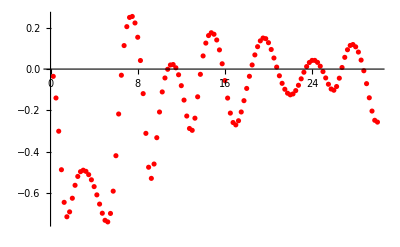

{{0.25,{-0.0353483,8.94968×10^-15}},{0.5,{-0.140044,1.32344×10^-14}},{0.75,{-0.301072,-2.61761×10^-17}},{1.,{-0.487772,-1.53533×10^-11}},{1.25,{-0.645783,1.33566×10^-8}},{1.5,{-0.715747,-1.81958×10^-13}},{1.75,{-0.691992,-1.26144×10^-10}},{2.,{-0.625911,-4.3085×10^-18}},{2.25,{-0.563245,-4.86851×10^-16}},{2.5,{-0.520267,-2.0939×10^-11}},{2.75,{-0.497155,8.21372×10^-10}},{3.,{-0.490097,5.85681×10^-9}},{3.25,{-0.495669,-1.33355×10^-9}},{3.5,{-0.511613,2.68335×10^-9}},{3.75,{-0.536583,-1.045×10^-10}},{4.,{-0.569645,-9.20318×10^-11}},{4.25,{-0.609644,1.07623×10^-10}},{4.5,{-0.654264,3.04889×10^-12}},{4.75,{-0.698562,2.21248×10^-11}},{5.,{-0.732837,2.20703×10^-8}},{5.25,{-0.740595,3.29286×10^-11}},{5.5,{-0.699615,2.39058×10^-10}},{5.75,{-0.591603,-8.41782×10^-11}},{6.,{-0.419878,4.46571×10^-9}},{6.25,{-0.217683,-5.25716×10^-9}},{6.5,{-0.0297911,3.53894×10^-8}},{6.75,{0.11385,-7.00975×10^-8}},{7.,{0.205554,7.45544×10^-7}},{7.25,{0.250241,-3.05955×10^-10}},{7.5,{0.254975,1.24656×10^-7}},{7.75,{0.223453,2.77465×10^-9}},{8.,{0.154221,8.41632×10^-7}},{8.25,{0.0414681,1.06553×10^-9}},{8.5,{-0.11898,-9.5472×10^-10}},{8.75,{-0.311504,-1.06777×10^-7}},{9.,{-0.475717,-1.73299×10^-7}},{9.25,{-0.529653,-5.04872×10^-9}},{9.5,{-0.460133,1.41197×10^-9}},{9.75,{-0.332523,-9.91824×10^-10}},{10.,{-0.208009,-7.586×10^-9}},{10.25,{-0.110746,2.89676×10^-9}},{10.5,{-0.0430979,5.94659×10^-9}},{10.75,{-0.000965022,-3.90089×10^-8}},{11.,{0.0198515,6.25735×10^-9}},{11.25,{0.0219671,4.33702×10^-9}},{11.5,{0.00628095,1.15547×10^-8}},{11.75,{-0.0276237,3.03647×10^-8}},{12.,{-0.0804098,2.00892×10^-7}},{12.25,{-0.150313,1.5399×10^-8}},{12.5,{-0.227588,-3.66175×10^-8}},{12.75,{-0.287899,4.01685×10^-8}},{13.,{-0.296806,-4.59906×10^-8}},{13.25,{-0.237957,4.34384×10^-9}},{13.5,{-0.134363,-1.01999×10^-8}},{13.75,{-0.0254508,-2.33904×10^-8}},{14.,{0.0636903,5.253×10^-8}},{14.25,{0.125878,-6.35211×10^-8}},{14.5,{0.162371,-7.33106×10^-8}},{14.75,{0.176032,-5.60797×10^-8}},{15.,{0.168717,-7.55599×10^-8}},{15.25,{0.140992,-2.78417×10^-8}},{15.5,{0.0928678,-2.37999×10^-8}},{15.75,{0.0256858,4.89128×10^-8}},{16.,{-0.0556897,-3.39546×10^-8}},{16.25,{-0.140545,3.4761×10^-8}},{16.5,{-0.213316,2.65345×10^-9}},{16.75,{-0.259042,5.68284×10^-9}},{17.,{-0.270461,-5.49658×10^-8}},{17.25,{-0.250388,4.97278×10^-8}},{17.5,{-0.207927,-5.94647×10^-8}},{17.75,{-0.153121,-8.45279×10^-8}},{18.,{-0.0938029,-2.11124×10^-7}},{18.25,{-0.0349973,2.25543×10^-7}},{18.5,{0.0200014,2.38844×10^-7}},{18.75,{0.0686971,-2.9955×10^-7}},{19.,{0.108579,-2.32747×10^-7}},{19.25,{0.136786,-1.71164×10^-7}},{19.5,{0.150374,5.62579×10^-8}},{19.75,{0.147333,2.72723×10^-7}},{20.,{0.127848,-1.73102×10^-7}},{20.25,{0.0949158,-2.82628×10^-7}},{20.5,{0.0536293,-2.69961×10^-7}},{20.75,{0.00957671,6.1639×10^-7}},{21.,{-0.0324741,6.96311×10^-7}},{21.25,{-0.0690811,-1.09212×10^-6}},{21.5,{-0.0978365,1.42799×10^-6}},{21.75,{-0.116891,-9.33061×10^-7}},{22.,{-0.12473,4.75414×10^-7}},{22.25,{-0.12044,3.64651×10^-7}},{22.5,{-0.104306,-8.16805×10^-7}},{22.75,{-0.0785247,-6.26402×10^-7}},{23.,{-0.0471723,-3.85517×10^-6}},{23.25,{-0.0153595,-2.64668×10^-8}},{23.5,{0.0121276,8.14701×10^-8}},{23.75,{0.0318699,2.52359×10^-7}},{24.,{0.0420257,5.17013×10^-7}},{24.25,{0.0420967,-4.27522×10^-7}},{24.5,{0.0324161,-5.27236×10^-7}},{24.75,{0.0138356,3.36814×10^-7}},{25.,{-0.0121979,2.99702×10^-6}},{25.25,{-0.0429076,-8.21997×10^-7}},{25.5,{-0.0735794,1.16633×10^-6}},{25.75,{-0.0965134,-3.76685×10^-6}},{26.,{-0.102544,8.08271×10^-8}},{26.25,{-0.0845794,-0.0000321821}},{26.5,{-0.0441536,2.10689×10^-6}},{26.75,{0.00763479,3.16087×10^-6}},{27.,{0.0568571,2.28214×10^-6}},{27.25,{0.0936932,2.74255×10^-7}},{27.5,{0.114474,2.80062×10^-7}},{27.75,{0.118907,-5.42587×10^-6}},{28.,{0.107847,-1.1274×10^-6}},{28.25,{0.0824891,-1.62085×10^-6}},{28.5,{0.0435596,2.56712×10^-6}},{28.75,{-0.00813645,0.0000103288}},{29.,{-0.0706694,2.91161×10^-6}},{29.25,{-0.139134,0.0000141758}},{29.5,{-0.203487,8.59815×10^-6}},{29.75,{-0.248184,-0.0000153066}},{30.,{-0.256957,-5.08825×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$146748682 near {ϕ$146748682} = {5.35043}. NIntegrate obtained -6.07999×10^-15 and 7.36396×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$146834436 near {ϕ$146834436} = {2.51563}. NIntegrate obtained -1.86846×10^-15 and 2.58078×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$146955573 near {ϕ$146955573} = {4.00052}. NIntegrate obtained 1.44728×10^-14 and 7.16197×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

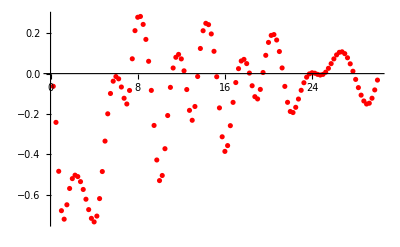

{{0.25,{-0.0629432,-5.87232×10^-14}},{0.5,{-0.241898,-9.80755×10^-14}},{0.75,{-0.484544,2.26672×10^-12}},{1.,{-0.680079,3.49782×10^-16}},{1.25,{-0.722091,2.49838×10^-16}},{1.5,{-0.650732,-1.1387×10^-16}},{1.75,{-0.569821,7.27002×10^-9}},{2.,{-0.520875,-4.96253×10^-11}},{2.25,{-0.503829,2.57298×10^-16}},{2.5,{-0.510865,-3.66857×10^-17}},{2.75,{-0.535909,1.07528×10^-17}},{3.,{-0.574735,-5.15664×10^-11}},{3.25,{-0.623166,-5.52602×10^-11}},{3.5,{-0.674739,-4.81775×10^-9}},{3.75,{-0.718119,-5.09679×10^-16}},{4.,{-0.735652,4.56242×10^-11}},{4.25,{-0.706838,1.58122×10^-10}},{4.5,{-0.62004,-2.96106×10^-10}},{4.75,{-0.485783,9.0896×10^-10}},{5.,{-0.334779,7.18462×10^-10}},{5.25,{-0.199404,6.10921×10^-10}},{5.5,{-0.0986211,1.1569×10^-10}},{5.75,{-0.0376296,-1.59247×10^-7}},{6.,{-0.0145918,-7.96459×10^-8}},{6.25,{-0.0258911,-8.5204×10^-9}},{6.5,{-0.0664803,5.12141×10^-9}},{6.75,{-0.122195,4.6751×10^-9}},{7.,{-0.15066,-6.65365×10^-9}},{7.25,{-0.0835191,-7.2797×10^-9}},{7.5,{0.0735168,-7.18798×10^-7}},{7.75,{0.213157,-4.76828×10^-9}},{8.,{0.279479,4.50999×10^-9}},{8.25,{0.283549,3.42012×10^-7}},{8.5,{0.244103,3.27938×10^-9}},{8.75,{0.169755,1.39416×10^-8}},{9.,{0.0611568,-6.15851×10^-9}},{9.25,{-0.0832651,1.10075×10^-9}},{9.5,{-0.257121,-2.6934×10^-8}},{9.75,{-0.428522,8.65665×10^-9}},{10.,{-0.530749,1.19917×10^-8}},{10.25,{-0.505446,-2.28124×10^-8}},{10.5,{-0.372535,4.51847×10^-9}},{10.75,{-0.207919,-3.64643×10^-8}},{11.,{-0.0682472,1.90379×10^-8}},{11.25,{0.0278852,7.19541×10^-9}},{11.5,{0.0809921,-2.95193×10^-8}},{11.75,{0.095319,-1.53925×10^-8}},{12.,{0.0730315,-7.58447×10^-8}},{12.25,{0.0139053,-1.33382×10^-7}},{12.5,{-0.0790213,-1.42553×10^-7}},{12.75,{-0.182334,-9.24631×10^-9}},{13.,{-0.231491,-7.38519×10^-9}},{13.25,{-0.163133,0.0000115338}},{13.5,{-0.0143494,4.30797×10^-8}},{13.75,{0.124699,1.10051×10^-7}},{14.,{0.212727,-7.47863×10^-8}},{14.25,{0.249544,3.95598×10^-7}},{14.5,{0.242966,6.18428×10^-8}},{14.75,{0.196861,-3.14431×10^-7}},{15.,{0.110689,2.90214×10^-8}},{15.25,{-0.0156304,-2.89911×10^-8}},{15.5,{-0.170046,1.42906×10^-8}},{15.75,{-0.313421,-3.65869×10^-7}},{16.,{-0.385842,-5.59971×10^-7}},{16.25,{-0.357081,-1.45542×10^-7}},{16.5,{-0.258245,9.48766×10^-8}},{16.75,{-0.142687,-3.08041×10^-7}},{17.,{-0.0443391,-4.95156×10^-7}},{17.25,{0.0246171,-1.85069×10^-7}},{17.5,{0.0625872,1.64487×10^-7}},{17.75,{0.0705554,8.38029×10^-7}},{18.,{0.0496671,1.07155×10^-6}},{18.25,{0.00270949,8.97424×10^-7}},{18.5,{-0.0602049,2.14131×10^-6}},{18.75,{-0.114421,-2.52533×10^-6}},{19.,{-0.125585,-5.62374×10^-6}},{19.25,{-0.078352,-1.81683×10^-6}},{19.5,{0.00548526,-6.65114×10^-7}},{19.75,{0.0907137,-1.26732×10^-6}},{20.,{0.154777,2.41729×10^-7}},{20.25,{0.189664,8.79493×10^-9}},{20.5,{0.193684,5.73899×10^-7}},{20.75,{0.16667,-2.29861×10^-7}},{21.,{0.10959,-5.66602×10^-7}},{21.25,{0.0281947,-6.13094×10^-7}},{21.5,{-0.063401,8.73054×10^-7}},{21.75,{-0.142439,3.13346×10^-6}},{22.,{-0.187853,7.0789×10^-7}},{22.25,{-0.19317,-2.78219×10^-6}},{22.5,{-0.167211,-9.43384×10^-7}},{22.75,{-0.126119,5.68325×10^-6}},{23.,{-0.082763,4.12024×10^-6}},{23.25,{-0.0452933,-0.0000457034}},{23.5,{-0.0177353,-9.07562×10^-6}},{23.75,{-0.00147101,-7.71138×10^-7}},{24.,{0.00420776,1.63925×10^-6}},{24.25,{0.00196401,4.05703×10^-7}},{24.5,{-0.00364135,6.98174×10^-6}},{24.75,{-0.00707466,8.22406×10^-6}},{25.,{-0.00381861,0.0000358981}},{25.25,{0.0071294,-0.0000100276}},{25.5,{0.0262218,-4.67112×10^-6}},{25.75,{0.0494832,7.16864×10^-6}},{26.,{0.0730329,4.0173×10^-6}},{26.25,{0.0929313,-0.0000171542}},{26.5,{0.105617,-9.92187×10^-6}},{26.75,{0.1082,8.40263×10^-6}},{27.,{0.0991264,0.000033157}},{27.25,{0.0786147,0.0000183009}},{27.5,{0.0485429,-0.0000172899}},{27.75,{0.0117386,-3.42999×10^-6}},{28.,{-0.0287152,6.70408×10^-6}},{28.25,{-0.0694833,-5.80315×10^-6}},{28.5,{-0.106817,7.26403×10^-6}},{28.75,{-0.135814,-5.49898×10^-6}},{29.,{-0.150781,-0.0000118545}},{29.25,{-0.146785,2.09209×10^-6}},{29.5,{-0.122151,-0.0000303581}},{29.75,{-0.0808648,-0.0000280408}},{30.,{-0.0321125,0.0000106509}}}

```mathematica
Getv2kT[1.0]
Getv2kT[1.5]
Getv2kT[2.0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40900232 near {ϕ$40900232} = {1.05528}. NIntegrate obtained 2.81194×10^-13 and 8.96036×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41000418 near {ϕ$41000418} = {0.944835}. NIntegrate obtained 1.36391×10^-14 and 2.52063×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41124056 near {ϕ$41124056} = {3.98825}. NIntegrate obtained 5.3992×10^-14 and 2.01634×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

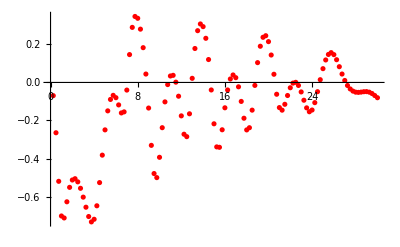

{{0.25,{-0.0693562,3.27778×10^-12}},{0.5,{-0.264497,8.74845×10^-13}},{0.75,{-0.519807,1.03292×10^-11}},{1.,{-0.702117,-8.68535×10^-17}},{1.25,{-0.71245,-5.61787×10^-13}},{1.5,{-0.627483,6.08425×10^-8}},{1.75,{-0.551575,2.45245×10^-16}},{2.,{-0.512907,-3.30257×10^-16}},{2.25,{-0.506108,4.03623×10^-16}},{2.5,{-0.522661,-1.92869×10^-16}},{2.75,{-0.556559,8.02492×10^-17}},{3.,{-0.603028,1.13657×10^-11}},{3.25,{-0.655956,-1.42205×10^-9}},{3.5,{-0.704965,1.24965×10^-15}},{3.75,{-0.733205,-3.47611×10^-8}},{4.,{-0.719404,-2.92988×10^-11}},{4.25,{-0.648504,8.9968×10^-17}},{4.5,{-0.526554,3.06377×10^-10}},{4.75,{-0.38221,1.10115×10^-9}},{5.,{-0.249315,-1.0565×10^-7}},{5.25,{-0.149399,2.28277×10^-9}},{5.5,{-0.0893613,-5.69456×10^-8}},{5.75,{-0.0677901,3.20136×10^-15}},{6.,{-0.0801176,-1.13835×10^-7}},{6.25,{-0.118103,3.34597×10^-9}},{6.5,{-0.160256,-3.48003×10^-7}},{6.75,{-0.154668,-1.36487×10^-9}},{7.,{-0.0400762,2.70429×10^-15}},{7.25,{0.146493,-1.17914×10^-8}},{7.5,{0.289555,2.40185×10^-8}},{7.75,{0.346994,5.4291×10^-9}},{8.,{0.337355,5.98683×10^-9}},{8.25,{0.280282,-2.39293×10^-9}},{8.5,{0.18287,-1.409×10^-7}},{8.75,{0.0442053,7.0656×10^-9}},{9.,{-0.134551,-1.90432×10^-8}},{9.25,{-0.330748,4.91493×10^-9}},{9.5,{-0.478986,-4.41539×10^-9}},{9.75,{-0.500395,-9.63034×10^-9}},{10.,{-0.393568,-1.32561×10^-8}},{10.25,{-0.237872,-2.81428×10^-7}},{10.5,{-0.102156,6.91468×10^-15}},{10.75,{-0.0111857,5.01084×10^-8}},{11.,{0.0340048,-1.91543×10^-8}},{11.25,{0.0374314,8.05029×10^-8}},{11.5,{0.00154965,4.76849×10^-7}},{11.75,{-0.0723616,1.86988×10^-8}},{12.,{-0.175708,2.61207×10^-8}},{12.25,{-0.272232,6.60231×10^-15}},{12.5,{-0.285005,1.00568×10^-6}},{12.75,{-0.164802,-4.79282×10^-8}},{13.,{0.0216983,-1.68462×10^-7}},{13.25,{0.178526,-4.39154×10^-9}},{13.5,{0.2722,2.75561×10^-9}},{13.75,{0.30759,-1.35109×10^-7}},{14.,{0.29351,1.49699×10^-7}},{14.25,{0.232167,-4.00109×10^-8}},{14.5,{0.120482,1.75073×10^-7}},{14.75,{-0.0394777,9.64361×10^-8}},{15.,{-0.217385,-2.77629×10^-7}},{15.25,{-0.338845,-1.80563×10^-7}},{15.5,{-0.341019,3.76697×10^-8}},{15.75,{-0.248857,-1.2526×10^-7}},{16.,{-0.133255,-8.21272×10^-8}},{16.25,{-0.0395064,-8.74731×10^-8}},{16.5,{0.0183061,-4.18746×10^-8}},{16.75,{0.0393216,1.9617×10^-7}},{17.,{0.0250623,4.63212×10^-7}},{17.25,{-0.0229257,3.47793×10^-7}},{17.5,{-0.0997262,3.25856×10^-7}},{17.75,{-0.188149,7.75953×10^-7}},{18.,{-0.249523,9.74269×10^-7}},{18.25,{-0.237989,-8.71465×10^-7}},{18.5,{-0.145618,5.76398×10^-7}},{18.75,{-0.0155294,4.39139×10^-7}},{19.,{0.104232,5.51215×10^-7}},{19.25,{0.190392,-6.02508×10^-7}},{19.5,{0.237482,5.14911×10^-7}},{19.75,{0.245757,-6.66486×10^-7}},{20.,{0.21462,9.99586×10^-7}},{20.25,{0.14423,-0.0000250429}},{20.5,{0.0430762,-3.98596×10^-6}},{20.75,{-0.0620213,-5.21161×10^-6}},{21.,{-0.132116,5.79019×10^-6}},{21.25,{-0.14573,-1.9294×10^-6}},{21.5,{-0.114867,2.11114×10^-6}},{21.75,{-0.0686221,-1.01858×10^-6}},{22.,{-0.027884,2.92952×10^-6}},{22.25,{-0.00342316,3.02474×10^-6}},{22.5,{0.000673929,-4.52196×10^-6}},{22.75,{-0.0158014,-1.58651×10^-6}},{23.,{-0.0497899,0.0000109877}},{23.25,{-0.0934964,4.23416×10^-6}},{23.5,{-0.133605,4.22336×10^-6}},{23.75,{-0.154114,-5.43058×10^-6}},{24.,{-0.144988,5.9638×10^-6}},{24.25,{-0.10616,-2.38047×10^-6}},{24.5,{-0.0485912,-7.45229×10^-6}},{24.75,{0.0145215,-0.0000115283}},{25.,{0.0724828,0.0000115135}},{25.25,{0.118275,0.000289886}},{25.5,{0.147264,0.0000223505}},{25.75,{0.156778,0.0000143}},{26.,{0.146297,-0.0000172032}},{26.25,{0.11958,-4.33783×10^-8}},{26.5,{0.0828415,-0.0000142225}},{26.75,{0.0442744,0.0000139527}},{27.,{0.0103689,0.000034076}},{27.25,{-0.0159159,7.70683×10^-6}},{27.5,{-0.0341643,-0.0000246012}},{27.75,{-0.0454111,-0.0000346288}},{28.,{-0.0510132,-0.0000132535}},{28.25,{-0.0522073,4.47161×10^-6}},{28.5,{-0.050785,0.0000257767}},{28.75,{-0.0486603,9.6567×10^-7}},{29.,{-0.0481759,0.0000345098}},{29.25,{-0.0511005,0.0000101402}},{29.5,{-0.0581517,-0.000034162}},{29.75,{-0.068726,0.0000178406}},{30.,{-0.0802874,-8.26257×10^-6}}}

```mathematica
Getv2kT[2.1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$49953919 near {ϕ$49953919} = {3.76736}. NIntegrate obtained 2.11577×10^-14 and 3.50478×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50058615 near {ϕ$50058615} = {1.10437}. NIntegrate obtained 1.60531×10^-15 and 2.81922×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50166427 near {ϕ$50166427} = {2.14748}. NIntegrate obtained -1.57622×10^-12 and 1.2571×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

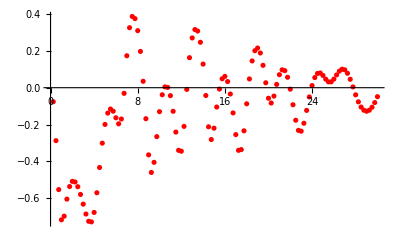

{{0.25,{-0.0760609,2.95696×10^-13}},{0.5,{-0.287663,1.24942×10^-13}},{0.75,{-0.553573,-3.64874×10^-10}},{1.,{-0.717692,2.5427×10^-16}},{1.25,{-0.697999,-4.66858×10^-11}},{1.5,{-0.605315,3.02554×10^-8}},{1.75,{-0.536977,8.8318×10^-9}},{2.,{-0.508859,-9.871×10^-17}},{2.25,{-0.512064,-9.0548×10^-9}},{2.5,{-0.537838,-1.23879×10^-16}},{2.75,{-0.580022,-8.3896×10^-8}},{3.,{-0.63258,-3.41244×10^-12}},{3.25,{-0.686274,-1.20229×10^-15}},{3.5,{-0.725619,2.53824×10^-11}},{3.75,{-0.729059,-3.03984×10^-16}},{4.,{-0.677581,-2.43882×10^-11}},{4.25,{-0.570758,-2.09055×10^-10}},{4.5,{-0.433526,1.5287×10^-9}},{4.75,{-0.301342,2.0522×10^-10}},{5.,{-0.199584,5.26073×10^-8}},{5.25,{-0.137894,-7.84358×10^-8}},{5.5,{-0.115722,-6.38261×10^-8}},{5.75,{-0.127782,2.35024×10^-9}},{6.,{-0.163344,2.80557×10^-8}},{6.25,{-0.196151,3.48765×10^-15}},{6.5,{-0.170172,5.20422×10^-9}},{6.75,{-0.0306164,-1.0317×10^-8}},{7.,{0.173435,1.75204×10^-8}},{7.25,{0.325987,4.22129×10^-9}},{7.5,{0.387038,2.78931×10^-8}},{7.75,{0.375296,-3.50776×10^-8}},{8.,{0.309975,4.12828×10^-8}},{8.25,{0.196968,3.87014×10^-7}},{8.5,{0.0348522,1.50563×10^-7}},{8.75,{-0.168411,4.86914×10^-8}},{9.,{-0.364956,4.24113×10^-8}},{9.25,{-0.460425,-1.40906×10^-8}},{9.5,{-0.405489,3.29244×10^-8}},{9.75,{-0.26582,4.37683×10^-8}},{10.,{-0.13024,-5.56296×10^-8}},{10.25,{-0.038386,-2.09807×10^-8}},{10.5,{0.00437985,8.63057×10^-8}},{10.75,{0.00175983,2.87448×10^-8}},{11.,{-0.0432732,5.29675×10^-7}},{11.25,{-0.128166,1.67414×10^-7}},{11.5,{-0.241149,-1.83707×10^-7}},{11.75,{-0.340196,1.69186×10^-7}},{12.,{-0.344983,1.25872×10^-7}},{12.25,{-0.210192,0.0000182653}},{12.5,{-0.00918605,-1.6097×10^-7}},{12.75,{0.163107,-1.7145×10^-7}},{13.,{0.270333,-1.13589×10^-7}},{13.25,{0.315902,1.15131×10^-7}},{13.5,{0.307861,5.16949×10^-8}},{13.75,{0.246903,-2.27942×10^-7}},{14.,{0.128275,4.46364×10^-7}},{14.25,{-0.042361,4.02397×10^-7}},{14.5,{-0.212349,2.×10^-7}},{14.75,{-0.281569,-6.43235×10^-8}},{15.,{-0.21991,-3.17579×10^-7}},{15.25,{-0.104914,-3.51035×10^-7}},{15.5,{-0.00756212,-2.56312×10^-7}},{15.75,{0.048458,-3.34446×10^-7}},{16.,{0.0614645,-0.0000168169}},{16.25,{0.0334075,1.62463×10^-8}},{16.5,{-0.034354,0.000018165}},{16.75,{-0.136983,3.23503×10^-7}},{17.,{-0.254784,-8.60834×10^-8}},{17.25,{-0.340289,-8.57255×10^-8}},{17.5,{-0.33631,3.42612×10^-7}},{17.75,{-0.234307,-1.8019×10^-6}},{18.,{-0.0875089,6.17888×10^-7}},{18.25,{0.0475386,-9.25407×10^-7}},{18.5,{0.145447,2.43809×10^-6}},{18.75,{0.201075,-1.41201×10^-6}},{19.,{0.21548,-1.53741×10^-6}},{19.25,{0.188657,-3.98445×10^-7}},{19.5,{0.121523,1.6476×10^-7}},{19.75,{0.0267626,-8.0307×10^-8}},{20.,{-0.0572935,-2.38504×10^-6}},{20.25,{-0.0832021,-1.52606×10^-6}},{20.5,{-0.0456324,-3.78693×10^-6}},{20.75,{0.0179079,1.407×10^-6}},{21.,{0.0706256,-4.31403×10^-6}},{21.25,{0.0970986,7.68078×10^-6}},{21.5,{0.0926289,1.91704×10^-6}},{21.75,{0.0567424,-9.32719×10^-6}},{22.,{-0.00803378,-0.0000551475}},{22.25,{-0.092659,0.0000656447}},{22.5,{-0.176831,0.00036398}},{22.75,{-0.231763,-0.000133299}},{23.,{-0.236308,0.0000499832}},{23.25,{-0.193018,2.74517×10^-6}},{23.5,{-0.123302,7.05973×10^-6}},{23.75,{-0.0501142,0.0000325168}},{24.,{0.0116524,2.22552×10^-8}},{24.25,{0.0549546,0.0000101345}},{24.5,{0.0774502,-9.3041×10^-7}},{24.75,{0.0799327,2.12383×10^-6}},{25.,{0.0666161,-5.99884×10^-6}},{25.25,{0.0464874,-7.04721×10^-7}},{25.5,{0.0318031,3.6907×10^-7}},{25.75,{0.0317326,0.0000199244}},{26.,{0.0467048,2.5232×10^-7}},{26.25,{0.0692797,-0.0000255416}},{26.5,{0.0897692,0.0000205389}},{26.75,{0.100591,0.0000362501}},{27.,{0.0971846,-0.0000143695}},{27.25,{0.0783054,-0.0000317634}},{27.5,{0.0456798,0.0000381465}},{27.75,{0.00428042,-0.0000430926}},{28.,{-0.0387254,-6.9782×10^-6}},{28.25,{-0.0768142,-0.0000164065}},{28.5,{-0.105176,8.77114×10^-6}},{28.75,{-0.122209,-7.40478×10^-6}},{29.,{-0.12784,-9.38196×10^-6}},{29.25,{-0.122353,-0.0000193583}},{29.5,{-0.106333,0.0000120533}},{29.75,{-0.0809013,0.0000129046}},{30.,{-0.0487436,-0.0000120749}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58218103 near {ϕ$58218103} = {5.68177}. NIntegrate obtained 6.64106×10^-15 and 6.22748×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58333623 near {ϕ$58333623} = {5.17862}. NIntegrate obtained 1.30714×10^-17 and 3.17923×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58419623 near {ϕ$58419623} = {4.13551}. NIntegrate obtained -1.2265×10^-18 and 4.48995×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

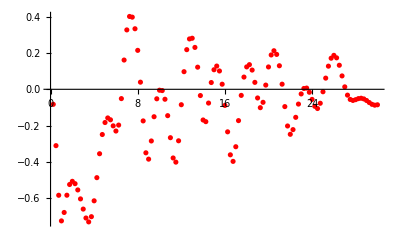

{{0.25,{-0.0830524,1.10599×10^-13}},{0.5,{-0.31131,1.22623×10^-15}},{0.75,{-0.585399,-3.40374×10^-16}},{1.,{-0.726952,-2.32947×10^-14}},{1.25,{-0.680406,2.0404×10^-10}},{1.5,{-0.585111,-3.34507×10^-16}},{1.75,{-0.525952,2.50899×10^-16}},{2.,{-0.50837,8.85373×10^-9}},{2.25,{-0.521295,-1.84044×10^-11}},{2.5,{-0.555914,3.14781×10^-12}},{2.75,{-0.605466,-4.28794×10^-9}},{3.,{-0.661698,1.40181×10^-12}},{3.25,{-0.710988,6.73648×10^-12}},{3.5,{-0.732498,-5.30183×10^-15}},{3.75,{-0.703677,-6.60915×10^-11}},{4.,{-0.616027,8.60102×10^-11}},{4.25,{-0.488115,-6.39691×10^-10}},{4.5,{-0.355911,1.19653×10^-15}},{4.75,{-0.24978,7.97721×10^-8}},{5.,{-0.183516,-1.34188×10^-7}},{5.25,{-0.158233,-1.76534×10^-15}},{5.5,{-0.168437,1.31273×10^-9}},{5.75,{-0.201964,1.87927×10^-9}},{6.,{-0.23049,-8.58815×10^-9}},{6.25,{-0.197659,-3.66528×10^-10}},{6.5,{-0.0513862,3.56099×10^-9}},{6.75,{0.161613,5.94445×10^-9}},{7.,{0.328111,-5.57527×10^-9}},{7.25,{0.402402,-8.12862×10^-9}},{7.5,{0.39858,-3.17684×10^-9}},{7.75,{0.334506,1.66008×10^-9}},{8.,{0.215129,9.165×10^-7}},{8.25,{0.0394136,-2.77191×10^-8}},{8.5,{-0.174623,3.69971×10^-8}},{8.75,{-0.350822,8.00996×10^-8}},{9.,{-0.385825,-1.81775×10^-9}},{9.25,{-0.285434,2.91081×10^-8}},{9.5,{-0.151493,-4.33482×10^-8}},{9.75,{-0.0524498,4.60477×10^-8}},{10.,{-0.00501566,-3.86543×10^-8}},{10.25,{-0.00703214,-4.94659×10^-8}},{10.5,{-0.0549357,1.47138×10^-9}},{10.75,{-0.145602,-6.76997×10^-8}},{11.,{-0.267327,-5.69284×10^-8}},{11.25,{-0.379367,-7.31708×10^-8}},{11.5,{-0.402311,1.31367×10^-6}},{11.75,{-0.284492,-6.60815×10^-8}},{12.,{-0.0851729,-2.54085×10^-8}},{12.25,{0.0973426,5.66456×10^-8}},{12.5,{0.218996,-1.73548×10^-14}},{12.75,{0.278269,6.12484×10^-8}},{13.,{0.282056,-2.13406×10^-7}},{13.25,{0.231388,-2.83651×10^-7}},{13.5,{0.122258,2.01899×10^-7}},{13.75,{-0.0345571,1.602×10^-7}},{14.,{-0.169527,1.53134×10^-8}},{14.25,{-0.178731,-1.25834×10^-7}},{14.5,{-0.0759851,1.13742×10^-7}},{14.75,{0.0373647,2.10263×10^-7}},{15.,{0.108024,1.69344×10^-7}},{15.25,{0.128346,-1.22136×10^-8}},{15.5,{0.101246,-8.02297×10^-7}},{15.75,{0.0281274,-2.90585×10^-7}},{16.,{-0.0890485,1.30033×10^-7}},{16.25,{-0.234968,-2.61184×10^-8}},{16.5,{-0.361929,-2.09931×10^-8}},{16.75,{-0.398189,-3.53265×10^-7}},{17.,{-0.317255,-6.17724×10^-7}},{17.25,{-0.173003,-2.19922×10^-6}},{17.5,{-0.0336538,-7.19582×10^-7}},{17.75,{0.0675156,2.80375×10^-7}},{18.,{0.123746,-5.08402×10^-7}},{18.25,{0.136117,1.05164×10^-7}},{18.5,{0.106233,9.74458×10^-8}},{18.75,{0.0383112,-1.47203×10^-7}},{19.,{-0.0478896,-3.92202×10^-6}},{19.25,{-0.101517,3.62287×10^-6}},{19.5,{-0.0719395,4.22238×10^-6}},{19.75,{0.02323,1.84141×10^-6}},{20.,{0.123462,-0.0000155294}},{20.25,{0.189764,-7.71182×10^-6}},{20.5,{0.213021,-4.57217×10^-6}},{20.75,{0.192813,0.0000621662}},{21.,{0.130094,-9.892×10^-6}},{21.25,{0.028261,2.09794×10^-6}},{21.5,{-0.0956013,4.51489×10^-6}},{21.75,{-0.202653,-8.06066×10^-6}},{22.,{-0.248547,8.12793×10^-6}},{22.25,{-0.222767,0.0000170155}},{22.5,{-0.154861,6.47635×10^-7}},{22.75,{-0.0816454,5.88259×10^-6}},{23.,{-0.0255615,1.22694×10^-6}},{23.25,{0.00452493,-7.2653×10^-6}},{23.5,{0.00673326,-5.21177×10^-6}},{23.75,{-0.0162725,1.64535×10^-6}},{24.,{-0.0557963,-0.0000124507}},{24.25,{-0.0938461,-0.0000115619}},{24.5,{-0.10616,0.0000111278}},{24.75,{-0.0771056,9.69164×10^-6}},{25.,{-0.013582,0.000320733}},{25.25,{0.0617946,-0.0000216832}},{25.5,{0.127833,1.68601×10^-6}},{25.75,{0.171724,-0.0000587602}},{26.,{0.187544,-0.0000266014}},{26.25,{0.173838,0.0000207558}},{26.5,{0.132824,-0.0000378905}},{26.75,{0.0739294,0.0000134884}},{27.,{0.0134914,-0.0000748816}},{27.25,{-0.0322324,0.000172258}},{27.5,{-0.0560677,0.0000149594}},{27.75,{-0.0615319,6.60979×10^-7}},{28.,{-0.0572213,-4.19677×10^-6}},{28.25,{-0.051455,-0.000010015}},{28.5,{-0.0493656,-0.0000256914}},{28.75,{-0.0532251,-0.0000312694}},{29.,{-0.0619232,-0.0000287276}},{29.25,{-0.0731581,1.70994×10^-6}},{29.5,{-0.0829732,-0.0000639538}},{29.75,{-0.0877004,-0.0000102916}},{30.,{-0.0855017,6.22237×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66260227 near {ϕ$66260227} = {5.68177}. NIntegrate obtained -2.42108×10^-15 and 4.69018×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66344177 near {ϕ$66344177} = {4.55276}. NIntegrate obtained -9.60874×10^-18 and 1.57976×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66413941 near {ϕ$66413941} = {5.25225}. NIntegrate obtained -6.1509×10^-12 and 5.2519×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

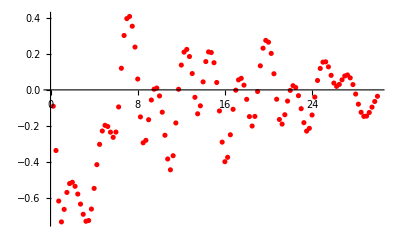

{{0.25,{-0.0903276,-4.77702×10^-14}},{0.5,{-0.335344,-1.0796×10^-15}},{0.75,{-0.61486,-2.02787×10^-9}},{1.,{-0.730326,2.76665×10^-14}},{1.25,{-0.661136,3.35871×10^-10}},{1.5,{-0.567373,6.72833×10^-9}},{1.75,{-0.518309,5.08146×10^-17}},{2.,{-0.511085,-8.48156×10^-17}},{2.25,{-0.533425,5.36209×10^-16}},{2.5,{-0.576363,7.08912×10^-16}},{2.75,{-0.631862,1.68663×10^-9}},{3.,{-0.688315,1.02613×10^-15}},{3.25,{-0.726796,9.38871×10^-16}},{3.5,{-0.722763,-1.00425×10^-15}},{3.75,{-0.659243,1.21712×10^-8}},{4.,{-0.544953,-7.21045×10^-9}},{4.25,{-0.413741,3.75493×10^-9}},{4.5,{-0.301324,9.72146×10^-8}},{4.75,{-0.227423,-1.08689×10^-7}},{5.,{-0.19611,2.09032×10^-9}},{5.25,{-0.202463,-1.74535×10^-16}},{5.5,{-0.233947,1.0743×10^-9}},{5.75,{-0.262363,-8.46807×10^-15}},{6.,{-0.233329,9.43331×10^-15}},{6.25,{-0.0942421,-4.75315×10^-7}},{6.5,{0.11964,-1.02191×10^-9}},{6.75,{0.300924,1.80015×10^-8}},{7.,{0.394355,-3.77736×10^-9}},{7.25,{0.406225,-4.00527×10^-9}},{7.5,{0.35225,-6.90051×10^-7}},{7.75,{0.236881,-2.60017×10^-8}},{8.,{0.0600796,-6.33299×10^-8}},{8.25,{-0.149485,-2.59401×10^-8}},{8.5,{-0.292783,1.86613×10^-8}},{8.75,{-0.279051,4.98013×10^-8}},{9.,{-0.16502,5.40146×10^-7}},{9.25,{-0.0560841,3.03692×10^-8}},{9.5,{0.0037057,1.35205×10^-8}},{9.75,{0.0100337,4.75707×10^-8}},{10.,{-0.0334106,3.25057×10^-7}},{10.25,{-0.123434,-9.93486×10^-8}},{10.5,{-0.250988,-4.39855×10^-8}},{10.75,{-0.38218,4.43275×10^-10}},{11.,{-0.44224,2.28683×10^-8}},{11.25,{-0.364215,9.30257×10^-9}},{11.5,{-0.182948,9.64962×10^-8}},{11.75,{0.00343703,1.38778×10^-7}},{12.,{0.137302,-1.74328×10^-7}},{12.25,{0.209023,3.28308×10^-6}},{12.5,{0.223879,-4.06089×10^-7}},{12.75,{0.1845,3.25206×10^-7}},{13.,{0.0904151,1.07508×10^-7}},{13.25,{-0.041068,-7.01097×10^-8}},{13.5,{-0.132286,-8.46162×10^-8}},{13.75,{-0.0881709,-8.82885×10^-8}},{14.,{0.0443448,-4.87513×10^-6}},{14.25,{0.156616,1.98678×10^-7}},{14.5,{0.210213,-5.04509×10^-7}},{14.75,{0.206667,-4.5742×10^-7}},{15.,{0.150307,1.00992×10^-6}},{15.25,{0.0410419,-8.68824×10^-7}},{15.5,{-0.116443,2.73376×10^-9}},{15.75,{-0.288946,-5.02049×10^-7}},{16.,{-0.397099,3.6086×10^-7}},{16.25,{-0.372999,6.91336×10^-7}},{16.5,{-0.248292,2.83357×10^-7}},{16.75,{-0.107405,-4.86155×10^-7}},{17.,{-0.00168677,-6.17228×10^-7}},{17.25,{0.0553276,3.05469×10^-6}},{17.5,{0.0638351,-6.53996×10^-7}},{17.75,{0.0261167,1.53924×10^-6}},{18.,{-0.0522494,1.61035×10^-6}},{18.25,{-0.147661,-0.0000246858}},{18.5,{-0.199981,9.3861×10^-7}},{18.75,{-0.146704,-1.26489×10^-6}},{19.,{-0.00890777,-1.06619×10^-6}},{19.25,{0.133199,-0.0000175634}},{19.5,{0.230556,8.24926×10^-7}},{19.75,{0.273683,-7.59259×10^-6}},{20.,{0.264023,0.0000177387}},{20.25,{0.201793,-0.0000109448}},{20.5,{0.0892995,-4.95655×10^-6}},{20.75,{-0.0516737,5.92451×10^-6}},{21.,{-0.163703,-1.69215×10^-6}},{21.25,{-0.189244,2.47142×10^-7}},{21.5,{-0.137449,0.0000102216}},{21.75,{-0.0619236,0.0000102453}},{22.,{-0.00297648,-5.8004×10^-6}},{22.25,{0.0232888,8.72524×10^-7}},{22.5,{0.0131189,4.04094×10^-6}},{22.75,{-0.0320023,3.63422×10^-6}},{23.,{-0.10398,-0.000010284}},{23.25,{-0.181347,0.0000202602}},{23.5,{-0.227908,1.83942×10^-6}},{23.75,{-0.212743,7.01488×10^-6}},{24.,{-0.139002,-1.52947×10^-6}},{24.25,{-0.0398189,-2.16897×10^-6}},{24.5,{0.0520733,-1.77503×10^-6}},{24.75,{0.118642,0.000013226}},{25.,{0.153471,6.65019×10^-6}},{25.25,{0.155267,-0.0000383408}},{25.5,{0.127573,5.9558×10^-6}},{25.75,{0.0804096,0.0000134992}},{26.,{0.0377443,-3.29504×10^-6}},{26.25,{0.01939,7.79611×10^-6}},{26.5,{0.030364,4.42734×10^-7}},{26.75,{0.055747,6.45855×10^-6}},{27.,{0.0770458,-5.86091×10^-6}},{27.25,{0.0825033,-5.6109×10^-6}},{27.5,{0.0666218,-2.20627×10^-6}},{27.75,{0.0294444,0.0000147555}},{28.,{-0.0230549,-3.32931×10^-6}},{28.25,{-0.0790958,-0.0000181847}},{28.5,{-0.123986,0.0000569028}},{28.75,{-0.146505,-0.0000289475}},{29.,{-0.144875,0.000018429}},{29.25,{-0.125013,2.40258×10^-6}},{29.5,{-0.0955173,-0.0000513813}},{29.75,{-0.0641386,0.0000671066}},{30.,{-0.0354552,0.0000397459}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$73927575 near {ϕ$73927575} = {5.58359}. NIntegrate obtained -4.6992×10^-16 and 7.65096×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$74034075 near {ϕ$74034075} = {2.17202}. NIntegrate obtained 3.31156×10^-16 and 1.20374×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$74097525 near {ϕ$74097525} = {5.71858}. NIntegrate obtained -7.23557×10^-11 and 9.56291×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

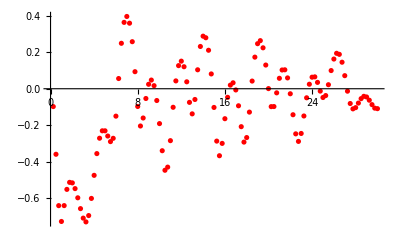

{{0.25,{-0.0978814,-1.09262×10^-14}},{0.5,{-0.359665,4.42938×10^-14}},{0.75,{-0.641571,-2.80872×10^-8}},{1.,{-0.728464,-3.16752×10^-16}},{1.25,{-0.641384,4.77101×10^-8}},{1.5,{-0.552334,-2.28232×10^-8}},{1.75,{-0.513796,3.62059×10^-16}},{2.,{-0.516683,-2.16145×10^-8}},{2.25,{-0.548086,-1.39928×10^-16}},{2.5,{-0.598571,5.57616×10^-8}},{2.75,{-0.657948,-9.02446×10^-16}},{3.,{-0.71008,1.22828×10^-10}},{3.25,{-0.730793,3.11641×10^-7}},{3.5,{-0.69605,-2.52831×10^-9}},{3.75,{-0.601921,-2.55219×10^-9}},{4.,{-0.475263,-7.88152×10^-10}},{4.25,{-0.355977,2.21824×10^-15}},{4.5,{-0.27155,-1.09347×10^-9}},{4.75,{-0.230935,1.64517×10^-9}},{5.,{-0.230902,4.06341×10^-10}},{5.25,{-0.259519,-1.52029×10^-9}},{5.5,{-0.290206,2.71068×10^-10}},{5.75,{-0.272054,-1.85232×10^-9}},{6.,{-0.150413,6.69514×10^-9}},{6.25,{0.0560246,-1.92337×10^-8}},{6.5,{0.249454,-2.90589×10^-8}},{6.75,{0.364262,-2.83695×10^-8}},{7.,{0.396705,-1.28858×10^-14}},{7.25,{0.3598,-2.89855×10^-8}},{7.5,{0.25824,-1.81897×10^-8}},{7.75,{0.0935936,-6.03849×10^-9}},{8.,{-0.09744,-1.10641×10^-8}},{8.25,{-0.204483,-1.29563×10^-9}},{8.5,{-0.160598,-1.14818×10^-8}},{8.75,{-0.0535438,-8.88582×10^-8}},{9.,{0.0244526,6.27322×10^-8}},{9.25,{0.0476148,1.10016×10^-8}},{9.5,{0.0168354,-1.04026×10^-7}},{9.75,{-0.0646089,1.15702×10^-7}},{10.,{-0.191322,-1.05569×10^-7}},{10.25,{-0.340162,-7.4089×10^-7}},{10.5,{-0.447416,-1.11733×10^-8}},{10.75,{-0.4302,2.54472×10^-8}},{11.,{-0.284908,-2.26812×10^-8}},{11.25,{-0.101787,2.27489×10^-7}},{11.5,{0.0430458,2.49148×10^-7}},{11.75,{0.126834,7.47094×10^-7}},{12.,{0.151387,5.63976×10^-7}},{12.25,{0.120709,-6.69342×10^-7}},{12.5,{0.0380741,6.93085×10^-7}},{12.75,{-0.0747573,-5.5486×10^-7}},{13.,{-0.137843,-2.10012×10^-7}},{13.25,{-0.0589312,2.16246×10^-7}},{13.5,{0.103991,5.67781×10^-8}},{13.75,{0.231988,2.31508×10^-7}},{14.,{0.288546,-3.33294×10^-7}},{14.25,{0.279858,-9.62335×10^-7}},{14.5,{0.211223,6.48812×10^-7}},{14.75,{0.0812398,1.23643×10^-6}},{15.,{-0.102633,-1.39662×10^-6}},{15.25,{-0.287379,1.04086×10^-6}},{15.5,{-0.367636,-2.58443×10^-7}},{15.75,{-0.29994,-2.91413×10^-7}},{16.,{-0.164436,5.11031×10^-7}},{16.25,{-0.0471426,-5.66036×10^-7}},{16.5,{0.0197952,6.16431×10^-7}},{16.75,{0.0326632,4.45166×10^-7}},{17.,{-0.00664098,8.62219×10^-7}},{17.25,{-0.0934967,-1.16019×10^-6}},{17.5,{-0.208171,-1.05257×10^-6}},{17.75,{-0.292814,-6.04588×10^-7}},{18.,{-0.267911,3.60874×10^-6}},{18.25,{-0.128258,-1.83038×10^-6}},{18.5,{0.0421172,2.00859×10^-6}},{18.75,{0.17349,6.0301×10^-6}},{19.,{0.247291,-2.86385×10^-6}},{19.25,{0.263989,4.5109×10^-6}},{19.5,{0.224626,1.31289×10^-6}},{19.75,{0.130082,-1.2269×10^-6}},{20.,{0.00071163,-0.0000208185}},{20.25,{-0.0981596,4.74872×10^-6}},{20.5,{-0.0977384,2.20542×10^-6}},{20.75,{-0.0225491,8.09662×10^-6}},{21.,{0.0573259,4.03118×10^-6}},{21.25,{0.102911,4.42875×10^-6}},{21.5,{0.103964,0.0000100966}},{21.75,{0.059461,9.54538×10^-6}},{22.,{-0.0275845,4.95188×10^-6}},{22.25,{-0.142665,0.000021358}},{22.5,{-0.247551,0.0000106091}},{22.75,{-0.289051,1.76721×10^-7}},{23.,{-0.245431,-2.94789×10^-6}},{23.25,{-0.149507,-0.0000136352}},{23.5,{-0.0496628,8.00779×10^-6}},{23.75,{0.0247574,-4.39459×10^-6}},{24.,{0.0633966,0.0000147375}},{24.25,{0.0652118,-0.0000124844}},{24.5,{0.0348867,-0.0000168842}},{24.75,{-0.0129553,-0.0000846885}},{25.,{-0.0481335,-0.0000245292}},{25.25,{-0.0374497,0.000032473}},{25.5,{0.0221123,0.0000150517}},{25.75,{0.099734,3.44524×10^-6}},{26.,{0.162956,-0.0000261684}},{26.25,{0.194496,-0.0000418708}},{26.5,{0.188744,-0.0000169124}},{26.75,{0.145576,0.0000119028}},{27.,{0.0717715,-0.0000127634}},{27.25,{-0.013369,-3.93996×10^-6}},{27.5,{-0.0810547,-2.60411×10^-8}},{27.75,{-0.110432,2.85629×10^-7}},{28.,{-0.103689,0.0000327189}},{28.25,{-0.0786916,0.0000213622}},{28.5,{-0.0542803,-0.0000374499}},{28.75,{-0.0416151,-0.0000207841}},{29.,{-0.0452041,0.0000147925}},{29.25,{-0.062853,-0.0000234826}},{29.5,{-0.0872036,-0.0000539511}},{29.75,{-0.106438,0.0000465728}},{30.,{-0.109292,-0.0000136644}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81667621 near {ϕ$81667621} = {5.58359}. NIntegrate obtained 2.02811×10^-15 and 9.42242×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81747061 near {ϕ$81747061} = {1.70569}. NIntegrate obtained -6.17758×10^-17 and 1.47222×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81817727 near {ϕ$81817727} = {5.64495}. NIntegrate obtained 9.28348×10^-19 and 4.0482×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

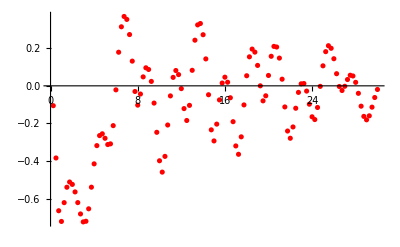

{{0.25,{-0.10571,5.52887×10^-14}},{0.5,{-0.384168,-9.77981×10^-15}},{0.75,{-0.665205,4.20613×10^-16}},{1.,{-0.722166,4.9403×10^-16}},{1.25,{-0.622061,-9.44247×10^-8}},{1.5,{-0.540039,-1.22863×10^-8}},{1.75,{-0.512154,1.50959×10^-16}},{2.,{-0.524862,-2.05709×10^-8}},{2.25,{-0.564896,-6.4661×10^-16}},{2.5,{-0.621817,-9.1526×10^-16}},{2.75,{-0.682221,1.4821×10^-10}},{3.,{-0.72458,-1.54785×10^-8}},{3.25,{-0.721214,-2.2871×10^-15}},{3.5,{-0.654936,-2.40929×10^-9}},{3.75,{-0.539787,-1.75027×10^-9}},{4.,{-0.415481,4.72279×10^-10}},{4.25,{-0.318378,-1.18705×10^-7}},{4.5,{-0.264965,2.38372×10^-9}},{4.75,{-0.255376,-6.4281×10^-10}},{5.,{-0.279205,-7.16215×10^-10}},{5.25,{-0.312569,-1.53053×10^-15}},{5.5,{-0.308986,-9.04646×10^-10}},{5.75,{-0.211949,-4.37728×10^-10}},{6.,{-0.0213471,2.98771×10^-9}},{6.25,{0.179039,9.61754×10^-10}},{6.5,{0.314453,9.37042×10^-9}},{6.75,{0.369467,5.50886×10^-15}},{7.,{0.353714,-7.56353×10^-7}},{7.25,{0.27308,-1.70591×10^-8}},{7.5,{0.131625,-1.10095×10^-6}},{7.75,{-0.0300793,2.20069×10^-8}},{8.,{-0.102729,1.92755×10^-8}},{8.25,{-0.0436019,2.18275×10^-8}},{8.5,{0.0477333,-1.23982×10^-8}},{8.75,{0.0960529,2.39035×10^-8}},{9.,{0.0871584,-1.86354×10^-8}},{9.25,{0.0235496,1.8666×10^-8}},{9.5,{-0.0918262,-2.81939×10^-15}},{9.75,{-0.247465,3.48605×10^-8}},{10.,{-0.399009,-1.54819×10^-8}},{10.25,{-0.459455,-6.31294×10^-8}},{10.5,{-0.375661,-2.15867×10^-7}},{10.75,{-0.208612,1.14898×10^-7}},{11.,{-0.0536048,1.84638×10^-7}},{11.25,{0.0450382,5.54337×10^-8}},{11.5,{0.0815648,1.85526×10^-8}},{11.75,{0.0598229,4.16415×10^-8}},{12.,{-0.0148571,-1.60002×10^-7}},{12.25,{-0.121224,-8.47135×10^-9}},{12.5,{-0.184522,4.2522×10^-9}},{12.75,{-0.104024,-1.90993×10^-7}},{13.,{0.0827025,-9.37031×10^-8}},{13.25,{0.243068,4.70624×10^-7}},{13.5,{0.324556,-3.54966×10^-7}},{13.75,{0.331902,-2.75125×10^-7}},{14.,{0.272217,-1.66828×10^-7}},{14.25,{0.143403,-9.72606×10^-7}},{14.5,{-0.047408,-1.17138×10^-6}},{14.75,{-0.23436,1.441×10^-7}},{15.,{-0.293359,2.31692×10^-9}},{15.25,{-0.203868,7.64862×10^-8}},{15.5,{-0.0749748,1.28939×10^-7}},{15.75,{0.0148694,-7.57026×10^-7}},{16.,{0.0460633,4.27269×10^-7}},{16.25,{0.0192389,-1.63984×10^-8}},{16.5,{-0.0634407,1.43427×10^-6}},{16.75,{-0.190871,3.93124×10^-6}},{17.,{-0.320022,3.6508×10^-7}},{17.25,{-0.364597,-1.51327×10^-6}},{17.5,{-0.271616,-3.45209×10^-6}},{17.75,{-0.10162,-2.963×10^-6}},{18.,{0.0537224,-3.89526×10^-6}},{18.25,{0.154478,0.0000104334}},{18.5,{0.195664,-7.68909×10^-6}},{18.75,{0.179581,-4.8178×10^-7}},{19.,{0.108753,0.000199809}},{19.25,{0.0000485355,2.02402×10^-6}},{19.5,{-0.0799542,4.41683×10^-6}},{19.75,{-0.0530765,-6.44736×10^-6}},{20.,{0.0552457,-7.21741×10^-6}},{20.25,{0.157368,-1.01047×10^-6}},{20.5,{0.210072,-4.44032×10^-6}},{20.75,{0.2067,-5.30755×10^-6}},{21.,{0.147759,7.00497×10^-6}},{21.25,{0.0354175,-0.0000175282}},{21.5,{-0.112366,0.0000121187}},{21.75,{-0.240637,-2.1554×10^-6}},{22.,{-0.279064,0.0000180205}},{22.25,{-0.218969,-5.02884×10^-6}},{22.5,{-0.119304,-0.000018856}},{22.75,{-0.0348915,4.93002×10^-6}},{23.,{0.0107059,-6.24448×10^-6}},{23.25,{0.0121604,-6.82665×10^-6}},{23.5,{-0.0279537,0.0000361463}},{23.75,{-0.0977529,-3.47986×10^-6}},{24.,{-0.164902,-6.89148×10^-6}},{24.25,{-0.179585,-0.0000213642}},{24.5,{-0.115206,3.85496×10^-6}},{24.75,{-0.00279072,-3.12029×10^-6}},{25.,{0.106577,0.0000269643}},{25.25,{0.181986,-0.0000147891}},{25.5,{0.213726,-0.0000272792}},{25.75,{0.19996,-0.0000222633}},{26.,{0.144319,-0.0000597066}},{26.25,{0.0645679,-0.0000158618}},{26.5,{-0.00349155,-0.0000114585}},{26.75,{-0.024865,-0.0000429821}},{27.,{-0.00238303,9.31082×10^-7}},{27.25,{0.0336534,-4.83362×10^-6}},{27.5,{0.0564137,0.0000327209}},{27.75,{0.0525198,-0.0000240265}},{28.,{0.0185786,0.0000101234}},{28.25,{-0.0399183,0.000050935}},{28.5,{-0.108317,0.0000175474}},{28.75,{-0.162672,-0.0000409204}},{29.,{-0.180943,-0.0000109867}},{29.25,{-0.159691,0.000101052}},{29.5,{-0.113555,-0.0000191595}},{29.75,{-0.0621861,0.0000865345}},{30.,{-0.019371,0.0000776235}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$89476117 near {ϕ$89476117} = {3.85326}. NIntegrate obtained -1.29384×10^-13 and 7.50753×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$89580895 near {ϕ$89580895} = {0.858932}. NIntegrate obtained 3.44844×10^-17 and 1.17604×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$89647953 near {ϕ$89647953} = {5.17862}. NIntegrate obtained -1.04122×10^-18 and 9.77517×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

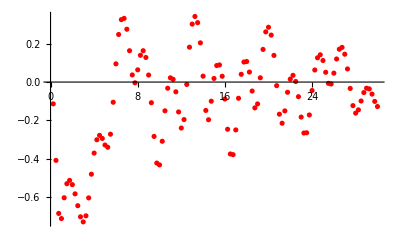

{{0.25,{-0.113807,-4.11587×10^-12}},{0.5,{-0.408741,6.42574×10^-15}},{0.75,{-0.685501,-5.45926×10^-16}},{1.,{-0.712308,-4.38327×10^-13}},{1.25,{-0.603813,5.38268×10^-9}},{1.5,{-0.530421,-5.59228×10^-16}},{1.75,{-0.513121,9.4557×10^-17}},{2.,{-0.535337,-5.26612×10^-16}},{2.25,{-0.583437,-1.08951×10^-15}},{2.5,{-0.645238,9.78848×10^-16}},{2.75,{-0.702995,-3.87573×10^-8}},{3.,{-0.729699,-8.18555×10^-8}},{3.25,{-0.698044,6.83502×10^-9}},{3.5,{-0.604449,9.53683×10^-11}},{3.75,{-0.480754,1.51498×10^-9}},{4.,{-0.370641,-5.6877×10^-15}},{4.25,{-0.301077,9.91185×10^-10}},{4.5,{-0.278154,4.11361×10^-9}},{4.75,{-0.294202,-1.35677×10^-10}},{5.,{-0.328619,-1.4009×10^-15}},{5.25,{-0.340232,-1.02416×10^-9}},{5.5,{-0.27212,3.14341×10^-9}},{5.75,{-0.105367,7.55185×10^-9}},{6.,{0.0950624,1.22468×10^-8}},{6.25,{0.24827,-6.49221×10^-15}},{6.5,{0.325666,-1.74723×10^-8}},{6.75,{0.332269,-5.25169×10^-8}},{7.,{0.275666,1.27788×10^-8}},{7.25,{0.163483,-8.12179×10^-9}},{7.5,{0.0371254,4.45599×10^-8}},{7.75,{-0.00385037,-4.09059×10^-8}},{8.,{0.063719,-1.77758×10^-8}},{8.25,{0.139617,3.69036×10^-8}},{8.5,{0.163462,-1.15267×10^-9}},{8.75,{0.128211,-5.8118×10^-8}},{9.,{0.0366273,-5.26262×10^-6}},{9.25,{-0.107746,-1.10065×10^-7}},{9.5,{-0.283639,1.87681×10^-7}},{9.75,{-0.422779,1.8135×10^-7}},{10.,{-0.432193,-3.1271×10^-7}},{10.25,{-0.308902,5.57202×10^-7}},{10.5,{-0.150052,-2.47364×10^-7}},{10.75,{-0.0322788,-3.82966×10^-7}},{11.,{0.0222189,3.50478×10^-7}},{11.25,{0.0142038,-4.30836×10^-7}},{11.5,{-0.0509007,-3.15102×10^-7}},{11.75,{-0.155915,-4.56429×10^-7}},{12.,{-0.239901,-1.51592×10^-7}},{12.25,{-0.195799,4.76811×10^-7}},{12.5,{-0.0123457,7.67915×10^-8}},{12.75,{0.181848,3.02266×10^-8}},{13.,{0.302457,3.42374×10^-7}},{13.25,{0.342281,2.88333×10^-7}},{13.5,{0.309865,5.4485×10^-7}},{13.75,{0.204665,1.60379×10^-6}},{14.,{0.0307104,-1.38437×10^-6}},{14.25,{-0.148114,-2.16946×10^-14}},{14.5,{-0.196689,-8.57616×10^-7}},{14.75,{-0.0999619,3.24524×10^-7}},{15.,{0.0187733,-1.99008×10^-8}},{15.25,{0.0861556,-0.0000158094}},{15.5,{0.0894054,-4.25726×10^-7}},{15.75,{0.030162,1.22859×10^-6}},{16.,{-0.0884449,-8.62261×10^-7}},{16.25,{-0.246306,5.4877×10^-7}},{16.5,{-0.375389,1.18913×10^-6}},{16.75,{-0.378781,1.37361×10^-6}},{17.,{-0.249808,3.24438×10^-7}},{17.25,{-0.0846181,-8.32617×10^-7}},{17.5,{0.0405083,-0.0000130658}},{17.75,{0.104504,-0.0000226373}},{18.,{0.107233,0.0000580756}},{18.25,{0.0521,-0.000063819}},{18.5,{-0.0468431,-0.000280634}},{18.75,{-0.134678,0.0000193999}},{19.,{-0.114035,0.0000386788}},{19.25,{0.0223317,1.79667×10^-6}},{19.5,{0.170345,-3.52754×10^-6}},{19.75,{0.261867,0.0000123545}},{20.,{0.285966,-1.54547×10^-6}},{20.25,{0.245065,-9.36765×10^-7}},{20.5,{0.139138,0.0000128226}},{20.75,{-0.0187624,-0.0000485832}},{21.,{-0.167731,3.55658×10^-6}},{21.25,{-0.214841,-0.0000287169}},{21.5,{-0.150459,0.000015643}},{21.75,{-0.0532956,-0.0000209041}},{22.,{0.0153518,-4.12319×10^-6}},{22.25,{0.035013,3.4433×10^-7}},{22.5,{0.00298022,-0.0000223968}},{22.75,{-0.0762674,0.0000102539}},{23.,{-0.182723,6.83695×10^-6}},{23.25,{-0.265889,6.07971×10^-7}},{23.5,{-0.26459,3.88773×10^-6}},{23.75,{-0.17169,5.60145×10^-6}},{24.,{-0.0442543,-7.62759×10^-6}},{24.25,{0.0629176,5.67634×10^-6}},{24.5,{0.126543,4.58709×10^-6}},{24.75,{0.142229,0.000136762}},{25.,{0.112462,0.000188108}},{25.25,{0.0509807,0.000193502}},{25.5,{-0.00669881,0.0000664909}},{25.75,{-0.0100801,-4.35888×10^-6}},{26.,{0.0465262,-0.0000167704}},{26.25,{0.120436,-0.00007279}},{26.5,{0.171283,9.60668×10^-7}},{26.75,{0.180881,-7.82349×10^-6}},{27.,{0.145313,-5.60712×10^-6}},{27.25,{0.0685581,9.16078×10^-6}},{27.5,{-0.0333453,0.0000225295}},{27.75,{-0.122967,0.0000394912}},{28.,{-0.162024,-0.0000773755}},{28.25,{-0.145109,-0.0000251478}},{28.5,{-0.0988992,-0.0000277753}},{28.75,{-0.0549638,-0.0000316445}},{29.,{-0.032053,0.00027033}},{29.25,{-0.0356091,-0.00028485}},{29.5,{-0.0628634,-0.0000741093}},{29.75,{-0.100929,0.000130132}},{30.,{-0.127663,5.97892×10^-6}}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$97169143 near {ϕ$97169143} = {3.93917}. NIntegrate obtained -1.4705×10^-14 and 5.68573×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$97270235 near {ϕ$97270235} = {4.34414}. NIntegrate obtained 4.58075×10^-18 and 2.05653×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$97327002 near {ϕ$97327002} = {5.55905}. NIntegrate obtained -5.10761×10^-19 and 6.26682×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

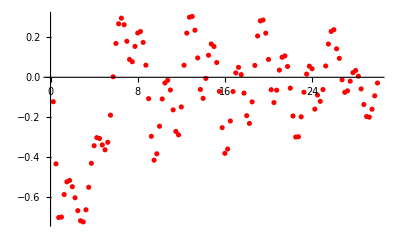

{{0.25,{-0.122168,-5.43425×10^-13}},{0.5,{-0.433269,9.99315×10^-16}},{0.75,{-0.702284,-3.07336×10^-16}},{1.,{-0.69977,4.87062×10^-16}},{1.25,{-0.587083,-3.0626×10^-16}},{1.5,{-0.523354,1.15047×10^-15}},{1.75,{-0.51646,-3.35646×10^-17}},{2.,{-0.547839,-6.63543×10^-16}},{2.25,{-0.603242,2.00161×10^-8}},{2.5,{-0.66782,1.7773×10^-15}},{2.75,{-0.718517,3.34586×10^-12}},{3.,{-0.724064,-6.88186×10^-15}},{3.25,{-0.663259,-1.17177×10^-9}},{3.5,{-0.550673,-1.74101×10^-9}},{3.75,{-0.430715,-2.19059×10^-15}},{4.,{-0.342644,2.47379×10^-15}},{4.25,{-0.302196,-1.44228×10^-9}},{4.5,{-0.306396,-1.0655×10^-15}},{4.75,{-0.338486,5.41135×10^-11}},{5.,{-0.363142,4.03847×10^-10}},{5.25,{-0.325429,1.81744×10^-10}},{5.5,{-0.189674,9.39624×10^-10}},{5.75,{0.00262939,-1.01139×10^-7}},{6.,{0.169439,1.01481×10^-15}},{6.25,{0.267891,-2.39043×10^-8}},{6.5,{0.296191,-2.48301×10^-8}},{6.75,{0.263124,2.18659×10^-14}},{7.,{0.180385,-3.60225×10^-8}},{7.25,{0.0893839,-3.12846×10^-8}},{7.5,{0.0777963,1.25704×10^-6}},{7.75,{0.154755,2.58555×10^-8}},{8.,{0.221865,-4.70241×10^-9}},{8.25,{0.229123,-6.24069×10^-8}},{8.5,{0.174458,5.12754×10^-8}},{8.75,{0.0607128,4.97955×10^-7}},{9.,{-0.106993,-7.92895×10^-8}},{9.25,{-0.295533,2.23649×10^-7}},{9.5,{-0.414968,-7.65022×10^-8}},{9.75,{-0.382995,8.72175×10^-15}},{10.,{-0.245146,1.98262×10^-7}},{10.25,{-0.108504,-2.24108×10^-8}},{10.5,{-0.0284065,6.0578×10^-8}},{10.75,{-0.014643,1.68657×10^-7}},{11.,{-0.06356,4.20699×10^-7}},{11.25,{-0.163241,-3.79215×10^-7}},{11.5,{-0.27097,4.52054×10^-7}},{11.75,{-0.288288,1.69606×10^-7}},{12.,{-0.148453,-3.6735×10^-7}},{12.25,{0.0603374,3.02586×10^-7}},{12.5,{0.221217,-3.97809×10^-7}},{12.75,{0.30092,5.43214×10^-7}},{13.,{0.304644,3.60573×10^-7}},{13.25,{0.235691,-2.16544×10^-7}},{13.5,{0.0969914,-6.10551×10^-7}},{13.75,{-0.0609389,-1.12038×10^-6}},{14.,{-0.105482,-8.8359×10^-7}},{14.25,{-0.00573355,1.47976×10^-6}},{14.5,{0.110443,7.63841×10^-7}},{14.75,{0.167017,-2.20592×10^-7}},{15.,{0.154219,1.96275×10^-6}},{15.25,{0.0739533,2.22479×10^-6}},{15.5,{-0.0707555,-1.44718×10^-6}},{15.75,{-0.252216,-3.58944×10^-7}},{16.,{-0.380974,-1.40102×10^-6}},{16.25,{-0.35912,9.38886×10^-7}},{16.5,{-0.218961,3.67424×10^-6}},{16.75,{-0.0712968,1.67426×10^-6}},{17.,{0.022171,3.52862×10^-6}},{17.25,{0.0498297,2.68222×10^-6}},{17.5,{0.0133434,0.0000134282}},{17.75,{-0.0792223,2.40318×10^-6}},{18.,{-0.192089,9.57575×10^-6}},{18.25,{-0.231089,-9.02432×10^-6}},{18.5,{-0.123174,7.48356×10^-6}},{18.75,{0.0592999,0.0000286197}},{19.,{0.20685,3.66564×10^-6}},{19.25,{0.282574,7.94044×10^-6}},{19.5,{0.286734,-7.6555×10^-6}},{19.75,{0.220843,0.0000425713}},{20.,{0.089339,4.64303×10^-6}},{20.25,{-0.06217,-3.53125×10^-6}},{20.5,{-0.126557,-3.48014×10^-6}},{20.75,{-0.0645251,-0.0000203894}},{21.,{0.0358751,0.0000174531}},{21.25,{0.100209,-0.00262582}},{21.5,{0.107085,-0.0000671395}},{21.75,{0.054084,-0.000150499}},{22.,{-0.0543491,-7.18737×10^-6}},{22.25,{-0.193904,-0.0000108652}},{22.5,{-0.299165,-0.000110569}},{22.75,{-0.297593,0.0000286221}},{23.,{-0.197828,-2.49719×10^-8}},{23.25,{-0.0747274,0.000021497}},{23.5,{0.0159951,-0.0000997909}},{23.75,{0.055626,3.53613×10^-6}},{24.,{0.0426782,-9.68366×10^-6}},{24.25,{-0.159318,0.000139833}},{24.5,{-0.0891066,-0.0000714635}},{24.75,{-0.120363,0.000147204}},{25.,{-0.0613286,0.0000292314}},{25.25,{0.0567004,-4.87826×10^-6}},{25.5,{0.166495,4.55455×10^-6}},{25.75,{0.229677,-0.0000364273}},{26.,{0.238246,-0.000210646}},{26.25,{0.142754,-0.0000404091}},{26.5,{0.0948007,-0.000212815}},{26.75,{-0.0124211,0.000236133}},{27.,{-0.0752429,-0.0000844332}},{27.25,{-0.0679062,0.000044638}},{27.5,{-0.0195857,9.89555×10^-6}},{27.75,{0.0230603,-3.66417×10^-6}},{28.,{0.0341255,0.0000783756}},{28.25,{0.00562327,0.0000264257}},{28.5,{-0.0581408,-0.000241112}},{28.75,{-0.136243,-0.000212497}},{29.,{-0.196246,-6.21716×10^-6}},{29.25,{-0.199551,0.0000560415}},{29.5,{-0.159835,-0.00101007}},{29.75,{-0.0928206,-0.0000403232}},{30.,{-0.0287394,-0.0000537619}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$104491535 near {ϕ$104491535} = {2.3561}. NIntegrate obtained 4.07228×10^-15 and 3.82292×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$104622389 near {ϕ$104622389} = {1.93885}. NIntegrate obtained -1.56584×10^-15 and 1.97421×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$104687807 near {ϕ$104687807} = {3.90235}. NIntegrate obtained 7.15494×10^-11 and 5.05316×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

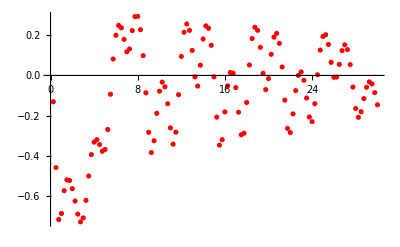

{{0.25,{-0.130787,1.74089×10^-13}},{0.5,{-0.457628,-3.97861×10^-13}},{0.75,{-0.715476,4.90115×10^-8}},{1.,{-0.685382,-6.80279×10^-11}},{1.25,{-0.572123,-1.6666×10^-10}},{1.5,{-0.518672,-1.01727×10^-11}},{1.75,{-0.521945,-2.9316×10^-16}},{2.,{-0.562085,7.55598×10^-16}},{2.25,{-0.623764,3.18944×10^-16}},{2.5,{-0.688417,2.96531×10^-16}},{2.75,{-0.727159,1.99068×10^-16}},{3.,{-0.707429,-1.43788×10^-10}},{3.25,{-0.620498,2.42882×10^-9}},{3.5,{-0.499442,6.98804×10^-16}},{3.75,{-0.393143,2.63263×10^-15}},{4.,{-0.331206,-8.6143×10^-10}},{4.25,{-0.318613,-1.14362×10^-9}},{4.5,{-0.343428,-2.90323×10^-16}},{4.75,{-0.37659,-9.27032×10^-10}},{5.,{-0.367647,2.04125×10^-9}},{5.25,{-0.268419,-1.08869×10^-6}},{5.5,{-0.0934546,1.22591×10^-8}},{5.75,{0.0814671,1.81362×10^-8}},{6.,{0.19921,-3.10506×10^-8}},{6.25,{0.248081,5.87289×10^-7}},{6.5,{0.236202,-4.46829×10^-8}},{6.75,{0.178719,1.59173×10^-9}},{7.,{0.117198,2.80452×10^-8}},{7.25,{0.13107,3.40129×10^-8}},{7.5,{0.222593,5.10992×10^-8}},{7.75,{0.291849,5.84066×10^-8}},{8.,{0.292672,9.33547×10^-8}},{8.25,{0.2271,-8.92038×10^-8}},{8.5,{0.0984852,9.14138×10^-6}},{8.75,{-0.0863055,-1.85419×10^-7}},{9.,{-0.282337,3.29729×10^-8}},{9.25,{-0.382759,6.11465×10^-8}},{9.5,{-0.324197,1.39225×10^-8}},{9.75,{-0.1883,-8.56666×10^-8}},{10.,{-0.0784167,-1.59323×10^-7}},{10.25,{-0.033414,-1.76004×10^-7}},{10.5,{-0.0565226,-1.60393×10^-7}},{10.75,{-0.140681,4.18351×10^-7}},{11.,{-0.260378,-6.11361×10^-7}},{11.25,{-0.341125,1.17905×10^-7}},{11.5,{-0.281761,3.94542×10^-8}},{11.75,{-0.0955146,-6.64579×10^-8}},{12.,{0.0943287,-2.63084×10^-7}},{12.25,{0.214248,6.13115×10^-7}},{12.5,{0.255387,7.33005×10^-7}},{12.75,{0.22356,-8.42683×10^-7}},{13.,{0.123855,-9.13031×10^-6}},{13.25,{-0.0076568,1.7637×10^-7}},{13.5,{-0.0529876,7.77383×10^-7}},{13.75,{0.0508357,-1.06422×10^-8}},{14.,{0.18097,-5.30635×10^-7}},{14.25,{0.245882,4.33909×10^-7}},{14.5,{0.234405,1.89291×10^-6}},{14.75,{0.149461,2.79164×10^-7}},{15.,{-0.00742119,-2.5168×10^-6}},{15.25,{-0.207105,9.18366×10^-7}},{15.5,{-0.345924,4.43906×10^-7}},{15.75,{-0.318952,-8.44325×10^-7}},{16.,{-0.181039,-1.78656×10^-6}},{16.25,{-0.0518412,-4.07014×10^-6}},{16.5,{0.0145344,-3.97017×10^-6}},{16.75,{0.0106226,4.57951×10^-6}},{17.,{-0.060413,-1.21817×10^-6}},{17.25,{-0.182738,-0.0000217331}},{17.5,{-0.294575,-1.23708×10^-6}},{17.75,{-0.286787,5.64626×10^-6}},{18.,{-0.134338,9.89383×10^-6}},{18.25,{0.0518064,0.0000113165}},{18.5,{0.182874,0.0000170322}},{18.75,{0.239342,-1.00054×10^-7}},{19.,{0.22375,0.0000112496}},{19.25,{0.139329,0.0000274436}},{19.5,{0.0103332,-7.39448×10^-6}},{19.75,{-0.0705998,-0.0000153271}},{20.,{-0.0158752,-0.0000574482}},{20.25,{0.104728,0.0000483249}},{20.5,{0.189927,1.63671×10^-6}},{20.75,{0.20873,1.50481×10^-6}},{21.,{0.15885,-1.18375×10^-6}},{21.25,{0.0417995,4.05425×10^-6}},{21.5,{-0.122824,-0.0000119403}},{21.75,{-0.26294,-0.0000190084}},{22.,{-0.283772,0.000067575}},{22.25,{-0.190852,5.05662×10^-6}},{22.5,{-0.0753635,-5.40009×10^-6}},{22.75,{0.000114297,-0.0000122781}},{23.,{0.0173649,0.0000366354}},{23.25,{-0.0241036,0.0000171387}},{23.5,{-0.112343,-3.67705×10^-6}},{23.75,{-0.206421,-4.3223×10^-6}},{24.,{-0.229584,7.36437×10^-6}},{24.25,{-0.140443,8.23275×10^-6}},{24.5,{0.00307116,-0.0000512297}},{24.75,{0.125647,0.000114681}},{25.,{0.193319,0.000504226}},{25.25,{0.201965,-0.00289999}},{25.5,{0.153621,0.0004775}},{25.75,{0.06492,-0.000041143}},{26.,{-0.00920898,-0.000103114}},{26.25,{-0.00849054,-0.000104117}},{26.5,{0.0547099,-0.000014827}},{26.75,{0.122964,-9.79379×10^-6}},{27.,{0.151999,0.000371579}},{27.25,{0.128112,0.0000918127}},{27.5,{0.0535697,0.0000100865}},{27.75,{-0.0578716,-0.0000114216}},{28.,{-0.163887,-0.0000376431}},{28.25,{-0.208089,0.0000183794}},{28.5,{-0.180299,0.00013484}},{28.75,{-0.114979,-0.0000244651}},{29.,{-0.0590243,-0.0000819696}},{29.25,{-0.0320369,-4.46058×10^-6}},{29.5,{-0.0423139,0.0000775343}},{29.75,{-0.0854732,-0.0000590566}},{30.,{-0.14591,-4.59721×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$112060403 near {ϕ$112060403} = {5.22771}. NIntegrate obtained 1.01512×10^-15 and 4.48844×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$112160589 near {ϕ$112160589} = {5.06817}. NIntegrate obtained 1.94897×10^-16 and 2.25095×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$112244867 near {ϕ$112244867} = {1.16573}. NIntegrate obtained -2.25311×10^-19 and 2.99708×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

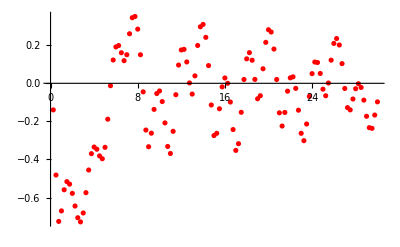

{{0.25,{-0.139658,5.0001×10^-14}},{0.5,{-0.481692,5.73897×10^-14}},{0.75,{-0.725086,-1.74337×10^-16}},{1.,{-0.66989,-6.77793×10^-10}},{1.25,{-0.559071,-1.86347×10^-8}},{1.5,{-0.516204,4.84141×10^-16}},{1.75,{-0.529366,-3.83467×10^-16}},{2.,{-0.577784,1.50179×10^-8}},{2.25,{-0.644378,-2.08099×10^-15}},{2.5,{-0.705794,-3.67544×10^-10}},{2.75,{-0.727676,2.46104×10^-15}},{3.,{-0.680861,3.01162×10^-10}},{3.25,{-0.574172,-1.26858×10^-10}},{3.5,{-0.455225,3.43451×10^-9}},{3.75,{-0.369391,-1.90946×10^-15}},{4.,{-0.334658,2.96648×10^-10}},{4.25,{-0.346071,1.90488×10^-10}},{4.5,{-0.381111,-6.5543×10^-10}},{4.75,{-0.39606,2.52987×10^-10}},{5.,{-0.336155,2.05795×10^-9}},{5.25,{-0.188384,7.79945×10^-9}},{5.5,{-0.0126526,-6.39953×10^-15}},{5.75,{0.122224,-6.37615×10^-7}},{6.,{0.191021,-1.21001×10^-8}},{6.25,{0.198201,7.68706×10^-9}},{6.5,{0.160423,-4.52113×10^-8}},{6.75,{0.118912,-1.54942×10^-8}},{7.,{0.150098,-1.12137×10^-8}},{7.25,{0.260192,-1.38174×10^-8}},{7.5,{0.344353,1.81605×10^-8}},{7.75,{0.35099,4.45347×10^-8}},{8.,{0.284492,7.40444×10^-8}},{8.25,{0.149899,3.99062×10^-6}},{8.5,{-0.0447231,7.0568×10^-8}},{8.75,{-0.245434,-1.46584×10^-8}},{9.,{-0.332964,6.01715×10^-7}},{9.25,{-0.261914,-6.3002×10^-8}},{9.5,{-0.136923,-8.07732×10^-8}},{9.75,{-0.0537249,-3.76336×10^-8}},{10.,{-0.040207,-6.2341×10^-8}},{10.25,{-0.0958569,4.91443×10^-8}},{10.5,{-0.207924,8.25358×10^-8}},{10.75,{-0.331582,1.0632×10^-7}},{11.,{-0.368556,5.74148×10^-8}},{11.25,{-0.252016,-1.47952×10^-7}},{11.5,{-0.0599012,1.68612×10^-7}},{11.75,{0.095878,-5.77642×10^-7}},{12.,{0.175121,2.91525×10^-8}},{12.25,{0.178274,-1.67762×10^-7}},{12.5,{0.11213,1.9525×10^-7}},{12.75,{0.00207443,-1.36568×10^-6}},{13.,{-0.0565546,3.27281×10^-7}},{13.25,{0.0390324,-1.29856×10^-6}},{13.5,{0.198704,1.92657×10^-7}},{13.75,{0.296856,-4.4696×10^-7}},{14.,{0.309252,-4.47285×10^-7}},{14.25,{0.241253,-4.30491×10^-7}},{14.5,{0.0931353,-3.23973×10^-7}},{14.75,{-0.113838,2.79415×10^-6}},{15.,{-0.274372,-0.0000246828}},{15.25,{-0.262556,1.78039×10^-6}},{15.5,{-0.133637,-1.70781×10^-7}},{15.75,{-0.0187336,9.60128×10^-9}},{16.,{0.0280244,-2.03119×10^-6}},{16.25,{8.53952×10^-6,3.13006×10^-7}},{16.5,{-0.0983015,1.21244×10^-6}},{16.75,{-0.242809,-1.00553×10^-6}},{17.,{-0.352333,-7.45343×10^-7}},{17.25,{-0.317045,3.82157×10^-6}},{17.5,{-0.152227,7.53555×10^-6}},{17.75,{0.0201057,0.0000300069}},{18.,{0.12854,-0.000011009}},{18.25,{0.161039,-0.0000821703}},{18.5,{0.121045,-0.0000851371}},{18.75,{0.0205866,0.0000229698}},{19.,{-0.0811549,0.0000117506}},{19.25,{-0.065242,-0.0000121985}},{19.5,{0.0763749,-0.0000182767}},{19.75,{0.214901,-0.0000113712}},{20.,{0.281376,0.0000100731}},{20.25,{0.269284,0.0000131759}},{20.5,{0.179944,1.10692×10^-6}},{20.75,{0.0199443,0.000028329}},{21.,{-0.154947,0.0000700922}},{21.25,{-0.224323,0.0000250571}},{21.5,{-0.152963,0.0000395042}},{21.75,{-0.0414052,3.82767×10^-6}},{22.,{0.0286371,0.000374197}},{22.25,{0.0338821,-1.92829×10^-6}},{22.5,{-0.0266989,-4.45971×10^-6}},{22.75,{-0.141275,0.0000189643}},{23.,{-0.262547,0.0000142254}},{23.25,{-0.301244,-0.0000643726}},{23.5,{-0.213732,0.0000156443}},{23.75,{-0.0688749,0.0000232669}},{24.,{0.0507697,0.000039741}},{24.25,{0.111718,-0.000227713}},{24.5,{0.109143,-4.34962×10^-6}},{24.75,{0.0517326,4.34296×10^-6}},{25.,{-0.0309208,0.000234201}},{25.25,{-0.0653674,0.00011529}},{25.5,{0.00159116,-0.0000234674}},{25.75,{0.121417,-0.000419952}},{26.,{0.209353,-0.00033822}},{26.25,{0.235008,0.000424128}},{26.5,{0.201169,-0.0000967301}},{26.75,{0.103351,-0.0000526098}},{27.,{-0.0270593,0.000132486}},{27.25,{-0.127693,-0.000250955}},{27.5,{-0.139492,-0.000117078}},{27.75,{-0.0824847,-0.00324192}},{28.,{-0.0285239,0.0261247}},{28.25,{-0.0022816,0.00168596}},{28.5,{-0.021811,0.000125701}},{28.75,{-0.0883259,0.00049519}},{29.,{-0.173158,0.000017761}},{29.25,{-0.232889,0.0000574173}},{29.5,{-0.236369,0.000931311}},{29.75,{-0.166669,-0.000468041}},{30.,{-0.0973988,-0.000125454}}}

```mathematica
Getv2kT[2.2]
Getv2kT[2.3]
Getv2kT[2.4]
Getv2kT[2.5]
Getv2kT[2.6]
Getv2kT[2.7]
Getv2kT[2.8]
Getv2kT[2.9]
Getv2kT[3.0]
```

### r = 2

```mathematica
v2kTr2={};
For[i=1,i≤120,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr2,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102101773 near {ϕ$102101773} = {0.638038}. NIntegrate obtained 2.2711×10^-14 and 5.01411×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102182398 near {ϕ$102182398} = {0.265405}. NIntegrate obtained 3.9576×10^-14 and 4.57269×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102270280 near {ϕ$102270280} = {3.86553}. NIntegrate obtained -1.98307×10^-13 and 6.86125×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
v2kTr2
```

{{0.25,{-0.0119878,4.02166×10^-15}},{0.5,{-0.0496732,3.74573×10^-14}},{0.75,{-0.114789,-6.03559×10^-13}},{1.,{-0.210431,2.61652×10^-12}},{1.25,{-0.342421,-5.93237×10^-11}},{1.5,{-0.497264,7.23566×10^-12}},{1.75,{-0.605292,1.42908×10^-9}},{2.,{-0.618239,-5.81003×10^-10}},{2.25,{-0.578195,2.59104×10^-9}},{2.5,{-0.526988,1.47112×10^-9}},{2.75,{-0.47516,1.02292×10^-10}},{3.,{-0.420273,1.03417×10^-8}},{3.25,{-0.356724,-3.05977×10^-9}},{3.5,{-0.277894,-2.47251×10^-11}},{3.75,{-0.176646,-2.85718×10^-10}},{4.,{-0.0478498,-1.51385×10^-10}},{4.25,{0.101504,-3.03453×10^-10}},{4.5,{0.228584,-4.39478×10^-8}},{4.75,{0.243768,1.80117×10^-10}},{5.,{0.0961155,-3.32592×10^-9}},{5.25,{-0.132316,-8.89064×10^-10}},{5.5,{-0.333077,-8.73848×10^-11}},{5.75,{-0.471218,-5.93729×10^-11}},{6.,{-0.55623,3.19914×10^-14}},{6.25,{-0.603832,-1.34332×10^-10}},{6.5,{-0.623691,8.20746×10^-9}},{6.75,{-0.616931,-9.21197×10^-9}},{7.,{-0.57304,-8.64402×10^-9}},{7.25,{-0.464894,1.09976×10^-9}},{7.5,{-0.270524,5.50331×10^-9}},{7.75,{-0.087889,-3.76231×10^-9}},{8.,{-0.068785,2.06293×10^-9}},{8.25,{-0.13856,2.46724×10^-8}},{8.5,{-0.197223,1.84117×10^-8}},{8.75,{-0.222123,-6.69793×10^-9}},{9.,{-0.21489,-6.14174×10^-8}},{9.25,{-0.178263,-2.05153×10^-9}},{9.5,{-0.113092,-1.16386×10^-8}},{9.75,{-0.0208926,-9.86587×10^-9}},{10.,{0.0905492,-4.21111×10^-9}},{10.25,{0.199981,-2.5641×10^-8}},{10.5,{0.272559,-2.52265×10^-8}},{10.75,{0.278405,1.94579×10^-8}},{11.,{0.217366,-1.3882×10^-8}},{11.25,{0.116993,-3.66937×10^-8}},{11.5,{0.00794649,-3.01615×10^-8}},{11.75,{-0.0913512,-1.59653×10^-8}},{12.,{-0.174075,-2.16859×10^-8}},{12.25,{-0.239213,-8.45132×10^-8}},{12.5,{-0.287072,-1.98294×10^-8}},{12.75,{-0.316903,3.54906×10^-9}},{13.,{-0.326601,-2.85156×10^-8}},{13.25,{-0.315083,-3.31133×10^-7}},{13.5,{-0.286127,-1.17954×10^-8}},{13.75,{-0.248234,2.31983×10^-8}},{14.,{-0.208734,-4.3891×10^-8}},{14.25,{-0.169846,-4.8988×10^-7}},{14.5,{-0.130176,6.18468×10^-8}},{14.75,{-0.0878411,1.65943×10^-8}},{15.,{-0.04255,3.99352×10^-8}},{15.25,{0.00346786,7.08839×10^-8}},{15.5,{0.045567,-1.39973×10^-7}},{15.75,{0.0783906,5.12505×10^-8}},{16.,{0.0985328,-7.63245×10^-8}},{16.25,{0.106391,2.01026×10^-7}},{16.5,{0.105642,-8.72217×10^-8}},{16.75,{0.100942,4.88131×10^-6}},{17.,{0.0958046,1.2716×10^-7}},{17.25,{0.0913727,-1.11393×10^-6}},{17.5,{0.0859113,3.63043×10^-7}},{17.75,{0.0745395,-3.76078×10^-7}},{18.,{0.0496753,1.80885×10^-7}},{18.25,{0.00373691,-3.88129×10^-8}},{18.5,{-0.0648744,-7.50463×10^-8}},{18.75,{-0.146353,1.67139×10^-7}},{19.,{-0.222339,-9.85581×10^-7}},{19.25,{-0.27634,2.97863×10^-7}},{19.5,{-0.30043,4.52614×10^-7}},{19.75,{-0.293831,-1.82976×10^-7}},{20.,{-0.258657,-5.80733×10^-9}},{20.25,{-0.197916,-3.56464×10^-8}},{20.5,{-0.117062,-3.83782×10^-7}},{20.75,{-0.0279783,-2.8993×10^-8}},{21.,{0.0491908,3.58877×10^-8}},{21.25,{0.0935946,-1.6138×10^-7}},{21.5,{0.0987642,-3.1807×10^-8}},{21.75,{0.0769813,1.13995×10^-7}},{22.,{0.0475234,-9.03808×10^-7}},{22.25,{0.0251863,-3.22207×10^-8}},{22.5,{0.0175256,6.44935×10^-7}},{22.75,{0.0272193,1.79738×10^-6}},{23.,{0.0540937,-2.06015×10^-7}},{23.25,{0.0950453,4.87947×10^-6}},{23.5,{0.142333,8.93671×10^-7}},{23.75,{0.180306,8.29001×10^-7}},{24.,{0.186197,1.46025×10^-7}},{24.25,{0.141413,-3.55586×10^-7}},{24.5,{0.0495847,5.6889×10^-7}},{24.75,{-0.0619166,-9.26983×10^-7}},{25.,{-0.162658,-3.79293×10^-6}},{25.25,{-0.235299,2.37719×10^-6}},{25.5,{-0.274696,-4.18792×10^-7}},{25.75,{-0.280743,7.07903×10^-7}},{26.,{-0.253748,2.287×10^-6}},{26.25,{-0.1942,-3.14581×10^-6}},{26.5,{-0.107542,5.70838×10^-6}},{26.75,{-0.0122859,0.0000242183}},{27.,{0.0595995,-5.06324×10^-6}},{27.25,{0.0839768,3.00352×10^-6}},{27.5,{0.0662111,5.9958×10^-6}},{27.75,{0.0308955,-7.05012×10^-7}},{28.,{-0.000362481,1.64796×10^-6}},{28.25,{-0.0162645,-4.67941×10^-6}},{28.5,{-0.0125308,-1.36032×10^-6}},{28.75,{0.0116251,1.92903×10^-6}},{29.,{0.0547089,3.63416×10^-7}},{29.25,{0.111579,1.70481×10^-6}},{29.5,{0.170334,-9.56754×10^-6}},{29.75,{0.21089,0.0000138153}},{30.,{0.211163,-2.29551×10^-6}}}

```mathematica
v2kTr2:={{0.25,{-0.011987824066760031,4.021660204770938*^-15}},{0.5,{-0.049673207241812956,3.7457278058170556*^-14}},{0.75,{-0.11478904521078691,-6.03559376280698*^-13}},{1.,{-0.21043098350362172,2.6165229794808745*^-12}},{1.25,{-0.3424213924636071,-5.932366905386802*^-11}},{1.5,{-0.4972644173674114,7.235656197835972*^-12}},{1.75,{-0.6052915303581592,1.429075244880441*^-9}},{2.,{-0.6182392496499612,-5.810031857827077*^-10}},{2.25,{-0.5781947006714055,2.591036488672839*^-9}},{2.5,{-0.5269875405595194,1.4711164766567721*^-9}},{2.75,{-0.47516016706781816,1.0229195109058451*^-10}},{3.,{-0.4202732582450019,1.0341700744266162*^-8}},{3.25,{-0.3567243229875822,-3.0597698867327406*^-9}},{3.5,{-0.2778941132463203,-2.4725129555075954*^-11}},{3.75,{-0.17664645052466302,-2.857184168460874*^-10}},{4.,{-0.04784975487476216,-1.5138502091204945*^-10}},{4.25,{0.10150396010825827,-3.034526798876663*^-10}},{4.5,{0.22858370821263108,-4.3947766735638886*^-8}},{4.75,{0.24376813124225763,1.8011667390216987*^-10}},{5.,{0.0961155046590976,-3.3259205346396855*^-9}},{5.25,{-0.1323163786505354,-8.890644432841953*^-10}},{5.5,{-0.3330770203432369,-8.738483812506843*^-11}},{5.75,{-0.4712182818271504,-5.937291443094876*^-11}},{6.,{-0.5562297130208246,3.19913796332455*^-14}},{6.25,{-0.6038322299731614,-1.343316362613863*^-10}},{6.5,{-0.6236907488011718,8.207461138109764*^-9}},{6.75,{-0.6169306558236888,-9.211967437549099*^-9}},{7.,{-0.5730402045432234,-8.644016844274223*^-9}},{7.25,{-0.46489414819364877,1.0997562851990259*^-9}},{7.5,{-0.2705239563846321,5.503309708162375*^-9}},{7.75,{-0.08788904708786317,-3.762312300738782*^-9}},{8.,{-0.06878499876237988,2.062934171328411*^-9}},{8.25,{-0.13855980875570828,2.4672428806698927*^-8}},{8.5,{-0.1972233342729097,1.8411741660851327*^-8}},{8.75,{-0.22212255068948256,-6.6979270358956116*^-9}},{9.,{-0.21488978872445233,-6.141738387451158*^-8}},{9.25,{-0.17826266524096887,-2.051531306447595*^-9}},{9.5,{-0.11309202110082736,-1.1638647567396398*^-8}},{9.75,{-0.020892587762830508,-9.865868821041999*^-9}},{10.,{0.09054919508087318,-4.2111091151572704*^-9}},{10.25,{0.19998117139037958,-2.5640980954645315*^-8}},{10.5,{0.27255893481872134,-2.5226475475485584*^-8}},{10.75,{0.2784054912830643,1.9457869988174764*^-8}},{11.,{0.21736551866818704,-1.3881977661241984*^-8}},{11.25,{0.11699320833341034,-3.669374258505795*^-8}},{11.5,{0.007946491096557571,-3.0161545891453254*^-8}},{11.75,{-0.09135122158518404,-1.5965272568449384*^-8}},{12.,{-0.1740747105500865,-2.1685916430472374*^-8}},{12.25,{-0.23921346247044006,-8.451316743334802*^-8}},{12.5,{-0.2870718920558613,-1.982937774962435*^-8}},{12.75,{-0.3169030155488351,3.5490647835805426*^-9}},{13.,{-0.32660082331163026,-2.8515596397540252*^-8}},{13.25,{-0.3150826770163598,-3.3113331079062216*^-7}},{13.5,{-0.2861269844674669,-1.1795391829366478*^-8}},{13.75,{-0.24823422412547339,2.3198299137986173*^-8}},{14.,{-0.20873437925488786,-4.389104128178838*^-8}},{14.25,{-0.16984608245571084,-4.89879500666019*^-7}},{14.5,{-0.13017560847174398,6.184682738605995*^-8}},{14.75,{-0.08784106737906038,1.6594349754732864*^-8}},{15.,{-0.04254995956358663,3.993520295392406*^-8}},{15.25,{0.0034678590094145696,7.088385296176046*^-8}},{15.5,{0.04556701897393032,-1.399729579663612*^-7}},{15.75,{0.07839062730020495,5.1250510564552584*^-8}},{16.,{0.0985327605168615,-7.632447693700044*^-8}},{16.25,{0.10639129959902074,2.0102555044861213*^-7}},{16.5,{0.10564208855686347,-8.722169067149654*^-8}},{16.75,{0.10094200603502346,4.881310529160645*^-6}},{17.,{0.09580462082990722,1.2715956523462664*^-7}},{17.25,{0.09137267296802175,-1.1139344097709211*^-6}},{17.5,{0.08591131235606088,3.630425420047259*^-7}},{17.75,{0.07453945791927896,-3.760776347009525*^-7}},{18.,{0.049675311727773105,1.8088544652417546*^-7}},{18.25,{0.0037369064960524213,-3.881291007818384*^-8}},{18.5,{-0.06487441839789523,-7.504634122237701*^-8}},{18.75,{-0.14635259854413163,1.6713926656929236*^-7}},{19.,{-0.2223394936121759,-9.855807890584442*^-7}},{19.25,{-0.2763404644149648,2.9786311794264595*^-7}},{19.5,{-0.3004303974514488,4.526143781771961*^-7}},{19.75,{-0.29383092258985205,-1.8297621045377837*^-7}},{20.,{-0.2586571861680565,-5.807329373674459*^-9}},{20.25,{-0.19791592732417773,-3.56464229241631*^-8}},{20.5,{-0.11706163713724087,-3.8378223592391937*^-7}},{20.75,{-0.027978338831833118,-2.8993007169538167*^-8}},{21.,{0.04919075632523607,3.5887682664500664*^-8}},{21.25,{0.09359462033980777,-1.6138011099817484*^-7}},{21.5,{0.09876418900096838,-3.1807042254158034*^-8}},{21.75,{0.07698132417821239,1.1399450959934535*^-7}},{22.,{0.04752343589987835,-9.03807550491679*^-7}},{22.25,{0.025186275402015297,-3.222073353158401*^-8}},{22.5,{0.017525581012597432,6.449353827038066*^-7}},{22.75,{0.027219256993020746,1.7973768565229199*^-6}},{23.,{0.054093742755611504,-2.0601498207439842*^-7}},{23.25,{0.09504526222913665,4.87946655466399*^-6}},{23.5,{0.14233277263985247,8.936711146175832*^-7}},{23.75,{0.1803055935157353,8.290006065109786*^-7}},{24.,{0.18619713545718108,1.4602462250928072*^-7}},{24.25,{0.14141327141879298,-3.555861578471053*^-7}},{24.5,{0.04958468403958911,5.688899246435387*^-7}},{24.75,{-0.06191660398742835,-9.269826118990355*^-7}},{25.,{-0.16265788629640243,-3.792930986029113*^-6}},{25.25,{-0.2352991707275503,2.3771936421729763*^-6}},{25.5,{-0.2746964410514922,-4.1879214842353814*^-7}},{25.75,{-0.2807425032978987,7.079031465806588*^-7}},{26.,{-0.2537479289747246,2.2870034183045297*^-6}},{26.25,{-0.19420002201416642,-3.1458065954475086*^-6}},{26.5,{-0.10754227412361007,5.7083808032143275*^-6}},{26.75,{-0.012285942907293974,0.000024218257661464282}},{27.,{0.05959945688628011,-5.063241915010969*^-6}},{27.25,{0.08397677527443981,3.003515512151491*^-6}},{27.5,{0.0662110869748594,5.995801804827665*^-6}},{27.75,{0.030895465767032455,-7.050118766113794*^-7}},{28.,{-0.00036248100895704556,1.6479617232993062*^-6}},{28.25,{-0.016264496121349538,-4.679407165003799*^-6}},{28.5,{-0.01253076882196341,-1.3603175297582572*^-6}},{28.75,{0.011625129787136656,1.9290280802050843*^-6}},{29.,{0.05470888192264921,3.634162647815335*^-7}},{29.25,{0.11157878799670498,1.7048071395391025*^-6}},{29.5,{0.1703340706645789,-9.567536440309049*^-6}},{29.75,{0.21088979262887256,0.00001381532986770998}},{30.,{0.21116272031491917,-2.2955058774012284*^-6}}}
```

```mathematica
v2kTr2={};
For[i=1,i≤240,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kTr2,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTr2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155450187 near {ϕ$155450187} = {2.57699}. NIntegrate obtained -8.09242×10^-13 and 1.0139×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155526302 near {ϕ$155526302} = {0.638038}. NIntegrate obtained 2.2711×10^-14 and 5.01411×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155606927 near {ϕ$155606927} = {4.23369}. NIntegrate obtained 1.77029×10^-14 and 2.20759×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.125,{-0.00293846,-3.22797×10^-14}},{0.25,{-0.0119878,4.02166×10^-15}},{0.375,{-0.0274896,8.06758×10^-15}},{0.5,{-0.0496732,3.74573×10^-14}},{0.625,{-0.0786963,4.28705×10^-14}},{0.75,{-0.114789,-6.03559×10^-13}},{0.875,{-0.158429,-6.17377×10^-17}},{1.,{-0.210431,2.61652×10^-12}},{1.125,{-0.271718,-1.06397×10^-12}},{1.25,{-0.342421,-5.93237×10^-11}},{1.375,{-0.420021,3.53641×10^-11}},{1.5,{-0.497264,7.23566×10^-12}},{1.625,{-0.562566,-7.13039×10^-9}},{1.75,{-0.605292,1.42908×10^-9}},{1.875,{-0.62223,-3.90179×10^-9}},{2.,{-0.618239,-5.81003×10^-10}},{2.125,{-0.601331,1.24109×10^-9}},{2.25,{-0.578195,2.59104×10^-9}},{2.375,{-0.552817,-3.57247×10^-11}},{2.5,{-0.526988,1.47112×10^-9}},{2.625,{-0.501173,3.04482×10^-9}},{2.75,{-0.47516,1.02292×10^-10}},{2.875,{-0.448418,-7.07705×10^-11}},{3.,{-0.420273,1.03417×10^-8}},{3.125,{-0.389976,1.79615×10^-8}},{3.25,{-0.356724,-3.05977×10^-9}},{3.375,{-0.319663,-4.44271×10^-11}},{3.5,{-0.277894,-2.47251×10^-11}},{3.625,{-0.230502,2.16695×10^-10}},{3.75,{-0.176646,-2.85718×10^-10}},{3.875,{-0.115746,2.7498×10^-12}},{4.,{-0.0478498,-1.51385×10^-10}},{4.125,{0.0257362,5.98577×10^-10}},{4.25,{0.101504,-3.03453×10^-10}},{4.375,{0.172664,1.71001×10^-10}},{4.5,{0.228584,-4.39478×10^-8}},{4.625,{0.256093,-1.35779×10^-10}},{4.75,{0.243768,1.80117×10^-10}},{4.875,{0.187961,2.44382×10^-10}},{5.,{0.0961155,-3.32592×10^-9}},{5.125,{-0.0161986,9.39926×10^-10}},{5.25,{-0.132316,-8.89064×10^-10}},{5.375,{-0.240029,1.53059×10^-9}},{5.5,{-0.333077,-8.73848×10^-11}},{5.625,{-0.409818,2.59413×10^-8}},{5.75,{-0.471218,-5.93729×10^-11}},{5.875,{-0.519297,-1.65977×10^-7}},{6.,{-0.55623,3.19914×10^-14}},{6.125,{-0.58392,-9.15752×10^-10}},{6.25,{-0.603832,-1.34332×10^-10}},{6.375,{-0.616939,-5.77897×10^-9}},{6.5,{-0.623691,8.20746×10^-9}},{6.625,{-0.623961,-9.89742×10^-9}},{6.75,{-0.616931,-9.21197×10^-9}},{6.875,{-0.600898,-5.27947×10^-10}},{7.,{-0.57304,-8.64402×10^-9}},{7.125,{-0.529286,-1.75417×10^-9}},{7.25,{-0.464894,1.09976×10^-9}},{7.375,{-0.376998,-3.81623×10^-9}},{7.5,{-0.270524,5.50331×10^-9}},{7.625,{-0.164605,-3.38064×10^-9}},{7.75,{-0.087889,-3.76231×10^-9}},{7.875,{-0.058007,-3.55694×10^-9}},{8.,{-0.068785,2.06293×10^-9}},{8.125,{-0.101157,1.31209×10^-9}},{8.25,{-0.13856,2.46724×10^-8}},{8.375,{-0.171809,-1.55624×10^-7}},{8.5,{-0.197223,1.84117×10^-8}},{8.625,{-0.213924,-1.32234×10^-8}},{8.75,{-0.222123,-6.69793×10^-9}},{8.875,{-0.2223,9.57063×10^-9}},{9.,{-0.21489,-6.14174×10^-8}},{9.125,{-0.200167,7.39934×10^-9}},{9.25,{-0.178263,-2.05153×10^-9}},{9.375,{-0.149237,4.9509×10^-9}},{9.5,{-0.113092,-1.16386×10^-8}},{9.625,{-0.070118,-3.76135×10^-9}},{9.75,{-0.0208926,-9.86587×10^-9}},{9.875,{0.0333654,-2.04069×10^-9}},{10.,{0.0905492,-4.21111×10^-9}},{10.125,{0.147491,-1.285×10^-8}},{10.25,{0.199981,-2.5641×10^-8}},{10.375,{0.243209,-8.28052×10^-9}},{10.5,{0.272559,-2.52265×10^-8}},{10.625,{0.284694,-2.42728×10^-8}},{10.75,{0.278405,1.94579×10^-8}},{10.875,{0.254908,-4.16011×10^-8}},{11.,{0.217366,-1.3882×10^-8}},{11.125,{0.169974,-9.59871×10^-9}},{11.25,{0.116993,-3.66937×10^-8}},{11.375,{0.062076,2.75005×10^-8}},{11.5,{0.00794649,-3.01615×10^-8}},{11.625,{-0.0435514,1.25449×10^-8}},{11.75,{-0.0913512,-1.59653×10^-8}},{11.875,{-0.134919,4.47874×10^-9}},{12.,{-0.174075,-2.16859×10^-8}},{12.125,{-0.208816,5.94535×10^-8}},{12.25,{-0.239213,-8.45132×10^-8}},{12.375,{-0.26531,3.69644×10^-8}},{12.5,{-0.287072,-1.98294×10^-8}},{12.625,{-0.304354,-8.21445×10^-7}},{12.75,{-0.316903,3.54906×10^-9}},{12.875,{-0.324407,-4.23101×10^-9}},{13.,{-0.326601,-2.85156×10^-8}},{13.125,{-0.323405,6.47479×10^-9}},{13.25,{-0.315083,-3.31133×10^-7}},{13.375,{-0.302306,-1.48647×10^-8}},{13.5,{-0.286127,-1.17954×10^-8}},{13.625,{-0.267735,3.28228×10^-8}},{13.75,{-0.248234,2.31983×10^-8}},{13.875,{-0.228432,-6.87637×10^-7}},{14.,{-0.208734,-4.3891×10^-8}},{14.125,{-0.189261,-4.57546×10^-8}},{14.25,{-0.169846,-4.8988×10^-7}},{14.375,{-0.150243,1.1607×10^-7}},{14.5,{-0.130176,6.18468×10^-8}},{14.625,{-0.109409,-1.70999×10^-8}},{14.75,{-0.0878411,1.65943×10^-8}},{14.875,{-0.0654788,-2.8936×10^-7}},{15.,{-0.04255,3.99352×10^-8}},{15.125,{-0.0193773,-1.14271×10^-7}},{15.25,{0.00346786,7.08839×10^-8}},{15.375,{0.0253547,1.15384×10^-7}},{15.5,{0.045567,-1.39973×10^-7}},{15.625,{0.0634293,2.49909×10^-7}},{15.75,{0.0783906,5.12505×10^-8}},{15.875,{0.0901181,-1.75114×10^-8}},{16.,{0.0985328,-7.63245×10^-8}},{16.125,{0.103822,3.03108×10^-7}},{16.25,{0.106391,2.01026×10^-7}},{16.375,{0.106796,-1.23426×10^-8}},{16.5,{0.105642,-8.72217×10^-8}},{16.625,{0.103523,-1.23856×10^-7}},{16.75,{0.100942,4.88131×10^-6}},{16.875,{0.0982963,-1.11533×10^-7}},{17.,{0.0958046,1.2716×10^-7}},{17.125,{0.0935357,-4.97007×10^-8}},{17.25,{0.0913727,-1.11393×10^-6}},{17.375,{0.0890004,-2.21538×10^-7}},{17.5,{0.0859113,3.63043×10^-7}},{17.625,{0.0813924,6.56037×10^-8}},{17.75,{0.0745395,-3.76078×10^-7}},{17.875,{0.0643234,-9.3084×10^-8}},{18.,{0.0496753,1.80885×10^-7}},{18.125,{0.0296671,-1.62992×10^-7}},{18.25,{0.00373691,-3.88129×10^-8}},{18.375,{-0.0280447,-5.57077×10^-7}},{18.5,{-0.0648744,-7.50463×10^-8}},{18.625,{-0.105059,1.05725×10^-7}},{18.75,{-0.146353,1.67139×10^-7}},{18.875,{-0.186234,-2.95609×10^-7}},{19.,{-0.222339,-9.85581×10^-7}},{19.125,{-0.252803,-1.28795×10^-7}},{19.25,{-0.27634,2.97863×10^-7}},{19.375,{-0.292282,-1.51723×10^-7}},{19.5,{-0.30043,4.52614×10^-7}},{19.625,{-0.30086,-5.61182×10^-9}},{19.75,{-0.293831,-1.82976×10^-7}},{19.875,{-0.27965,7.56013×10^-8}},{20.,{-0.258657,-5.80733×10^-9}},{20.125,{-0.231244,4.68169×10^-7}},{20.25,{-0.197916,-3.56464×10^-8}},{20.375,{-0.159464,4.01358×10^-6}},{20.5,{-0.117062,-3.83782×10^-7}},{20.625,{-0.0724435,-1.7726×10^-7}},{20.75,{-0.0279783,-2.8993×10^-8}},{20.875,{0.0135613,-6.27892×10^-7}},{21.,{0.0491908,3.58877×10^-8}},{21.125,{0.0763669,7.78635×10^-8}},{21.25,{0.0935946,-1.6138×10^-7}},{21.375,{0.100664,3.68085×10^-7}},{21.5,{0.0987642,-3.1807×10^-8}},{21.625,{0.0900206,7.76105×10^-8}},{21.75,{0.0769813,1.13995×10^-7}},{21.875,{0.062108,8.71355×10^-7}},{22.,{0.0475234,-9.03808×10^-7}},{22.125,{0.0348625,-2.6805×10^-7}},{22.25,{0.0251863,-3.22207×10^-8}},{22.375,{0.0192761,8.66755×10^-7}},{22.5,{0.0175256,6.44935×10^-7}},{22.625,{0.0201537,-2.18465×10^-6}},{22.75,{0.0272193,1.79738×10^-6}},{22.875,{0.0386201,6.45531×10^-7}},{23.,{0.0540937,-2.06015×10^-7}},{23.125,{0.0731796,-3.11281×10^-7}},{23.25,{0.0950453,4.87947×10^-6}},{23.375,{0.118658,4.8467×10^-7}},{23.5,{0.142333,8.93671×10^-7}},{23.625,{0.163801,9.93536×10^-7}},{23.75,{0.180306,8.29001×10^-7}},{23.875,{0.188747,5.98951×10^-7}},{24.,{0.186197,1.46025×10^-7}},{24.125,{0.170598,-2.98305×10^-6}},{24.25,{0.141413,-3.55586×10^-7}},{24.375,{0.100039,5.0957×10^-8}},{24.5,{0.0495847,5.6889×10^-7}},{24.625,{-0.00581629,-5.51953×10^-7}},{24.75,{-0.0619166,-9.26983×10^-7}},{24.875,{-0.115076,-3.58317×10^-6}},{25.,{-0.162658,-3.79293×10^-6}},{25.125,{-0.20301,1.00166×10^-6}},{25.25,{-0.235299,2.37719×10^-6}},{25.375,{-0.2592,-2.61543×10^-6}},{25.5,{-0.274696,-4.18792×10^-7}},{25.625,{-0.28185,-8.15799×10^-7}},{25.75,{-0.280743,7.07903×10^-7}},{25.875,{-0.271374,2.55686×10^-6}},{26.,{-0.253748,2.287×10^-6}},{26.125,{-0.227906,-2.63723×10^-6}},{26.25,{-0.1942,-3.14581×10^-6}},{26.375,{-0.153499,1.15036×10^-6}},{26.5,{-0.107542,5.70838×10^-6}},{26.625,{-0.0591728,-2.80712×10^-6}},{26.75,{-0.0122859,0.0000242183}},{26.875,{0.0286373,-2.13003×10^-6}},{27.,{0.0595995,-5.06324×10^-6}},{27.125,{0.0781301,-1.24174×10^-8}},{27.25,{0.0839768,3.00352×10^-6}},{27.375,{0.0789721,8.25448×10^-7}},{27.5,{0.0662111,5.9958×10^-6}},{27.625,{0.0491569,5.96917×10^-7}},{27.75,{0.0308955,-7.05012×10^-7}},{27.875,{0.0138322,-3.94388×10^-7}},{28.,{-0.000362481,1.64796×10^-6}},{28.125,{-0.0106083,-3.35565×10^-6}},{28.25,{-0.0162645,-4.67941×10^-6}},{28.375,{-0.0169503,-2.87284×10^-6}},{28.5,{-0.0125308,-1.36032×10^-6}},{28.625,{-0.00296676,-2.84631×10^-6}},{28.75,{0.0116251,1.92903×10^-6}},{28.875,{0.0310039,-4.83206×10^-6}},{29.,{0.0547089,3.63416×10^-7}},{29.125,{0.0819674,1.19561×10^-6}},{29.25,{0.111579,1.70481×10^-6}},{29.375,{0.141809,2.83452×10^-6}},{29.5,{0.170334,-9.56754×10^-6}},{29.625,{0.194361,-0.0000101693}},{29.75,{0.21089,0.0000138153}},{29.875,{0.217129,2.58088×10^-6}},{30.,{0.211163,-2.29551×10^-6}}}

```mathematica
v4kTr2={};
For[i=1,i≤240,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v4kTr2,{kT,showdσHZ[4,bu,x1u,x3u,kT,False]}];
]
v4kTr2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52117891 near {ϕ$52117891} = {2.57699}. NIntegrate obtained -2.13696×10^-10 and 5.71811×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52160550 near {ϕ$52160550} = {0.638038}. NIntegrate obtained -1.81144×10^-10 and 1.68133×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52222889 near {ϕ$52222889} = {4.23369}. NIntegrate obtained 7.62309×10^-12 and 9.60949×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.125,{-2.85485×10^-6,-8.52408×10^-12}},{0.25,{-0.0000450366,-3.20769×10^-11}},{0.375,{-0.000221186,3.47401×10^-12}},{0.5,{-0.000664018,4.63623×10^-11}},{0.625,{-0.00149749,-3.71232×10^-12}},{0.75,{-0.00275896,-1.02562×10^-10}},{0.875,{-0.00428093,-5.39724×10^-10}},{1.,{-0.00552405,-1.29011×10^-10}},{1.125,{-0.00537823,6.15613×10^-10}},{1.25,{-0.00204371,9.43163×10^-11}},{1.375,{0.00669274,1.98422×10^-7}},{1.5,{0.0223494,2.79419×10^-10}},{1.625,{0.0440204,8.89417×10^-9}},{1.75,{0.0677111,3.07586×10^-9}},{1.875,{0.0882886,-1.03954×10^-8}},{2.,{0.102348,-1.71107×10^-8}},{2.125,{0.109145,-1.31702×10^-8}},{2.25,{0.109629,-1.74448×10^-9}},{2.375,{0.105211,1.49349×10^-11}},{2.5,{0.0971168,1.09717×10^-8}},{2.625,{0.0862055,-1.21584×10^-8}},{2.75,{0.073006,-4.48841×10^-9}},{2.875,{0.0578014,-3.0746×10^-9}},{3.,{0.0407041,-3.25519×10^-9}},{3.125,{0.0217148,-2.06561×10^-8}},{3.25,{0.000765831,2.77696×10^-9}},{3.375,{-0.0222386,1.63192×10^-9}},{3.5,{-0.0473775,9.4894×10^-10}},{3.625,{-0.0746471,-3.48448×10^-9}},{3.75,{-0.103857,-6.8535×10^-9}},{3.875,{-0.134467,-1.80264×10^-7}},{4.,{-0.165318,-3.99831×10^-9}},{4.125,{-0.194299,1.02074×10^-8}},{4.25,{-0.21793,2.07803×10^-9}},{4.375,{-0.23112,7.48883×10^-8}},{4.5,{-0.227661,-1.14302×10^-11}},{4.625,{-0.201862,1.76342×10^-10}},{4.75,{-0.1516,1.02072×10^-7}},{4.875,{-0.0808679,9.90756×10^-8}},{5.,{0.000583918,2.81542×10^-7}},{5.125,{0.0811611,6.47374×10^-7}},{5.25,{0.151896,2.05625×10^-7}},{5.375,{0.208415,8.25339×10^-7}},{5.5,{0.250256,-2.40155×10^-7}},{5.625,{0.279098,-1.04856×10^-6}},{5.75,{0.29735,-1.96877×10^-7}},{5.875,{0.307281,-2.28812×10^-7}},{6.,{0.310726,-7.02969×10^-8}},{6.125,{0.308994,-1.51287×10^-7}},{6.25,{0.302904,2.42607×10^-8}},{6.375,{0.292835,1.19271×10^-10}},{6.5,{0.278762,-1.5048×10^-7}},{6.625,{0.260265,-5.88314×10^-7}},{6.75,{0.236512,-1.68534×10^-8}},{6.875,{0.206252,1.65986×10^-9}},{7.,{0.167916,-2.69827×10^-7}},{7.125,{0.120037,-2.55269×10^-9}},{7.25,{0.0625055,2.75555×10^-9}},{7.375,{-0.000747953,-1.49312×10^-7}},{7.5,{-0.0581051,1.45156×10^-8}},{7.625,{-0.0903664,6.67833×10^-10}},{7.75,{-0.081687,-8.59465×10^-10}},{7.875,{-0.0345259,-5.57171×10^-9}},{8.,{0.0323104,4.22472×10^-9}},{8.125,{0.0998864,-1.11887×10^-10}},{8.25,{0.158304,7.83496×10^-8}},{8.375,{0.205201,1.15375×10^-7}},{8.5,{0.241689,-8.27709×10^-9}},{8.625,{0.269763,-2.57901×10^-8}},{8.75,{0.291242,-3.93728×10^-9}},{8.875,{0.307479,1.61628×10^-8}},{9.,{0.319344,-4.17552×10^-8}},{9.125,{0.327289,1.16495×10^-8}},{9.25,{0.331402,5.48166×10^-9}},{9.375,{0.331449,6.13137×10^-9}},{9.5,{0.326969,1.44425×10^-8}},{9.625,{0.317207,-9.36441×10^-9}},{9.75,{0.301305,-8.02574×10^-9}},{9.875,{0.278384,-2.55199×10^-9}},{10.,{0.247776,1.71242×10^-9}},{10.125,{0.209332,-1.24264×10^-9}},{10.25,{0.163782,-3.32728×10^-8}},{10.375,{0.112995,-1.29745×10^-8}},{10.5,{0.0599784,-5.46859×10^-8}},{10.625,{0.00849308,-5.39589×10^-8}},{10.75,{-0.0376634,2.65554×10^-8}},{10.875,{-0.0754489,-5.00155×10^-8}},{11.,{-0.103112,-2.36578×10^-8}},{11.125,{-0.120307,6.35693×10^-9}},{11.25,{-0.12782,-4.36091×10^-8}},{11.375,{-0.127139,3.9991×10^-8}},{11.5,{-0.119995,4.00072×10^-8}},{11.625,{-0.108177,8.7457×10^-8}},{11.75,{-0.0932949,6.24557×10^-8}},{11.875,{-0.0767878,-1.86222×10^-8}},{12.,{-0.0599607,-3.5111×10^-9}},{12.125,{-0.0440419,-3.11109×10^-9}},{12.25,{-0.0302684,-1.894×10^-8}},{12.375,{-0.0199311,7.3616×10^-9}},{12.5,{-0.0144103,-7.07672×10^-9}},{12.625,{-0.0151231,-1.25445×10^-6}},{12.75,{-0.0233766,2.82846×10^-8}},{12.875,{-0.0400809,-4.05862×10^-8}},{13.,{-0.0653501,9.4619×10^-8}},{13.125,{-0.098075,-1.90543×10^-9}},{13.25,{-0.135671,-5.39956×10^-7}},{13.375,{-0.174255,4.00604×10^-9}},{13.5,{-0.209286,-5.23045×10^-8}},{13.625,{-0.236561,9.44492×10^-8}},{13.75,{-0.253018,-6.71973×10^-9}},{13.875,{-0.257164,-7.20463×10^-7}},{14.,{-0.248971,-1.18658×10^-7}},{14.125,{-0.229428,-9.9523×10^-8}},{14.25,{-0.200066,2.12356×10^-6}},{14.375,{-0.162664,6.22296×10^-8}},{14.5,{-0.118958,5.29122×10^-8}},{14.625,{-0.070635,9.55318×10^-8}},{14.75,{-0.0193636,-3.64719×10^-8}},{14.875,{0.0331884,9.74871×10^-8}},{15.,{0.0851992,8.90809×10^-8}},{15.125,{0.134759,-4.9939×10^-8}},{15.25,{0.179862,9.94328×10^-8}},{15.375,{0.218504,4.00037×10^-8}},{15.5,{0.248854,-5.41841×10^-8}},{15.625,{0.269491,3.24891×10^-7}},{15.75,{0.279568,2.33122×10^-9}},{15.875,{0.278985,-1.4113×10^-7}},{16.,{0.268382,-2.64682×10^-8}},{16.125,{0.249046,-2.12023×10^-8}},{16.25,{0.222737,3.52786×10^-7}},{16.375,{0.191439,-6.02944×10^-8}},{16.5,{0.157137,-1.78496×10^-7}},{16.625,{0.121669,-2.3468×10^-7}},{16.75,{0.0866101,-1.06003×10^-7}},{16.875,{0.0532612,-1.25425×10^-7}},{17.,{0.0226106,7.19376×10^-8}},{17.125,{-0.00457706,-1.895×10^-7}},{17.25,{-0.0277454,9.57698×10^-7}},{17.375,{-0.0465034,3.04128×10^-7}},{17.5,{-0.0606038,-2.07133×10^-7}},{17.625,{-0.0699399,2.89238×10^-7}},{17.75,{-0.0745806,4.22041×10^-7}},{17.875,{-0.0748195,-1.95125×10^-7}},{18.,{-0.0712405,4.2555×10^-7}},{18.125,{-0.0647779,-5.69349×10^-7}},{18.25,{-0.0567419,-4.64131×10^-7}},{18.375,{-0.0487354,-1.14177×10^-6}},{18.5,{-0.0424911,1.60729×10^-7}},{18.625,{-0.0395802,-1.85992×10^-8}},{18.75,{-0.04118,1.80544×10^-7}},{18.875,{-0.0478031,-1.31627×10^-7}},{19.,{-0.0593057,-1.62971×10^-6}},{19.125,{-0.0749776,2.527×10^-7}},{19.25,{-0.093713,2.80693×10^-7}},{19.375,{-0.114257,-1.52291×10^-7}},{19.5,{-0.135316,5.24508×10^-7}},{19.625,{-0.155652,-2.43212×10^-8}},{19.75,{-0.174134,-2.04276×10^-7}},{19.875,{-0.189627,6.81729×10^-8}},{20.,{-0.201043,-9.40917×10^-8}},{20.125,{-0.207248,-1.00115×10^-7}},{20.25,{-0.207075,-1.4198×10^-7}},{20.375,{-0.199379,4.27428×10^-6}},{20.5,{-0.183204,-2.29158×10^-8}},{20.625,{-0.157942,-5.34133×10^-8}},{20.75,{-0.123765,-3.21388×10^-8}},{20.875,{-0.0817937,-6.23656×10^-7}},{21.,{-0.0343156,7.77439×10^-8}},{21.125,{0.0153709,1.23221×10^-7}},{21.25,{0.063498,-8.60337×10^-8}},{21.375,{0.106541,1.47502×10^-6}},{21.5,{0.141857,9.09617×10^-7}},{21.625,{0.168086,2.46256×10^-7}},{21.75,{0.185077,1.47107×10^-7}},{21.875,{0.19358,8.65173×10^-7}},{22.,{0.194878,-1.53981×10^-6}},{22.125,{0.190409,-9.43184×10^-8}},{22.25,{0.181563,1.53773×10^-7}},{22.375,{0.169605,8.46484×10^-7}},{22.5,{0.155371,6.03813×10^-7}},{22.625,{0.139684,-2.86491×10^-6}},{22.75,{0.1231,2.41358×10^-6}},{22.875,{0.106047,9.13363×10^-7}},{23.,{0.0888365,-3.46162×10^-7}},{23.125,{0.0717272,2.45337×10^-7}},{23.25,{0.0549513,3.105×10^-6}},{23.375,{0.0386936,1.04204×10^-6}},{23.5,{0.0231844,1.37131×10^-6}},{23.625,{0.00868817,1.13243×10^-6}},{23.75,{-0.00451258,8.93203×10^-7}},{23.875,{-0.0161409,3.76845×10^-7}},{24.,{-0.0259902,7.16247×10^-7}},{24.125,{-0.0339823,5.67758×10^-6}},{24.25,{-0.0402507,-7.86809×10^-7}},{24.375,{-0.0451373,-2.45242×10^-7}},{24.5,{-0.0491461,1.14205×10^-6}},{24.625,{-0.0528488,-4.01555×10^-7}},{24.75,{-0.0567755,-1.15382×10^-6}},{24.875,{-0.0613441,-3.73939×10^-6}},{25.,{-0.0668336,-4.26591×10^-6}},{25.125,{-0.0733972,1.71526×10^-6}},{25.25,{-0.0810873,2.91196×10^-6}},{25.375,{-0.0898857,-3.00904×10^-6}},{25.5,{-0.0997012,4.10307×10^-7}},{25.625,{-0.110421,-2.81789×10^-6}},{25.75,{-0.121822,-3.949×10^-7}},{25.875,{-0.133599,-3.62332×10^-6}},{26.,{-0.145273,2.15266×10^-6}},{26.125,{-0.156171,-2.04762×10^-6}},{26.25,{-0.165331,3.19256×10^-6}},{26.375,{-0.171499,2.29946×10^-6}},{26.5,{-0.173192,7.05215×10^-6}},{26.625,{-0.168893,-2.65378×10^-7}},{26.75,{-0.157413,7.56049×10^-6}},{26.875,{-0.138361,-2.01444×10^-6}},{27.,{-0.112495,9.50151×10^-7}},{27.125,{-0.0816957,2.19213×10^-7}},{27.25,{-0.0485114,3.53741×10^-6}},{27.375,{-0.0155207,4.50645×10^-7}},{27.5,{0.0152386,6.11524×10^-6}},{27.625,{0.042547,5.57771×10^-7}},{27.75,{0.0658904,-1.00328×10^-6}},{27.875,{0.0853076,-8.92122×10^-7}},{28.,{0.10113,1.15939×10^-6}},{28.125,{0.113811,-3.17975×10^-7}},{28.25,{0.12378,-6.46399×10^-6}},{28.375,{0.131403,-3.97178×10^-6}},{28.5,{0.136954,-2.91748×10^-6}},{28.625,{0.140584,-3.88145×10^-6}},{28.75,{0.142314,2.41274×10^-6}},{28.875,{0.142071,-7.04328×10^-6}},{29.,{0.139676,-5.18286×10^-7}},{29.125,{0.134861,5.45208×10^-6}},{29.25,{0.127341,3.37941×10^-6}},{29.375,{0.116838,4.27324×10^-6}},{29.5,{0.103178,-0.0000115782}},{29.625,{0.0864132,-0.000013119}},{29.75,{0.0669134,7.63103×10^-6}},{29.875,{0.0454435,4.47403×10^-6}},{30.,{0.0231432,0.0211625}}}

{{0.125,{-2.85485×10^-6,-8.52408×10^-12}},{0.25,{-0.0000450366,-3.20769×10^-11}},{0.375,{-0.000221186,3.47401×10^-12}},{0.5,{-0.000664018,4.63623×10^-11}},{0.625,{-0.00149749,-3.71232×10^-12}},{0.75,{-0.00275896,-1.02562×10^-10}},{0.875,{-0.00428093,-5.39724×10^-10}},{1.,{-0.00552405,-1.29011×10^-10}},{1.125,{-0.00537823,6.15613×10^-10}},{1.25,{-0.00204371,9.43163×10^-11}},{1.375,{0.00669274,1.98422×10^-7}},{1.5,{0.0223494,2.79419×10^-10}},{1.625,{0.0440204,8.89417×10^-9}},{1.75,{0.0677111,3.07586×10^-9}},{1.875,{0.0882886,-1.03954×10^-8}},{2.,{0.102348,-1.71107×10^-8}},{2.125,{0.109145,-1.31702×10^-8}},{2.25,{0.109629,-1.74448×10^-9}},{2.375,{0.105211,1.49349×10^-11}},{2.5,{0.0971168,1.09717×10^-8}},{2.625,{0.0862055,-1.21584×10^-8}},{2.75,{0.073006,-4.48841×10^-9}},{2.875,{0.0578014,-3.0746×10^-9}},{3.,{0.0407041,-3.25519×10^-9}},{3.125,{0.0217148,-2.06561×10^-8}},{3.25,{0.000765831,2.77696×10^-9}},{3.375,{-0.0222386,1.63192×10^-9}},{3.5,{-0.0473775,9.4894×10^-10}},{3.625,{-0.0746471,-3.48448×10^-9}},{3.75,{-0.103857,-6.8535×10^-9}},{3.875,{-0.134467,-1.80264×10^-7}},{4.,{-0.165318,-3.99831×10^-9}},{4.125,{-0.194299,1.02074×10^-8}},{4.25,{-0.21793,2.07803×10^-9}},{4.375,{-0.23112,7.48883×10^-8}},{4.5,{-0.227661,-1.14302×10^-11}},{4.625,{-0.201862,1.76342×10^-10}},{4.75,{-0.1516,1.02072×10^-7}},{4.875,{-0.0808679,9.90756×10^-8}},{5.,{0.000583918,2.81542×10^-7}},{5.125,{0.0811611,6.47374×10^-7}},{5.25,{0.151896,2.05625×10^-7}},{5.375,{0.208415,8.25339×10^-7}},{5.5,{0.250256,-2.40155×10^-7}},{5.625,{0.279098,-1.04856×10^-6}},{5.75,{0.29735,-1.96877×10^-7}},{5.875,{0.307281,-2.28812×10^-7}},{6.,{0.310726,-7.02969×10^-8}},{6.125,{0.308994,-1.51287×10^-7}},{6.25,{0.302904,2.42607×10^-8}},{6.375,{0.292835,1.19271×10^-10}},{6.5,{0.278762,-1.5048×10^-7}},{6.625,{0.260265,-5.88314×10^-7}},{6.75,{0.236512,-1.68534×10^-8}},{6.875,{0.206252,1.65986×10^-9}},{7.,{0.167916,-2.69827×10^-7}},{7.125,{0.120037,-2.55269×10^-9}},{7.25,{0.0625055,2.75555×10^-9}},{7.375,{-0.000747953,-1.49312×10^-7}},{7.5,{-0.0581051,1.45156×10^-8}},{7.625,{-0.0903664,6.67833×10^-10}},{7.75,{-0.081687,-8.59465×10^-10}},{7.875,{-0.0345259,-5.57171×10^-9}},{8.,{0.0323104,4.22472×10^-9}},{8.125,{0.0998864,-1.11887×10^-10}},{8.25,{0.158304,7.83496×10^-8}},{8.375,{0.205201,1.15375×10^-7}},{8.5,{0.241689,-8.27709×10^-9}},{8.625,{0.269763,-2.57901×10^-8}},{8.75,{0.291242,-3.93728×10^-9}},{8.875,{0.307479,1.61628×10^-8}},{9.,{0.319344,-4.17552×10^-8}},{9.125,{0.327289,1.16495×10^-8}},{9.25,{0.331402,5.48166×10^-9}},{9.375,{0.331449,6.13137×10^-9}},{9.5,{0.326969,1.44425×10^-8}},{9.625,{0.317207,-9.36441×10^-9}},{9.75,{0.301305,-8.02574×10^-9}},{9.875,{0.278384,-2.55199×10^-9}},{10.,{0.247776,1.71242×10^-9}},{10.125,{0.209332,-1.24264×10^-9}},{10.25,{0.163782,-3.32728×10^-8}},{10.375,{0.112995,-1.29745×10^-8}},{10.5,{0.0599784,-5.46859×10^-8}},{10.625,{0.00849308,-5.39589×10^-8}},{10.75,{-0.0376634,2.65554×10^-8}},{10.875,{-0.0754489,-5.00155×10^-8}},{11.,{-0.103112,-2.36578×10^-8}},{11.125,{-0.120307,6.35693×10^-9}},{11.25,{-0.12782,-4.36091×10^-8}},{11.375,{-0.127139,3.9991×10^-8}},{11.5,{-0.119995,4.00072×10^-8}},{11.625,{-0.108177,8.7457×10^-8}},{11.75,{-0.0932949,6.24557×10^-8}},{11.875,{-0.0767878,-1.86222×10^-8}},{12.,{-0.0599607,-3.5111×10^-9}},{12.125,{-0.0440419,-3.11109×10^-9}},{12.25,{-0.0302684,-1.894×10^-8}},{12.375,{-0.0199311,7.3616×10^-9}},{12.5,{-0.0144103,-7.07672×10^-9}},{12.625,{-0.0151231,-1.25445×10^-6}},{12.75,{-0.0233766,2.82846×10^-8}},{12.875,{-0.0400809,-4.05862×10^-8}},{13.,{-0.0653501,9.4619×10^-8}},{13.125,{-0.098075,-1.90543×10^-9}},{13.25,{-0.135671,-5.39956×10^-7}},{13.375,{-0.174255,4.00604×10^-9}},{13.5,{-0.209286,-5.23045×10^-8}},{13.625,{-0.236561,9.44492×10^-8}},{13.75,{-0.253018,-6.71973×10^-9}},{13.875,{-0.257164,-7.20463×10^-7}},{14.,{-0.248971,-1.18658×10^-7}},{14.125,{-0.229428,-9.9523×10^-8}},{14.25,{-0.200066,2.12356×10^-6}},{14.375,{-0.162664,6.22296×10^-8}},{14.5,{-0.118958,5.29122×10^-8}},{14.625,{-0.070635,9.55318×10^-8}},{14.75,{-0.0193636,-3.64719×10^-8}},{14.875,{0.0331884,9.74871×10^-8}},{15.,{0.0851992,8.90809×10^-8}},{15.125,{0.134759,-4.9939×10^-8}},{15.25,{0.179862,9.94328×10^-8}},{15.375,{0.218504,4.00037×10^-8}},{15.5,{0.248854,-5.41841×10^-8}},{15.625,{0.269491,3.24891×10^-7}},{15.75,{0.279568,2.33122×10^-9}},{15.875,{0.278985,-1.4113×10^-7}},{16.,{0.268382,-2.64682×10^-8}},{16.125,{0.249046,-2.12023×10^-8}},{16.25,{0.222737,3.52786×10^-7}},{16.375,{0.191439,-6.02944×10^-8}},{16.5,{0.157137,-1.78496×10^-7}},{16.625,{0.121669,-2.3468×10^-7}},{16.75,{0.0866101,-1.06003×10^-7}},{16.875,{0.0532612,-1.25425×10^-7}},{17.,{0.0226106,7.19376×10^-8}},{17.125,{-0.00457706,-1.895×10^-7}},{17.25,{-0.0277454,9.57698×10^-7}},{17.375,{-0.0465034,3.04128×10^-7}},{17.5,{-0.0606038,-2.07133×10^-7}},{17.625,{-0.0699399,2.89238×10^-7}},{17.75,{-0.0745806,4.22041×10^-7}},{17.875,{-0.0748195,-1.95125×10^-7}},{18.,{-0.0712405,4.2555×10^-7}},{18.125,{-0.0647779,-5.69349×10^-7}},{18.25,{-0.0567419,-4.64131×10^-7}},{18.375,{-0.0487354,-1.14177×10^-6}},{18.5,{-0.0424911,1.60729×10^-7}},{18.625,{-0.0395802,-1.85992×10^-8}},{18.75,{-0.04118,1.80544×10^-7}},{18.875,{-0.0478031,-1.31627×10^-7}},{19.,{-0.0593057,-1.62971×10^-6}},{19.125,{-0.0749776,2.527×10^-7}},{19.25,{-0.093713,2.80693×10^-7}},{19.375,{-0.114257,-1.52291×10^-7}},{19.5,{-0.135316,5.24508×10^-7}},{19.625,{-0.155652,-2.43212×10^-8}},{19.75,{-0.174134,-2.04276×10^-7}},{19.875,{-0.189627,6.81729×10^-8}},{20.,{-0.201043,-9.40917×10^-8}},{20.125,{-0.207248,-1.00115×10^-7}},{20.25,{-0.207075,-1.4198×10^-7}},{20.375,{-0.199379,4.27428×10^-6}},{20.5,{-0.183204,-2.29158×10^-8}},{20.625,{-0.157942,-5.34133×10^-8}},{20.75,{-0.123765,-3.21388×10^-8}},{20.875,{-0.0817937,-6.23656×10^-7}},{21.,{-0.0343156,7.77439×10^-8}},{21.125,{0.0153709,1.23221×10^-7}},{21.25,{0.063498,-8.60337×10^-8}},{21.375,{0.106541,1.47502×10^-6}},{21.5,{0.141857,9.09617×10^-7}},{21.625,{0.168086,2.46256×10^-7}},{21.75,{0.185077,1.47107×10^-7}},{21.875,{0.19358,8.65173×10^-7}},{22.,{0.194878,-1.53981×10^-6}},{22.125,{0.190409,-9.43184×10^-8}},{22.25,{0.181563,1.53773×10^-7}},{22.375,{0.169605,8.46484×10^-7}},{22.5,{0.155371,6.03813×10^-7}},{22.625,{0.139684,-2.86491×10^-6}},{22.75,{0.1231,2.41358×10^-6}},{22.875,{0.106047,9.13363×10^-7}},{23.,{0.0888365,-3.46162×10^-7}},{23.125,{0.0717272,2.45337×10^-7}},{23.25,{0.0549513,3.105×10^-6}},{23.375,{0.0386936,1.04204×10^-6}},{23.5,{0.0231844,1.37131×10^-6}},{23.625,{0.00868817,1.13243×10^-6}},{23.75,{-0.00451258,8.93203×10^-7}},{23.875,{-0.0161409,3.76845×10^-7}},{24.,{-0.0259902,7.16247×10^-7}},{24.125,{-0.0339823,5.67758×10^-6}},{24.25,{-0.0402507,-7.86809×10^-7}},{24.375,{-0.0451373,-2.45242×10^-7}},{24.5,{-0.0491461,1.14205×10^-6}},{24.625,{-0.0528488,-4.01555×10^-7}},{24.75,{-0.0567755,-1.15382×10^-6}},{24.875,{-0.0613441,-3.73939×10^-6}},{25.,{-0.0668336,-4.26591×10^-6}},{25.125,{-0.0733972,1.71526×10^-6}},{25.25,{-0.0810873,2.91196×10^-6}},{25.375,{-0.0898857,-3.00904×10^-6}},{25.5,{-0.0997012,4.10307×10^-7}},{25.625,{-0.110421,-2.81789×10^-6}},{25.75,{-0.121822,-3.949×10^-7}},{25.875,{-0.133599,-3.62332×10^-6}},{26.,{-0.145273,2.15266×10^-6}},{26.125,{-0.156171,-2.04762×10^-6}},{26.25,{-0.165331,3.19256×10^-6}},{26.375,{-0.171499,2.29946×10^-6}},{26.5,{-0.173192,7.05215×10^-6}},{26.625,{-0.168893,-2.65378×10^-7}},{26.75,{-0.157413,7.56049×10^-6}},{26.875,{-0.138361,-2.01444×10^-6}},{27.,{-0.112495,9.50151×10^-7}},{27.125,{-0.0816957,2.19213×10^-7}},{27.25,{-0.0485114,3.53741×10^-6}},{27.375,{-0.0155207,4.50645×10^-7}},{27.5,{0.0152386,6.11524×10^-6}},{27.625,{0.042547,5.57771×10^-7}},{27.75,{0.0658904,-1.00328×10^-6}},{27.875,{0.0853076,-8.92122×10^-7}},{28.,{0.10113,1.15939×10^-6}},{28.125,{0.113811,-3.17975×10^-7}},{28.25,{0.12378,-6.46399×10^-6}},{28.375,{0.131403,-3.97178×10^-6}},{28.5,{0.136954,-2.91748×10^-6}},{28.625,{0.140584,-3.88145×10^-6}},{28.75,{0.142314,2.41274×10^-6}},{28.875,{0.142071,-7.04328×10^-6}},{29.,{0.139676,-5.18286×10^-7}},{29.125,{0.134861,5.45208×10^-6}},{29.25,{0.127341,3.37941×10^-6}},{29.375,{0.116838,4.27324×10^-6}},{29.5,{0.103178,-0.0000115782}},{29.625,{0.0864132,-0.000013119}},{29.75,{0.0669134,7.63103×10^-6}},{29.875,{0.0454435,4.47403×10^-6}},{30.,{0.0231432,0.0211625}}}

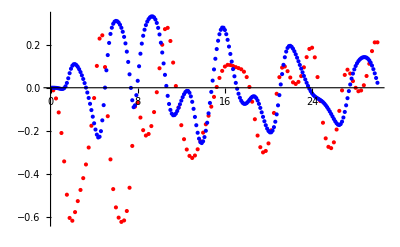

```mathematica
ListPlot[{Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}],Transpose[{v4kTr2[[All,1]],Re[v4kTr2[[All,2,1]]]}]},PlotStyle->{Red,Blue}]
```

### r = 5

```mathematica
30.0/480
30.0/120
```

0.0625

0.25

```mathematica
v2kTr5={};
For[i=1,i≤480,i++,
x1u=2.5{Cos[π/2],Sin[π/2]};
x3u=2.5{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.0625*i;
AppendTo[v2kTr5,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$649303 near {ϕ$649303} = {0.249129}. NIntegrate obtained -3.93108×10^-12 and 1.05508×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$714657 near {ϕ$714657} = {2.57699}. NIntegrate obtained -2.50466×10^-12 and 3.15885×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$831362 near {ϕ$831362} = {0.108422}. NIntegrate obtained 3.4606×10^-13 and 2.73128×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
v2kTr5
```

{{0.0625,{0.00187827,-9.51362×10^-15}},{0.125,{0.00760703,-2.67618×10^-14}},{0.1875,{0.0174372,9.51111×10^-15}},{0.25,{0.0317627,8.41119×10^-14}},{0.3125,{0.0511219,3.28446×10^-14}},{0.375,{0.0761706,-5.94262×10^-13}},{0.4375,{0.107581,7.85388×10^-11}},{0.5,{0.14577,-9.41796×10^-13}},{0.5625,{0.190244,-1.96997×10^-12}},{0.625,{0.238225,3.6539×10^-17}},{0.6875,{0.282049,-3.07091×10^-13}},{0.75,{0.305596,-1.51285×10^-17}},{0.8125,{0.283129,-1.53381×10^-17}},{0.875,{0.189818,-5.666×10^-11}},{0.9375,{0.0274249,4.04837×10^-11}},{1.,{-0.163272,7.34491×10^-11}},{1.0625,{-0.331837,-3.3843×10^-11}},{1.125,{-0.452666,-7.60882×10^-11}},{1.1875,{-0.52598,2.53209×10^-9}},{1.25,{-0.562288,4.92507×10^-10}},{1.3125,{-0.571986,-1.30245×10^-9}},{1.375,{-0.562199,-1.71808×10^-16}},{1.4375,{-0.536821,-3.14951×10^-9}},{1.5,{-0.497289,-6.71574×10^-11}},{1.5625,{-0.443338,-9.22537×10^-12}},{1.625,{-0.373762,-2.60605×10^-10}},{1.6875,{-0.287579,2.74041×10^-10}},{1.75,{-0.186291,-8.49469×10^-11}},{1.8125,{-0.0777898,1.55167×10^-10}},{1.875,{0.0195023,2.29757×10^-10}},{1.9375,{0.0783655,-4.49359×10^-10}},{2.,{0.0773342,-1.64166×10^-10}},{2.0625,{0.0187566,-8.98622×10^-11}},{2.125,{-0.0724729,-1.21091×10^-9}},{2.1875,{-0.168255,-5.85389×10^-10}},{2.25,{-0.251075,1.45093×10^-11}},{2.3125,{-0.314481,1.75115×10^-10}},{2.375,{-0.358256,-4.80258×10^-9}},{2.4375,{-0.384429,3.03976×10^-10}},{2.5,{-0.395254,3.81883×10^-10}},{2.5625,{-0.392444,3.74951×10^-10}},{2.625,{-0.376989,-2.69525×10^-10}},{2.6875,{-0.349206,-2.51423×10^-10}},{2.75,{-0.308901,-1.37342×10^-10}},{2.8125,{-0.255649,-2.52014×10^-11}},{2.875,{-0.189293,-4.70602×10^-10}},{2.9375,{-0.110816,-7.18403×10^-11}},{3.,{-0.0236993,1.95425×10^-10}},{3.0625,{0.0644434,-2.88426×10^-9}},{3.125,{0.141041,-6.96098×10^-10}},{3.1875,{0.190552,-1.47485×10^-11}},{3.25,{0.200449,1.93135×10^-10}},{3.3125,{0.168248,3.58822×10^-10}},{3.375,{0.10338,-2.39959×10^-10}},{3.4375,{0.0218681,7.49243×10^-10}},{3.5,{-0.0611226,5.09428×10^-10}},{3.5625,{-0.135393,4.46841×10^-9}},{3.625,{-0.195867,-1.41667×10^-8}},{3.6875,{-0.24094,-6.25595×10^-9}},{3.75,{-0.270776,1.10414×10^-9}},{3.8125,{-0.286148,1.15388×10^-8}},{3.875,{-0.287821,-1.75789×10^-10}},{3.9375,{-0.276295,1.17064×10^-8}},{4.,{-0.251758,1.79673×10^-9}},{4.0625,{-0.214244,1.87327×10^-8}},{4.125,{-0.163989,1.6091×10^-8}},{4.1875,{-0.102098,8.53151×10^-9}},{4.25,{-0.0316099,2.35721×10^-8}},{4.3125,{0.041168,-3.7559×10^-9}},{4.375,{0.105758,3.16583×10^-9}},{4.4375,{0.148546,7.49495×10^-9}},{4.5,{0.157117,6.90501×10^-9}},{4.5625,{0.126529,-1.80051×10^-9}},{4.625,{0.0626801,3.52274×10^-9}},{4.6875,{-0.0207116,1.93999×10^-9}},{4.75,{-0.108758,-8.43307×10^-9}},{4.8125,{-0.190374,9.22459×10^-9}},{4.875,{-0.259484,1.23699×10^-8}},{4.9375,{-0.313849,-2.05257×10^-10}},{5.,{-0.353388,-1.15135×10^-8}},{5.0625,{-0.378899,8.53182×10^-8}},{5.125,{-0.391295,-5.54729×10^-10}},{5.1875,{-0.39124,-1.44395×10^-7}},{5.25,{-0.379024,2.53651×10^-9}},{5.3125,{-0.354607,1.32153×10^-8}},{5.375,{-0.317854,-1.79843×10^-9}},{5.4375,{-0.26908,-1.31028×10^-9}},{5.5,{-0.210099,7.70365×10^-9}},{5.5625,{-0.145939,-6.7637×10^-8}},{5.625,{-0.0867771,1.2487×10^-8}},{5.6875,{-0.0482003,1.67998×10^-8}},{5.75,{-0.0465873,7.26623×10^-9}},{5.8125,{-0.0895031,1.75261×10^-9}},{5.875,{-0.169028,1.18715×10^-9}},{5.9375,{-0.2663,2.0838×10^-7}},{6.,{-0.362663,2.09513×10^-8}},{6.0625,{-0.446619,8.34036×10^-9}},{6.125,{-0.513901,1.29313×10^-8}},{6.1875,{-0.564584,1.25451×10^-8}},{6.25,{-0.600474,-3.1679×10^-9}},{6.3125,{-0.623626,1.12682×10^-9}},{6.375,{-0.635682,1.14761×10^-8}},{6.4375,{-0.637654,1.96286×10^-8}},{6.5,{-0.62986,-4.2979×10^-9}},{6.5625,{-0.611978,1.17417×10^-8}},{6.625,{-0.583109,2.27968×10^-8}},{6.6875,{-0.542099,2.28675×10^-8}},{6.75,{-0.488409,5.63667×10^-8}},{6.8125,{-0.424125,-2.74149×10^-8}},{6.875,{-0.357432,4.17674×10^-8}},{6.9375,{-0.305387,8.08985×10^-8}},{7.,{-0.289184,-6.67172×10^-8}},{7.0625,{-0.318627,1.51192×10^-8}},{7.125,{-0.381737,-1.02396×10^-7}},{7.1875,{-0.455392,1.04618×10^-7}},{7.25,{-0.521835,7.64579×10^-8}},{7.3125,{-0.57349,1.71289×10^-7}},{7.375,{-0.609383,4.78886×10^-8}},{7.4375,{-0.631047,-6.64748×10^-8}},{7.5,{-0.6403,-5.1716×10^-8}},{7.5625,{-0.638397,1.19885×10^-8}},{7.625,{-0.625782,-4.21869×10^-8}},{7.6875,{-0.602063,-7.44841×10^-8}},{7.75,{-0.566019,4.55654×10^-8}},{7.8125,{-0.515675,5.34983×10^-7}},{7.875,{-0.448576,4.04653×10^-8}},{7.9375,{-0.362585,6.28332×10^-8}},{8.,{-0.257714,-1.31628×10^-8}},{8.0625,{-0.139455,6.70561×10^-7}},{8.125,{-0.0225617,-1.10532×10^-8}},{8.1875,{0.0692356,3.34221×10^-8}},{8.25,{0.112899,5.68372×10^-8}},{8.3125,{0.101099,-1.34655×10^-7}},{8.375,{0.0468353,-1.06834×10^-7}},{8.4375,{-0.0273667,1.51254×10^-8}},{8.5,{-0.102276,-3.23151×10^-8}},{8.5625,{-0.166694,-3.62559×10^-8}},{8.625,{-0.215977,2.28577×10^-7}},{8.6875,{-0.249084,-2.68709×10^-8}},{8.75,{-0.266413,6.91737×10^-8}},{8.8125,{-0.268607,-1.61674×10^-7}},{8.875,{-0.256085,-1.27576×10^-7}},{8.9375,{-0.228849,6.78733×10^-7}},{9.,{-0.186599,1.23691×10^-7}},{9.0625,{-0.129026,-1.49048×10^-7}},{9.125,{-0.0564103,1.04988×10^-7}},{9.1875,{0.029428,2.87894×10^-7}},{9.25,{0.12381,4.18138×10^-8}},{9.3125,{0.217957,-7.40374×10^-8}},{9.375,{0.299059,-2.65237×10^-9}},{9.4375,{0.352996,-2.26628×10^-7}},{9.5,{0.369614,-2.05534×10^-8}},{9.5625,{0.34762,-1.16208×10^-7}},{9.625,{0.295081,5.10841×10^-7}},{9.6875,{0.225178,8.22645×10^-8}},{9.75,{0.150873,1.01352×10^-9}},{9.8125,{0.08178,9.58714×10^-8}},{9.875,{0.0235373,-2.90812×10^-8}},{9.9375,{-0.021084,-6.21208×10^-8}},{10.,{-0.0511262,2.63447×10^-8}},{10.0625,{-0.0664969,-1.2311×10^-7}},{10.125,{-0.0674301,-3.63156×10^-8}},{10.1875,{-0.0542186,8.38487×10^-8}},{10.25,{-0.0272118,4.93321×10^-8}},{10.3125,{0.0129751,-9.55377×10^-8}},{10.375,{0.0650376,-1.04906×10^-7}},{10.4375,{0.126346,1.1017×10^-7}},{10.5,{0.1922,-1.90066×10^-7}},{10.5625,{0.255323,5.71595×10^-8}},{10.625,{0.306266,6.38575×10^-8}},{10.6875,{0.335312,-4.74362×10^-7}},{10.75,{0.335683,1.09244×10^-7}},{10.8125,{0.306437,6.59557×10^-8}},{10.875,{0.252942,-2.73606×10^-7}},{10.9375,{0.184601,6.48994×10^-7}},{11.,{0.111415,-2.78091×10^-7}},{11.0625,{0.0414898,2.06296×10^-7}},{11.125,{-0.019832,5.38583×10^-7}},{11.1875,{-0.0696419,6.5949×10^-8}},{11.25,{-0.106695,8.61944×10^-8}},{11.3125,{-0.13069,-3.15132×10^-9}},{11.375,{-0.141765,-1.0746×10^-8}},{11.4375,{-0.140225,-2.19807×10^-7}},{11.5,{-0.126436,2.17923×10^-6}},{11.5625,{-0.101022,4.88562×10^-7}},{11.625,{-0.0651661,-2.07598×10^-7}},{11.6875,{-0.0211619,8.06874×10^-8}},{11.75,{0.0268852,8.10428×10^-8}},{11.8125,{0.0725271,-3.76482×10^-7}},{11.875,{0.107208,1.10769×10^-6}},{11.9375,{0.121975,-7.68585×10^-7}},{12.,{0.110585,-1.54395×10^-7}},{12.0625,{0.0724883,5.30302×10^-7}},{12.125,{0.0133273,-7.68792×10^-7}},{12.1875,{-0.0575062,2.68147×10^-7}},{12.25,{-0.130466,6.13348×10^-7}},{12.3125,{-0.198279,2.17777×10^-7}},{12.375,{-0.256589,4.45611×10^-7}},{12.4375,{-0.303384,9.93317×10^-8}},{12.5,{-0.338132,3.90246×10^-7}},{12.5625,{-0.361001,2.27016×10^-7}},{12.625,{-0.372385,-1.57246×10^-7}},{12.6875,{-0.372645,1.23348×10^-7}},{12.75,{-0.362062,7.54228×10^-8}},{12.8125,{-0.340961,-1.36595×10^-9}},{12.875,{-0.310009,5.0653×10^-8}},{12.9375,{-0.270787,1.70774×10^-8}},{13.,{-0.226551,4.07324×10^-7}},{13.0625,{-0.182839,-3.8907×10^-6}},{13.125,{-0.147388,6.44291×10^-7}},{13.1875,{-0.128373,5.01052×10^-8}},{13.25,{-0.131166,-2.26856×10^-7}},{13.3125,{-0.155578,1.43275×10^-7}},{13.375,{-0.195864,5.2168×10^-7}},{13.4375,{-0.243615,5.95385×10^-7}},{13.5,{-0.291043,-2.18392×10^-8}},{13.5625,{-0.332683,-3.26248×10^-7}},{13.625,{-0.365487,-8.03052×10^-7}},{13.6875,{-0.388097,-1.80646×10^-6}},{13.75,{-0.400087,-4.9776×10^-7}},{13.8125,{-0.40135,1.37062×10^-6}},{13.875,{-0.391856,1.12231×10^-7}},{13.9375,{-0.371474,-2.24651×10^-8}},{14.,{-0.340091,9.22968×10^-8}},{14.0625,{-0.297816,-6.17991×10^-7}},{14.125,{-0.245446,-7.11812×10^-7}},{14.1875,{-0.185053,-1.18272×10^-7}},{14.25,{-0.120659,-1.63587×10^-7}},{14.3125,{-0.0585481,-3.97185×10^-7}},{14.375,{-0.00651194,3.40895×10^-7}},{14.4375,{0.028136,-2.93386×10^-7}},{14.5,{0.0412312,-3.99208×10^-7}},{14.5625,{0.0334149,-2.68407×10^-6}},{14.625,{0.00958485,5.60763×10^-7}},{14.6875,{-0.0232547,1.37215×10^-6}},{14.75,{-0.0583227,-4.44815×10^-7}},{14.8125,{-0.0903262,7.7561×10^-7}},{14.875,{-0.115747,6.61899×10^-7}},{14.9375,{-0.132516,9.94378×10^-8}},{15.,{-0.139524,2.5557×10^-7}},{15.0625,{-0.136234,6.58642×10^-6}},{15.125,{-0.122467,1.03718×10^-8}},{15.1875,{-0.0983138,1.0716×10^-6}},{15.25,{-0.0641945,-3.03794×10^-6}},{15.3125,{-0.0210761,3.26524×10^-6}},{15.375,{0.0291489,2.88298×10^-6}},{15.4375,{0.0834496,4.57488×10^-6}},{15.5,{0.137453,8.34081×10^-6}},{15.5625,{0.185688,-0.0000176047}},{15.625,{0.22246,-0.0000157018}},{15.6875,{0.243193,-9.08277×10^-6}},{15.75,{0.245846,-5.62093×10^-7}},{15.8125,{0.231509,8.97303×10^-7}},{15.875,{0.203959,-4.48425×10^-7}},{15.9375,{0.168418,9.78586×10^-7}},{16.,{0.130237,7.32275×10^-7}},{16.0625,{0.0939205,8.92229×10^-7}},{16.125,{0.0628031,-5.51595×10^-7}},{16.1875,{0.0390792,7.53671×10^-7}},{16.25,{0.024033,-1.21263×10^-6}},{16.3125,{0.0183288,-9.49443×10^-7}},{16.375,{0.0221208,-1.5785×10^-6}},{16.4375,{0.0351647,-8.3668×10^-7}},{16.5,{0.0568064,-1.15348×10^-6}},{16.5625,{0.0858201,-4.056×10^-6}},{16.625,{0.120225,4.15545×10^-6}},{16.6875,{0.157189,-1.74074×10^-7}},{16.75,{0.192921,1.79426×10^-6}},{16.8125,{0.223001,-2.01372×10^-6}},{16.875,{0.243034,-2.13638×10^-6}},{16.9375,{0.249614,-3.18475×10^-6}},{17.,{0.241215,-8.1975×10^-7}},{17.0625,{0.218727,-8.91282×10^-7}},{17.125,{0.185153,7.16914×10^-6}},{17.1875,{0.144699,-3.41634×10^-6}},{17.25,{0.101801,0.0000129407}},{17.3125,{0.0604017,-0.0000172939}},{17.375,{0.0233885,7.77322×10^-6}},{17.4375,{-0.00693341,5.86065×10^-6}},{17.5,{-0.0294764,-3.36001×10^-6}},{17.5625,{-0.0436476,-6.12168×10^-6}},{17.625,{-0.0492242,8.44527×10^-6}},{17.6875,{-0.0464992,3.88802×10^-6}},{17.75,{-0.0360584,-5.83945×10^-6}},{17.8125,{-0.0190593,6.57363×10^-6}},{17.875,{0.00275166,0.0000131179}},{17.9375,{0.0266821,-0.0000223242}},{18.,{0.0496026,-3.00711×10^-6}},{18.0625,{0.0673145,-9.66004×10^-6}},{18.125,{0.0760122,4.88671×10^-6}},{18.1875,{0.0726664,-4.17155×10^-6}},{18.25,{0.0561452,5.83503×10^-7}},{18.3125,{0.0274254,4.1702×10^-6}},{18.375,{-0.0106021,-2.42808×10^-6}},{18.4375,{-0.0536567,-0.0000367233}},{18.5,{-0.0977558,0.0000385566}},{18.5625,{-0.139624,0.0000478028}},{18.625,{-0.176337,0.0000470808}},{18.6875,{-0.206181,5.33856×10^-7}},{18.75,{-0.228199,-0.0000347941}},{18.8125,{-0.242394,-1.2297×10^-6}},{18.875,{-0.249032,1.4062×10^-6}},{18.9375,{-0.247865,2.03307×10^-6}},{19.,{-0.239374,-4.07776×10^-7}},{19.0625,{-0.224508,1.67366×10^-6}},{19.125,{-0.20473,2.60358×10^-6}},{19.1875,{-0.182161,5.39534×10^-6}},{19.25,{-0.159736,4.38856×10^-6}},{19.3125,{-0.14085,7.03399×10^-6}},{19.375,{-0.128924,-6.63065×10^-6}},{19.4375,{-0.126447,7.16746×10^-6}},{19.5,{-0.134292,7.81113×10^-6}},{19.5625,{-0.151389,-6.86004×10^-6}},{19.625,{-0.175074,-6.89158×10^-6}},{19.6875,{-0.201939,4.26833×10^-6}},{19.75,{-0.228635,-3.31611×10^-6}},{19.8125,{-0.252385,-3.21962×10^-6}},{19.875,{-0.271173,7.8453×10^-7}},{19.9375,{-0.283665,2.31187×10^-6}},{20.,{-0.28908,-2.55501×10^-6}},{20.0625,{-0.286974,-2.37525×10^-6}},{20.125,{-0.277216,1.73011×10^-6}},{20.1875,{-0.259947,2.69687×10^-6}},{20.25,{-0.235626,8.95174×10^-7}},{20.3125,{-0.205182,1.78944×10^-6}},{20.375,{-0.170173,2.77549×10^-6}},{20.4375,{-0.13288,2.83129×10^-6}},{20.5,{-0.0962752,-4.59551×10^-6}},{20.5625,{-0.0637071,5.52246×10^-6}},{20.625,{-0.0382992,4.47477×10^-6}},{20.6875,{-0.0222558,-2.31405×10^-6}},{20.75,{-0.0162318,5.11918×10^-6}},{20.8125,{-0.0192759,5.43465×10^-6}},{20.875,{-0.0291212,2.62231×10^-6}},{20.9375,{-0.0428993,-1.48457×10^-6}},{21.,{-0.0576515,-3.55781×10^-6}},{21.0625,{-0.0707957,5.43853×10^-7}},{21.125,{-0.0803418,3.28565×10^-6}},{21.1875,{-0.0848674,3.42827×10^-6}},{21.25,{-0.0834555,1.18229×10^-6}},{21.3125,{-0.0756512,3.05165×10^-6}},{21.375,{-0.0613602,-6.9419×10^-6}},{21.4375,{-0.0408975,-4.57995×10^-6}},{21.5,{-0.0149839,-2.1466×10^-6}},{21.5625,{0.0151512,-1.83033×10^-6}},{21.625,{0.047727,1.94122×10^-6}},{21.6875,{0.0804591,2.55744×10^-6}},{21.75,{0.110711,2.76642×10^-6}},{21.8125,{0.135848,-4.1508×10^-6}},{21.875,{0.153657,4.1632×10^-6}},{21.9375,{0.16279,-2.0396×10^-6}},{22.,{0.163046,1.33868×10^-6}},{22.0625,{0.155423,8.37418×10^-7}},{22.125,{0.141819,-2.37544×10^-6}},{22.1875,{0.124636,-3.80089×10^-6}},{22.25,{0.106299,-2.31864×10^-6}},{22.3125,{0.089042,1.29797×10^-7}},{22.375,{0.0746261,1.5337×10^-6}},{22.4375,{0.0643854,-2.60753×10^-6}},{22.5,{0.0591053,2.53356×10^-6}},{22.5625,{0.0592727,-5.951×10^-6}},{22.625,{0.0648922,-3.71061×10^-6}},{22.6875,{0.0755368,-4.84194×10^-6}},{22.75,{0.0905007,4.57987×10^-6}},{22.8125,{0.1086,-8.24016×10^-6}},{22.875,{0.128276,6.18128×10^-6}},{22.9375,{0.147495,7.73778×10^-6}},{23.,{0.164168,5.6917×10^-6}},{23.0625,{0.176272,2.46212×10^-6}},{23.125,{0.182106,-6.70252×10^-6}},{23.1875,{0.180717,-9.5286×10^-8}},{23.25,{0.17204,7.13506×10^-6}},{23.3125,{0.156894,-2.37272×10^-6}},{23.375,{0.136808,-4.31548×10^-7}},{23.4375,{0.11374,-2.2057×10^-7}},{23.5,{0.0897055,-2.62807×10^-6}},{23.5625,{0.0665836,-5.00627×10^-6}},{23.625,{0.0459021,-4.05996×10^-6}},{23.6875,{0.028807,5.41855×10^-6}},{23.75,{0.0160355,4.23592×10^-6}},{23.8125,{0.00796462,1.37217×10^-6}},{23.875,{0.0045998,-8.42889×10^-7}},{23.9375,{0.00559752,0.0000158654}},{24.,{0.0102727,-0.000015479}},{24.0625,{0.0175842,-0.0000158652}},{24.125,{0.0261314,-0.0000118468}},{24.1875,{0.0342889,-0.0000114901}},{24.25,{0.0403083,-0.0000140966}},{24.3125,{0.0424517,-0.0000106687}},{24.375,{0.0394023,8.66157×10^-6}},{24.4375,{0.0304582,3.02412×10^-6}},{24.5,{0.0156676,-5.14007×10^-6}},{24.5625,{-0.00422159,-3.89099×10^-6}},{24.625,{-0.0278071,6.2562×10^-6}},{24.6875,{-0.053406,5.22729×10^-6}},{24.75,{-0.0792635,-5.15668×10^-6}},{24.8125,{-0.103763,-1.2469×10^-6}},{24.875,{-0.12563,-2.67322×10^-6}},{24.9375,{-0.143944,6.89652×10^-6}},{25.,{-0.158058,-6.47648×10^-6}},{25.0625,{-0.167719,7.8366×10^-6}},{25.125,{-0.172923,0.0000105574}},{25.1875,{-0.173786,0.0000128925}},{25.25,{-0.170979,-4.52429×10^-6}},{25.3125,{-0.16531,-6.20154×10^-6}},{25.375,{-0.158138,9.45622×10^-6}},{25.4375,{-0.150536,3.45959×10^-6}},{25.5,{-0.143947,8.411×10^-8}},{25.5625,{-0.131704,2.66337×10^-6}},{25.625,{-0.138786,3.25737×10^-6}},{25.6875,{-0.141701,-7.84736×10^-6}},{25.75,{-0.148407,9.35277×10^-6}},{25.8125,{-0.158219,9.5988×10^-6}},{25.875,{-0.170052,0.0000175757}},{25.9375,{-0.182603,-0.0000176235}},{26.,{-0.194604,0.000017856}},{26.0625,{-0.204854,-0.0000114124}},{26.125,{-0.212318,-8.97856×10^-6}},{26.1875,{-0.216227,9.25861×10^-6}},{26.25,{-0.216216,3.98687×10^-6}},{26.3125,{-0.212066,-4.86104×10^-6}},{26.375,{-0.203777,2.33825×10^-6}},{26.4375,{-0.192705,-6.94479×10^-8}},{26.5,{-0.176187,5.75043×10^-6}},{26.5625,{-0.158239,-0.0000124642}},{26.625,{-0.138904,0.0000117193}},{26.6875,{-0.119372,-0.0000206345}},{26.75,{-0.100939,0.0000207046}},{26.8125,{-0.0847547,0.0000153366}},{26.875,{-0.0716093,0.0000150073}},{26.9375,{-0.0621011,0.0000109212}},{27.,{-0.0560558,-0.0000262341}},{27.0625,{-0.0530413,6.94643×10^-6}},{27.125,{-0.0522451,6.66657×10^-6}},{27.1875,{-0.0526961,-5.39081×10^-6}},{27.25,{-0.0532854,-9.5967×10^-6}},{27.3125,{-0.0530503,9.53654×10^-7}},{27.375,{-0.0511667,5.2778×10^-6}},{27.4375,{-0.0470438,9.02894×10^-7}},{27.5,{-0.0402703,-1.65118×10^-6}},{27.5625,{-0.0307388,-1.31245×10^-6}},{27.625,{-0.01858,-2.30719×10^-6}},{27.6875,{-0.00411215,-4.1598×10^-6}},{27.75,{0.0120858,3.88949×10^-6}},{27.8125,{0.0292209,-0.0000233292}},{27.875,{0.0464346,0.000018096}},{27.9375,{0.0626809,0.000018307}},{28.,{0.0770922,0.0000207222}},{28.0625,{0.0889205,0.0000187141}},{28.125,{0.0976573,0.0000231264}},{28.1875,{0.103151,-0.0000204974}},{28.25,{0.105551,0.0000236377}},{28.3125,{0.105353,0.0000261078}},{28.375,{0.103161,0.0000242608}},{28.4375,{0.0997917,0.0000289655}},{28.5,{0.096039,0.000022203}},{28.5625,{0.0926664,-0.0000239527}},{28.625,{0.0902708,-0.0000206392}},{28.6875,{0.0892836,0.000020259}},{28.75,{0.0899591,0.0000179845}},{28.8125,{0.0923316,3.51639×10^-6}},{28.875,{0.0963348,6.39031×10^-6}},{28.9375,{0.101673,-2.17847×10^-6}},{29.,{0.107872,4.80429×10^-6}},{29.0625,{0.114346,-0.0000102832}},{29.125,{0.120484,0.0000109225}},{29.1875,{0.125579,0.0000215467}},{29.25,{0.129165,-0.0000140173}},{29.3125,{0.130663,7.6624×10^-6}},{29.375,{0.129912,-4.24397×10^-6}},{29.4375,{0.126823,-6.16227×10^-6}},{29.5,{0.121591,-0.000013402}},{29.5625,{0.114471,0.0000140076}},{29.625,{0.106067,0.0000193638}},{29.6875,{0.096842,-0.0000220506}},{29.75,{0.0873166,-9.96285×10^-6}},{29.8125,{0.0779906,-0.0000158677}},{29.875,{0.0693235,0.0000155908}},{29.9375,{0.0615657,0.0000131953}},{30.,{0.054794,-0.0000204072}}}

### Results

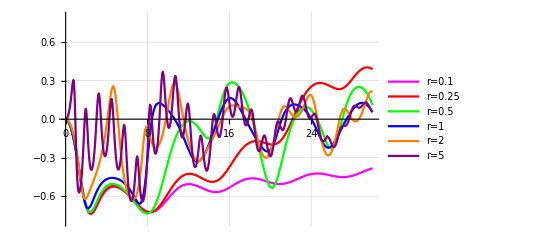

```mathematica
krange=30;
Show[{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v2kTr025[[All,1]],Re[v2kTr025[[All,2,1]]]}],Transpose[{v2kTr05[[All,1]],Re[v2kTr05[[All,2,1]]]}],Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}],Transpose[{v2kTr5[[All,1]],Re[v2kTr5[[All,2,1]]]}]},PlotRange->{{0,krange},{-0.8,0.8}},GridLines->Automatic,PlotStyle->{{Magenta},{Red},{Green},{Blue},{Orange},{Purple}},PlotLegends->{"r=0.1","r=0.25","r=0.5","r=1","r=2","r=5"},Joined->{True,True,True,True,True,True}]}]
```

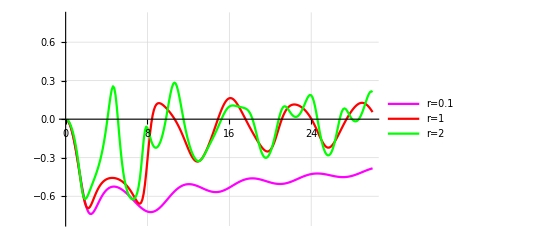

```mathematica
krange=30;
Show[{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}]},PlotRange->{{0,krange},{-0.8,0.8}},GridLines->Automatic,PlotStyle->{{Magenta},{Red},{Green},{Blue},{Orange},{Purple}},PlotLegends->{"r=0.1","r=1","r=2"},Joined->{True,True,True,True,True,True}]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bwu/Documents/pp/v2/ppv2

```mathematica
Export["v2kTr01.dat",Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}] ]
Export["v2kTr2.dat",Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}] ]
Export["v2kT.dat",Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}]]
```

v2kTr01.dat

v2kTr2.dat

v2kT.dat

```mathematica
Export["v2kTr5.dat",Transpose[{v2kTr5[[All,1]],Re[v2kTr5[[All,2,1]]]}] ]
```

v2kTr5.dat

#### v2 curves

```mathematica
v2[{rA_,θA_},{rB_,θB_},b_,kT_]:=Module[{x1u,x3u,bu},
x1u=rA/2{Cos[θA],Sin[θA]};
x3u=rB/2{Cos[θB],Sin[θB]};
bu={b,0};
NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=π/2;
v2V=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,2π,π/200.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.36837}. NIntegrate obtained -2.84068×10^-14 and 1.71995×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {1.98794}. NIntegrate obtained -1.44361×10^-14 and 1.1567×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {0.785301}. NIntegrate obtained -2.84101×10^-14 and 1.71995×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

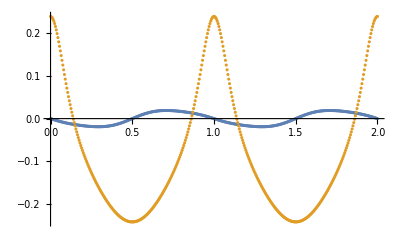

```mathematica
ListPlot[{Transpose[{v2V[[All,1]]/π,v2V[[All,2]][[All,2]]}],Transpose[{v2V[[All,1]]/π,v2V[[All,2]][[All,1]]}]}]
```

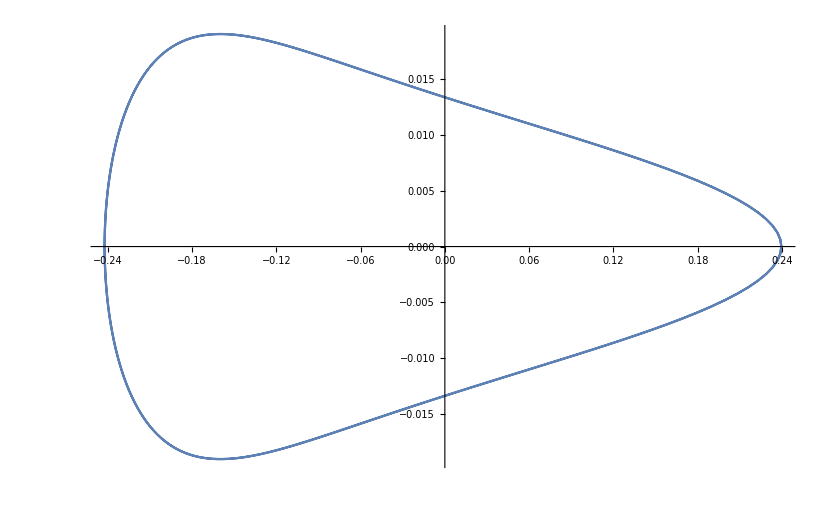

```mathematica
ListPlot[v2V[[All,2]],Joined->True]
```

```mathematica
Export["v2V.dat",v2V]
```

v2V.dat

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=π/4;
v2U=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,π,π/100.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {5.89039}. NIntegrate obtained 1.03081×10^-8 and 3.18199×10^-12 for the integral and error estimates.

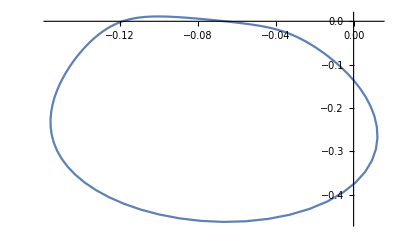

```mathematica
ListPlot[v2U[[All,2]],Joined->True]
```

```mathematica
Export["v2U.dat",v2U]
```

v2U.dat

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=10^-10;
v2H=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,π,π/100.}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.47882}. NIntegrate obtained -4.04942×10^-11 and 4.49613×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {2.47882}. NIntegrate obtained -4.04887×10^-11 and 4.4961×10^-10 for the integral and error estimates.

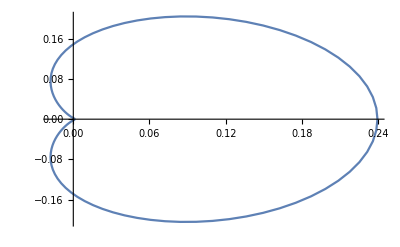

```mathematica
ListPlot[v2H[[All,2]],Joined->True]
```

```mathematica
Export["v2H.dat",v2H]
```

v2H.dat

```mathematica
kT=1.0;bT=1.0;rA=1.0;rB=1.0;θB=(3π)/4;
v2D=Table[{θ,v2[{rA,θ},{rB,θB},bT,kT]},{θ,0,π,π/100.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {3.53419}. NIntegrate obtained -1.03115×10^-8 and 4.1732×10^-12 for the integral and error estimates.

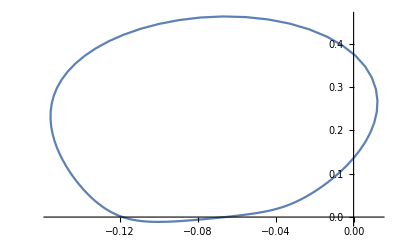

```mathematica
ListPlot[v2D[[All,2]],Joined->True]
```

```mathematica
Export["v2D.dat",v2D]
```

v2D.dat

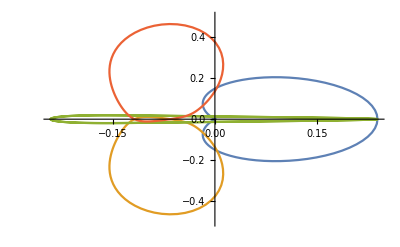

```mathematica
ListPlot[{v2H[[All,2]],v2U[[All,2]],v2V[[All,2]],v2D[[All,2]]},Joined->True,PlotRange->{Full, {-0.5,0.5}}]
```

```mathematica
Clear[dσFig];
dσFig[{bu_,x1u_,x3u_,kT_},{ x1_,x2_,x3_,x4_,qSize_},cs_,rng_:0.35]:=Module[{ϕ,x2u,x4u,p1,p2, sig},
x2u=-x1u;x4u=-x3u;
p1=Show[{Graphics[{RGBColor[0.6,0.6,0.6],Thickness[0.25*qSize],Line[{x3,x4}]}],Graphics[{PointSize[qSize],Red,Point[x3]}],Graphics[{PointSize[qSize],RGBColor[0,0.5,0],Point[x4]}],Graphics[{RGBColor[0.6,0.6,0.6],Thickness[0.25*qSize],Line[{x1,x2}]}],Graphics[{PointSize[qSize],Red,Point[x1]}],Graphics[{PointSize[qSize],RGBColor[0,0.5,0],Point[x2]}]}];
If[Depth[x1u]==2,
sig=NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p2={ParametricPlot[1/sig dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->{cs,Thickness[0.015]},AxesLabel->{x,y},LabelStyle->{Black,30}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*),PlotRange->{{-rng,rng},{-rng,rng}},ImageSize->{500,500}]},
sig=Table[NIntegrate[dσHZ[x1u[[i]],x2u[[i]],bu+x3u[[i]],bu+x4u[[i]],{kT,ϕ}],{ϕ,0,2π}],{i,1,Length[x1u]}];
p2=Table[ParametricPlot[(dσHZ[x1u[[i]],-x1u[[i]],bu+x3u[[i]],bu-x3u[[i]],{kT,ϕ}]{Cos[ϕ],Sin[ϕ]})/sig[[i]],{ϕ,0,2π},PlotStyle->cs[[i]],AxesLabel->{x,y},LabelStyle->{Black,30}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*),PlotRange->{{-rng,rng},{-rng,rng}},ImageSize->{500,500}],{i,1,Length[x1u]}]
];
Show[AppendTo[p2,p1]]

]
show[θ1_,θ2_,r0_,b_,kT_, qSize_,showQ_:True]:=Module[{x1u,x3u,bu},
x1u=r0/2{Cos[θ1],Sin[θ1]};
x3u=r0/2{Cos[θ2],Sin[θ2]};
bu={1,0};
showdσHZ[bu,x1u,x3u,kT,showQ,qSize]
]
Clear[figure];
figure[θ1_,θ2_,r0_,b_,kT_, qSize_,cs_,rng_:0.3]:=Module[{x1u,x3u,bu,r,x1,x2,x3,x4,rA,rB,ratio},
If[Depth[r0]==1,
x1u=r0/2{Cos[θ1],Sin[θ1]};
x3u=r0/2{Cos[θ2],Sin[θ2]},
x1u=Table[r0[[i]]/2{Cos[θ1],Sin[θ1]},{i,1,Length[r0]}];
x3u=Table[r0[[i]]/2{Cos[θ2],Sin[θ2]},{i,1,Length[r0]}];
];
bu={b,0};ratio=(rng+0.05)/0.35;
r=0.025*ratio;rB={rng-0.1*ratio,rng};rA={rng,rng};
x1=r*{Cos[θ1],Sin[θ1]};x2=-x1;
x3=r*{Cos[θ2],Sin[θ2]};x4=-x3;
x1=rA+x1;x2=rA+x2;x3=rB+x3;x4=rB+x4;
dσFig[{bu,x1u,x3u,kT},{x1,x2,x3,x4,qSize},cs,rng*(1+0.05/0.3)]
]
v2[{rA_,θA_},{rB_,θB_},b_,kT_]:=Module[{x1u,x3u,bu},
x1u=rA/2{Cos[θA],Sin[θA]};
x3u=rB/2{Cos[θB],Sin[θB]};
bu={b,0};
NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[bu+x1u,bu-x1u,x3u,-x3u,{kT,ϕ}],{ϕ,0,2π}]
]
```

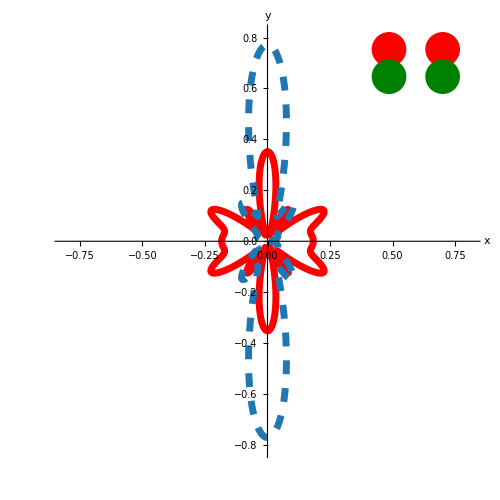

```mathematica
rdp={1,0.1};kT=10;rq=0.05;cs={{Red,Thickness[0.01]},{RGBColor["#1F77B4"],Thickness[0.01],Dashing[{0.02,0.02}]}};kT=10;bT=1;rng=0.7;
r1k10=figure[π/2,π/2,rdp,bT,kT,rq,cs,0.7]
```

```mathematica
rdp={1,0.1};rq=0.05;cs={{Red,Thickness[0.01]},{RGBColor["#1F77B4"],Thickness[0.01],Dashing[{0.02,0.02}]}};kT=30;bT=1;rng=0.7;
r1k30={{figure[0,π/2,rdp,bT,kT,rq,cs,0.3],figure[π/4,π/2,rdp,bT,kT,rq,cs,0.5],figure[π/2,π/2,rdp,bT,kT,rq,cs,0.7],figure[(3π)/4,π/2,rdp,bT,kT,rq,cs,0.5]},
	{figure[0,π/4,rdp,bT,kT,rq,cs,0.4],figure[π/4,π/4,rdp,bT,kT,rq,cs,0.5],figure[π/2,π/4,rdp,bT,kT,rq,cs,0.5],figure[(3π)/4,π/4,rdp,bT,kT,rq,cs,0.5]},
	{figure[10^-10,0,rdp,bT,kT,rq,cs,0.3],figure[π/4,0,rdp,bT,kT,rq,cs,0.4],figure[π/2,0,rdp,bT,kT,rq,cs,0.3],figure[(3π)/4,0,rdp,bT,kT,rq,cs,0.4]},
	{figure[0,3π/4,rdp,bT,kT,rq,cs,0.4],figure[π/4,3 π/4,rdp,bT,kT,rq,cs,0.5],figure[π/2,3 π/4,rdp,bT,kT,rq,cs,0.5],figure[(3π)/4,3 π/4,rdp,bT,kT,rq,cs,0.5]}
};
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$139017280 near {ϕ$139017280} = {4.33186}. NIntegrate obtained 1.13198×10^-6 and 1.21381×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$139017280 near {ϕ$139017280} = {1.9634}. NIntegrate obtained 1.00646×10^-8 and 1.38258×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$139137966 near {ϕ$139137966} = {2.40518}. NIntegrate obtained 6.70765×10^-7 and 8.74184×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.000128228,-8.82391} lies outside the range of data in the interpolating function. Extrapolation will be used.

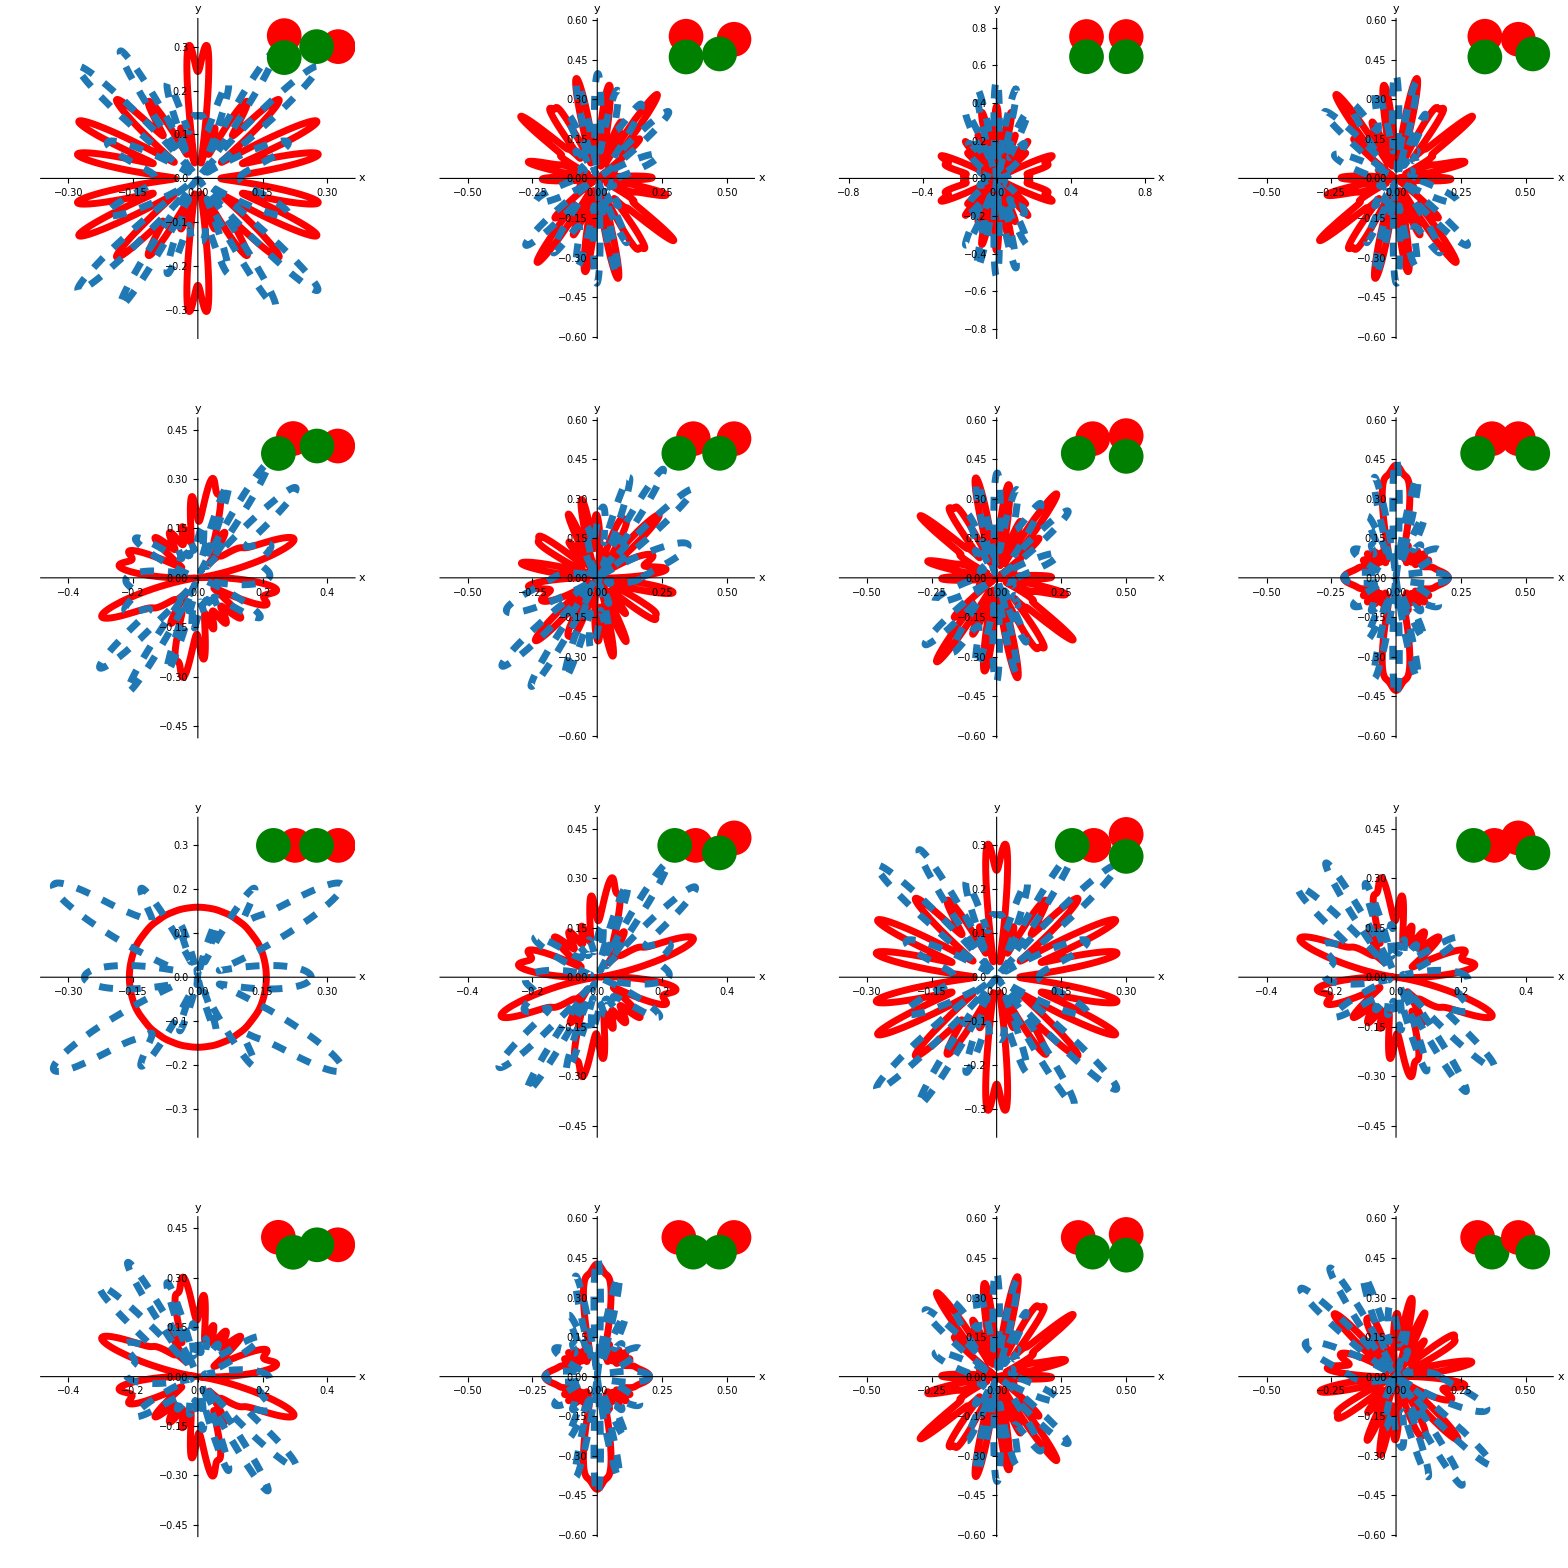

```mathematica
GraphicsGrid[r1k30]
```

## b=0.25 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤100,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.1*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$24366069 near {ϕ$24366069} = {2.18429}. NIntegrate obtained 1.15861×10^-16 and 6.9595×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$24434972 near {ϕ$24434972} = {2.15975}. NIntegrate obtained -4.21728×10^-14 and 8.40656×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$24502690 near {ϕ$24502690} = {2.15975}. NIntegrate obtained 2.96502×10^-16 and 8.54611×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

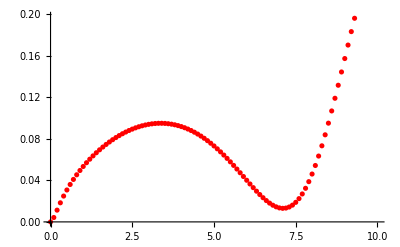

{{0.,{0.,0.}},{0.1,{0.00422481,1.11384×10^-14}},{0.2,{0.0113363,-3.36124×10^-12}},{0.3,{0.0184105,1.99104×10^-14}},{0.4,{0.024906,-7.48383×10^-12}},{0.5,{0.0307701,2.11838×10^-16}},{0.6,{0.0360859,-8.20853×10^-13}},{0.7,{0.0409434,-5.40494×10^-12}},{0.8,{0.0454179,1.16623×10^-11}},{0.9,{0.0495675,1.72859×10^-12}},{1.,{0.0534365,-1.67846×10^-14}},{1.1,{0.0570585,-4.97252×10^-12}},{1.2,{0.0604591,-2.59341×10^-13}},{1.3,{0.0636576,3.1318×10^-12}},{1.4,{0.0666692,1.91635×10^-13}},{1.5,{0.0695054,-2.68953×10^-12}},{1.6,{0.0721753,1.14576×10^-13}},{1.7,{0.0746859,-7.97601×10^-14}},{1.8,{0.0770426,-1.09019×10^-12}},{1.9,{0.0792494,-9.05501×10^-13}},{2.,{0.0813095,-1.25821×10^-12}},{2.1,{0.0832251,-2.97347×10^-12}},{2.2,{0.0849978,-8.04994×10^-12}},{2.3,{0.0866284,1.1239×10^-12}},{2.4,{0.0881174,-1.1848×10^-11}},{2.5,{0.0894648,-3.91182×10^-13}},{2.6,{0.0906704,-8.83093×10^-13}},{2.7,{0.0917333,1.37466×10^-10}},{2.8,{0.0926528,-5.49278×10^-13}},{2.9,{0.0934276,6.74785×10^-12}},{3.,{0.0940563,2.49483×10^-13}},{3.1,{0.0945374,-8.28457×10^-12}},{3.2,{0.0948691,-1.34405×10^-11}},{3.3,{0.0950497,5.74998×10^-17}},{3.4,{0.095077,7.98549×10^-12}},{3.5,{0.0949491,4.43295×10^-11}},{3.6,{0.0946639,-1.03251×10^-11}},{3.7,{0.0942193,-5.8449×10^-11}},{3.8,{0.0936133,-2.18816×10^-11}},{3.9,{0.0928435,-1.6374×10^-10}},{4.,{0.0919081,-8.09397×10^-12}},{4.1,{0.0908055,-4.98981×10^-12}},{4.2,{0.089534,6.60404×10^-12}},{4.3,{0.0880923,3.19013×10^-9}},{4.4,{0.0864795,-4.72996×10^-10}},{4.5,{0.0846952,-1.20626×10^-9}},{4.6,{0.0827393,-3.25264×10^-11}},{4.7,{0.0806127,-5.23063×10^-10}},{4.8,{0.078317,2.83734×10^-11}},{4.9,{0.0758547,-1.18662×10^-10}},{5.,{0.0732296,-7.13323×10^-12}},{5.1,{0.0704468,-7.72924×10^-11}},{5.2,{0.067513,-7.56827×10^-12}},{5.3,{0.0644368,7.77933×10^-17}},{5.4,{0.0612286,5.50916×10^-10}},{5.5,{0.057902,-1.08521×10^-11}},{5.6,{0.0544719,-1.42315×10^-10}},{5.7,{0.0509572,5.29217×10^-11}},{5.8,{0.0473807,-1.42916×10^-10}},{5.9,{0.043768,5.50509×10^-10}},{6.,{0.0401489,-1.54338×10^-11}},{6.1,{0.0365577,9.37873×10^-10}},{6.2,{0.0330338,1.59818×10^-10}},{6.3,{0.0296205,-3.51017×10^-11}},{6.4,{0.0263667,-9.4529×10^-12}},{6.5,{0.0233259,1.32896×10^-11}},{6.6,{0.0205565,1.51402×10^-11}},{6.7,{0.0181212,1.52394×10^-11}},{6.8,{0.0160861,-9.3813×10^-11}},{6.9,{0.0145203,7.67112×10^-10}},{7.,{0.0134945,-1.75124×10^-11}},{7.1,{0.0130796,1.36793×10^-10}},{7.2,{0.0133452,8.4247×10^-11}},{7.3,{0.0143571,1.03404×10^-11}},{7.4,{0.0161754,9.99595×10^-9}},{7.5,{0.0188526,-3.38033×10^-10}},{7.6,{0.0224308,-1.0449×10^-10}},{7.7,{0.0269403,-2.78495×10^-11}},{7.8,{0.0323973,-2.36626×10^-10}},{7.9,{0.0388024,1.97095×10^-10}},{8.,{0.0461405,-1.46574×10^-10}},{8.1,{0.054381,-1.28534×10^-8}},{8.2,{0.0634742,-3.18479×10^-9}},{8.3,{0.0733607,1.7824×10^-11}},{8.4,{0.0839648,4.27943×10^-13}},{8.5,{0.0952013,-1.42229×10^-10}},{8.6,{0.106977,-2.39365×10^-9}},{8.7,{0.119194,7.79595×10^-12}},{8.8,{0.131753,1.57993×10^-10}},{8.9,{0.144552,3.73276×10^-11}},{9.,{0.157497,3.82035×10^-9}},{9.1,{0.170494,6.36044×10^-16}},{9.2,{0.18346,-1.26738×10^-8}},{9.3,{0.196319,1.87049×10^-10}},{9.4,{0.209001,3.90416×10^-9}},{9.5,{0.221449,-2.74936×10^-10}},{9.6,{0.233613,4.65552×10^-10}},{9.7,{0.245451,7.46093×10^-8}},{9.8,{0.256932,2.51883×10^-10}},{9.9,{0.268029,-3.14258×10^-8}},{10.,{0.278724,5.40061×10^-11}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31577221 near {ϕ$31577221} = {3.44829}. NIntegrate obtained -7.23169×10^-7 and 2.58796×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32409101 near {ϕ$32409101} = {3.42375}. NIntegrate obtained -1.58848×10^-6 and 4.34631×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32477739 near {ϕ$32477739} = {5.26452}. NIntegrate obtained -0.000012046 and 1.26603×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

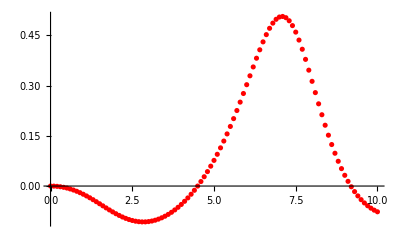

{{0.,{0.,0.}},{0.1,{-0.000231425,0.000160473}},{0.2,{-0.00093174,0.000654882}},{0.3,{-0.00211331,0.00151372}},{0.4,{-0.00378993,0.00277595}},{0.5,{-0.00597287,0.00448536}},{0.6,{-0.00866921,0.00668742}},{0.7,{-0.0118795,0.00942647}},{0.8,{-0.015596,0.0127434}},{0.9,{-0.0198012,0.0166731}},{1.,{-0.0244666,0.0212424}},{1.1,{-0.0295525,0.0264674}},{1.2,{-0.0350071,0.0323521}},{1.3,{-0.0407675,0.0388873}},{1.4,{-0.0467603,0.0460493}},{1.5,{-0.0529035,0.0538001}},{1.6,{-0.0591082,0.062088}},{1.7,{-0.0652812,0.0708489}},{1.8,{-0.0713273,0.0800076}},{1.9,{-0.0771523,0.0894808}},{2.,{-0.0826652,0.099179}},{2.1,{-0.0877808,0.10901}},{2.2,{-0.0924208,0.11888}},{2.3,{-0.0965163,0.128699}},{2.4,{-0.100007,0.138379}},{2.5,{-0.102844,0.14784}},{2.6,{-0.104986,0.157007}},{2.7,{-0.106403,0.165815}},{2.8,{-0.107072,0.174206}},{2.9,{-0.106978,0.182131}},{3.,{-0.106111,0.189548}},{3.1,{-0.104467,0.196424}},{3.2,{-0.102045,0.202732}},{3.3,{-0.0988474,0.20845}},{3.4,{-0.0948769,0.213564}},{3.5,{-0.0901368,0.21806}},{3.6,{-0.0846296,0.221932}},{3.7,{-0.0783583,0.225172}},{3.8,{-0.0713214,0.227776}},{3.9,{-0.0635169,0.229743}},{4.,{-0.0549399,0.23107}},{4.1,{-0.045582,0.231754}},{4.2,{-0.035432,0.231795}},{4.3,{-0.0244755,0.231189}},{4.4,{-0.012695,0.229933}},{4.5,{-0.0000698554,0.228025}},{4.6,{0.0134232,0.22546}},{4.7,{0.0278094,0.222234}},{4.8,{0.0431157,0.218342}},{4.9,{0.0593695,0.213782}},{5.,{0.0765974,0.208551}},{5.1,{0.0948238,0.20265}},{5.2,{0.114068,0.196082}},{5.3,{0.134343,0.188856}},{5.4,{0.155651,0.180988}},{5.5,{0.177978,0.172504}},{5.6,{0.20129,0.163441}},{5.7,{0.225527,0.153854}},{5.8,{0.250597,0.143806}},{5.9,{0.276363,0.133411}},{6.,{0.302639,0.122787}},{6.1,{0.329179,0.112112}},{6.2,{0.355667,0.101544}},{6.3,{0.381714,0.0913335}},{6.4,{0.40685,0.081751}},{6.5,{0.43053,0.0731044}},{6.6,{0.452143,0.0657281}},{6.7,{0.471029,0.0599736}},{6.8,{0.486513,0.0561886}},{6.9,{0.49794,0.0546943}},{7.,{0.504729,0.0557612}},{7.1,{0.506421,0.0595766}},{7.2,{0.502728,0.0662264}},{7.3,{0.493574,0.0756754}},{7.4,{0.479107,0.0877635}},{7.5,{0.459702,0.102212}},{7.6,{0.435931,0.118645}},{7.7,{0.408518,0.136614}},{7.8,{0.37828,0.155639}},{7.9,{0.34607,0.175234}},{8.,{0.312718,0.194943}},{8.1,{0.278986,0.214358}},{8.2,{0.24554,0.233134}},{8.3,{0.212932,0.250998}},{8.4,{0.181597,0.267743}},{8.5,{0.151854,0.283226}},{8.6,{0.123924,0.29736}},{8.7,{0.0979421,0.310101}},{8.8,{0.0739705,0.321446}},{8.9,{0.0520181,0.331412}},{9.,{0.0320527,0.34004}},{9.1,{0.0140123,0.347382}},{9.2,{-0.00218422,0.353496}},{9.3,{-0.0166296,0.358448}},{9.4,{-0.029423,0.362301}},{9.5,{-0.0406642,0.365117}},{9.6,{-0.0504518,0.366957}},{9.7,{-0.0588798,0.367875}},{9.8,{-0.0660374,0.367926}},{9.9,{-0.0720069,0.367157}},{10.,{-0.0768646,0.365612}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32716086 near {ϕ$32716086} = {6.01778009555628290438988869937020353972911834716796875}. NIntegrate obtained -7.10543×10^-15 and 7.11667×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32800282 near {ϕ$32800282} = {5.3627}. NIntegrate obtained 1.42275×10^-13 and 1.65573×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32879968 near {ϕ$32879968} = {0.197972}. NIntegrate obtained 1.42075×10^-12 and 2.96156×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

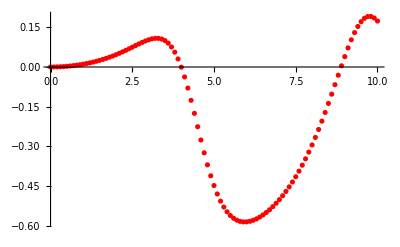

{{0.,{0.,0.}},{0.1,{0.000105613,-5.60131×10^-17}},{0.2,{0.000422484,4.56076×10^-15}},{0.3,{0.000950522,1.04884×10^-13}},{0.4,{0.00169046,-1.1145×10^-14}},{0.5,{0.0026437,2.31063×10^-14}},{0.6,{0.00381297,3.60144×10^-14}},{0.7,{0.00520151,-8.37782×10^-15}},{0.8,{0.00681381,9.39236×10^-15}},{0.9,{0.00865574,-7.93737×10^-13}},{1.,{0.0107339,2.4898×10^-13}},{1.1,{0.0130562,-1.7217×10^-14}},{1.2,{0.0156312,1.21774×10^-13}},{1.3,{0.0184684,-6.50026×10^-13}},{1.4,{0.0215777,-1.24955×10^-13}},{1.5,{0.0249689,3.14175×10^-14}},{1.6,{0.0286516,-5.77752×10^-13}},{1.7,{0.0326339,3.0139×10^-12}},{1.8,{0.0369222,-2.41787×10^-9}},{1.9,{0.0415195,5.15793×10^-12}},{2.,{0.046424,-3.66241×10^-13}},{2.1,{0.0516273,5.37234×10^-19}},{2.2,{0.0571119,6.36057×10^-13}},{2.3,{0.0628483,-5.58671×10^-14}},{2.4,{0.0687908,4.83499×10^-13}},{2.5,{0.0748734,2.05203×10^-12}},{2.6,{0.0810034,-1.38454×10^-11}},{2.7,{0.0870552,2.54368×10^-12}},{2.8,{0.092862,1.62658×10^-13}},{2.9,{0.098207,4.07503×10^-13}},{3.,{0.102813,3.81541×10^-17}},{3.1,{0.106335,3.21317×10^-17}},{3.2,{0.108349,-2.39098×10^-9}},{3.3,{0.108349,1.85824×10^-14}},{3.4,{0.10575,-1.78186×10^-15}},{3.5,{0.0998964,-1.01536×10^-11}},{3.6,{0.090096,3.11557×10^-17}},{3.7,{0.075661,-5.75278×10^-10}},{3.8,{0.0559795,3.74097×10^-17}},{3.9,{0.0306015,-1.08945×10^-16}},{4.,{-0.00066337,-2.47166×10^-18}},{4.1,{-0.0376582,-1.8131×10^-12}},{4.2,{-0.0798197,-8.02513×10^-12}},{4.3,{-0.126174,3.97615×10^-12}},{4.4,{-0.1754,-4.26585×10^-17}},{4.5,{-0.22595,-7.53903×10^-11}},{4.6,{-0.276214,-5.92791×10^-10}},{4.7,{-0.32469,-7.91602×10^-12}},{4.8,{-0.370113,1.10308×10^-11}},{4.9,{-0.41154,-9.92514×10^-13}},{5.,{-0.448374,2.87346×10^-10}},{5.1,{-0.48034,9.55356×10^-12}},{5.2,{-0.507427,7.17918×10^-17}},{5.3,{-0.529822,4.06705×10^-11}},{5.4,{-0.547837,-2.27434×10^-9}},{5.5,{-0.561856,-2.51908×10^-10}},{5.6,{-0.572289,1.13931×10^-11}},{5.7,{-0.579538,1.14586×10^-9}},{5.8,{-0.58398,-8.54684×10^-10}},{5.9,{-0.585954,-2.09037×10^-10}},{6.,{-0.585755,-5.50176×10^-10}},{6.1,{-0.583636,-6.76801×10^-11}},{6.2,{-0.579807,8.16636×10^-11}},{6.3,{-0.57444,-2.24775×10^-11}},{6.4,{-0.567672,-4.10463×10^-10}},{6.5,{-0.559608,1.03097×10^-11}},{6.6,{-0.550326,-3.66979×10^-11}},{6.7,{-0.53988,1.81265×10^-11}},{6.8,{-0.528304,1.32163×10^-12}},{6.9,{-0.515613,-1.05448×10^-10}},{7.,{-0.501805,1.04738×10^-12}},{7.1,{-0.486867,2.50514×10^-11}},{7.2,{-0.470772,1.76624×10^-12}},{7.3,{-0.453484,5.00284×10^-11}},{7.4,{-0.434959,4.45988×10^-10}},{7.5,{-0.415146,-1.62911×10^-10}},{7.6,{-0.393993,6.69354×10^-9}},{7.7,{-0.371444,4.61832×10^-9}},{7.8,{-0.34745,-1.25171×10^-10}},{7.9,{-0.321966,3.16818×10^-11}},{8.,{-0.294961,-3.30973×10^-10}},{8.1,{-0.266422,-8.27665×10^-12}},{8.2,{-0.236366,-2.71467×10^-10}},{8.3,{-0.204845,-4.65123×10^-11}},{8.4,{-0.171959,-5.86849×10^-9}},{8.5,{-0.13787,-3.21273×10^-10}},{8.6,{-0.102812,-3.00791×10^-11}},{8.7,{-0.0671081,-2.94519×10^-10}},{8.8,{-0.0311777,2.23292×10^-9}},{8.9,{0.00445504,-3.3431×10^-11}},{9.,{0.0391579,-1.36214×10^-12}},{9.1,{0.072207,1.79959×10^-10}},{9.2,{0.10279,3.14645×10^-11}},{9.3,{0.130068,-4.00705×10^-9}},{9.4,{0.153202,-9.09116×10^-10}},{9.5,{0.171419,-6.28488×10^-10}},{9.6,{0.184078,-7.67146×10^-11}},{9.7,{0.190727,-4.73454×10^-11}},{9.8,{0.19115,6.9626×10^-9}},{9.9,{0.185394,-2.96937×10^-10}},{10.,{0.173765,-2.74594×10^-10}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39099266 near {ϕ$39099266} = {2.84697}. NIntegrate obtained -7.23169×10^-7 and 2.58796×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39932189 near {ϕ$39932189} = {2.87151}. NIntegrate obtained -1.58848×10^-6 and 4.34631×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40000827 near {ϕ$40000827} = {4.17233}. NIntegrate obtained -0.000012046 and 1.26603×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

{{0.,{0.,0.}},{0.1,{-0.000231425,-0.000160473}},{0.2,{-0.00093174,-0.000654882}},{0.3,{-0.00211331,-0.00151372}},{0.4,{-0.00378993,-0.00277595}},{0.5,{-0.00597287,-0.00448536}},{0.6,{-0.00866921,-0.00668742}},{0.7,{-0.0118795,-0.00942647}},{0.8,{-0.015596,-0.0127434}},{0.9,{-0.0198012,-0.0166731}},{1.,{-0.0244666,-0.0212424}},{1.1,{-0.0295525,-0.0264674}},{1.2,{-0.0350071,-0.0323521}},{1.3,{-0.0407675,-0.0388873}},{1.4,{-0.0467603,-0.0460493}},{1.5,{-0.0529035,-0.0538001}},{1.6,{-0.0591082,-0.062088}},{1.7,{-0.0652812,-0.0708489}},{1.8,{-0.0713273,-0.0800076}},{1.9,{-0.0771523,-0.0894808}},{2.,{-0.0826652,-0.099179}},{2.1,{-0.0877808,-0.10901}},{2.2,{-0.0924208,-0.11888}},{2.3,{-0.0965163,-0.128699}},{2.4,{-0.100007,-0.138379}},{2.5,{-0.102844,-0.14784}},{2.6,{-0.104986,-0.157007}},{2.7,{-0.106403,-0.165815}},{2.8,{-0.107072,-0.174206}},{2.9,{-0.106978,-0.182131}},{3.,{-0.106111,-0.189548}},{3.1,{-0.104467,-0.196424}},{3.2,{-0.102045,-0.202732}},{3.3,{-0.0988474,-0.20845}},{3.4,{-0.0948769,-0.213564}},{3.5,{-0.0901368,-0.21806}},{3.6,{-0.0846296,-0.221932}},{3.7,{-0.0783583,-0.225172}},{3.8,{-0.0713214,-0.227776}},{3.9,{-0.0635169,-0.229743}},{4.,{-0.0549399,-0.23107}},{4.1,{-0.045582,-0.231754}},{4.2,{-0.035432,-0.231795}},{4.3,{-0.0244755,-0.231189}},{4.4,{-0.012695,-0.229933}},{4.5,{-0.0000698554,-0.228025}},{4.6,{0.0134232,-0.22546}},{4.7,{0.0278094,-0.222234}},{4.8,{0.0431157,-0.218342}},{4.9,{0.0593695,-0.213782}},{5.,{0.0765974,-0.208551}},{5.1,{0.0948238,-0.20265}},{5.2,{0.114068,-0.196082}},{5.3,{0.134343,-0.188856}},{5.4,{0.155651,-0.180988}},{5.5,{0.177978,-0.172504}},{5.6,{0.20129,-0.163441}},{5.7,{0.225527,-0.153854}},{5.8,{0.250597,-0.143806}},{5.9,{0.276363,-0.133411}},{6.,{0.302639,-0.122787}},{6.1,{0.329179,-0.112112}},{6.2,{0.355667,-0.101544}},{6.3,{0.381714,-0.0913335}},{6.4,{0.40685,-0.081751}},{6.5,{0.43053,-0.0731044}},{6.6,{0.452143,-0.0657281}},{6.7,{0.471029,-0.0599736}},{6.8,{0.486513,-0.0561886}},{6.9,{0.49794,-0.0546943}},{7.,{0.504729,-0.0557612}},{7.1,{0.506421,-0.0595766}},{7.2,{0.502728,-0.0662264}},{7.3,{0.493574,-0.0756754}},{7.4,{0.479107,-0.0877635}},{7.5,{0.459702,-0.102212}},{7.6,{0.435931,-0.118645}},{7.7,{0.408518,-0.136614}},{7.8,{0.37828,-0.155639}},{7.9,{0.34607,-0.175234}},{8.,{0.312718,-0.194943}},{8.1,{0.278986,-0.214358}},{8.2,{0.24554,-0.233134}},{8.3,{0.212932,-0.250998}},{8.4,{0.181597,-0.267743}},{8.5,{0.151854,-0.283226}},{8.6,{0.123924,-0.29736}},{8.7,{0.0979421,-0.310101}},{8.8,{0.0739705,-0.321446}},{8.9,{0.0520181,-0.331412}},{9.,{0.0320527,-0.34004}},{9.1,{0.0140123,-0.347382}},{9.2,{-0.00218422,-0.353496}},{9.3,{-0.0166296,-0.358448}},{9.4,{-0.029423,-0.362301}},{9.5,{-0.0406642,-0.365117}},{9.6,{-0.0504518,-0.366957}},{9.7,{-0.0588798,-0.367875}},{9.8,{-0.0660374,-0.367926}},{9.9,{-0.0720069,-0.367157}},{10.,{-0.0768646,-0.365612}}}

```mathematica
Getv2kT[0.25, 0]
Getv2kT[0.25, π/4]
Getv2kT[0.25, π/2]
Getv2kT[0.25, (3π)/4]
```

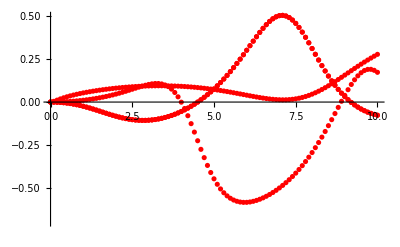

```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange->{Full,{-0.7,0.5}}]
```

## b=0.5 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤100,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.1*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40238881 near {ϕ$40238881} = {2.0493}. NIntegrate obtained 6.38324×10^-18 and 4.71509×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40280084 near {ϕ$40280084} = {2.03703}. NIntegrate obtained -1.55312×10^-17 and 9.15974×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40323067 near {ϕ$40323067} = {1.10437}. NIntegrate obtained -7.69784×10^-18 and 1.00183×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

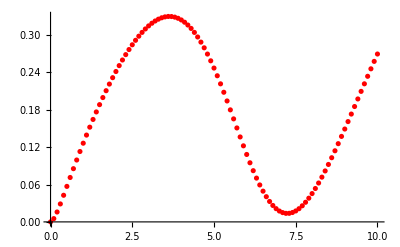

{{0.,{0.,0.}},{0.1,{0.00525805,2.37934×10^-16}},{0.2,{0.0159068,-5.47164×10^-16}},{0.3,{0.028841,-2.57229×10^-16}},{0.4,{0.0427575,3.80978×10^-17}},{0.5,{0.0570201,2.45458×10^-12}},{0.6,{0.0713076,8.49743×10^-11}},{0.7,{0.0854545,-7.32563×10^-14}},{0.8,{0.0993741,-2.37331×10^-13}},{0.9,{0.113021,-5.9255×10^-17}},{1.,{0.126369,-6.22923×10^-18}},{1.1,{0.139406,-3.11398×10^-14}},{1.2,{0.152123,-1.53233×10^-15}},{1.3,{0.164512,-1.90294×10^-15}},{1.4,{0.176569,6.42889×10^-13}},{1.5,{0.188286,-2.95008×10^-12}},{1.6,{0.199657,-1.65229×10^-17}},{1.7,{0.210671,-1.01996×10^-11}},{1.8,{0.221318,3.08199×10^-11}},{1.9,{0.231588,2.1797×10^-11}},{2.,{0.241466,-4.17963×10^-12}},{2.1,{0.250938,3.66429×10^-13}},{2.2,{0.259987,-8.64339×10^-14}},{2.3,{0.268595,-3.15946×10^-14}},{2.4,{0.276744,-4.10158×10^-15}},{2.5,{0.284411,1.46142×10^-17}},{2.6,{0.291577,-3.37773×10^-14}},{2.7,{0.298216,3.73121×10^-10}},{2.8,{0.304304,1.05822×10^-10}},{2.9,{0.309816,1.13337×10^-16}},{3.,{0.314724,4.5571×10^-12}},{3.1,{0.319001,-1.13741×10^-14}},{3.2,{0.322617,1.19371×10^-10}},{3.3,{0.325544,6.9245×10^-10}},{3.4,{0.327752,2.04154×10^-17}},{3.5,{0.32921,1.30203×10^-17}},{3.6,{0.329889,6.21519×10^-11}},{3.7,{0.329762,1.14261×10^-8}},{3.8,{0.328799,-4.16076×10^-9}},{3.9,{0.326976,-1.59014×10^-10}},{4.,{0.324269,4.10409×10^-12}},{4.1,{0.320658,8.69559×10^-12}},{4.2,{0.316128,-2.09829×10^-11}},{4.3,{0.310668,-1.79597×10^-8}},{4.4,{0.304272,-5.47785×10^-17}},{4.5,{0.296944,-1.82982×10^-9}},{4.6,{0.288694,7.40546×10^-12}},{4.7,{0.27954,4.39795×10^-13}},{4.8,{0.269515,5.07725×10^-17}},{4.9,{0.258657,-4.45365×10^-12}},{5.,{0.247021,3.59797×10^-11}},{5.1,{0.234672,-6.39136×10^-10}},{5.2,{0.221688,-7.38134×10^-10}},{5.3,{0.208162,1.09456×10^-9}},{5.4,{0.194197,1.42513×10^-12}},{5.5,{0.179908,2.8809×10^-12}},{5.6,{0.165422,1.94326×10^-12}},{5.7,{0.150873,-2.66637×10^-9}},{5.8,{0.136404,-4.65442×10^-12}},{5.9,{0.122159,2.8246×10^-12}},{6.,{0.108286,2.00814×10^-11}},{6.1,{0.0949307,-4.5596×10^-12}},{6.2,{0.0822325,-8.18084×10^-12}},{6.3,{0.0703244,-2.3644×10^-8}},{6.4,{0.059328,5.39085×10^-11}},{6.5,{0.0493521,-2.77871×10^-10}},{6.6,{0.0404898,-5.10517×10^-10}},{6.7,{0.0328178,-5.51971×10^-12}},{6.8,{0.0263943,4.7237×10^-12}},{6.9,{0.0212594,3.94922×10^-10}},{7.,{0.017435,5.83433×10^-12}},{7.1,{0.0149252,-2.16407×10^-10}},{7.2,{0.0137182,6.71861×10^-12}},{7.3,{0.013787,-3.24282×10^-8}},{7.4,{0.0150915,8.40408×10^-12}},{7.5,{0.0175805,4.2174×10^-8}},{7.6,{0.0211938,2.84197×10^-8}},{7.7,{0.025864,5.0206×10^-11}},{7.8,{0.0315186,7.10694×10^-12}},{7.9,{0.0380817,1.25971×10^-10}},{8.,{0.0454757,2.86761×10^-8}},{8.1,{0.0536229,7.40864×10^-11}},{8.2,{0.0624466,-2.1029×10^-10}},{8.3,{0.0718717,4.17197×10^-11}},{8.4,{0.0818259,-2.07315×10^-10}},{8.5,{0.0922415,-1.24884×10^-10}},{8.6,{0.103053,-8.22902×10^-12}},{8.7,{0.1142,-3.17892×10^-11}},{8.8,{0.125626,-2.89397×10^-10}},{8.9,{0.13728,1.93621×10^-10}},{9.,{0.149113,2.15116×10^-10}},{9.1,{0.161082,-6.01441×10^-11}},{9.2,{0.173148,-3.68121×10^-10}},{9.3,{0.185275,-1.38057×10^-9}},{9.4,{0.197432,-5.61704×10^-10}},{9.5,{0.209589,-2.16329×10^-9}},{9.6,{0.22172,6.80343×10^-10}},{9.7,{0.233805,-3.89976×10^-12}},{9.8,{0.24582,-1.04135×10^-8}},{9.9,{0.257749,1.72024×10^-10}},{10.,{0.269576,2.40401×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$47573579 near {ϕ$47573579} = {4.34414}. NIntegrate obtained -1.41686×10^-6 and 4.36886×10^-12 for the integral and error estimates.

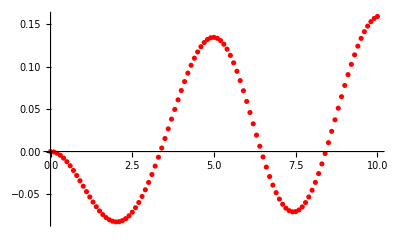

{{0.,{0.,0.}},{0.1,{-0.000500291,0.000116149}},{0.2,{-0.00198858,0.00047435}},{0.3,{-0.00442943,0.00109651}},{0.4,{-0.00776466,0.00200725}},{0.5,{-0.0119145,0.00323082}},{0.6,{-0.0167786,0.00478839}},{0.7,{-0.0222384,0.00669689}},{0.8,{-0.0281597,0.00896706}},{0.9,{-0.0343966,0.0116034}},{1.,{-0.0407959,0.0146037}},{1.1,{-0.0472013,0.0179592}},{1.2,{-0.0534581,0.0216552}},{1.3,{-0.059417,0.0256713}},{1.4,{-0.0649381,0.0299828}},{1.5,{-0.0698936,0.0345614}},{1.6,{-0.0741699,0.0393763}},{1.7,{-0.0776696,0.0443951}},{1.8,{-0.0803117,0.049585}},{1.9,{-0.0820319,0.0549128}},{2.,{-0.0827828,0.0603467}},{2.1,{-0.0825321,0.0658553}},{2.2,{-0.0812627,0.0714093}},{2.3,{-0.0789709,0.0769804}},{2.4,{-0.0756655,0.0825422}},{2.5,{-0.0713666,0.0880696}},{2.6,{-0.0661047,0.0935387}},{2.7,{-0.0599196,0.0989267}},{2.8,{-0.0528602,0.104211}},{2.9,{-0.0449829,0.10937}},{3.,{-0.0363525,0.114382}},{3.1,{-0.0270413,0.119223}},{3.2,{-0.0171286,0.123869}},{3.3,{-0.00670162,0.128297}},{3.4,{0.0041452,0.132477}},{3.5,{0.0153099,0.136383}},{3.6,{0.0266832,0.139982}},{3.7,{0.0381482,0.14324}},{3.8,{0.0495811,0.146121}},{3.9,{0.0608517,0.148585}},{4.,{0.0718237,0.150591}},{4.1,{0.0823562,0.152093}},{4.2,{0.0923051,0.153046}},{4.3,{0.101525,0.153402}},{4.4,{0.109871,0.15311}},{4.5,{0.117202,0.152123}},{4.6,{0.123385,0.150391}},{4.7,{0.128295,0.14787}},{4.8,{0.131822,0.144516}},{4.9,{0.133875,0.140293}},{5.,{0.134382,0.135169}},{5.1,{0.133297,0.129119}},{5.2,{0.130602,0.122128}},{5.3,{0.126308,0.114191}},{5.4,{0.120458,0.105313}},{5.5,{0.113128,0.0955099}},{5.6,{0.104423,0.0848098}},{5.7,{0.0944808,0.0732507}},{5.8,{0.0834632,0.060882}},{5.9,{0.071557,0.0477625}},{6.,{0.0589675,0.0339598}},{6.1,{0.0459141,0.0195488}},{6.2,{0.0326246,0.00461002}},{6.3,{0.0193305,-0.0107714}},{6.4,{0.00626133,-0.0265078}},{6.5,{-0.00636037,-0.0425091}},{6.6,{-0.0183229,-0.0586865}},{6.7,{-0.0294294,-0.074951}},{6.8,{-0.0395012,-0.0912154}},{6.9,{-0.0483799,-0.107395}},{7.,{-0.0559293,-0.123408}},{7.1,{-0.0620368,-0.139175}},{7.2,{-0.066614,-0.15462}},{7.3,{-0.0695969,-0.169671}},{7.4,{-0.0709462,-0.184259}},{7.5,{-0.0706468,-0.198316}},{7.6,{-0.0687072,-0.211779}},{7.7,{-0.065159,-0.224587}},{7.8,{-0.0600563,-0.236681}},{7.9,{-0.0534743,-0.24801}},{8.,{-0.0455087,-0.25852}},{8.1,{-0.036274,-0.268162}},{8.2,{-0.0259028,-0.276897}},{8.3,{-0.0145435,-0.284682}},{8.4,{-0.00235856,-0.291485}},{8.5,{0.0104769,-0.297281}},{8.6,{0.0237788,-0.302049}},{8.7,{0.0373559,-0.305776}},{8.8,{0.0510127,-0.308463}},{8.9,{0.0645538,-0.310112}},{9.,{0.0777857,-0.31074}},{9.1,{0.0905215,-0.310372}},{9.2,{0.102584,-0.309044}},{9.3,{0.113808,-0.306799}},{9.4,{0.124045,-0.303692}},{9.5,{0.133165,-0.299786}},{9.6,{0.141059,-0.29515}},{9.7,{0.147639,-0.28986}},{9.8,{0.152842,-0.283995}},{9.9,{0.156627,-0.277639}},{10.,{0.158979,-0.270878}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48135501 near {ϕ$48135501} = {3.68146}. NIntegrate obtained -5.27356×10^-14 and 4.40267×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48235933 near {ϕ$48235933} = {5.942873730694612832703427329761325381696224212646484375}. NIntegrate obtained -2.98928×10^-14 and 1.34071×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48338169 near {ϕ$48338169} = {2.57699}. NIntegrate obtained -6.91544×10^-13 and 2.24677×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

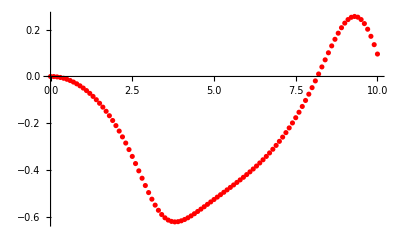

{{0.,{0.,0.}},{0.1,{-0.000465729,-1.29326×10^-15}},{0.2,{-0.00187372,-3.00477×10^-15}},{0.3,{-0.00424724,-1.6173×10^-13}},{0.4,{-0.00761083,9.60523×10^-15}},{0.5,{-0.0119878,4.01797×10^-15}},{0.6,{-0.0173987,-1.15545×10^-14}},{0.7,{-0.0238604,6.46782×10^-15}},{0.8,{-0.0313864,3.1261×10^-14}},{0.9,{-0.0399876,3.46265×10^-13}},{1.,{-0.0496732,3.74359×10^-14}},{1.1,{-0.0604524,2.61639×10^-13}},{1.2,{-0.072336,-2.472×10^-13}},{1.3,{-0.0853386,-3.41183×10^-14}},{1.4,{-0.0994804,-3.34671×10^-12}},{1.5,{-0.114789,-6.03635×10^-13}},{1.6,{-0.131301,4.29244×10^-13}},{1.7,{-0.149063,7.6968×10^-15}},{1.8,{-0.16813,8.35215×10^-12}},{1.9,{-0.188564,-2.11759×10^-11}},{2.,{-0.210431,2.61654×10^-12}},{2.1,{-0.233791,-3.59321×10^-13}},{2.2,{-0.258688,-7.41995×10^-13}},{2.3,{-0.285133,-3.91694×10^-13}},{2.4,{-0.313084,3.33204×10^-12}},{2.5,{-0.342421,-5.93236×10^-11}},{2.6,{-0.372918,2.06325×10^-12}},{2.7,{-0.40422,-3.28468×10^-11}},{2.8,{-0.435825,4.22584×10^-17}},{2.9,{-0.467094,-1.25967×10^-16}},{3.,{-0.497264,7.23559×10^-12}},{3.1,{-0.525517,-9.42618×10^-13}},{3.2,{-0.551047,6.09638×10^-10}},{3.3,{-0.573155,-6.34714×10^-11}},{3.4,{-0.591327,6.739×10^-17}},{3.5,{-0.605292,1.42908×10^-9}},{3.6,{-0.61503,-5.20079×10^-11}},{3.7,{-0.620755,-7.26571×10^-9}},{3.8,{-0.622858,-4.83312×10^-12}},{3.9,{-0.621838,2.78309×10^-11}},{4.,{-0.618239,-5.81003×10^-10}},{4.1,{-0.612594,-5.08451×10^-11}},{4.2,{-0.605387,2.62386×10^-11}},{4.3,{-0.597036,-2.0713×10^-11}},{4.4,{-0.587883,-2.97284×10^-11}},{4.5,{-0.578195,4.04457×10^-9}},{4.6,{-0.568173,-1.5193×10^-11}},{4.7,{-0.557962,-1.13059×10^-11}},{4.8,{-0.547658,3.72426×10^-10}},{4.9,{-0.537323,-1.81198×10^-9}},{5.,{-0.526988,-1.47112×10^-9}},{5.1,{-0.516662,9.56202×10^-10}},{5.2,{-0.506339,1.08862×10^-9}},{5.3,{-0.496,-1.85098×10^-10}},{5.4,{-0.485619,1.30389×10^-11}},{5.5,{-0.47516,1.02292×10^-10}},{5.6,{-0.464587,7.55091×10^-11}},{5.7,{-0.453856,-2.23182×10^-10}},{5.8,{-0.442925,2.74554×10^-10}},{5.9,{-0.431746,-5.87298×10^-11}},{6.,{-0.420273,1.03233×10^-8}},{6.1,{-0.408456,4.79421×10^-11}},{6.2,{-0.396245,3.06852×10^-11}},{6.3,{-0.383589,1.12455×10^-8}},{6.4,{-0.370433,-1.49222×10^-9}},{6.5,{-0.356724,-3.05977×10^-9}},{6.6,{-0.342406,7.01665×10^-10}},{6.7,{-0.327423,-8.22222×10^-12}},{6.8,{-0.311716,4.14639×10^-10}},{6.9,{-0.295226,4.09077×10^-10}},{7.,{-0.277894,2.47251×10^-11}},{7.1,{-0.259662,-4.2509×10^-9}},{7.2,{-0.240473,5.00383×10^-11}},{7.3,{-0.220272,-2.46355×10^-10}},{7.4,{-0.199011,-6.61988×10^-10}},{7.5,{-0.176646,-2.85718×10^-10}},{7.6,{-0.153148,2.07843×10^-9}},{7.7,{-0.128501,4.99216×10^-10}},{7.8,{-0.102708,-6.33932×10^-10}},{7.9,{-0.075802,3.03749×10^-10}},{8.,{-0.0478498,-1.51384×10^-10}},{8.1,{-0.0189628,1.70746×10^-10}},{8.2,{0.0106914,-8.67357×10^-10}},{8.3,{0.0408788,-1.00207×10^-11}},{8.4,{0.0712827,6.09152×10^-11}},{8.5,{0.101504,3.03454×10^-10}},{8.6,{0.131032,-1.17781×10^-9}},{8.7,{0.159258,5.31589×10^-10}},{8.8,{0.18547,2.26128×10^-8}},{8.9,{0.208866,3.86842×10^-10}},{9.,{0.228584,4.39478×10^-8}},{9.1,{0.24374,9.99773×10^-10}},{9.2,{0.253487,1.37255×10^-9}},{9.3,{0.25708,-1.75303×10^-9}},{9.4,{0.25395,-1.62973×10^-9}},{9.5,{0.243768,1.80117×10^-10}},{9.6,{0.226494,-5.56688×10^-9}},{9.7,{0.202398,-3.91096×10^-9}},{9.8,{0.172054,-8.59078×10^-10}},{9.9,{0.136288,1.57104×10^-9}},{10.,{0.0961155,3.32592×10^-9}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55637109 near {ϕ$55637109} = {5.09272}. NIntegrate obtained -1.41686×10^-6 and 4.36886×10^-12 for the integral and error estimates.

-Graphics-

{{0.,{0.,0.}},{0.1,{-0.000500291,-0.000116149}},{0.2,{-0.00198858,-0.00047435}},{0.3,{-0.00442943,-0.00109651}},{0.4,{-0.00776466,-0.00200725}},{0.5,{-0.0119145,-0.00323082}},{0.6,{-0.0167786,-0.00478839}},{0.7,{-0.0222384,-0.00669689}},{0.8,{-0.0281597,-0.00896706}},{0.9,{-0.0343966,-0.0116034}},{1.,{-0.0407959,-0.0146037}},{1.1,{-0.0472013,-0.0179592}},{1.2,{-0.0534581,-0.0216552}},{1.3,{-0.059417,-0.0256713}},{1.4,{-0.0649381,-0.0299828}},{1.5,{-0.0698936,-0.0345614}},{1.6,{-0.0741699,-0.0393763}},{1.7,{-0.0776696,-0.0443951}},{1.8,{-0.0803117,-0.049585}},{1.9,{-0.0820319,-0.0549128}},{2.,{-0.0827828,-0.0603467}},{2.1,{-0.0825321,-0.0658553}},{2.2,{-0.0812627,-0.0714093}},{2.3,{-0.0789709,-0.0769804}},{2.4,{-0.0756655,-0.0825422}},{2.5,{-0.0713666,-0.0880696}},{2.6,{-0.0661047,-0.0935387}},{2.7,{-0.0599196,-0.0989267}},{2.8,{-0.0528602,-0.104211}},{2.9,{-0.0449829,-0.10937}},{3.,{-0.0363525,-0.114382}},{3.1,{-0.0270413,-0.119223}},{3.2,{-0.0171286,-0.123869}},{3.3,{-0.00670162,-0.128297}},{3.4,{0.0041452,-0.132477}},{3.5,{0.0153099,-0.136383}},{3.6,{0.0266832,-0.139982}},{3.7,{0.0381482,-0.14324}},{3.8,{0.0495811,-0.146121}},{3.9,{0.0608517,-0.148585}},{4.,{0.0718237,-0.150591}},{4.1,{0.0823562,-0.152093}},{4.2,{0.0923051,-0.153046}},{4.3,{0.101525,-0.153402}},{4.4,{0.109871,-0.15311}},{4.5,{0.117202,-0.152123}},{4.6,{0.123385,-0.150391}},{4.7,{0.128295,-0.14787}},{4.8,{0.131822,-0.144516}},{4.9,{0.133875,-0.140293}},{5.,{0.134382,-0.135169}},{5.1,{0.133297,-0.129119}},{5.2,{0.130602,-0.122128}},{5.3,{0.126308,-0.114191}},{5.4,{0.120458,-0.105313}},{5.5,{0.113128,-0.0955099}},{5.6,{0.104423,-0.0848098}},{5.7,{0.0944808,-0.0732507}},{5.8,{0.0834632,-0.060882}},{5.9,{0.071557,-0.0477625}},{6.,{0.0589675,-0.0339598}},{6.1,{0.0459141,-0.0195488}},{6.2,{0.0326246,-0.00461002}},{6.3,{0.0193305,0.0107714}},{6.4,{0.00626133,0.0265078}},{6.5,{-0.00636037,0.0425091}},{6.6,{-0.0183229,0.0586865}},{6.7,{-0.0294294,0.074951}},{6.8,{-0.0395012,0.0912154}},{6.9,{-0.0483799,0.107395}},{7.,{-0.0559293,0.123408}},{7.1,{-0.0620368,0.139175}},{7.2,{-0.066614,0.15462}},{7.3,{-0.0695969,0.169671}},{7.4,{-0.0709462,0.184259}},{7.5,{-0.0706468,0.198316}},{7.6,{-0.0687072,0.211779}},{7.7,{-0.065159,0.224587}},{7.8,{-0.0600563,0.236681}},{7.9,{-0.0534743,0.24801}},{8.,{-0.0455087,0.25852}},{8.1,{-0.036274,0.268162}},{8.2,{-0.0259028,0.276897}},{8.3,{-0.0145435,0.284682}},{8.4,{-0.00235856,0.291485}},{8.5,{0.0104769,0.297281}},{8.6,{0.0237788,0.302049}},{8.7,{0.0373559,0.305776}},{8.8,{0.0510127,0.308463}},{8.9,{0.0645538,0.310112}},{9.,{0.0777857,0.31074}},{9.1,{0.0905215,0.310372}},{9.2,{0.102584,0.309044}},{9.3,{0.113808,0.306799}},{9.4,{0.124045,0.303692}},{9.5,{0.133165,0.299786}},{9.6,{0.141059,0.29515}},{9.7,{0.147639,0.28986}},{9.8,{0.152842,0.283995}},{9.9,{0.156627,0.277639}},{10.,{0.158979,0.270878}}}

```mathematica
Getv2kT[0.5, 0]
Getv2kT[0.5, π/4]
Getv2kT[0.5, π/2]
Getv2kT[0.5, (3π)/4]
```

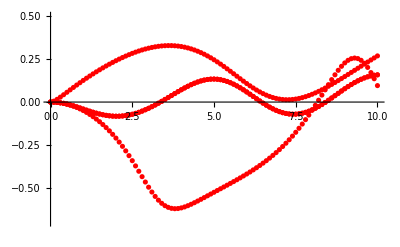

```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange->{Full,{-0.7,0.5}}]
```

## b=r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤100,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.1*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7336576 near {ϕ$7336576} = {5.03136}. NIntegrate obtained 2.18055×10^-15 and 4.95916×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7404290 near {ϕ$7404290} = {1.2639}. NIntegrate obtained -4.03981×10^-14 and 1.47598×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7472992 near {ϕ$7472992} = {1.90204}. NIntegrate obtained 7.66036×10^-14 and 1.146×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

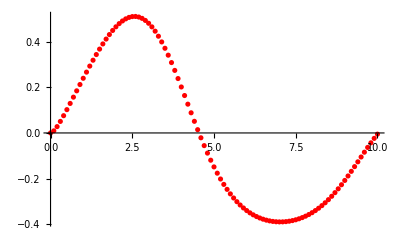

{{0.,{0.,0.}},{0.1,{0.00925124,8.27465×10^-14}},{0.2,{0.0277407,-1.50133×10^-12}},{0.3,{0.0505444,2.8194×10^-12}},{0.4,{0.0756807,-9.27681×10^-13}},{0.5,{0.102135,-1.03348×10^-12}},{0.6,{0.12933,9.80698×10^-18}},{0.7,{0.156906,-4.98578×10^-13}},{0.8,{0.184605,-5.48782×10^-13}},{0.9,{0.212231,-2.75849×10^-13}},{1.,{0.239614,-1.25631×10^-12}},{1.1,{0.266598,5.53302×10^-13}},{1.2,{0.293033,2.82563×10^-11}},{1.3,{0.318766,-1.20454×10^-10}},{1.4,{0.34364,-8.99257×10^-13}},{1.5,{0.367492,-9.37152×10^-13}},{1.6,{0.390154,-1.4567×10^-12}},{1.7,{0.411449,4.5099×10^-13}},{1.8,{0.431194,9.48856×10^-14}},{1.9,{0.4492,2.3599×10^-12}},{2.,{0.465276,-3.3972×10^-11}},{2.1,{0.479227,-6.2629×10^-9}},{2.2,{0.49086,-2.94393×10^-11}},{2.3,{0.499986,-2.93127×10^-11}},{2.4,{0.506425,4.43374×10^-9}},{2.5,{0.510008,5.18982×10^-12}},{2.6,{0.510585,5.73842×10^-17}},{2.7,{0.508029,-1.9527×10^-10}},{2.8,{0.50224,4.25697×10^-11}},{2.9,{0.493153,3.73555×10^-9}},{3.,{0.480743,8.63986×10^-12}},{3.1,{0.465026,2.55268×10^-16}},{3.2,{0.446069,1.18154×10^-16}},{3.3,{0.423986,-7.45961×10^-9}},{3.4,{0.398944,-6.06972×10^-9}},{3.5,{0.371157,1.27496×10^-9}},{3.6,{0.340888,-1.12523×10^-16}},{3.7,{0.30844,7.87168×10^-17}},{3.8,{0.274154,9.78077×10^-9}},{3.9,{0.238394,1.01454×10^-8}},{4.,{0.201546,-8.1355×10^-9}},{4.1,{0.164,6.42962×10^-9}},{4.2,{0.126145,7.12513×10^-17}},{4.3,{0.0883567,-5.59614×10^-17}},{4.4,{0.0509888,-1.34569×10^-9}},{4.5,{0.0143666,2.5746×10^-9}},{4.6,{-0.0212198,2.59401×10^-9}},{4.7,{-0.0555201,7.96077×10^-11}},{4.8,{-0.0883253,6.89556×10^-18}},{4.9,{-0.119469,-8.63143×10^-9}},{5.,{-0.148828,8.41909×10^-10}},{5.1,{-0.176315,3.52365×10^-9}},{5.2,{-0.201884,2.67239×10^-9}},{5.3,{-0.225517,-8.65529×10^-17}},{5.4,{-0.247226,1.04506×10^-15}},{5.5,{-0.267048,-1.52979×10^-16}},{5.6,{-0.285038,-6.51062×10^-9}},{5.7,{-0.301264,7.01124×10^-10}},{5.8,{-0.315808,-1.38009×10^-10}},{5.9,{-0.328755,2.28183×10^-10}},{6.,{-0.340199,7.6996×10^-11}},{6.1,{-0.35023,-9.09407×10^-11}},{6.2,{-0.358938,2.00236×10^-10}},{6.3,{-0.366409,3.30558×10^-12}},{6.4,{-0.372723,-3.89657×10^-10}},{6.5,{-0.377955,-3.83399×10^-9}},{6.6,{-0.382171,2.24748×10^-9}},{6.7,{-0.385426,-7.71764×10^-16}},{6.8,{-0.38777,-4.17934×10^-9}},{6.9,{-0.389241,-1.27753×10^-9}},{7.,{-0.389866,-1.08954×10^-15}},{7.1,{-0.389664,8.38224×10^-11}},{7.2,{-0.388645,-6.06972×10^-16}},{7.3,{-0.386807,2.5715×10^-9}},{7.4,{-0.384144,-4.55827×10^-17}},{7.5,{-0.380636,-1.33452×10^-15}},{7.6,{-0.376261,1.30609×10^-10}},{7.7,{-0.370989,-7.36602×10^-8}},{7.8,{-0.364785,-1.24067×10^-9}},{7.9,{-0.357614,4.40167×10^-10}},{8.,{-0.349436,-1.18102×10^-10}},{8.1,{-0.340216,-5.0124×10^-11}},{8.2,{-0.32992,5.26598×10^-10}},{8.3,{-0.318522,-8.42369×10^-8}},{8.4,{-0.306004,-6.0551×10^-10}},{8.5,{-0.292359,6.95185×10^-11}},{8.6,{-0.277595,1.54378×10^-9}},{8.7,{-0.261737,5.35045×10^-9}},{8.8,{-0.244829,-1.19781×10^-10}},{8.9,{-0.226936,-6.9597×10^-9}},{9.,{-0.208146,-2.45889×10^-9}},{9.1,{-0.188569,1.68392×10^-10}},{9.2,{-0.16834,-1.1195×10^-8}},{9.3,{-0.147614,6.85284×10^-10}},{9.4,{-0.126569,9.5372×10^-8}},{9.5,{-0.105399,7.06821×10^-9}},{9.6,{-0.0843129,3.81114×10^-10}},{9.7,{-0.0635299,-3.32584×10^-9}},{9.8,{-0.0432764,-1.35209×10^-9}},{9.9,{-0.0237779,1.36185×10^-8}},{10.,{-0.0052569,-3.52275×10^-10}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$13500410 near {ϕ$13500410} = {4.2705}. NIntegrate obtained 0.0000563502 and 9.6447×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$13700372 near {ϕ$13700372} = {1.12891}. NIntegrate obtained 0.0000191108 and 2.88583×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$13926405 near {ϕ$13926405} = {3.11695}. NIntegrate obtained -0.00011301 and 1.25038×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

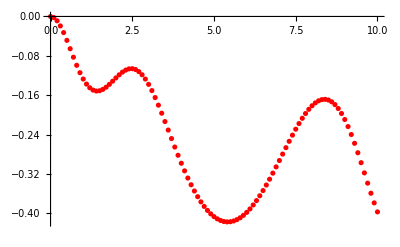

{{0.,{0.,0.}},{0.1,{-0.0022451,-0.000298297}},{0.2,{-0.00880767,-0.00118148}},{0.3,{-0.0192169,-0.00261284}},{0.4,{-0.0327548,-0.00452321}},{0.5,{-0.0485199,-0.00681025}},{0.6,{-0.065511,-0.009341}},{0.7,{-0.0827173,-0.0119567}},{0.8,{-0.099203,-0.0144797}},{0.9,{-0.114171,-0.0167208}},{1.,{-0.127005,-0.0184846}},{1.1,{-0.137282,-0.0195748}},{1.2,{-0.144775,-0.0197984}},{1.3,{-0.149434,-0.0189695}},{1.4,{-0.151361,-0.0169123}},{1.5,{-0.150792,-0.0134663}},{1.6,{-0.148065,-0.00849114}},{1.7,{-0.143602,-0.00187407}},{1.8,{-0.137882,0.00646262}},{1.9,{-0.131428,0.0165532}},{2.,{-0.124778,0.0283801}},{2.1,{-0.118468,0.0418681}},{2.2,{-0.113008,0.0568798}},{2.3,{-0.10886,0.0732159}},{2.4,{-0.106417,0.0906197}},{2.5,{-0.105988,0.108785}},{2.6,{-0.107784,0.127372}},{2.7,{-0.111912,0.14602}},{2.8,{-0.118375,0.164365}},{2.9,{-0.127083,0.182062}},{3.,{-0.137862,0.198793}},{3.1,{-0.150477,0.214286}},{3.2,{-0.164644,0.228315}},{3.3,{-0.180055,0.240712}},{3.4,{-0.196393,0.251359}},{3.5,{-0.213346,0.260189}},{3.6,{-0.230621,0.267181}},{3.7,{-0.247947,0.272348}},{3.8,{-0.265085,0.275737}},{3.9,{-0.281827,0.277417}},{4.,{-0.297996,0.277474}},{4.1,{-0.313442,0.276006}},{4.2,{-0.328046,0.273118}},{4.3,{-0.34171,0.268919}},{4.4,{-0.354358,0.263517}},{4.5,{-0.365928,0.257023}},{4.6,{-0.376377,0.249544}},{4.7,{-0.385669,0.241184}},{4.8,{-0.39378,0.232046}},{4.9,{-0.400694,0.22223}},{5.,{-0.406402,0.211835}},{5.1,{-0.410889,0.200952}},{5.2,{-0.414163,0.18968}},{5.3,{-0.416223,0.178111}},{5.4,{-0.417077,0.166336}},{5.5,{-0.416735,0.154449}},{5.6,{-0.415212,0.142541}},{5.7,{-0.412526,0.130704}},{5.8,{-0.408703,0.119028}},{5.9,{-0.403771,0.10761}},{6.,{-0.397769,0.0965319}},{6.1,{-0.39074,0.0858888}},{6.2,{-0.382734,0.0757654}},{6.3,{-0.37381,0.0662476}},{6.4,{-0.364036,0.0574149}},{6.5,{-0.353488,0.0493426}},{6.6,{-0.342253,0.0421025}},{6.7,{-0.330426,0.0357564}},{6.8,{-0.318112,0.0303606}},{6.9,{-0.305425,0.0259611}},{7.,{-0.292485,0.022593}},{7.1,{-0.279425,0.0202791}},{7.2,{-0.266385,0.019037}},{7.3,{-0.253509,0.0188603}},{7.4,{-0.240949,0.0197358}},{7.5,{-0.228864,0.0216326}},{7.6,{-0.217414,0.0245066}},{7.7,{-0.206763,0.0282965}},{7.8,{-0.197076,0.0329254}},{7.9,{-0.18852,0.0383003}},{8.,{-0.181259,0.0443119}},{8.1,{-0.175453,0.0508339}},{8.2,{-0.171256,0.0577242}},{8.3,{-0.168812,0.0648252}},{8.4,{-0.168255,0.0719641}},{8.5,{-0.169701,0.0789532}},{8.6,{-0.173245,0.0855933}},{8.7,{-0.178956,0.0916756}},{8.8,{-0.186869,0.0969841}},{8.9,{-0.19698,0.101302}},{9.,{-0.209237,0.104414}},{9.1,{-0.223535,0.106116}},{9.2,{-0.239709,0.106225}},{9.3,{-0.257529,0.104584}},{9.4,{-0.276699,0.101076}},{9.5,{-0.296859,0.0956317}},{9.6,{-0.317593,0.0882411}},{9.7,{-0.338439,0.0789544}},{9.8,{-0.358905,0.0678921}},{9.9,{-0.378493,0.05524}},{10.,{-0.396721,0.0412442}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$15589483 near {ϕ$15589483} = {4.50367}. NIntegrate obtained 3.36363×10^-14 and 1.81238×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$15689013 near {ϕ$15689013} = {0.353998}. NIntegrate obtained -8.09752×10^-14 and 9.90661×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$15790388 near {ϕ$15790388} = {2.03703}. NIntegrate obtained 9.3133×10^-17 and 6.14791×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

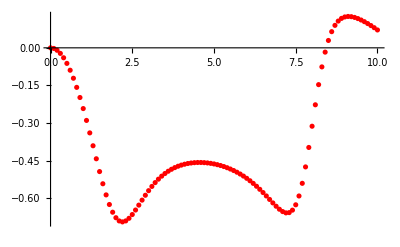

{{0.,{0.,0.}},{0.1,{-0.00243754,4.49245×10^-15}},{0.2,{-0.00980839,-4.52102×10^-14}},{0.3,{-0.0221919,1.23915×10^-16}},{0.4,{-0.0396154,-3.98408×10^-14}},{0.5,{-0.0620339,1.10425×10^-13}},{0.6,{-0.0893263,6.68072×10^-14}},{0.7,{-0.121298,-7.20651×10^-14}},{0.8,{-0.157685,1.83293×10^-13}},{0.9,{-0.198149,3.61017×10^-12}},{1.,{-0.242273,-3.70547×10^-13}},{1.1,{-0.289532,7.93637×10^-15}},{1.2,{-0.339263,5.46693×10^-13}},{1.3,{-0.390612,3.37338×10^-11}},{1.4,{-0.442491,5.9436×10^-12}},{1.5,{-0.493546,-1.37364×10^-13}},{1.6,{-0.542167,-1.32853×10^-12}},{1.7,{-0.586561,-3.3645×10^-12}},{1.8,{-0.62492,-2.35805×10^-11}},{1.9,{-0.655645,-5.50618×10^-12}},{2.,{-0.677615,1.56771×10^-17}},{2.1,{-0.690387,4.55815×10^-9}},{2.2,{-0.694282,-1.64465×10^-16}},{2.3,{-0.690307,4.42589×10^-10}},{2.4,{-0.679955,-6.3285×10^-12}},{2.5,{-0.664932,-1.65424×10^-11}},{2.6,{-0.646913,-6.46777×10^-17}},{2.7,{-0.627366,2.75115×10^-11}},{2.8,{-0.607463,-1.65366×10^-12}},{2.9,{-0.588062,1.26652×10^-11}},{3.,{-0.569738,-1.90247×10^-11}},{3.1,{-0.552836,-2.73058×10^-11}},{3.2,{-0.537527,5.32974×10^-12}},{3.3,{-0.523855,-8.52152×10^-11}},{3.4,{-0.511795,5.46964×10^-12}},{3.5,{-0.501266,2.36221×10^-12}},{3.6,{-0.492163,1.08781×10^-9}},{3.7,{-0.484373,-3.8369×10^-17}},{3.8,{-0.477781,-9.52938×10^-10}},{3.9,{-0.472278,-3.52166×10^-12}},{4.,{-0.467766,2.40441×10^-12}},{4.1,{-0.464157,-2.97686×10^-11}},{4.2,{-0.461373,-1.46114×10^-11}},{4.3,{-0.459349,-3.92185×10^-11}},{4.4,{-0.458032,-1.18911×10^-9}},{4.5,{-0.457377,-2.646×10^-10}},{4.6,{-0.457349,-1.44193×10^-9}},{4.7,{-0.457923,-1.02578×10^-7}},{4.8,{-0.45908,-1.4987×10^-9}},{4.9,{-0.46081,1.3504×10^-9}},{5.,{-0.463108,1.37125×10^-9}},{5.1,{-0.465976,-2.39284×10^-10}},{5.2,{-0.469425,2.78595×10^-8}},{5.3,{-0.473466,9.47108×10^-12}},{5.4,{-0.478118,-3.36327×10^-11}},{5.5,{-0.483405,-1.40042×10^-16}},{5.6,{-0.489354,5.24576×10^-11}},{5.7,{-0.495995,-1.32875×10^-16}},{5.8,{-0.503361,-1.56219×10^-11}},{5.9,{-0.511486,9.81642×10^-16}},{6.,{-0.520401,-2.74762×10^-10}},{6.1,{-0.530133,-7.77833×10^-16}},{6.2,{-0.540699,2.68012×10^-7}},{6.3,{-0.552097,3.03337×10^-7}},{6.4,{-0.564299,2.66712×10^-16}},{6.5,{-0.577233,-1.15406×10^-15}},{6.6,{-0.590759,5.50195×10^-9}},{6.7,{-0.604652,5.66273×10^-12}},{6.8,{-0.618535,-7.82705×10^-11}},{6.9,{-0.631846,-4.73254×10^-9}},{7.,{-0.643758,-2.46894×10^-11}},{7.1,{-0.653096,2.82211×10^-11}},{7.2,{-0.658262,5.86849×10^-12}},{7.3,{-0.657184,1.69162×10^-9}},{7.4,{-0.647364,-2.70479×10^-10}},{7.5,{-0.626095,-2.9069×10^-10}},{7.6,{-0.590927,3.0162×10^-8}},{7.7,{-0.540418,-1.04623×10^-9}},{7.8,{-0.474967,2.56803×10^-10}},{7.9,{-0.39738,2.87921×10^-9}},{8.,{-0.3127,1.49843×10^-10}},{8.1,{-0.227186,2.62072×10^-10}},{8.2,{-0.146816,-8.0224×10^-8}},{8.3,{-0.07602,4.97468×10^-10}},{8.4,{-0.0171377,-4.29043×10^-10}},{8.5,{0.0293966,-7.26664×10^-9}},{8.6,{0.0644736,3.95783×10^-9}},{8.7,{0.0896689,-5.42414×10^-10}},{8.8,{0.106758,1.77302×10^-10}},{8.9,{0.117441,-5.90553×10^-9}},{9.,{0.123171,-6.38262×10^-9}},{9.1,{0.125141,-3.83779×10^-8}},{9.2,{0.12428,5.92206×10^-10}},{9.3,{0.121302,1.87806×10^-8}},{9.4,{0.116716,1.36757×10^-11}},{9.5,{0.110967,-2.62037×10^-10}},{9.6,{0.104284,2.39277×10^-8}},{9.7,{0.096867,2.27296×10^-8}},{9.8,{0.0888565,-3.452×10^-10}},{9.9,{0.0803202,6.54855×10^-10}},{10.,{0.071309,8.4717×10^-9}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22276909 near {ϕ$22276909} = {5.16635}. NIntegrate obtained -0.0000563502 and 9.6447×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22476871 near {ϕ$22476871} = {2.02476}. NIntegrate obtained -0.0000191108 and 2.88583×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22702195 near {ϕ$22702195} = {3.17831}. NIntegrate obtained -0.00011301 and 1.25038×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

{{0.,{0.,0.}},{0.1,{-0.0022451,0.000298297}},{0.2,{-0.00880767,0.00118148}},{0.3,{-0.0192169,0.00261284}},{0.4,{-0.0327548,0.00452321}},{0.5,{-0.0485199,0.00681025}},{0.6,{-0.065511,0.009341}},{0.7,{-0.0827173,0.0119567}},{0.8,{-0.099203,0.0144797}},{0.9,{-0.114171,0.0167208}},{1.,{-0.127005,0.0184846}},{1.1,{-0.137282,0.0195748}},{1.2,{-0.144775,0.0197984}},{1.3,{-0.149434,0.0189695}},{1.4,{-0.151361,0.0169123}},{1.5,{-0.150792,0.0134663}},{1.6,{-0.148065,0.00849114}},{1.7,{-0.143602,0.00187407}},{1.8,{-0.137882,-0.00646262}},{1.9,{-0.131428,-0.0165532}},{2.,{-0.124778,-0.0283801}},{2.1,{-0.118468,-0.0418681}},{2.2,{-0.113008,-0.0568798}},{2.3,{-0.10886,-0.0732159}},{2.4,{-0.106417,-0.0906197}},{2.5,{-0.105988,-0.108785}},{2.6,{-0.107784,-0.127372}},{2.7,{-0.111912,-0.14602}},{2.8,{-0.118375,-0.164365}},{2.9,{-0.127083,-0.182062}},{3.,{-0.137862,-0.198793}},{3.1,{-0.150477,-0.214286}},{3.2,{-0.164644,-0.228315}},{3.3,{-0.180055,-0.240712}},{3.4,{-0.196393,-0.251359}},{3.5,{-0.213346,-0.260189}},{3.6,{-0.230621,-0.267181}},{3.7,{-0.247947,-0.272348}},{3.8,{-0.265085,-0.275737}},{3.9,{-0.281827,-0.277417}},{4.,{-0.297996,-0.277474}},{4.1,{-0.313442,-0.276006}},{4.2,{-0.328046,-0.273118}},{4.3,{-0.34171,-0.268919}},{4.4,{-0.354358,-0.263517}},{4.5,{-0.365928,-0.257023}},{4.6,{-0.376377,-0.249544}},{4.7,{-0.385669,-0.241184}},{4.8,{-0.39378,-0.232046}},{4.9,{-0.400694,-0.22223}},{5.,{-0.406402,-0.211835}},{5.1,{-0.410889,-0.200952}},{5.2,{-0.414163,-0.18968}},{5.3,{-0.416223,-0.178111}},{5.4,{-0.417077,-0.166336}},{5.5,{-0.416735,-0.154449}},{5.6,{-0.415212,-0.142541}},{5.7,{-0.412526,-0.130704}},{5.8,{-0.408703,-0.119028}},{5.9,{-0.403771,-0.10761}},{6.,{-0.397769,-0.0965319}},{6.1,{-0.39074,-0.0858888}},{6.2,{-0.382734,-0.0757654}},{6.3,{-0.37381,-0.0662476}},{6.4,{-0.364036,-0.0574149}},{6.5,{-0.353488,-0.0493426}},{6.6,{-0.342253,-0.0421025}},{6.7,{-0.330426,-0.0357564}},{6.8,{-0.318112,-0.0303606}},{6.9,{-0.305425,-0.0259611}},{7.,{-0.292485,-0.022593}},{7.1,{-0.279425,-0.0202791}},{7.2,{-0.266385,-0.019037}},{7.3,{-0.253509,-0.0188603}},{7.4,{-0.240949,-0.0197358}},{7.5,{-0.228864,-0.0216326}},{7.6,{-0.217414,-0.0245066}},{7.7,{-0.206763,-0.0282965}},{7.8,{-0.197076,-0.0329254}},{7.9,{-0.18852,-0.0383003}},{8.,{-0.181259,-0.0443119}},{8.1,{-0.175453,-0.0508339}},{8.2,{-0.171256,-0.0577242}},{8.3,{-0.168812,-0.0648252}},{8.4,{-0.168255,-0.0719641}},{8.5,{-0.169701,-0.0789532}},{8.6,{-0.173245,-0.0855933}},{8.7,{-0.178956,-0.0916756}},{8.8,{-0.186869,-0.0969841}},{8.9,{-0.19698,-0.101302}},{9.,{-0.209237,-0.104414}},{9.1,{-0.223535,-0.106116}},{9.2,{-0.239709,-0.106225}},{9.3,{-0.257529,-0.104584}},{9.4,{-0.276699,-0.101076}},{9.5,{-0.296859,-0.0956317}},{9.6,{-0.317593,-0.0882411}},{9.7,{-0.338439,-0.0789544}},{9.8,{-0.358905,-0.0678921}},{9.9,{-0.378493,-0.05524}},{10.,{-0.396721,-0.0412442}}}

```mathematica
Getv2kT[1.0, 0]
Getv2kT[1.0, π/4]
Getv2kT[1.0, π/2]
Getv2kT[1.0, (3π)/4]
```

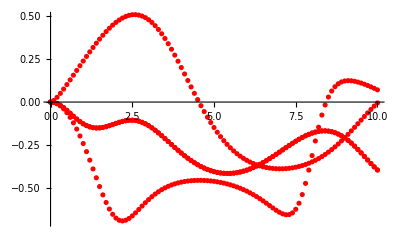

```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange->{Full,{-0.7,0.5}}]
```

## b=1.5 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤100,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.1*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56199033 near {ϕ$56199033} = {1.81614}. NIntegrate obtained 1.47156×10^-14 and 9.43033×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56254205 near {ϕ$56254205} = {4.25823}. NIntegrate obtained -1.6507×10^-17 and 7.9723×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56320566 near {ϕ$56320566} = {1.32526}. NIntegrate obtained -6.23205×10^-15 and 1.14267×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

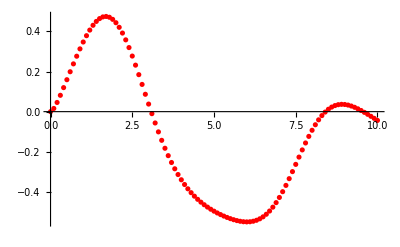

{{0.,{0.,0.}},{0.1,{0.0158879,9.64668×10^-13}},{0.2,{0.0458616,-1.07208×10^-15}},{0.3,{0.0815153,-4.09624×10^-13}},{0.4,{0.119818,-1.82998×10^-12}},{0.5,{0.159285,-1.87609×10^-14}},{0.6,{0.199,-1.70912×10^-12}},{0.7,{0.238269,-1.97728×10^-12}},{0.8,{0.27648,4.76748×10^-13}},{0.9,{0.313041,4.52046×10^-17}},{1.,{0.347358,5.58815×10^-17}},{1.1,{0.378824,1.95209×10^-16}},{1.2,{0.406823,2.51137×10^-16}},{1.3,{0.430746,-5.74068×10^-14}},{1.4,{0.450004,-1.66838×10^-12}},{1.5,{0.464056,1.01799×10^-11}},{1.6,{0.47243,1.02454×10^-16}},{1.7,{0.47475,1.66501×10^-11}},{1.8,{0.470763,-6.15906×10^-11}},{1.9,{0.46036,-1.16707×10^-11}},{2.,{0.443589,1.62347×10^-12}},{2.1,{0.420668,7.0792×10^-13}},{2.2,{0.391976,-2.21631×10^-16}},{2.3,{0.358044,-1.56833×10^-16}},{2.4,{0.319537,-2.16971×10^-16}},{2.5,{0.277218,1.91315×10^-16}},{2.6,{0.231917,5.69302×10^-10}},{2.7,{0.184495,-3.02381×10^-11}},{2.8,{0.135805,-3.6889×10^-10}},{2.9,{0.0866613,5.91836×10^-18}},{3.,{0.0378089,-7.57668×10^-12}},{3.1,{-0.0100914,4.1832×10^-17}},{3.2,{-0.0564817,5.43498×10^-11}},{3.3,{-0.100911,-4.25943×10^-16}},{3.4,{-0.143034,1.28518×10^-9}},{3.5,{-0.18261,-2.34243×10^-9}},{3.6,{-0.219491,2.54257×10^-9}},{3.7,{-0.253612,-2.15183×10^-11}},{3.8,{-0.284979,-1.24372×10^-11}},{3.9,{-0.313656,-2.55201×10^-16}},{4.,{-0.339753,-2.12827×10^-10}},{4.1,{-0.363414,3.73641×10^-11}},{4.2,{-0.384808,-4.79451×10^-16}},{4.3,{-0.404118,1.09812×10^-8}},{4.4,{-0.421535,3.42594×10^-17}},{4.5,{-0.43725,3.49901×10^-11}},{4.6,{-0.451446,-1.47034×10^-9}},{4.7,{-0.464301,-8.03519×10^-12}},{4.8,{-0.475977,2.14877×10^-10}},{4.9,{-0.486613,-2.33232×10^-10}},{5.,{-0.496334,1.63896×10^-10}},{5.1,{-0.505237,-1.50683×10^-15}},{5.2,{-0.513393,8.40477×10^-10}},{5.3,{-0.520846,-2.29756×10^-9}},{5.4,{-0.527607,9.09396×10^-16}},{5.5,{-0.533654,2.91953×10^-10}},{5.6,{-0.53893,9.35365×10^-11}},{5.7,{-0.543339,-1.42807×10^-15}},{5.8,{-0.546751,-8.10484×10^-16}},{5.9,{-0.548995,-1.06545×10^-15}},{6.,{-0.549866,4.15068×10^-17}},{6.1,{-0.549125,-8.08664×10^-16}},{6.2,{-0.54651,1.90033×10^-9}},{6.3,{-0.541739,-3.21499×10^-16}},{6.4,{-0.534526,4.39672×10^-10}},{6.5,{-0.524599,1.05915×10^-10}},{6.6,{-0.511714,1.95311×10^-9}},{6.7,{-0.495679,-1.0616×10^-7}},{6.8,{-0.476375,7.88284×10^-10}},{6.9,{-0.453781,-8.93072×10^-10}},{7.,{-0.427989,-1.14607×10^-15}},{7.1,{-0.399216,4.96065×10^-9}},{7.2,{-0.367808,3.12075×10^-15}},{7.3,{-0.334236,-1.58374×10^-9}},{7.4,{-0.299076,-1.75137×10^-10}},{7.5,{-0.262986,-1.54284×10^-10}},{7.6,{-0.226672,-2.44119×10^-9}},{7.7,{-0.190848,2.64869×10^-9}},{7.8,{-0.156211,-2.35807×10^-9}},{7.9,{-0.123391,-7.26596×10^-9}},{8.,{-0.0929439,-2.69127×10^-9}},{8.1,{-0.0653152,1.12873×10^-9}},{8.2,{-0.0408405,4.05352×10^-10}},{8.3,{-0.0197377,-8.28807×10^-8}},{8.4,{-0.00213101,-2.52399×10^-9}},{8.5,{0.0120134,-4.34546×10^-11}},{8.6,{0.0227509,-6.07247×10^-9}},{8.7,{0.0302469,8.41329×10^-10}},{8.8,{0.0347197,1.18884×10^-8}},{8.9,{0.0364341,1.12287×10^-9}},{9.,{0.0356781,2.95411×10^-9}},{9.1,{0.0327645,2.20816×10^-9}},{9.2,{0.0280071,-3.8465×10^-9}},{9.3,{0.0217136,-5.13493×10^-9}},{9.4,{0.0141794,4.08048×10^-9}},{9.5,{0.00567759,-5.32154×10^-8}},{9.6,{-0.00354277,4.53744×10^-10}},{9.7,{-0.0132639,2.53243×10^-7}},{9.8,{-0.0232942,1.7853×10^-8}},{9.9,{-0.0334782,5.34216×10^-12}},{10.,{-0.0436919,1.85163×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$62824191 near {ϕ$62824191} = {4.97}. NIntegrate obtained 8.24807×10^-6 and 1.22922×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$62889938 near {ϕ$62889938} = {5.71858}. NIntegrate obtained 7.18319×10^-6 and 8.70689×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$63028808 near {ϕ$63028808} = {5.65722}. NIntegrate obtained 6.11206×10^-6 and 7.14485×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

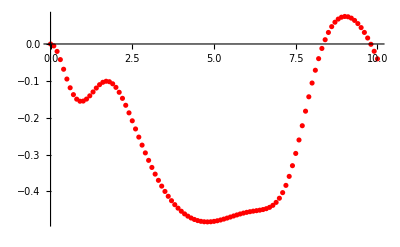

{{0.,{0.,0.}},{0.1,{-0.00526232,-0.0015394}},{0.2,{-0.0201689,-0.0061223}},{0.3,{-0.0423673,-0.0134791}},{0.4,{-0.0685404,-0.0229836}},{0.5,{-0.0950914,-0.0336976}},{0.6,{-0.118828,-0.0444931}},{0.7,{-0.137438,-0.054194}},{0.8,{-0.14967,-0.0616922}},{0.9,{-0.155279,-0.0660229}},{1.,{-0.154828,-0.066407}},{1.1,{-0.149463,-0.0622808}},{1.2,{-0.140686,-0.0533212}},{1.3,{-0.130166,-0.0394715}},{1.4,{-0.119567,-0.0209596}},{1.5,{-0.110412,0.00170349}},{1.6,{-0.103956,0.0277508}},{1.7,{-0.101114,0.0562185}},{1.8,{-0.102412,0.0860299}},{1.9,{-0.107998,0.11609}},{2.,{-0.117691,0.145376}},{2.1,{-0.131054,0.173008}},{2.2,{-0.147486,0.19829}},{2.3,{-0.166309,0.220729}},{2.4,{-0.186836,0.240022}},{2.5,{-0.208424,0.256034}},{2.6,{-0.230511,0.268761}},{2.7,{-0.252623,0.278299}},{2.8,{-0.274379,0.284813}},{2.9,{-0.295486,0.288506}},{3.,{-0.315727,0.289605}},{3.1,{-0.334946,0.288344}},{3.2,{-0.353038,0.284954}},{3.3,{-0.369939,0.279657}},{3.4,{-0.385611,0.272668}},{3.5,{-0.400038,0.264188}},{3.6,{-0.413219,0.254405}},{3.7,{-0.425164,0.243503}},{3.8,{-0.43589,0.231654}},{3.9,{-0.445418,0.219026}},{4.,{-0.453774,0.205783}},{4.1,{-0.460988,0.192085}},{4.2,{-0.467089,0.17809}},{4.3,{-0.472115,0.163972}},{4.4,{-0.476104,0.149861}},{4.5,{-0.479101,0.135942}},{4.6,{-0.481156,0.122366}},{4.7,{-0.482329,0.109293}},{4.8,{-0.482684,0.0968785}},{4.9,{-0.482294,0.0852705}},{5.,{-0.481242,0.074618}},{5.1,{-0.479621,0.0650552}},{5.2,{-0.477526,0.0567062}},{5.3,{-0.475067,0.0496797}},{5.4,{-0.472353,0.0440661}},{5.5,{-0.469501,0.0399332}},{5.6,{-0.466621,0.037324}},{5.7,{-0.463822,0.0362473}},{5.8,{-0.4612,0.0366827}},{5.9,{-0.458831,0.0385631}},{6.,{-0.456764,0.0417819}},{6.1,{-0.455011,0.0461775}},{6.2,{-0.453528,0.0515318}},{6.3,{-0.452207,0.0575647}},{6.4,{-0.450858,0.0639288}},{6.5,{-0.449192,0.0702085}},{6.6,{-0.446814,0.0759269}},{6.7,{-0.443208,0.0805452}},{6.8,{-0.437755,0.0835071}},{6.9,{-0.429761,0.0842636}},{7.,{-0.418495,0.0823332}},{7.1,{-0.40329,0.0773625}},{7.2,{-0.383612,0.0692063}},{7.3,{-0.359206,0.0579866}},{7.4,{-0.330154,0.0441172}},{7.5,{-0.296942,0.0282919}},{7.6,{-0.260431,0.0114092}},{7.7,{-0.221782,-0.00552378}},{7.8,{-0.182295,-0.021525}},{7.9,{-0.143286,-0.035755}},{8.,{-0.105938,-0.0475804}},{8.1,{-0.071225,-0.0566132}},{8.2,{-0.039796,-0.0626817}},{8.3,{-0.0121262,-0.0658283}},{8.4,{0.011577,-0.0662282}},{8.5,{0.0312757,-0.0641484}},{8.6,{0.0470517,-0.0599056}},{8.7,{0.0590689,-0.0538303}},{8.8,{0.0675292,-0.0462439}},{8.9,{0.0726553,-0.0374499}},{9.,{0.0746625,-0.0277175}},{9.1,{0.0737577,-0.0172891}},{9.2,{0.0701223,-0.00637774}},{9.3,{0.0639244,0.00483388}},{9.4,{0.0553094,0.0161841}},{9.5,{0.0444043,0.0275296}},{9.6,{0.0313284,0.0387445}},{9.7,{0.0161951,0.0497116}},{9.8,{-0.000881344,0.0603252}},{9.9,{-0.0197792,0.0704646}},{10.,{-0.0403511,0.0800448}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66248164 near {ϕ$66248164} = {2.57699}. NIntegrate obtained -5.79918×10^-14 and 4.34858×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66334164 near {ϕ$66334164} = {2.54017}. NIntegrate obtained 3.81639×10^-17 and 7.07221×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66409545 near {ϕ$66409545} = {2.08612}. NIntegrate obtained 1.36774×10^-14 and 6.08748×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

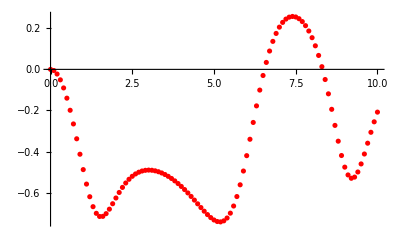

{{0.,{0.,0.}},{0.1,{-0.00561452,-2.78926×10^-14}},{0.2,{-0.0225849,7.86261×10^-17}},{0.3,{-0.0509339,6.90473×10^-14}},{0.4,{-0.0903293,-1.21201×10^-13}},{0.5,{-0.140044,1.32964×10^-14}},{0.6,{-0.198955,-3.21052×10^-13}},{0.7,{-0.265525,1.00451×10^-13}},{0.8,{-0.33773,1.79744×10^-16}},{0.9,{-0.412932,7.68883×10^-13}},{1.,{-0.487772,-1.53533×10^-11}},{1.1,{-0.558186,1.13589×10^-11}},{1.2,{-0.619706,-1.16503×10^-9}},{1.3,{-0.668135,-4.01119×10^-12}},{1.4,{-0.700477,1.4417×10^-16}},{1.5,{-0.715747,-1.8207×10^-13}},{1.6,{-0.715238,-4.88793×10^-12}},{1.7,{-0.702073,-4.64447×10^-13}},{1.8,{-0.68027,1.74475×10^-10}},{1.9,{-0.653793,3.3269×10^-17}},{2.,{-0.625911,-1.57978×10^-16}},{2.1,{-0.598958,1.48452×10^-10}},{2.2,{-0.574384,1.93523×10^-16}},{2.3,{-0.552942,1.11253×10^-16}},{2.4,{-0.53491,7.95821×10^-12}},{2.5,{-0.520267,-2.0939×10^-11}},{2.6,{-0.508836,-1.59413×10^-16}},{2.7,{-0.500365,4.47267×10^-11}},{2.8,{-0.494585,2.25247×10^-16}},{2.9,{-0.49124,-1.10905×10^-8}},{3.,{-0.490097,5.85681×10^-9}},{3.1,{-0.490963,5.95402×10^-11}},{3.2,{-0.493669,-3.0332×10^-16}},{3.3,{-0.498082,-1.7945×10^-16}},{3.4,{-0.504092,-2.85866×10^-12}},{3.5,{-0.511613,2.68335×10^-9}},{3.6,{-0.520572,6.90971×10^-19}},{3.7,{-0.530913,2.25862×10^-7}},{3.8,{-0.542577,-9.08963×10^-10}},{3.9,{-0.555509,6.16885×10^-17}},{4.,{-0.569645,9.20318×10^-11}},{4.1,{-0.584903,1.70245×10^-8}},{4.2,{-0.601174,9.93357×10^-13}},{4.3,{-0.618307,-7.65806×10^-12}},{4.4,{-0.636097,-4.28602×10^-9}},{4.5,{-0.654264,-3.04846×10^-12}},{4.6,{-0.672432,4.67136×10^-12}},{4.7,{-0.690106,-4.72678×10^-10}},{4.8,{-0.706641,2.50147×10^-8}},{4.9,{-0.72122,-8.54694×10^-16}},{5.,{-0.732837,2.20703×10^-8}},{5.1,{-0.740287,8.7922×10^-11}},{5.2,{-0.742201,-4.01636×10^-11}},{5.3,{-0.737036,-2.42627×10^-10}},{5.4,{-0.723303,3.76576×10^-11}},{5.5,{-0.699615,2.39058×10^-10}},{5.6,{-0.664949,-3.10323×10^-11}},{5.7,{-0.61886,1.86683×10^-10}},{5.8,{-0.561689,3.03292×10^-8}},{5.9,{-0.494666,2.11589×10^-12}},{6.,{-0.419878,4.46571×10^-9}},{6.1,{-0.340063,-7.27088×10^-9}},{6.2,{-0.258302,6.19072×10^-16}},{6.3,{-0.177662,3.59178×10^-8}},{6.4,{-0.100768,1.4698×10^-9}},{6.5,{-0.0297911,-3.53894×10^-8}},{6.6,{0.0338352,-1.0583×10^-9}},{6.7,{0.0892926,-3.84732×10^-8}},{6.8,{0.13629,3.33952×10^-9}},{6.9,{0.174928,-5.08429×10^-8}},{7.,{0.205554,-7.45544×10^-7}},{7.1,{0.22864,-4.00235×10^-9}},{7.2,{0.244698,-8.79485×10^-8}},{7.3,{0.254195,-6.08001×10^-8}},{7.4,{0.257531,4.33346×10^-8}},{7.5,{0.254975,-1.24656×10^-7}},{7.6,{0.246678,-3.5935×10^-9}},{7.7,{0.232652,-4.58009×10^-15}},{7.8,{0.212762,-7.7584×10^-11}},{7.9,{0.186746,-7.61748×10^-8}},{8.,{0.154221,8.41632×10^-7}},{8.1,{0.114733,-8.60044×10^-10}},{8.2,{0.0678223,-1.09792×10^-7}},{8.3,{0.0131481,3.68157×10^-8}},{8.4,{-0.0493131,-4.10646×10^-15}},{8.5,{-0.11898,9.54714×10^-10}},{8.6,{-0.194349,-4.74871×10^-8}},{8.7,{-0.272594,1.63063×10^-9}},{8.8,{-0.349407,6.62185×10^-12}},{8.9,{-0.419166,-3.25488×10^-7}},{9.,{-0.475717,1.73299×10^-7}},{9.1,{-0.513682,7.71037×10^-11}},{9.2,{-0.529884,-2.41813×10^-9}},{9.3,{-0.524186,2.70151×10^-9}},{9.4,{-0.499362,8.51703×10^-10}},{9.5,{-0.460133,1.41197×10^-9}},{9.6,{-0.411802,-2.56136×10^-9}},{9.7,{-0.359195,-6.76348×10^-7}},{9.8,{-0.306114,-2.92889×10^-9}},{9.9,{-0.255182,2.90967×10^-9}},{10.,{-0.208009,-7.586×10^-9}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$72416370 near {ϕ$72416370} = {4.46685}. NIntegrate obtained -8.24807×10^-6 and 1.22922×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$72482117 near {ϕ$72482117} = {3.71827}. NIntegrate obtained -7.18319×10^-6 and 8.70689×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$72620987 near {ϕ$72620987} = {0.638038}. NIntegrate obtained -6.11206×10^-6 and 7.14485×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

{{0.,{0.,0.}},{0.1,{-0.00526232,0.0015394}},{0.2,{-0.0201689,0.0061223}},{0.3,{-0.0423673,0.0134791}},{0.4,{-0.0685404,0.0229836}},{0.5,{-0.0950914,0.0336976}},{0.6,{-0.118828,0.0444931}},{0.7,{-0.137438,0.054194}},{0.8,{-0.14967,0.0616922}},{0.9,{-0.155279,0.0660229}},{1.,{-0.154828,0.066407}},{1.1,{-0.149463,0.0622808}},{1.2,{-0.140686,0.0533212}},{1.3,{-0.130166,0.0394715}},{1.4,{-0.119567,0.0209596}},{1.5,{-0.110412,-0.00170349}},{1.6,{-0.103956,-0.0277508}},{1.7,{-0.101114,-0.0562185}},{1.8,{-0.102412,-0.0860299}},{1.9,{-0.107998,-0.11609}},{2.,{-0.117691,-0.145376}},{2.1,{-0.131054,-0.173008}},{2.2,{-0.147486,-0.19829}},{2.3,{-0.166309,-0.220729}},{2.4,{-0.186836,-0.240022}},{2.5,{-0.208424,-0.256034}},{2.6,{-0.230511,-0.268761}},{2.7,{-0.252623,-0.278299}},{2.8,{-0.274379,-0.284813}},{2.9,{-0.295486,-0.288506}},{3.,{-0.315727,-0.289605}},{3.1,{-0.334946,-0.288344}},{3.2,{-0.353038,-0.284954}},{3.3,{-0.369939,-0.279657}},{3.4,{-0.385611,-0.272668}},{3.5,{-0.400038,-0.264188}},{3.6,{-0.413219,-0.254405}},{3.7,{-0.425164,-0.243503}},{3.8,{-0.43589,-0.231654}},{3.9,{-0.445418,-0.219026}},{4.,{-0.453774,-0.205783}},{4.1,{-0.460988,-0.192085}},{4.2,{-0.467089,-0.17809}},{4.3,{-0.472115,-0.163972}},{4.4,{-0.476104,-0.149861}},{4.5,{-0.479101,-0.135942}},{4.6,{-0.481156,-0.122366}},{4.7,{-0.482329,-0.109293}},{4.8,{-0.482684,-0.0968785}},{4.9,{-0.482294,-0.0852705}},{5.,{-0.481242,-0.074618}},{5.1,{-0.479621,-0.0650552}},{5.2,{-0.477526,-0.0567062}},{5.3,{-0.475067,-0.0496797}},{5.4,{-0.472353,-0.0440661}},{5.5,{-0.469501,-0.0399332}},{5.6,{-0.466621,-0.037324}},{5.7,{-0.463822,-0.0362473}},{5.8,{-0.4612,-0.0366827}},{5.9,{-0.458831,-0.0385631}},{6.,{-0.456764,-0.0417819}},{6.1,{-0.455011,-0.0461775}},{6.2,{-0.453528,-0.0515318}},{6.3,{-0.452207,-0.0575647}},{6.4,{-0.450858,-0.0639288}},{6.5,{-0.449192,-0.0702085}},{6.6,{-0.446814,-0.0759269}},{6.7,{-0.443208,-0.0805452}},{6.8,{-0.437755,-0.0835071}},{6.9,{-0.429761,-0.0842636}},{7.,{-0.418495,-0.0823332}},{7.1,{-0.40329,-0.0773625}},{7.2,{-0.383612,-0.0692063}},{7.3,{-0.359206,-0.0579866}},{7.4,{-0.330154,-0.0441172}},{7.5,{-0.296942,-0.0282919}},{7.6,{-0.260431,-0.0114092}},{7.7,{-0.221782,0.00552378}},{7.8,{-0.182295,0.021525}},{7.9,{-0.143286,0.035755}},{8.,{-0.105938,0.0475804}},{8.1,{-0.071225,0.0566132}},{8.2,{-0.039796,0.0626817}},{8.3,{-0.0121262,0.0658283}},{8.4,{0.011577,0.0662282}},{8.5,{0.0312757,0.0641484}},{8.6,{0.0470517,0.0599056}},{8.7,{0.0590689,0.0538303}},{8.8,{0.0675292,0.0462439}},{8.9,{0.0726553,0.0374499}},{9.,{0.0746625,0.0277175}},{9.1,{0.0737577,0.0172891}},{9.2,{0.0701223,0.00637774}},{9.3,{0.0639244,-0.00483388}},{9.4,{0.0553094,-0.0161841}},{9.5,{0.0444043,-0.0275296}},{9.6,{0.0313284,-0.0387445}},{9.7,{0.0161951,-0.0497116}},{9.8,{-0.000881344,-0.0603252}},{9.9,{-0.0197792,-0.0704646}},{10.,{-0.0403511,-0.0800448}}}

```mathematica
Getv2kT[1.5, 0]
Getv2kT[1.5, π/4]
Getv2kT[1.5, π/2]
Getv2kT[1.5, (3π)/4]
```

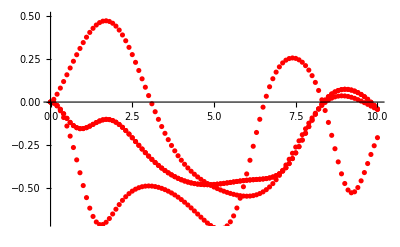

```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange->{Full,{-0.7,0.5}}]
```

## b=2 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$158493626 near {ϕ$158493626} = {1.37435}. NIntegrate obtained -2.06269×10^-17 and 9.48423×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$158550967 near {ϕ$158550967} = {2.19656}. NIntegrate obtained 6.57298×10^-18 and 2.30533×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$158639304 near {ϕ$158639304} = {2.34382}. NIntegrate obtained 7.00981×10^-13 and 4.60964×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

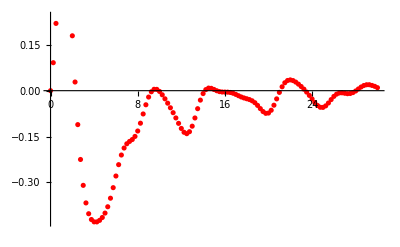

{{0.,{0.,0.}},{0.25,{0.0914692,-2.25819×10^-15}},{0.5,{0.219951,8.45298×10^-16}},{0.75,{0.338648,1.15009×10^-10}},{1.,{0.423828,-3.44537×10^-12}},{1.25,{0.454093,-8.14022×10^-12}},{1.5,{0.417351,2.19433×10^-16}},{1.75,{0.318608,4.55358×10^-16}},{2.,{0.179477,2.59183×10^-8}},{2.25,{0.0283476,5.46637×10^-11}},{2.5,{-0.110989,-2.78722×10^-16}},{2.75,{-0.224955,-6.31442×10^-9}},{3.,{-0.30956,-2.06935×10^-10}},{3.25,{-0.367005,-1.63358×10^-16}},{3.5,{-0.402355,5.09583×10^-10}},{3.75,{-0.421302,-4.30508×10^-10}},{4.,{-0.428923,6.39035×10^-10}},{4.25,{-0.429065,-4.69288×10^-16}},{4.5,{-0.42406,4.49748×10^-16}},{4.75,{-0.414662,5.22327×10^-9}},{5.,{-0.400264,-5.73366×10^-13}},{5.25,{-0.379548,-1.69863×10^-10}},{5.5,{-0.351599,3.32428×10^-8}},{5.75,{-0.317118,-1.61182×10^-7}},{6.,{-0.279054,6.33698×10^-10}},{6.25,{-0.241919,6.01736×10^-8}},{6.5,{-0.210392,4.31863×10^-16}},{6.75,{-0.187514,-5.83275×10^-15}},{7.,{-0.173602,2.36766×10^-9}},{7.25,{-0.165986,-1.87058×10^-9}},{7.5,{-0.159766,2.05166×10^-7}},{7.75,{-0.14958,1.80396×10^-7}},{8.,{-0.131845,-1.39088×10^-15}},{8.25,{-0.106335,2.56724×10^-9}},{8.5,{-0.076131,-3.21408×10^-9}},{8.75,{-0.0460762,-1.08691×10^-8}},{9.,{-0.0208543,1.1718×10^-8}},{9.25,{-0.00360429,-7.59434×10^-9}},{9.5,{0.00452248,-7.91393×10^-9}},{9.75,{0.00426449,3.11091×10^-8}},{10.,{-0.00247482,-3.03206×10^-9}},{10.25,{-0.0134131,1.2407×10^-7}},{10.5,{-0.0265804,-2.78618×10^-8}},{10.75,{-0.0408566,-2.5644×10^-8}},{11.,{-0.0559158,6.05462×10^-15}},{11.25,{-0.0719532,1.42335×10^-8}},{11.5,{-0.0891097,-5.14607×10^-8}},{11.75,{-0.106859,-7.89368×10^-9}},{12.,{-0.123499,-1.33322×10^-9}},{12.25,{-0.135998,-1.29984×10^-8}},{12.5,{-0.140579,-5.78521×10^-8}},{12.75,{-0.134134,7.357×10^-8}},{13.,{-0.116096,-6.63947×10^-8}},{13.25,{-0.0892311,-1.0355×10^-7}},{13.5,{-0.0588946,-1.83008×10^-8}},{13.75,{-0.0308639,-2.51244×10^-7}},{14.,{-0.00947254,-2.48306×10^-7}},{14.25,{0.00346679,-1.4906×10^-7}},{14.5,{0.00848907,-3.28962×10^-8}},{14.75,{0.00768199,1.32312×10^-8}},{15.,{0.00398578,2.19936×10^-7}},{15.25,{-0.000131092,-9.67569×10^-8}},{15.5,{-0.00303854,1.56712×10^-7}},{15.75,{-0.00433915,3.37367×10^-7}},{16.,{-0.00458722,-4.50608×10^-7}},{16.25,{-0.00479049,-5.48362×10^-7}},{16.5,{-0.00587796,6.82073×10^-7}},{16.75,{-0.00841273,-5.87948×10^-7}},{17.,{-0.0121729,1.85463×10^-7}},{17.25,{-0.016491,-2.35383×10^-7}},{17.5,{-0.020528,1.72853×10^-7}},{17.75,{-0.0237649,-5.1142×10^-8}},{18.,{-0.0263627,-1.8253×10^-7}},{18.25,{-0.0290597,-9.94404×10^-8}},{18.5,{-0.0330716,-3.40304×10^-7}},{18.75,{-0.0393741,-3.09773×10^-8}},{19.,{-0.048193,1.99535×10^-7}},{19.25,{-0.0586032,4.90618×10^-7}},{19.5,{-0.0682412,-7.77186×10^-7}},{19.75,{-0.0740831,-9.75373×10^-7}},{20.,{-0.0731277,1.2299×10^-6}},{20.25,{-0.0639966,-1.27638×10^-6}},{20.5,{-0.0475329,9.46713×10^-7}},{20.75,{-0.0268091,-2.82186×10^-6}},{21.,{-0.0055536,-7.18867×10^-7}},{21.25,{0.0127274,-1.70799×10^-6}},{21.5,{0.0259141,3.4358×10^-6}},{21.75,{0.0332841,3.37335×10^-6}},{22.,{0.0352588,3.84906×10^-6}},{22.25,{0.0330753,1.80528×10^-6}},{22.5,{0.0280745,6.30441×10^-6}},{22.75,{0.021351,4.88702×10^-7}},{23.,{0.013645,1.34741×10^-7}},{23.25,{0.0050491,-9.32004×10^-7}},{23.5,{-0.00463539,5.66849×10^-6}},{23.75,{-0.0154891,1.92677×10^-7}},{24.,{-0.0271387,-2.87872×10^-6}},{24.25,{-0.0387333,5.48946×10^-6}},{24.5,{-0.0483992,2.09904×10^-6}},{24.75,{-0.0541943,-0.0000106471}},{25.,{-0.0546847,-4.51666×10^-6}},{25.25,{-0.049651,1.27372×10^-6}},{25.5,{-0.0402667,-1.74774×10^-7}},{25.75,{-0.0291555,-3.61168×10^-6}},{26.,{-0.0186881,-9.00787×10^-7}},{26.25,{-0.0112427,2.7615×10^-6}},{26.5,{-0.00749574,-2.18299×10^-6}},{26.75,{-0.00701853,-8.7257×10^-7}},{27.,{-0.00842041,0.000011617}},{27.25,{-0.00977186,0.0000102923}},{27.5,{-0.00922519,6.52152×10^-6}},{27.75,{-0.00624266,5.72196×10^-6}},{28.,{-0.000997513,4.36862×10^-6}},{28.25,{0.0055717,-3.19094×10^-7}},{28.5,{0.0119802,-3.89803×10^-6}},{28.75,{0.0168823,-1.21592×10^-6}},{29.,{0.0193717,2.54736×10^-6}},{29.25,{0.0195078,-0.0000121878}},{29.5,{0.0171472,-4.57868×10^-6}},{29.75,{0.0141927,0.000100031}},{30.,{0.00982964,4.08762×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$168057366 near {ϕ$168057366} = {1.28845}. NIntegrate obtained 9.2304×10^-6 and 9.90875×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$168117354 near {ϕ$168117354} = {1.32526}. NIntegrate obtained 6.89656×10^-6 and 9.77293×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$168254971 near {ϕ$168254971} = {3.92689}. NIntegrate obtained 1.44194×10^-6 and 3.84176×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

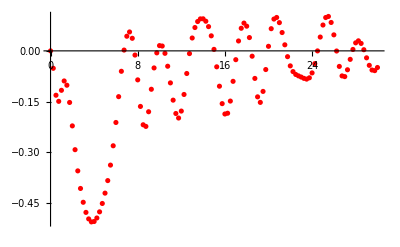

{{0.,{0.,0.}},{0.25,{-0.0515924,-0.0214413}},{0.5,{-0.131414,-0.0670046}},{0.75,{-0.149492,-0.0898515}},{1.,{-0.116828,-0.0588104}},{1.25,{-0.0891145,0.0229141}},{1.5,{-0.101749,0.124469}},{1.75,{-0.152791,0.211759}},{2.,{-0.222183,0.267765}},{2.25,{-0.292667,0.291885}},{2.5,{-0.355446,0.290475}},{2.75,{-0.407526,0.270748}},{3.,{-0.44844,0.238971}},{3.25,{-0.478416,0.20061}},{3.5,{-0.49771,0.160852}},{3.75,{-0.506554,0.124879}},{4.,{-0.505374,0.0976363}},{4.25,{-0.495017,0.083027}},{4.5,{-0.476767,0.0826468}},{4.75,{-0.451981,0.0944459}},{5.,{-0.421369,0.111951}},{5.25,{-0.384238,0.124818}},{5.5,{-0.338339,0.121387}},{5.75,{-0.281098,0.0933171}},{6.,{-0.212106,0.0405508}},{6.25,{-0.1356,-0.0268097}},{6.5,{-0.0604812,-0.0923272}},{6.75,{0.00235232,-0.140627}},{7.,{0.0433465,-0.162909}},{7.25,{0.0560415,-0.157705}},{7.5,{0.0372457,-0.128601}},{7.75,{-0.0124552,-0.0819614}},{8.,{-0.0858996,-0.0263321}},{8.25,{-0.164578,0.0271155}},{8.5,{-0.218877,0.0661601}},{8.75,{-0.223742,0.083789}},{9.,{-0.180303,0.0836363}},{9.25,{-0.113704,0.0757756}},{9.5,{-0.0505423,0.0682882}},{9.75,{-0.00590628,0.063925}},{10.,{0.0155667,0.0621166}},{10.25,{0.0143087,0.0610959}},{10.5,{-0.00725427,0.0590591}},{10.75,{-0.0455129,0.0546348}},{11.,{-0.0948313,0.0471867}},{11.25,{-0.145974,0.0370606}},{11.5,{-0.185494,0.02575}},{11.75,{-0.19889,0.0153135}},{12.,{-0.178323,0.00686168}},{12.25,{-0.129129,-0.000881901}},{12.5,{-0.0670206,-0.0111806}},{12.75,{-0.0080833,-0.0269125}},{13.,{0.0381025,-0.0487867}},{13.25,{0.0691106,-0.0742362}},{13.5,{0.0869073,-0.0979027}},{13.75,{0.0947313,-0.112765}},{14.,{0.0949302,-0.112578}},{14.25,{0.0878098,-0.0942583}},{14.5,{0.0718126,-0.0593033}},{14.75,{0.044532,-0.0133948}},{15.,{0.00445102,0.0354795}},{15.25,{-0.0472487,0.0785898}},{15.5,{-0.104675,0.107871}},{15.75,{-0.156297,0.117544}},{16.,{-0.186951,0.106492}},{16.25,{-0.184724,0.0800985}},{16.5,{-0.148699,0.0486991}},{16.75,{-0.0902404,0.0224326}},{17.,{-0.0260993,0.00667257}},{17.25,{0.0292986,0.0015605}},{17.5,{0.0669581,0.00431462}},{17.75,{0.0822524,0.0111562}},{18.,{0.0731405,0.0183468}},{18.25,{0.0393916,0.0221165}},{18.5,{-0.0158154,0.0187692}},{18.75,{-0.0816022,0.00518199}},{19.,{-0.136169,-0.0190152}},{19.25,{-0.152603,-0.0484089}},{19.5,{-0.120086,-0.0734154}},{19.75,{-0.0553054,-0.0870238}},{20.,{0.0134689,-0.0888934}},{20.25,{0.0657103,-0.0825998}},{20.5,{0.0942143,-0.0712255}},{20.75,{0.0989301,-0.056053}},{21.,{0.0836265,-0.0368729}},{21.25,{0.0542928,-0.0132971}},{21.5,{0.0179329,0.0147586}},{21.75,{-0.0171658,0.0450261}},{22.,{-0.0444554,0.0730275}},{22.25,{-0.0613973,0.0934304}},{22.5,{-0.0698721,0.102092}},{22.75,{-0.0740461,0.0972251}},{23.,{-0.0775232,0.0796528}},{23.25,{-0.0814195,0.0524096}},{23.5,{-0.0836503,0.0200892}},{23.75,{-0.0798421,-0.0113435}},{24.,{-0.0652712,-0.0355473}},{24.25,{-0.0378314,-0.047644}},{24.5,{-0.000122517,-0.0463485}},{24.75,{0.0409336,-0.0344997}},{25.,{0.0765198,-0.0177692}},{25.25,{0.0987049,-0.00236172}},{25.5,{0.101915,0.00632556}},{25.75,{0.0841352,0.00487006}},{26.,{0.0474201,-0.00763268}},{26.25,{-0.000436706,-0.0289575}},{26.5,{-0.0460705,-0.0525684}},{26.75,{-0.074161,-0.0700299}},{27.,{-0.0762155,-0.0740863}},{27.25,{-0.055978,-0.0640508}},{27.5,{-0.0251406,-0.0435185}},{27.75,{0.00419944,-0.0179363}},{28.,{0.0237838,0.00835768}},{28.25,{0.029751,0.0326965}},{28.5,{0.0220493,0.053729}},{28.75,{0.00342814,0.0701284}},{29.,{-0.020612,0.0437529}},{29.25,{-0.0428723,0.0836912}},{29.5,{-0.0567342,0.078204}},{29.75,{-0.058542,0.0459131}},{30.,{-0.0492587,0.0258492}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$175957144 near {ϕ$175957144} = {5.35043}. NIntegrate obtained -6.0763×10^-15 and 7.36396×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$176042898 near {ϕ$176042898} = {2.51563}. NIntegrate obtained -1.86842×10^-15 and 2.58078×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$176164035 near {ϕ$176164035} = {0.858932}. NIntegrate obtained -1.44682×10^-14 and 7.16198×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

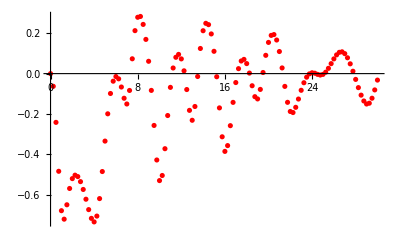

{{0.,{0.,0.}},{0.25,{-0.0629432,-5.86876×10^-14}},{0.5,{-0.241898,-9.80734×10^-14}},{0.75,{-0.484544,-2.266×10^-12}},{1.,{-0.680079,7.43981×10^-17}},{1.25,{-0.722091,2.97105×10^-16}},{1.5,{-0.650732,-4.0668×10^-17}},{1.75,{-0.569821,7.27002×10^-9}},{2.,{-0.520875,-4.96253×10^-11}},{2.25,{-0.503829,3.34356×10^-16}},{2.5,{-0.510865,2.3958×10^-17}},{2.75,{-0.535909,-1.70252×10^-17}},{3.,{-0.574735,-5.15664×10^-11}},{3.25,{-0.623166,-5.52601×10^-11}},{3.5,{-0.674739,-4.81775×10^-9}},{3.75,{-0.718119,-6.08327×10^-16}},{4.,{-0.735652,4.56242×10^-11}},{4.25,{-0.706838,1.58121×10^-10}},{4.5,{-0.62004,-2.96106×10^-10}},{4.75,{-0.485783,9.0896×10^-10}},{5.,{-0.334779,7.18462×10^-10}},{5.25,{-0.199404,6.10921×10^-10}},{5.5,{-0.0986211,1.1569×10^-10}},{5.75,{-0.0376296,-1.59247×10^-7}},{6.,{-0.0145918,-7.96459×10^-8}},{6.25,{-0.0258911,-8.5204×10^-9}},{6.5,{-0.0664803,5.12141×10^-9}},{6.75,{-0.122195,4.6751×10^-9}},{7.,{-0.15066,-6.65365×10^-9}},{7.25,{-0.0835191,-7.2797×10^-9}},{7.5,{0.0735168,-7.18798×10^-7}},{7.75,{0.213157,-4.76828×10^-9}},{8.,{0.279479,4.50999×10^-9}},{8.25,{0.283549,3.42012×10^-7}},{8.5,{0.244103,3.27938×10^-9}},{8.75,{0.169755,1.39416×10^-8}},{9.,{0.0611568,-6.15851×10^-9}},{9.25,{-0.0832651,1.10075×10^-9}},{9.5,{-0.257121,-2.6934×10^-8}},{9.75,{-0.428522,8.65665×10^-9}},{10.,{-0.530749,1.19917×10^-8}},{10.25,{-0.505446,-2.28124×10^-8}},{10.5,{-0.372535,4.51847×10^-9}},{10.75,{-0.207919,-3.64643×10^-8}},{11.,{-0.0682472,1.90379×10^-8}},{11.25,{0.0278852,7.19541×10^-9}},{11.5,{0.0809921,-2.95193×10^-8}},{11.75,{0.095319,-1.53925×10^-8}},{12.,{0.0730315,-7.58447×10^-8}},{12.25,{0.0139053,-1.33382×10^-7}},{12.5,{-0.0790213,-1.42553×10^-7}},{12.75,{-0.182334,-9.24631×10^-9}},{13.,{-0.231491,-7.38519×10^-9}},{13.25,{-0.163133,0.0000115338}},{13.5,{-0.0143494,4.30797×10^-8}},{13.75,{0.124699,1.10051×10^-7}},{14.,{0.212727,-7.47863×10^-8}},{14.25,{0.249544,3.95598×10^-7}},{14.5,{0.242966,6.18428×10^-8}},{14.75,{0.196861,-3.14431×10^-7}},{15.,{0.110689,2.90214×10^-8}},{15.25,{-0.0156304,-2.89911×10^-8}},{15.5,{-0.170046,1.42906×10^-8}},{15.75,{-0.313421,-3.65869×10^-7}},{16.,{-0.385842,-5.59971×10^-7}},{16.25,{-0.357081,-1.45542×10^-7}},{16.5,{-0.258245,9.48766×10^-8}},{16.75,{-0.142687,-3.08041×10^-7}},{17.,{-0.0443391,-4.95156×10^-7}},{17.25,{0.0246171,-1.85069×10^-7}},{17.5,{0.0625872,1.64487×10^-7}},{17.75,{0.0705554,8.38029×10^-7}},{18.,{0.0496671,1.07155×10^-6}},{18.25,{0.00270949,8.97424×10^-7}},{18.5,{-0.0602049,2.14131×10^-6}},{18.75,{-0.114421,-2.52533×10^-6}},{19.,{-0.125585,-5.62374×10^-6}},{19.25,{-0.078352,-1.81683×10^-6}},{19.5,{0.00548526,-6.65114×10^-7}},{19.75,{0.0907137,-1.26732×10^-6}},{20.,{0.154777,2.41729×10^-7}},{20.25,{0.189664,8.79493×10^-9}},{20.5,{0.193684,5.73899×10^-7}},{20.75,{0.16667,-2.29861×10^-7}},{21.,{0.10959,-5.66602×10^-7}},{21.25,{0.0281947,-6.13094×10^-7}},{21.5,{-0.063401,8.73054×10^-7}},{21.75,{-0.142439,3.13346×10^-6}},{22.,{-0.187853,7.0789×10^-7}},{22.25,{-0.19317,-2.78219×10^-6}},{22.5,{-0.167211,-9.43384×10^-7}},{22.75,{-0.126119,5.68325×10^-6}},{23.,{-0.082763,4.12024×10^-6}},{23.25,{-0.0452935,-0.0000457036}},{23.5,{-0.0177353,-9.07561×10^-6}},{23.75,{-0.00147101,-7.71138×10^-7}},{24.,{0.00420776,1.63925×10^-6}},{24.25,{0.00196401,4.05703×10^-7}},{24.5,{-0.00364135,6.98175×10^-6}},{24.75,{-0.00707466,8.22406×10^-6}},{25.,{-0.00381861,0.0000358981}},{25.25,{0.0071294,-0.0000100276}},{25.5,{0.0262218,-4.67112×10^-6}},{25.75,{0.0494832,7.16864×10^-6}},{26.,{0.0730329,4.0173×10^-6}},{26.25,{0.0929313,-0.0000171542}},{26.5,{0.105617,-9.92186×10^-6}},{26.75,{0.1082,8.40265×10^-6}},{27.,{0.0991263,0.000033157}},{27.25,{0.0786146,0.0000183009}},{27.5,{0.0485429,-0.0000172899}},{27.75,{0.0117386,-3.42999×10^-6}},{28.,{-0.0287152,6.70408×10^-6}},{28.25,{-0.0694833,-5.80315×10^-6}},{28.5,{-0.106817,7.26403×10^-6}},{28.75,{-0.135814,-5.49899×10^-6}},{29.,{-0.150781,-0.0000118545}},{29.25,{-0.146785,2.09208×10^-6}},{29.5,{-0.122151,-0.0000303582}},{29.75,{-0.080865,-0.0000280409}},{30.,{-0.0321124,0.0000106509}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$184694886 near {ϕ$184694886} = {5.00682}. NIntegrate obtained -9.2304×10^-6 and 9.90875×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$184754874 near {ϕ$184754874} = {4.97}. NIntegrate obtained -6.89656×10^-6 and 9.77293×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$184892491 near {ϕ$184892491} = {2.36837}. NIntegrate obtained -1.44194×10^-6 and 3.84176×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

{{0.,{0.,0.}},{0.25,{-0.0515924,0.0214413}},{0.5,{-0.131414,0.0670046}},{0.75,{-0.149492,0.0898515}},{1.,{-0.116828,0.0588104}},{1.25,{-0.0891145,-0.0229141}},{1.5,{-0.101749,-0.124469}},{1.75,{-0.152791,-0.211759}},{2.,{-0.222183,-0.267765}},{2.25,{-0.292667,-0.291885}},{2.5,{-0.355446,-0.290475}},{2.75,{-0.407526,-0.270748}},{3.,{-0.44844,-0.238971}},{3.25,{-0.478416,-0.20061}},{3.5,{-0.49771,-0.160852}},{3.75,{-0.506554,-0.124879}},{4.,{-0.505374,-0.0976363}},{4.25,{-0.495017,-0.083027}},{4.5,{-0.476767,-0.0826468}},{4.75,{-0.451981,-0.0944459}},{5.,{-0.421369,-0.111951}},{5.25,{-0.384238,-0.124818}},{5.5,{-0.338339,-0.121387}},{5.75,{-0.281098,-0.0933171}},{6.,{-0.212106,-0.0405508}},{6.25,{-0.1356,0.0268097}},{6.5,{-0.0604812,0.0923272}},{6.75,{0.00235232,0.140627}},{7.,{0.0433465,0.162909}},{7.25,{0.0560415,0.157705}},{7.5,{0.0372457,0.128601}},{7.75,{-0.0124552,0.0819614}},{8.,{-0.0858996,0.0263321}},{8.25,{-0.164578,-0.0271155}},{8.5,{-0.218877,-0.0661601}},{8.75,{-0.223742,-0.083789}},{9.,{-0.180303,-0.0836363}},{9.25,{-0.113704,-0.0757756}},{9.5,{-0.0505423,-0.0682882}},{9.75,{-0.00590628,-0.063925}},{10.,{0.0155667,-0.0621166}},{10.25,{0.0143087,-0.0610959}},{10.5,{-0.00725427,-0.0590591}},{10.75,{-0.0455129,-0.0546348}},{11.,{-0.0948313,-0.0471867}},{11.25,{-0.145974,-0.0370606}},{11.5,{-0.185494,-0.02575}},{11.75,{-0.19889,-0.0153135}},{12.,{-0.178323,-0.00686168}},{12.25,{-0.129129,0.000881901}},{12.5,{-0.0670206,0.0111806}},{12.75,{-0.0080833,0.0269125}},{13.,{0.0381025,0.0487867}},{13.25,{0.0691106,0.0742362}},{13.5,{0.0869073,0.0979027}},{13.75,{0.0947313,0.112765}},{14.,{0.0949302,0.112578}},{14.25,{0.0878098,0.0942583}},{14.5,{0.0718126,0.0593033}},{14.75,{0.044532,0.0133948}},{15.,{0.00445102,-0.0354795}},{15.25,{-0.0472487,-0.0785898}},{15.5,{-0.104675,-0.107871}},{15.75,{-0.156297,-0.117544}},{16.,{-0.186951,-0.106492}},{16.25,{-0.184724,-0.0800985}},{16.5,{-0.148699,-0.0486991}},{16.75,{-0.0902404,-0.0224326}},{17.,{-0.0260993,-0.00667257}},{17.25,{0.0292986,-0.0015605}},{17.5,{0.0669581,-0.00431462}},{17.75,{0.0822524,-0.0111562}},{18.,{0.0731405,-0.0183468}},{18.25,{0.0393916,-0.0221165}},{18.5,{-0.0158154,-0.0187692}},{18.75,{-0.0816022,-0.00518199}},{19.,{-0.136169,0.0190152}},{19.25,{-0.152603,0.0484089}},{19.5,{-0.120086,0.0734154}},{19.75,{-0.0553054,0.0870238}},{20.,{0.0134689,0.0888934}},{20.25,{0.0657103,0.0825998}},{20.5,{0.0942143,0.0712255}},{20.75,{0.0989301,0.056053}},{21.,{0.0836265,0.0368729}},{21.25,{0.0542928,0.0132971}},{21.5,{0.0179329,-0.0147586}},{21.75,{-0.0171658,-0.0450261}},{22.,{-0.0444554,-0.0730275}},{22.25,{-0.0613973,-0.0934304}},{22.5,{-0.0698721,-0.102092}},{22.75,{-0.0740461,-0.0972251}},{23.,{-0.0775232,-0.0796528}},{23.25,{-0.0814195,-0.0524096}},{23.5,{-0.0836503,-0.0200892}},{23.75,{-0.0798421,0.0113435}},{24.,{-0.0652712,0.0355473}},{24.25,{-0.0378314,0.047644}},{24.5,{-0.000122517,0.0463485}},{24.75,{0.0409336,0.0344997}},{25.,{0.0765198,0.0177692}},{25.25,{0.0987049,0.00236172}},{25.5,{0.101915,-0.00632556}},{25.75,{0.0841352,-0.00487006}},{26.,{0.0474201,0.00763268}},{26.25,{-0.000436706,0.0289575}},{26.5,{-0.0460705,0.0525684}},{26.75,{-0.074161,0.0700299}},{27.,{-0.0762155,0.0740863}},{27.25,{-0.055978,0.0640508}},{27.5,{-0.0251406,0.0435185}},{27.75,{0.00419944,0.0179363}},{28.,{0.0237838,-0.00835768}},{28.25,{0.029751,-0.0326965}},{28.5,{0.0220493,-0.053729}},{28.75,{0.00342814,-0.0701284}},{29.,{-0.020612,-0.0437529}},{29.25,{-0.0428723,-0.0836912}},{29.5,{-0.0567342,-0.078204}},{29.75,{-0.058542,-0.0459131}},{30.,{-0.0492587,-0.0258492}}}

```mathematica
Getv2kT[2.0, 0]
Getv2kT[2.0, π/4]
Getv2kT[2.0, π/2]
Getv2kT[2.0, (3π)/4]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$229384166 near {ϕ$229384166} = {2.89606}. NIntegrate obtained -0.0000123728 and 1.31425×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$229828081 near {ϕ$229828081} = {4.24596}. NIntegrate obtained 7.16671×10^-6 and 7.64321×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$229873664 near {ϕ$229873664} = {2.73652}. NIntegrate obtained 6.27908×10^-6 and 8.16719×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

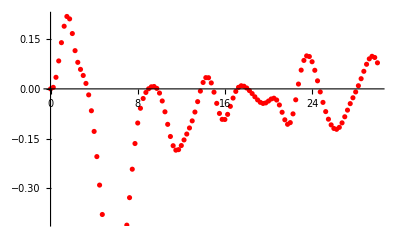

{{0.,{0.,0.}},{0.25,{0.00461509,-0.0264854}},{0.5,{0.0350056,-0.0647851}},{0.75,{0.0844777,-0.0907036}},{1.,{0.1397,-0.096889}},{1.25,{0.189321,-0.0695908}},{1.5,{0.21887,0.0131602}},{1.75,{0.211497,0.159851}},{2.,{0.167247,0.32002}},{2.25,{0.115566,0.409863}},{2.5,{0.0802174,0.412561}},{2.75,{0.058919,0.367571}},{3.,{0.0405151,0.308764}},{3.25,{0.0165097,0.251352}},{3.5,{-0.0181089,0.20025}},{3.75,{-0.0660849,0.156634}},{4.,{-0.128543,0.12081}},{4.25,{-0.204647,0.0932883}},{4.5,{-0.290733,0.0749292}},{4.75,{-0.379581,0.0665332}},{5.,{-0.461026,0.0680151}},{5.25,{-0.524902,0.0775875}},{5.5,{-0.565234,0.0917357}},{5.75,{-0.582355,0.106297}},{6.,{-0.580642,0.117855}},{6.25,{-0.563773,0.12439}},{6.5,{-0.531579,0.124908}},{6.75,{-0.481206,0.118836}},{7.,{-0.411797,0.105826}},{7.25,{-0.328695,0.0861648}},{7.5,{-0.24271,0.0612592}},{7.75,{-0.16514,0.0336599}},{8.,{-0.103148,0.00673015}},{8.25,{-0.0585468,-0.0158174}},{8.5,{-0.0291179,-0.0304426}},{8.75,{-0.0107834,-0.0345121}},{9.,{0.000283578,-0.0271097}},{9.25,{0.006253,-0.00945082}},{9.5,{0.00716908,0.0154829}},{9.75,{0.00150857,0.0439206}},{10.,{-0.0126823,0.0722504}},{10.25,{-0.0365379,0.0974686}},{10.5,{-0.0692378,0.117168}},{10.75,{-0.107166,0.12934}},{11.,{-0.143887,0.132361}},{11.25,{-0.171749,0.125546}},{11.5,{-0.185156,0.109575}},{11.75,{-0.183542,0.0866849}},{12.,{-0.17126,0.0599048}},{12.25,{-0.154252,0.0320414}},{12.5,{-0.136474,0.00522471}},{12.75,{-0.118087,-0.0188874}},{13.,{-0.0966655,-0.0389719}},{13.25,{-0.0699471,-0.054136}},{13.5,{-0.0385421,-0.0641796}},{13.75,{-0.00668554,-0.0696537}},{14.,{0.0193976,-0.0714256}},{14.25,{0.0340039,-0.0699519}},{14.5,{0.033702,-0.0648089}},{14.75,{0.018085,-0.0546017}},{15.,{-0.00993292,-0.0373557}},{15.25,{-0.0437629,-0.0115306}},{15.5,{-0.0742165,0.0224414}},{15.75,{-0.0920651,0.060923}},{16.,{-0.0924285,0.0974453}},{16.25,{-0.0770178,0.125058}},{16.5,{-0.0527599,0.139128}},{16.75,{-0.0277357,0.138354}},{17.,{-0.00763814,0.124218}},{17.25,{0.00464538,0.0996972}},{17.5,{0.00942424,0.068509}},{17.75,{0.00796534,0.034393}},{18.,{0.00263104,0.000979369}},{18.25,{-0.00511225,-0.028909}},{18.5,{-0.0141505,-0.0534737}},{18.75,{-0.0238927,-0.0718537}},{19.,{-0.0332631,-0.0837083}},{19.25,{-0.0406027,-0.088869}},{19.5,{-0.0439733,-0.0870922}},{19.75,{-0.0423288,-0.0785907}},{20.,{-0.0367282,-0.064152}},{20.25,{-0.0305661,-0.0452399}},{20.5,{-0.028185,-0.0237095}},{20.75,{-0.0336575,-0.00116279}},{21.,{-0.0485935,0.0212065}},{21.25,{-0.0706603,0.0423071}},{21.5,{-0.0933987,0.0611917}},{21.75,{-0.106967,0.0762388}},{22.,{-0.101946,0.0856775}},{22.25,{-0.0754745,0.0882204}},{22.5,{-0.0329747,0.0837528}},{22.75,{0.0145766,0.0733437}},{23.,{0.0567009,0.0585034}},{23.25,{0.0860258,0.0408957}},{23.5,{0.0996992,0.0217615}},{23.75,{0.0977322,0.00210261}},{24.,{0.0820383,-0.0168429}},{24.25,{0.0562067,-0.0338071}},{24.5,{0.0243313,-0.0474956}},{24.75,{-0.00914606,-0.056829}},{25.,{-0.0408089,-0.0612135}},{25.25,{-0.0686222,-0.0606138}},{25.5,{-0.0915331,-0.0550801}},{25.75,{-0.108746,-0.0450258}},{26.,{-0.119482,-0.0305835}},{26.25,{-0.12213,-0.012551}},{26.5,{-0.116215,0.00745149}},{26.75,{-0.102664,0.0270429}},{27.,{-0.0842469,0.0432324}},{27.25,{-0.0641948,0.053595}},{27.5,{-0.0445613,0.0568392}},{27.75,{-0.0268562,0.0399262}},{28.,{-0.00925297,0.0430233}},{28.25,{0.00951309,0.0463346}},{28.5,{0.0307735,0.0164601}},{28.75,{0.0531151,0.00500598}},{29.,{0.0743775,0.0661681}},{29.25,{0.0907635,0.0720098}},{29.5,{0.0984049,0.0773646}},{29.75,{0.0948959,-0.00766935}},{30.,{0.0787813,0.0852636}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$237661763 near {ϕ$237661763} = {0.773029}. NIntegrate obtained 4.99772×10^-7 and 5.02409×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$237731694 near {ϕ$237731694} = {3.95144}. NIntegrate obtained -1.08902×10^-6 and 5.74871×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$237807482 near {ϕ$237807482} = {4.56503}. NIntegrate obtained -4.17062×10^-6 and 9.55265×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

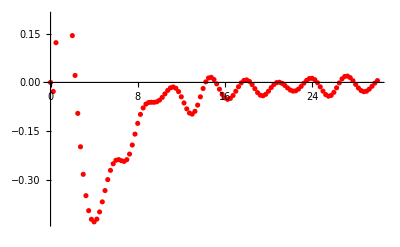

{{0.,{0.,0.}},{0.25,{-0.0278164,-0.479876}},{0.5,{0.121987,-0.455718}},{0.75,{0.252786,-0.374044}},{1.,{0.341113,-0.257006}},{1.25,{0.371562,-0.102549}},{1.5,{0.339729,0.0743184}},{1.75,{0.256776,0.247446}},{2.,{0.143685,0.39229}},{2.25,{0.0214193,0.494447}},{2.5,{-0.0950779,0.55028}},{2.75,{-0.197506,0.563325}},{3.,{-0.282144,0.540742}},{3.25,{-0.347631,0.491366}},{3.5,{-0.393584,0.424968}},{3.75,{-0.420144,0.351841}},{4.,{-0.428138,0.282041}},{4.25,{-0.419499,0.224013}},{4.5,{-0.397516,0.183017}},{4.75,{-0.366652,0.160049}},{5.,{-0.331965,0.15184}},{5.25,{-0.298356,0.151908}},{5.5,{-0.269967,0.152107}},{5.75,{-0.249738,0.144161}},{6.,{-0.23902,0.1211}},{6.25,{-0.237012,0.0789278}},{6.5,{-0.240193,0.0187991}},{6.75,{-0.242455,-0.0511867}},{7.,{-0.237058,-0.116878}},{7.25,{-0.219969,-0.163302}},{7.5,{-0.192156,-0.181308}},{7.75,{-0.158682,-0.170332}},{8.,{-0.125733,-0.135929}},{8.25,{-0.0981213,-0.0857316}},{8.5,{-0.0783485,-0.0270249}},{8.75,{-0.0667088,0.0338854}},{9.,{-0.0617483,0.0913807}},{9.25,{-0.0608807,0.140367}},{9.5,{-0.0610513,0.176606}},{9.75,{-0.0594904,0.19743}},{10.,{-0.0545062,0.202405}},{10.25,{-0.0459328,0.193488}},{10.5,{-0.0351381,0.174381}},{10.75,{-0.0245243,0.149295}},{11.,{-0.0167662,0.121688}},{11.25,{-0.0141078,0.0934682}},{11.5,{-0.0178703,0.0648553}},{11.75,{-0.0282476,0.0348314}},{12.,{-0.044098,0.00202968}},{12.25,{-0.0629773,-0.0342292}},{12.5,{-0.0811301,-0.0728637}},{12.75,{-0.0939916,-0.110301}},{13.,{-0.097293,-0.140748}},{13.25,{-0.0887907,-0.157878}},{13.5,{-0.0696346,-0.157579}},{13.75,{-0.0442571,-0.139878}},{14.,{-0.0186565,-0.108758}},{14.25,{0.00176741,-0.0701533}},{14.5,{0.0135681,-0.0297339}},{14.75,{0.0155964,0.00828276}},{15.,{0.00874213,0.041291}},{15.25,{-0.00457505,0.0679434}},{15.5,{-0.0208865,0.0876838}},{15.75,{-0.0363503,0.100439}},{16.,{-0.0474873,0.106606}},{16.25,{-0.0519792,0.106866}},{16.5,{-0.0491415,0.1023}},{16.75,{-0.0400435,0.0942324}},{17.,{-0.0270788,0.083911}},{17.25,{-0.0131774,0.0723532}},{17.5,{-0.00134777,0.0600121}},{17.75,{0.00608079,0.0467132}},{18.,{0.00771556,0.031679}},{18.25,{0.00308002,0.0137401}},{18.5,{-0.00666051,-0.00808156}},{18.75,{-0.0191093,-0.03391}},{19.,{-0.0311685,-0.0622591}},{19.25,{-0.039244,-0.089781}},{19.5,{-0.0410776,-0.11185}},{19.75,{-0.0363743,-0.124061}},{20.,{-0.0269494,-0.123908}},{20.25,{-0.0159133,-0.111524}},{20.5,{-0.00636873,-0.0892356}},{20.75,{-0.00057227,-0.06042}},{21.,{0.000512394,-0.028597}},{21.25,{-0.0028559,0.00328418}},{21.5,{-0.00926063,0.0329444}},{21.75,{-0.016849,0.0587226}},{22.,{-0.0233882,0.079402}},{22.25,{-0.026691,0.0942866}},{22.5,{-0.0257672,0.102901}},{22.75,{-0.0205097,0.105286}},{23.,{-0.0120837,0.101772}},{23.25,{-0.00239678,0.092915}},{23.5,{0.00625427,0.0794442}},{23.75,{0.0118015,0.0621556}},{24.,{0.0127097,0.0417793}},{24.25,{0.00830982,0.0190061}},{24.5,{-0.000978796,-0.00545211}},{24.75,{-0.0134849,-0.0307388}},{25.,{-0.0266644,-0.0554842}},{25.25,{-0.0372596,-0.0779963}},{25.5,{-0.0422114,-0.0959466}},{25.75,{-0.0398347,-0.107034}},{26.,{-0.0304681,-0.109534}},{26.25,{-0.0165382,-0.10274}},{26.5,{-0.00152844,-0.0875356}},{26.75,{0.010946,-0.0657045}},{27.,{0.0182887,-0.0398638}},{27.25,{0.0194543,-0.0127666}},{27.5,{0.0146199,0.0132259}},{27.75,{0.00533416,0.0360824}},{28.,{-0.00611316,0.0544255}},{28.25,{-0.0170664,0.0675433}},{28.5,{-0.025061,0.0754138}},{28.75,{-0.0285018,0.0784824}},{29.,{-0.0268295,0.0775518}},{29.25,{-0.0206645,0.0589589}},{29.5,{-0.011873,0.0669409}},{29.75,{-0.00235715,0.0582893}},{30.,{0.00555337,-0.0154845}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$245836752 near {ϕ$245836752} = {5.70631}. NIntegrate obtained 9.23032×10^-6 and 1.53374×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$245883419 near {ϕ$245883419} = {1.32526}. NIntegrate obtained 6.89659×10^-6 and 9.16394×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$245926764 near {ϕ$245926764} = {1.21482}. NIntegrate obtained 4.14753×10^-6 and 5.07297×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

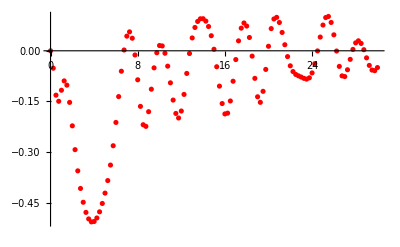

{{0.,{0.,0.}},{0.25,{-0.0515923,-0.0214412}},{0.5,{-0.131414,-0.0670047}},{0.75,{-0.149492,-0.0898517}},{1.,{-0.116828,-0.0588104}},{1.25,{-0.0891144,0.0229142}},{1.5,{-0.101749,0.124469}},{1.75,{-0.152791,0.211759}},{2.,{-0.222183,0.267765}},{2.25,{-0.292667,0.291885}},{2.5,{-0.355446,0.290473}},{2.75,{-0.407526,0.270748}},{3.,{-0.44844,0.238971}},{3.25,{-0.478416,0.20061}},{3.5,{-0.497711,0.160853}},{3.75,{-0.506554,0.124879}},{4.,{-0.505374,0.0976372}},{4.25,{-0.495017,0.0830276}},{4.5,{-0.476767,0.0826469}},{4.75,{-0.451982,0.0944463}},{5.,{-0.421368,0.111952}},{5.25,{-0.384234,0.124816}},{5.5,{-0.338338,0.121388}},{5.75,{-0.281097,0.0933176}},{6.,{-0.212117,0.0405508}},{6.25,{-0.135599,-0.0268098}},{6.5,{-0.0604796,-0.0923302}},{6.75,{0.00235276,-0.140628}},{7.,{0.0433486,-0.16291}},{7.25,{0.0560442,-0.157707}},{7.5,{0.0372475,-0.128601}},{7.75,{-0.0124533,-0.0819612}},{8.,{-0.0858963,-0.0263333}},{8.25,{-0.164575,0.0271139}},{8.5,{-0.218873,0.0661566}},{8.75,{-0.223739,0.0837854}},{9.,{-0.180299,0.0836336}},{9.25,{-0.113684,0.0758138}},{9.5,{-0.0505433,0.068289}},{9.75,{-0.00588692,0.063923}},{10.,{0.0155703,0.0621161}},{10.25,{0.0143114,0.0610995}},{10.5,{-0.00724748,0.0590617}},{10.75,{-0.045509,0.0546411}},{11.,{-0.0948242,0.047189}},{11.25,{-0.145965,0.0370627}},{11.5,{-0.185493,0.025755}},{11.75,{-0.198891,0.0153185}},{12.,{-0.178319,0.00686145}},{12.25,{-0.129131,-0.000889355}},{12.5,{-0.0670198,-0.0111329}},{12.75,{-0.00809325,-0.0269091}},{13.,{0.0380642,-0.048788}},{13.25,{0.0690752,-0.0742421}},{13.5,{0.0868816,-0.0978983}},{13.75,{0.0947209,-0.112767}},{14.,{0.0949368,-0.112595}},{14.25,{0.0878313,-0.0942686}},{14.5,{0.0718431,-0.0593336}},{14.75,{0.044578,-0.013412}},{15.,{0.00450155,0.0354584}},{15.25,{-0.0472028,0.0785587}},{15.5,{-0.104616,0.107863}},{15.75,{-0.156205,0.117553}},{16.,{-0.186878,0.106484}},{16.25,{-0.184633,0.080074}},{16.5,{-0.148607,0.0487012}},{16.75,{-0.0901334,0.0224285}},{17.,{-0.0260129,0.00666446}},{17.25,{0.0293765,0.0015935}},{17.5,{0.0670163,0.00436189}},{17.75,{0.0822851,0.0112134}},{18.,{0.0731831,0.0183974}},{18.25,{0.039402,0.0221796}},{18.5,{-0.0157957,0.018852}},{18.75,{-0.0816179,0.00529172}},{19.,{-0.136135,-0.0188549}},{19.25,{-0.152569,-0.0482561}},{19.5,{-0.120014,-0.0731817}},{19.75,{-0.0551722,-0.086845}},{20.,{0.0133546,-0.0888583}},{20.25,{0.0656734,-0.0826369}},{20.5,{0.0941701,-0.07131}},{20.75,{0.0989892,-0.0561752}},{21.,{0.0837585,-0.0370518}},{21.25,{0.0542757,-0.0133333}},{21.5,{0.017903,0.014705}},{21.75,{-0.0171977,0.0449805}},{22.,{-0.0445038,0.0729828}},{22.25,{-0.0615007,0.0934436}},{22.5,{-0.0699871,0.102071}},{22.75,{-0.0741612,0.0972104}},{23.,{-0.0776785,0.0796922}},{23.25,{-0.0815733,0.0524238}},{23.5,{-0.0838884,0.0201343}},{23.75,{-0.0800559,-0.011217}},{24.,{-0.0655298,-0.0353685}},{24.25,{-0.0381211,-0.0474076}},{24.5,{-0.000408602,-0.0461031}},{24.75,{0.0406273,-0.0341802}},{25.,{0.0761731,-0.0174488}},{25.25,{0.0983632,-0.00204961}},{25.5,{0.10163,0.00655646}},{25.75,{0.0838833,0.00514069}},{26.,{0.0472255,-0.00742262}},{26.25,{-0.000686083,-0.0287562}},{26.5,{-0.0462127,-0.0492759}},{26.75,{-0.0742834,-0.0699744}},{27.,{-0.0763081,-0.106151}},{27.25,{-0.0561838,-0.0640316}},{27.5,{-0.0253499,-0.0434984}},{27.75,{0.00402218,-0.017897}},{28.,{0.0234759,0.00831559}},{28.25,{0.0295237,-0.0238398}},{28.5,{0.0217742,0.0537875}},{28.75,{0.00319505,0.0702275}},{29.,{-0.0209085,0.0806156}},{29.25,{-0.0432388,0.0837475}},{29.5,{-0.0570047,0.0783041}},{29.75,{-0.0588691,0.0460927}},{30.,{-0.0496426,0.0259898}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$253642771 near {ϕ$253642771} = {3.87781}. NIntegrate obtained 3.79405×10^-9 and 4.98605×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$253747787 near {ϕ$253747787} = {5.62041}. NIntegrate obtained 1.6091×10^-10 and 9.45454×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$253796920 near {ϕ$253796920} = {3.53419}. NIntegrate obtained 8.92926×10^-10 and 4.13066×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

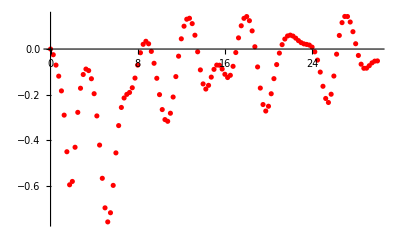

{{0.,{0.,0.}},{0.25,{-0.0249709,1.42642×10^-8}},{0.5,{-0.0705814,9.67813×10^-8}},{0.75,{-0.119123,1.02086×10^-8}},{1.,{-0.183868,1.22249×10^-7}},{1.25,{-0.290353,3.40902×10^-8}},{1.5,{-0.45122,-2.50129×10^-10}},{1.75,{-0.596433,5.76472×10^-8}},{2.,{-0.581761,-2.39082×10^-7}},{2.25,{-0.431508,1.787×10^-7}},{2.5,{-0.278172,-1.52867×10^-7}},{2.75,{-0.172238,2.29104×10^-7}},{3.,{-0.111923,2.69814×10^-7}},{3.25,{-0.0879799,1.85728×10^-9}},{3.5,{-0.0947121,9.46907×10^-8}},{3.75,{-0.130438,2.25935×10^-7}},{4.,{-0.196205,-1.01023×10^-7}},{4.25,{-0.293845,1.45511×10^-7}},{4.5,{-0.421959,1.76475×10^-7}},{4.75,{-0.567911,1.57192×10^-7}},{5.,{-0.697734,9.48845×10^-8}},{5.25,{-0.759469,-5.66364×10^-8}},{5.5,{-0.719278,-4.32664×10^-6}},{5.75,{-0.599054,-3.49807×10^-8}},{6.,{-0.456278,5.6202×10^-7}},{6.25,{-0.336371,-3.61895×10^-7}},{6.5,{-0.256657,-4.79566×10^-7}},{6.75,{-0.215087,-4.31242×10^-7}},{7.,{-0.199276,-6.88425×10^-7}},{7.25,{-0.190738,-9.21564×10^-8}},{7.5,{-0.170042,4.33433×10^-7}},{7.75,{-0.127588,-7.00621×10^-7}},{8.,{-0.070575,-1.08563×10^-6}},{8.25,{-0.0162742,-9.31313×10^-7}},{8.5,{0.0207631,-1.1635×10^-6}},{8.75,{0.0340988,-6.97801×10^-7}},{9.,{0.0230166,-7.57757×10^-7}},{9.25,{-0.0103688,-1.85325×10^-6}},{9.5,{-0.0625545,-2.46585×10^-6}},{9.75,{-0.128481,-1.54376×10^-6}},{10.,{-0.200273,-6.03681×10^-7}},{10.25,{-0.265957,-2.76498×10^-6}},{10.5,{-0.309947,1.53086×10^-6}},{10.75,{-0.317423,2.13166×10^-6}},{11.,{-0.282003,0.000073162}},{11.25,{-0.210819,2.31035×10^-6}},{11.5,{-0.1211,4.77162×10^-6}},{11.75,{-0.0313451,6.19372×10^-7}},{12.,{0.0449622,0.0000123562}},{12.25,{0.100308,2.48744×10^-6}},{12.5,{0.131032,3.12298×10^-6}},{12.75,{0.135236,-2.26902×10^-7}},{13.,{0.111672,-2.51717×10^-6}},{13.25,{0.0607322,-4.97293×10^-6}},{13.5,{-0.0121331,-6.46991×10^-6}},{13.75,{-0.0916819,-0.0000154386}},{14.,{-0.153191,-0.000016911}},{14.25,{-0.175784,-0.0000142309}},{14.5,{-0.159475,-0.0000210865}},{14.75,{-0.123375,-0.0000229273}},{15.,{-0.0892316,-0.0000189566}},{15.25,{-0.0704919,-0.0000120886}},{15.5,{-0.0711113,-0.000039916}},{15.75,{-0.0878358,-0.0000348589}},{16.,{-0.110896,-0.0000263699}},{16.25,{-0.125137,-0.000027656}},{16.5,{-0.11537,0.0000297951}},{16.75,{-0.0759178,-0.0000182824}},{17.,{-0.0153812,-7.99205×10^-6}},{17.25,{0.0491259,0.0000177394}},{17.5,{0.102222,8.59608×10^-6}},{17.75,{0.134806,0.0000311056}},{18.,{0.142729,0.0000111259}},{18.25,{0.124496,0.0000559335}},{18.5,{0.0797888,0.0000404531}},{18.75,{0.0100806,0.0000330005}},{19.,{-0.0786326,0.0000540935}},{19.25,{-0.171434,0.0000599635}},{19.5,{-0.243846,0.0000595764}},{19.75,{-0.272332,0.0000630208}},{20.,{-0.251332,0.0000603791}},{20.25,{-0.196467,0.0000597543}},{20.5,{-0.130112,0.0000645428}},{20.75,{-0.0683063,0.0000944397}},{21.,{-0.0178941,0.0000971386}},{21.25,{0.0193044,0.000120233}},{21.5,{0.0439402,0.00013028}},{21.75,{0.0574601,0.000179164}},{22.,{0.0610996,0.000133419}},{22.25,{0.0569378,0.000156586}},{22.5,{0.0477625,0.000169158}},{22.75,{0.0370041,0.000159645}},{23.,{0.028066,0.000152053}},{23.25,{0.0227389,0.000166054}},{23.5,{0.0202806,0.00019154}},{23.75,{0.0174064,0.0000536853}},{24.,{0.00842814,0.0000842607}},{24.25,{-0.0122016,0.000129298}},{24.5,{-0.0485866,0.0000531477}},{24.75,{-0.10125,0.0000167802}},{25.,{-0.16365,-9.05339×10^-6}},{25.25,{-0.217167,0.0000134576}},{25.5,{-0.234866,1.71448×10^-7}},{25.75,{-0.19851,0.0000611231}},{26.,{-0.118656,8.40336×10^-6}},{26.25,{-0.0225798,0.0000122354}},{26.5,{0.0596688,-1.17187×10^-6}},{26.75,{0.116022,1.18783×10^-6}},{27.,{0.143149,-3.31112×10^-6}},{27.25,{0.142898,-7.8435×10^-6}},{27.5,{0.118745,-0.0000194648}},{27.75,{0.0762222,-0.0000117101}},{28.,{0.0232977,-0.0000373931}},{28.25,{-0.0282077,-0.0000137233}},{28.5,{-0.0666131,-8.12204×10^-6}},{28.75,{-0.0844727,-0.0000283716}},{29.,{-0.0840014,-0.000027468}},{29.25,{-0.0731015,0.0000161276}},{29.5,{-0.0607541,0.0000101257}},{29.75,{-0.053131,-0.000417897}},{30.,{-0.0522055,-0.000399889}}}

```mathematica
Getv2kT[2.0, 0, π/4]
Getv2kT[2.0, π/4, π/4]
Getv2kT[2.0, π/2, π/4]
Getv2kT[2.0, (3π)/4, π/4]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$261901090 near {ϕ$261901090} = {3.3992}. NIntegrate obtained -0.0000123728 and 1.31425×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$262345005 near {ϕ$262345005} = {2.0493}. NIntegrate obtained -7.16671×10^-6 and 7.64321×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$262390588 near {ϕ$262390588} = {3.55874}. NIntegrate obtained -6.27908×10^-6 and 8.16719×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

{{0.,{0.,0.}},{0.25,{0.00461509,0.0264854}},{0.5,{0.0350056,0.0647851}},{0.75,{0.0844777,0.0907036}},{1.,{0.1397,0.096889}},{1.25,{0.189321,0.0695908}},{1.5,{0.21887,-0.0131602}},{1.75,{0.211497,-0.159851}},{2.,{0.167247,-0.32002}},{2.25,{0.115566,-0.409863}},{2.5,{0.0802174,-0.412561}},{2.75,{0.058919,-0.367571}},{3.,{0.0405151,-0.308764}},{3.25,{0.0165097,-0.251352}},{3.5,{-0.0181089,-0.20025}},{3.75,{-0.0660849,-0.156634}},{4.,{-0.128543,-0.12081}},{4.25,{-0.204647,-0.0932883}},{4.5,{-0.290733,-0.0749292}},{4.75,{-0.379581,-0.0665332}},{5.,{-0.461026,-0.0680151}},{5.25,{-0.524902,-0.0775875}},{5.5,{-0.565234,-0.0917357}},{5.75,{-0.582355,-0.106297}},{6.,{-0.580642,-0.117855}},{6.25,{-0.563773,-0.12439}},{6.5,{-0.531579,-0.124908}},{6.75,{-0.481206,-0.118836}},{7.,{-0.411797,-0.105826}},{7.25,{-0.328696,-0.0861648}},{7.5,{-0.24271,-0.0612592}},{7.75,{-0.16514,-0.0336599}},{8.,{-0.103148,-0.00673015}},{8.25,{-0.0585468,0.0158174}},{8.5,{-0.0291179,0.0304426}},{8.75,{-0.0107834,0.0345121}},{9.,{0.000283578,0.0271097}},{9.25,{0.00625301,0.00945083}},{9.5,{0.00716908,-0.0154829}},{9.75,{0.00150857,-0.0439206}},{10.,{-0.0126823,-0.0722504}},{10.25,{-0.0365379,-0.0974686}},{10.5,{-0.0692378,-0.117168}},{10.75,{-0.107166,-0.12934}},{11.,{-0.143887,-0.132361}},{11.25,{-0.171749,-0.125546}},{11.5,{-0.185156,-0.109575}},{11.75,{-0.183542,-0.0866849}},{12.,{-0.17126,-0.0599048}},{12.25,{-0.154252,-0.0320414}},{12.5,{-0.136474,-0.00522471}},{12.75,{-0.118087,0.0188874}},{13.,{-0.0966655,0.0389719}},{13.25,{-0.0699471,0.054136}},{13.5,{-0.0385421,0.0641796}},{13.75,{-0.00668554,0.0696537}},{14.,{0.0193976,0.0714256}},{14.25,{0.0340039,0.0699519}},{14.5,{0.033702,0.0648089}},{14.75,{0.018085,0.0546017}},{15.,{-0.00993292,0.0373557}},{15.25,{-0.0437629,0.0115306}},{15.5,{-0.0742165,-0.0224414}},{15.75,{-0.0920651,-0.060923}},{16.,{-0.0924285,-0.0974453}},{16.25,{-0.0770178,-0.125058}},{16.5,{-0.0527599,-0.139128}},{16.75,{-0.0277357,-0.138354}},{17.,{-0.00763814,-0.124218}},{17.25,{0.00464538,-0.0996972}},{17.5,{0.00942424,-0.068509}},{17.75,{0.00796534,-0.034393}},{18.,{0.00263104,-0.000979369}},{18.25,{-0.00511225,0.028909}},{18.5,{-0.0141505,0.0534737}},{18.75,{-0.0238927,0.0718537}},{19.,{-0.0332631,0.0837083}},{19.25,{-0.0406027,0.088869}},{19.5,{-0.0439733,0.0870922}},{19.75,{-0.0423288,0.0785907}},{20.,{-0.0367282,0.064152}},{20.25,{-0.0305661,0.0452399}},{20.5,{-0.028185,0.0237095}},{20.75,{-0.0336575,0.00116279}},{21.,{-0.0485935,-0.0212065}},{21.25,{-0.0706603,-0.0423071}},{21.5,{-0.0933987,-0.0611917}},{21.75,{-0.106967,-0.0762388}},{22.,{-0.101946,-0.0856775}},{22.25,{-0.0754745,-0.0882204}},{22.5,{-0.0329747,-0.0837528}},{22.75,{0.0145766,-0.0733437}},{23.,{0.0567009,-0.0585034}},{23.25,{0.0860258,-0.0408957}},{23.5,{0.0996992,-0.0217615}},{23.75,{0.0977322,-0.00210261}},{24.,{0.0820383,0.0168429}},{24.25,{0.0562067,0.0338071}},{24.5,{0.0243313,0.0474956}},{24.75,{-0.00914606,0.056829}},{25.,{-0.0408089,0.0612135}},{25.25,{-0.0686222,0.0606138}},{25.5,{-0.0915331,0.0550801}},{25.75,{-0.108746,0.0450258}},{26.,{-0.119482,0.0305835}},{26.25,{-0.12213,0.012551}},{26.5,{-0.116215,-0.00745149}},{26.75,{-0.102664,-0.0270429}},{27.,{-0.0842469,-0.0432324}},{27.25,{-0.0641948,-0.053595}},{27.5,{-0.0445613,-0.0568392}},{27.75,{-0.0268562,-0.0399262}},{28.,{-0.00925297,-0.0430233}},{28.25,{0.00951309,-0.0463346}},{28.5,{0.0307735,-0.0164601}},{28.75,{0.0531151,-0.00500598}},{29.,{0.0743775,-0.0661681}},{29.25,{0.0907635,-0.0720098}},{29.5,{0.0984049,-0.0773646}},{29.75,{0.0948959,0.00766935}},{30.,{0.0787813,-0.0852636}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$269630204 near {ϕ$269630204} = {2.41746}. NIntegrate obtained -3.79405×10^-9 and 4.98605×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$269735220 near {ϕ$269735220} = {0.674854}. NIntegrate obtained -1.6091×10^-10 and 9.45454×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$269784353 near {ϕ$269784353} = {5.89039}. NIntegrate obtained -8.919×10^-10 and 3.92635×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

{{0.,{0.,0.}},{0.25,{-0.0249709,-1.42642×10^-8}},{0.5,{-0.0705814,-9.67813×10^-8}},{0.75,{-0.119123,-1.02086×10^-8}},{1.,{-0.183868,-1.22108×10^-7}},{1.25,{-0.290353,-3.40962×10^-8}},{1.5,{-0.45122,-3.66617×10^-10}},{1.75,{-0.596433,-5.76472×10^-8}},{2.,{-0.581761,2.39082×10^-7}},{2.25,{-0.431508,-1.787×10^-7}},{2.5,{-0.278172,1.50822×10^-7}},{2.75,{-0.172238,-2.29104×10^-7}},{3.,{-0.111923,-2.69814×10^-7}},{3.25,{-0.0879799,-1.85728×10^-9}},{3.5,{-0.0947121,-9.46907×10^-8}},{3.75,{-0.130438,-2.25935×10^-7}},{4.,{-0.196205,1.01023×10^-7}},{4.25,{-0.293845,-1.45511×10^-7}},{4.5,{-0.421959,-1.76475×10^-7}},{4.75,{-0.567911,-1.57192×10^-7}},{5.,{-0.697734,-9.48681×10^-8}},{5.25,{-0.759469,5.66364×10^-8}},{5.5,{-0.719278,4.32664×10^-6}},{5.75,{-0.599054,3.49807×10^-8}},{6.,{-0.456278,-5.6202×10^-7}},{6.25,{-0.336371,3.61895×10^-7}},{6.5,{-0.256657,4.81565×10^-7}},{6.75,{-0.215087,4.31242×10^-7}},{7.,{-0.199276,6.88425×10^-7}},{7.25,{-0.190738,9.95285×10^-8}},{7.5,{-0.170042,-4.31418×10^-7}},{7.75,{-0.127588,7.00621×10^-7}},{8.,{-0.070575,1.08563×10^-6}},{8.25,{-0.0162742,9.31313×10^-7}},{8.5,{0.0207631,1.1635×10^-6}},{8.75,{0.0340988,6.97801×10^-7}},{9.,{0.0230166,7.57757×10^-7}},{9.25,{-0.0103688,1.85325×10^-6}},{9.5,{-0.0625545,2.46585×10^-6}},{9.75,{-0.128481,1.54376×10^-6}},{10.,{-0.200273,6.03681×10^-7}},{10.25,{-0.265957,2.79369×10^-6}},{10.5,{-0.309947,-1.53086×10^-6}},{10.75,{-0.317423,-2.13166×10^-6}},{11.,{-0.282003,-0.0000731197}},{11.25,{-0.210819,-2.32725×10^-6}},{11.5,{-0.1211,-4.77162×10^-6}},{11.75,{-0.0313451,-5.36012×10^-7}},{12.,{0.0449622,-0.0000124049}},{12.25,{0.100308,-2.48744×10^-6}},{12.5,{0.131032,-3.12298×10^-6}},{12.75,{0.135236,2.26902×10^-7}},{13.,{0.111672,2.51717×10^-6}},{13.25,{0.0607322,4.97293×10^-6}},{13.5,{-0.0121331,6.24205×10^-6}},{13.75,{-0.0916819,0.0000154386}},{14.,{-0.153191,0.000016911}},{14.25,{-0.175784,0.0000142309}},{14.5,{-0.159475,0.0000210865}},{14.75,{-0.123375,0.0000229273}},{15.,{-0.0892316,0.0000190215}},{15.25,{-0.0704919,0.0000121201}},{15.5,{-0.0711113,0.000039916}},{15.75,{-0.0878358,0.0000348589}},{16.,{-0.110896,0.0000263699}},{16.25,{-0.125137,0.0000273284}},{16.5,{-0.11537,-0.0000295292}},{16.75,{-0.0759178,0.0000182824}},{17.,{-0.0153812,7.99205×10^-6}},{17.25,{0.0491259,-0.0000177394}},{17.5,{0.102222,-9.20708×10^-6}},{17.75,{0.134806,-0.0000311056}},{18.,{0.142729,-0.0000111259}},{18.25,{0.124496,-0.0000559335}},{18.5,{0.0797888,-0.0000404531}},{18.75,{0.0100806,-0.0000330005}},{19.,{-0.0786326,-0.0000540935}},{19.25,{-0.171434,-0.0000599635}},{19.5,{-0.243846,-0.0000595764}},{19.75,{-0.272332,-0.0000630208}},{20.,{-0.251332,-0.0000603791}},{20.25,{-0.196467,-0.0000597543}},{20.5,{-0.130112,-0.0000645428}},{20.75,{-0.0683063,-0.0000944397}},{21.,{-0.0178941,-0.0000971386}},{21.25,{0.0193044,-0.000120233}},{21.5,{0.0439402,-0.00013028}},{21.75,{0.0574601,-0.000179164}},{22.,{0.0610996,-0.000133419}},{22.25,{0.0569378,-0.000156586}},{22.5,{0.0477625,-0.000169158}},{22.75,{0.0370041,-0.000159645}},{23.,{0.028066,-0.000152053}},{23.25,{0.0227389,-0.000166054}},{23.5,{0.0202806,-0.00019154}},{23.75,{0.0174064,-0.0000536853}},{24.,{0.00842814,-0.0000842607}},{24.25,{-0.0122016,-0.000129298}},{24.5,{-0.0485866,-0.0000531477}},{24.75,{-0.10125,-0.0000167802}},{25.,{-0.16365,9.05339×10^-6}},{25.25,{-0.217167,-0.0000134576}},{25.5,{-0.234866,-1.71448×10^-7}},{25.75,{-0.19851,-0.0000611231}},{26.,{-0.118656,-8.40336×10^-6}},{26.25,{-0.0225798,-0.0000122354}},{26.5,{0.0596688,1.17187×10^-6}},{26.75,{0.116022,-1.18783×10^-6}},{27.,{0.143149,3.31112×10^-6}},{27.25,{0.142898,7.8435×10^-6}},{27.5,{0.118745,0.0000194648}},{27.75,{0.0762222,0.0000117101}},{28.,{0.0232977,0.0000373931}},{28.25,{-0.0282077,0.0000137233}},{28.5,{-0.0666131,8.12204×10^-6}},{28.75,{-0.0844727,0.0000283716}},{29.,{-0.0840014,0.000027468}},{29.25,{-0.0731015,-0.0000161276}},{29.5,{-0.0607541,-0.0000101257}},{29.75,{-0.053131,0.000417897}},{30.,{-0.0522055,0.000399889}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$278078048 near {ϕ$278078048} = {3.73054}. NIntegrate obtained -9.23032×10^-6 and 1.53374×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$278124715 near {ϕ$278124715} = {4.97}. NIntegrate obtained -6.89659×10^-6 and 9.16394×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$278168060 near {ϕ$278168060} = {5.08045}. NIntegrate obtained -4.14753×10^-6 and 5.07297×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

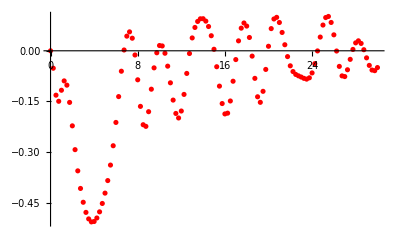

{{0.,{0.,0.}},{0.25,{-0.0515923,0.0214412}},{0.5,{-0.131414,0.0670047}},{0.75,{-0.149492,0.0898517}},{1.,{-0.116828,0.0588104}},{1.25,{-0.0891144,-0.0229142}},{1.5,{-0.101749,-0.124469}},{1.75,{-0.152791,-0.211759}},{2.,{-0.222183,-0.267765}},{2.25,{-0.292667,-0.291885}},{2.5,{-0.355446,-0.290473}},{2.75,{-0.407526,-0.270748}},{3.,{-0.44844,-0.238971}},{3.25,{-0.478416,-0.20061}},{3.5,{-0.497711,-0.160853}},{3.75,{-0.506553,-0.124879}},{4.,{-0.505374,-0.0976372}},{4.25,{-0.495017,-0.0830276}},{4.5,{-0.476767,-0.0826469}},{4.75,{-0.451982,-0.0944463}},{5.,{-0.421368,-0.111952}},{5.25,{-0.384234,-0.124816}},{5.5,{-0.338338,-0.121388}},{5.75,{-0.281097,-0.0933176}},{6.,{-0.212117,-0.0405508}},{6.25,{-0.135599,0.0268098}},{6.5,{-0.0604796,0.0923302}},{6.75,{0.00235276,0.140628}},{7.,{0.0433486,0.16291}},{7.25,{0.0560442,0.157707}},{7.5,{0.0372475,0.128601}},{7.75,{-0.0124533,0.0819612}},{8.,{-0.0858963,0.0263333}},{8.25,{-0.164575,-0.0271139}},{8.5,{-0.218873,-0.0661566}},{8.75,{-0.223739,-0.0837854}},{9.,{-0.180299,-0.0836336}},{9.25,{-0.113684,-0.0758138}},{9.5,{-0.0505433,-0.068289}},{9.75,{-0.00588692,-0.063923}},{10.,{0.0155703,-0.0621161}},{10.25,{0.0143114,-0.0610995}},{10.5,{-0.00724748,-0.0590617}},{10.75,{-0.045509,-0.0546411}},{11.,{-0.0948242,-0.047189}},{11.25,{-0.145965,-0.0370627}},{11.5,{-0.185493,-0.025755}},{11.75,{-0.198891,-0.0153185}},{12.,{-0.178319,-0.00686145}},{12.25,{-0.129131,0.000889355}},{12.5,{-0.0670198,0.0111329}},{12.75,{-0.00809325,0.0269091}},{13.,{0.0380642,0.048788}},{13.25,{0.0690752,0.0742421}},{13.5,{0.0868816,0.0978983}},{13.75,{0.0947209,0.112767}},{14.,{0.0949368,0.112595}},{14.25,{0.0878313,0.0942686}},{14.5,{0.0718431,0.0593336}},{14.75,{0.044578,0.013412}},{15.,{0.00450155,-0.0354584}},{15.25,{-0.0472028,-0.0785587}},{15.5,{-0.104616,-0.107863}},{15.75,{-0.156205,-0.117553}},{16.,{-0.186878,-0.106484}},{16.25,{-0.184633,-0.080074}},{16.5,{-0.148607,-0.0487012}},{16.75,{-0.0901334,-0.0224285}},{17.,{-0.0260129,-0.00666446}},{17.25,{0.0293765,-0.0015935}},{17.5,{0.0670163,-0.00436189}},{17.75,{0.0822851,-0.0112134}},{18.,{0.0731831,-0.0183974}},{18.25,{0.039402,-0.0221796}},{18.5,{-0.0157957,-0.018852}},{18.75,{-0.0816179,-0.00529172}},{19.,{-0.136135,0.0188549}},{19.25,{-0.152569,0.0482561}},{19.5,{-0.120014,0.0731817}},{19.75,{-0.0551722,0.086845}},{20.,{0.0133546,0.0888583}},{20.25,{0.0656734,0.0826369}},{20.5,{0.0941701,0.07131}},{20.75,{0.0989892,0.0561752}},{21.,{0.0837585,0.0370518}},{21.25,{0.0542757,0.0133333}},{21.5,{0.017903,-0.014705}},{21.75,{-0.0171977,-0.0449805}},{22.,{-0.0445038,-0.0729828}},{22.25,{-0.0615007,-0.0934436}},{22.5,{-0.0699871,-0.102071}},{22.75,{-0.0741612,-0.0972104}},{23.,{-0.0776785,-0.0796922}},{23.25,{-0.0815733,-0.0524238}},{23.5,{-0.0838884,-0.0201343}},{23.75,{-0.0800559,0.011217}},{24.,{-0.0655298,0.0353685}},{24.25,{-0.0381211,0.0474076}},{24.5,{-0.000408602,0.0461031}},{24.75,{0.0406273,0.0341802}},{25.,{0.0761731,0.0174488}},{25.25,{0.0983632,0.00204961}},{25.5,{0.10163,-0.00655646}},{25.75,{0.0838833,-0.00514069}},{26.,{0.0472255,0.00742262}},{26.25,{-0.000686083,0.0287562}},{26.5,{-0.0462127,0.0492759}},{26.75,{-0.0742834,0.0699744}},{27.,{-0.0763081,0.106151}},{27.25,{-0.0561838,0.0640316}},{27.5,{-0.0253499,0.0434984}},{27.75,{0.00402218,0.017897}},{28.,{0.0234759,-0.00831559}},{28.25,{0.0295237,0.0238398}},{28.5,{0.0217742,-0.0537875}},{28.75,{0.00319505,-0.0702275}},{29.,{-0.0209085,-0.0806156}},{29.25,{-0.0432388,-0.0837475}},{29.5,{-0.0570047,-0.0783041}},{29.75,{-0.0588691,-0.0460927}},{30.,{-0.0496426,-0.0259898}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$286425308 near {ϕ$286425308} = {2.38064}. NIntegrate obtained -4.99772×10^-7 and 5.02409×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$286495239 near {ϕ$286495239} = {5.48542}. NIntegrate obtained 1.08902×10^-6 and 5.74871×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$286571027 near {ϕ$286571027} = {1.73023}. NIntegrate obtained -4.17062×10^-6 and 9.55265×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-Graphics-

{{0.,{0.,0.}},{0.25,{-0.0278164,0.479876}},{0.5,{0.121987,0.455718}},{0.75,{0.252786,0.374044}},{1.,{0.341113,0.257006}},{1.25,{0.371562,0.102549}},{1.5,{0.339729,-0.0743184}},{1.75,{0.256776,-0.247446}},{2.,{0.143685,-0.39229}},{2.25,{0.0214193,-0.494447}},{2.5,{-0.0950779,-0.55028}},{2.75,{-0.197506,-0.563325}},{3.,{-0.282144,-0.540742}},{3.25,{-0.347631,-0.491366}},{3.5,{-0.393584,-0.424968}},{3.75,{-0.420144,-0.351841}},{4.,{-0.428138,-0.282041}},{4.25,{-0.419499,-0.224013}},{4.5,{-0.397516,-0.183017}},{4.75,{-0.366652,-0.160049}},{5.,{-0.331965,-0.15184}},{5.25,{-0.298356,-0.151908}},{5.5,{-0.269967,-0.152107}},{5.75,{-0.249738,-0.144161}},{6.,{-0.23902,-0.1211}},{6.25,{-0.237012,-0.0789278}},{6.5,{-0.240193,-0.0187991}},{6.75,{-0.242455,0.0511867}},{7.,{-0.237058,0.116878}},{7.25,{-0.219969,0.163302}},{7.5,{-0.192156,0.181308}},{7.75,{-0.158682,0.170332}},{8.,{-0.125733,0.135929}},{8.25,{-0.0981213,0.0857316}},{8.5,{-0.0783485,0.0270249}},{8.75,{-0.0667088,-0.0338854}},{9.,{-0.0617483,-0.0913807}},{9.25,{-0.0608807,-0.140367}},{9.5,{-0.0610513,-0.176606}},{9.75,{-0.0594904,-0.19743}},{10.,{-0.0545062,-0.202405}},{10.25,{-0.0459328,-0.193488}},{10.5,{-0.0351381,-0.174381}},{10.75,{-0.0245243,-0.149295}},{11.,{-0.0167662,-0.121688}},{11.25,{-0.0141078,-0.0934682}},{11.5,{-0.0178703,-0.0648553}},{11.75,{-0.0282476,-0.0348314}},{12.,{-0.044098,-0.00202968}},{12.25,{-0.0629773,0.0342292}},{12.5,{-0.0811301,0.0728637}},{12.75,{-0.0939916,0.110301}},{13.,{-0.097293,0.140748}},{13.25,{-0.0887907,0.157878}},{13.5,{-0.0696346,0.157579}},{13.75,{-0.0442571,0.139878}},{14.,{-0.0186565,0.108758}},{14.25,{0.00176741,0.0701533}},{14.5,{0.0135681,0.0297339}},{14.75,{0.0155964,-0.00828276}},{15.,{0.00874213,-0.041291}},{15.25,{-0.00457505,-0.0679434}},{15.5,{-0.0208865,-0.0876838}},{15.75,{-0.0363503,-0.100439}},{16.,{-0.0474873,-0.106606}},{16.25,{-0.0519792,-0.106866}},{16.5,{-0.0491415,-0.1023}},{16.75,{-0.0400435,-0.0942324}},{17.,{-0.0270788,-0.083911}},{17.25,{-0.0131774,-0.0723532}},{17.5,{-0.00134777,-0.0600121}},{17.75,{0.00608079,-0.0467132}},{18.,{0.00771556,-0.031679}},{18.25,{0.00308002,-0.0137401}},{18.5,{-0.00666051,0.00808156}},{18.75,{-0.0191093,0.03391}},{19.,{-0.0311685,0.0622591}},{19.25,{-0.039244,0.089781}},{19.5,{-0.0410776,0.11185}},{19.75,{-0.0363743,0.124061}},{20.,{-0.0269494,0.123908}},{20.25,{-0.0159133,0.111524}},{20.5,{-0.00636873,0.0892356}},{20.75,{-0.00057227,0.06042}},{21.,{0.000512394,0.028597}},{21.25,{-0.0028559,-0.00328418}},{21.5,{-0.00926063,-0.0329444}},{21.75,{-0.016849,-0.0587226}},{22.,{-0.0233882,-0.079402}},{22.25,{-0.026691,-0.0942866}},{22.5,{-0.0257672,-0.102901}},{22.75,{-0.0205097,-0.105286}},{23.,{-0.0120837,-0.101772}},{23.25,{-0.00239678,-0.092915}},{23.5,{0.00625427,-0.0794442}},{23.75,{0.0118015,-0.0621556}},{24.,{0.0127097,-0.0417793}},{24.25,{0.00830982,-0.0190061}},{24.5,{-0.000978796,0.00545211}},{24.75,{-0.0134849,0.0307388}},{25.,{-0.0266644,0.0554842}},{25.25,{-0.0372596,0.0779963}},{25.5,{-0.0422114,0.0959466}},{25.75,{-0.0398347,0.107034}},{26.,{-0.0304681,0.109534}},{26.25,{-0.0165382,0.10274}},{26.5,{-0.00152844,0.0875356}},{26.75,{0.010946,0.0657045}},{27.,{0.0182887,0.0398638}},{27.25,{0.0194543,0.0127666}},{27.5,{0.0146199,-0.0132259}},{27.75,{0.00533416,-0.0360824}},{28.,{-0.00611316,-0.0544255}},{28.25,{-0.0170664,-0.0675433}},{28.5,{-0.025061,-0.0754138}},{28.75,{-0.0285018,-0.0784824}},{29.,{-0.0268295,-0.0775518}},{29.25,{-0.0206645,-0.0589589}},{29.5,{-0.011873,-0.0669409}},{29.75,{-0.00235715,-0.0582893}},{30.,{0.00555337,0.0154845}}}

```mathematica
Getv2kT[2.0, 0, -π/4]
Getv2kT[2.0, π/4, -π/4]
Getv2kT[2.0, π/2, -π/4]
Getv2kT[2.0, (3π)/4, -π/4]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$294193357 near {ϕ$294193357} = {2.08612}. NIntegrate obtained 1.12962×10^-14 and 4.60218×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$294270337 near {ϕ$294270337} = {5.06817}. NIntegrate obtained 3.45331×10^-14 and 2.27257×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$294344939 near {ϕ$294344939} = {0.809844}. NIntegrate obtained -4.60786×10^-18 and 2.1343×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

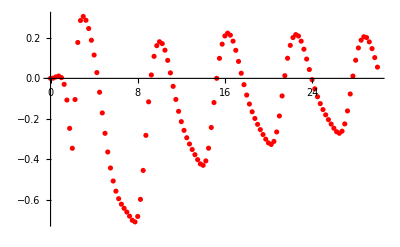

{{0.,{0.,0.}},{0.25,{0.00135962,4.68283×10^-14}},{0.5,{0.00723532,5.12513×10^-13}},{0.75,{0.0114441,-1.56425×10^-16}},{1.,{0.00358707,-9.83009×10^-9}},{1.25,{-0.0294664,-2.47514×10^-16}},{1.5,{-0.107163,-7.1781×10^-17}},{1.75,{-0.247061,1.6777×10^-12}},{2.,{-0.345459,2.22998×10^-17}},{2.25,{-0.10456,3.39533×10^-8}},{2.5,{0.177549,-2.92491×10^-11}},{2.75,{0.286177,-6.88168×10^-16}},{3.,{0.306111,-7.01103×10^-13}},{3.25,{0.28736,-1.0435×10^-9}},{3.5,{0.246473,1.4947×10^-7}},{3.75,{0.18857,8.72525×10^-16}},{4.,{0.115445,-1.57974×10^-7}},{4.25,{0.0287381,-6.36952×10^-17}},{4.5,{-0.0684467,-2.18648×10^-16}},{4.75,{-0.170843,-2.31882×10^-10}},{5.,{-0.271559,1.48329×10^-9}},{5.25,{-0.36381,4.4559×10^-16}},{5.5,{-0.442953,2.84865×10^-15}},{5.75,{-0.507304,3.02031×10^-15}},{6.,{-0.557379,2.98536×10^-7}},{6.25,{-0.594758,1.44696×10^-15}},{6.5,{-0.621825,5.98656×10^-15}},{6.75,{-0.64225,-1.50263×10^-15}},{7.,{-0.660792,1.19827×10^-9}},{7.25,{-0.681087,-3.23918×10^-15}},{7.5,{-0.701319,-7.57514×10^-17}},{7.75,{-0.709418,-2.15013×10^-17}},{8.,{-0.682471,3.18835×10^-7}},{8.25,{-0.598014,8.31526×10^-9}},{8.5,{-0.454992,1.33169×10^-8}},{8.75,{-0.281608,3.1373×10^-9}},{9.,{-0.115872,1.07614×10^-8}},{9.25,{0.0169912,3.23416×10^-9}},{9.5,{0.108909,-1.24154×10^-8}},{9.75,{0.161856,1.64764×10^-8}},{10.,{0.181033,-2.89105×10^-8}},{10.25,{0.171853,-1.88322×10^-8}},{10.5,{0.139414,4.45361×10^-8}},{10.75,{0.0891031,1.26009×10^-8}},{11.,{0.0271865,1.09413×10^-8}},{11.25,{-0.0394101,4.02752×10^-8}},{11.5,{-0.104177,2.05285×10^-8}},{11.75,{-0.162887,-3.05537×10^-9}},{12.,{-0.213791,-1.03692×10^-8}},{12.25,{-0.256947,1.32464×10^-14}},{12.5,{-0.293409,-4.83466×10^-8}},{12.75,{-0.32433,5.46059×10^-8}},{13.,{-0.351561,5.96905×10^-8}},{13.25,{-0.377104,3.78116×10^-9}},{13.5,{-0.401812,9.57315×10^-16}},{13.75,{-0.422539,2.68525×10^-7}},{14.,{-0.429628,8.59861×10^-8}},{14.25,{-0.40796,1.52696×10^-8}},{14.5,{-0.3451,-6.11138×10^-7}},{14.75,{-0.242752,1.65863×10^-7}},{15.,{-0.119523,-2.44463×10^-7}},{15.25,{0.000303405,2.08224×10^-7}},{15.5,{0.0990615,-1.65016×10^-7}},{15.75,{0.16915,-2.96643×10^-8}},{16.,{0.209885,9.96759×10^-8}},{16.25,{0.223581,2.43938×10^-7}},{16.5,{0.213693,4.10236×10^-7}},{16.75,{0.183989,1.1492×10^-6}},{17.,{0.138797,-3.11888×10^-8}},{17.25,{0.0838912,1.03352×10^-7}},{17.5,{0.0253654,-4.30812×10^-7}},{17.75,{-0.0312213,1.07632×10^-7}},{18.,{-0.0823394,1.49477×10^-7}},{18.25,{-0.126817,-7.78726×10^-7}},{18.5,{-0.165102,1.47742×10^-6}},{18.75,{-0.198137,1.77874×10^-6}},{19.,{-0.227253,-1.7972×10^-6}},{19.25,{-0.253309,1.84675×10^-6}},{19.5,{-0.27761,1.73899×10^-7}},{19.75,{-0.300399,-1.98105×10^-7}},{20.,{-0.319114,1.7125×10^-7}},{20.25,{-0.326591,-4.44065×10^-8}},{20.5,{-0.31164,-8.78245×10^-7}},{20.75,{-0.264728,-1.80493×10^-6}},{21.,{-0.185718,-1.65317×10^-6}},{21.25,{-0.0867559,9.64833×10^-7}},{21.5,{0.0133711,-1.46749×10^-6}},{21.75,{0.0995406,-9.85973×10^-7}},{22.,{0.163261,-2.5349×10^-7}},{22.25,{0.201858,3.69572×10^-8}},{22.5,{0.216462,-2.34111×10^-7}},{22.75,{0.209433,-1.61206×10^-6}},{23.,{0.183967,-8.47549×10^-8}},{23.25,{0.144329,2.93248×10^-6}},{23.5,{0.0955173,-1.93051×10^-6}},{23.75,{0.0436972,1.32273×10^-7}},{24.,{-0.00637526,2.18168×10^-6}},{24.25,{-0.0514229,3.77858×10^-6}},{24.5,{-0.0907031,5.20088×10^-7}},{24.75,{-0.124702,-1.98931×10^-6}},{25.,{-0.154203,-3.17904×10^-6}},{25.25,{-0.180186,1.39382×10^-6}},{25.5,{-0.203931,1.02152×10^-7}},{25.75,{-0.225863,3.42784×10^-6}},{26.,{-0.246427,4.03619×10^-6}},{26.25,{-0.263553,-4.30766×10^-6}},{26.5,{-0.271416,-8.26163×10^-6}},{26.75,{-0.260943,-2.04106×10^-6}},{27.,{-0.225006,7.01495×10^-6}},{27.25,{-0.160961,-3.48103×10^-6}},{27.5,{-0.0770899,-7.85762×10^-7}},{27.75,{0.0115065,-3.64612×10^-6}},{28.,{0.0897251,0.000010413}},{28.25,{0.150558,-0.000011834}},{28.5,{0.188849,0.0000268223}},{28.75,{0.205795,-6.70567×10^-6}},{29.,{0.20178,7.19679×10^-6}},{29.25,{0.180471,-5.18385×10^-6}},{29.5,{0.147108,2.37909×10^-6}},{29.75,{0.102753,-0.0000102117}},{30.,{0.0556935,-7.53977×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$302873634 near {ϕ$302873634} = {2.89606}. NIntegrate obtained -0.0000123727 and 1.40918×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$303248081 near {ϕ$303248081} = {1.03074}. NIntegrate obtained 8.77675×10^-6 and 8.93092×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$303322060 near {ϕ$303322060} = {4.20915}. NIntegrate obtained 7.94776×10^-6 and 9.34876×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

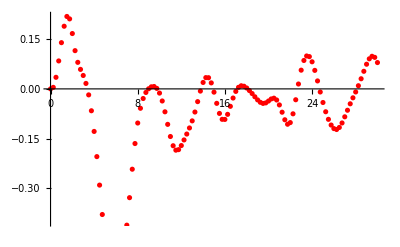

{{0.,{0.,0.}},{0.25,{0.00461502,-0.0264856}},{0.5,{0.0350056,-0.0647852}},{0.75,{0.0844777,-0.0907038}},{1.,{0.1397,-0.096889}},{1.25,{0.189321,-0.0695909}},{1.5,{0.21887,0.0131602}},{1.75,{0.211497,0.159851}},{2.,{0.167247,0.32002}},{2.25,{0.115566,0.409863}},{2.5,{0.0802174,0.412561}},{2.75,{0.0589192,0.367571}},{3.,{0.0405152,0.308764}},{3.25,{0.0165097,0.251352}},{3.5,{-0.0181088,0.200255}},{3.75,{-0.066085,0.156633}},{4.,{-0.128543,0.12081}},{4.25,{-0.204647,0.0932897}},{4.5,{-0.290732,0.0749281}},{4.75,{-0.379581,0.0665317}},{5.,{-0.461026,0.068014}},{5.25,{-0.524902,0.0775865}},{5.5,{-0.565234,0.0917342}},{5.75,{-0.582355,0.106295}},{6.,{-0.580642,0.117855}},{6.25,{-0.563773,0.124389}},{6.5,{-0.531567,0.124901}},{6.75,{-0.481205,0.118834}},{7.,{-0.411796,0.105825}},{7.25,{-0.328694,0.086163}},{7.5,{-0.242714,0.0612571}},{7.75,{-0.165139,0.0336581}},{8.,{-0.103142,0.00672786}},{8.25,{-0.0585473,-0.0158198}},{8.5,{-0.029114,-0.0304477}},{8.75,{-0.0107799,-0.0345145}},{9.,{0.000287277,-0.0271128}},{9.25,{0.00625323,-0.00945127}},{9.5,{0.00716886,0.0154796}},{9.75,{0.00150729,0.0439218}},{10.,{-0.0126846,0.072249}},{10.25,{-0.0365454,0.0974663}},{10.5,{-0.069244,0.117166}},{10.75,{-0.107174,0.129321}},{11.,{-0.143895,0.132359}},{11.25,{-0.17177,0.125522}},{11.5,{-0.185179,0.109549}},{11.75,{-0.183539,0.086672}},{12.,{-0.171246,0.059899}},{12.25,{-0.154247,0.0320357}},{12.5,{-0.136454,0.00521212}},{12.75,{-0.118067,-0.018896}},{13.,{-0.0966428,-0.0389846}},{13.25,{-0.0699135,-0.0541516}},{13.5,{-0.0384992,-0.0641836}},{13.75,{-0.00664118,-0.0696644}},{14.,{0.019439,-0.0714285}},{14.25,{0.0340691,-0.0699543}},{14.5,{0.0337857,-0.064809}},{14.75,{0.0181604,-0.0546089}},{15.,{-0.00984261,-0.0373632}},{15.25,{-0.0436863,-0.0115396}},{15.5,{-0.0741199,0.0224502}},{15.75,{-0.09196,0.0609421}},{16.,{-0.0922645,0.0974803}},{16.25,{-0.0769263,0.125092}},{16.5,{-0.0526658,0.139157}},{16.75,{-0.0276372,0.138371}},{17.,{-0.00758319,0.124234}},{17.25,{0.00469738,0.0997047}},{17.5,{0.00945731,0.0684585}},{17.75,{0.00801453,0.0343444}},{18.,{0.00267411,0.000935263}},{18.25,{-0.00505793,-0.028974}},{18.5,{-0.0140954,-0.0535314}},{18.75,{-0.0238341,-0.0719236}},{19.,{-0.0332103,-0.0837852}},{19.25,{-0.0404981,-0.0889727}},{19.5,{-0.0438877,-0.0871902}},{19.75,{-0.0422682,-0.0786981}},{20.,{-0.036669,-0.0642499}},{20.25,{-0.0304422,-0.0453521}},{20.5,{-0.0280782,-0.023823}},{20.75,{-0.0335451,-0.0012715}},{21.,{-0.0484496,0.0210546}},{21.25,{-0.0704691,0.0421906}},{21.5,{-0.0932902,0.0610397}},{21.75,{-0.106795,0.0761002}},{22.,{-0.101829,0.0855439}},{22.25,{-0.075308,0.0881104}},{22.5,{-0.0328185,0.0836545}},{22.75,{0.0147467,0.0732073}},{23.,{0.0565618,0.0585059}},{23.25,{0.0858832,0.0409402}},{23.5,{0.0994409,0.0217478}},{23.75,{0.0975295,0.00212123}},{24.,{0.0818827,-0.0168123}},{24.25,{0.0559533,-0.0338145}},{24.5,{0.0240677,-0.0474914}},{24.75,{-0.00936388,-0.0568426}},{25.,{-0.0411403,-0.061227}},{25.25,{-0.0690736,-0.0606372}},{25.5,{-0.0919539,-0.0551903}},{25.75,{-0.109247,-0.0450661}},{26.,{-0.119899,-0.0306373}},{26.25,{-0.12271,-0.0126255}},{26.5,{-0.116519,0.0334558}},{26.75,{-0.102947,0.0269577}},{27.,{-0.0843415,0.0431446}},{27.25,{-0.0645471,0.037095}},{27.5,{-0.0450371,0.0382353}},{27.75,{-0.0269489,0.0399077}},{28.,{-0.00930392,0.0424576}},{28.25,{0.00957487,0.0463192}},{28.5,{0.0306263,0.0517194}},{28.75,{0.0531636,0.00508142}},{29.,{0.0745314,-0.00277528}},{29.25,{0.0908381,-0.00693551}},{29.5,{0.0984842,-0.00811225}},{29.75,{0.0952643,0.0859151}},{30.,{0.0795433,0.0884077}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$310616011 near {ϕ$310616011} = {4.92091}. NIntegrate obtained 9.37835×10^-18 and 8.48922×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$310669744 near {ϕ$310669744} = {5.04363}. NIntegrate obtained 1.6562×10^-15 and 1.95604×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$310769643 near {ϕ$310769643} = {2.7488}. NIntegrate obtained -1.56551×10^-12 and 4.34015×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

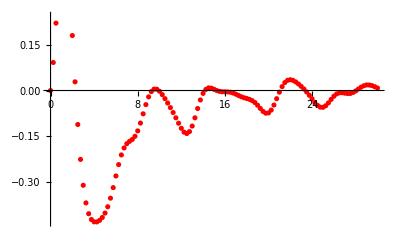

{{0.,{0.,0.}},{0.25,{0.0914694,1.02672×10^-15}},{0.5,{0.219951,2.12991×10^-13}},{0.75,{0.338648,-2.56851×10^-10}},{1.,{0.423828,-7.37103×10^-12}},{1.25,{0.454094,-3.29971×10^-11}},{1.5,{0.417351,5.8011×10^-17}},{1.75,{0.318608,3.36708×10^-16}},{2.,{0.179477,-1.91372×10^-16}},{2.25,{0.0283476,8.10884×10^-16}},{2.5,{-0.110989,5.86471×10^-9}},{2.75,{-0.224954,-1.35552×10^-16}},{3.,{-0.30956,-2.76216×10^-10}},{3.25,{-0.367006,-9.37094×10^-17}},{3.5,{-0.402356,-6.70326×10^-8}},{3.75,{-0.421301,9.43319×10^-11}},{4.,{-0.428923,1.01522×10^-8}},{4.25,{-0.429065,-2.34931×10^-9}},{4.5,{-0.42406,5.37378×10^-10}},{4.75,{-0.414662,-9.29548×10^-10}},{5.,{-0.400264,-1.44031×10^-9}},{5.25,{-0.379548,1.10217×10^-9}},{5.5,{-0.351599,2.0751×10^-9}},{5.75,{-0.31712,-1.53518×10^-9}},{6.,{-0.279054,1.59281×10^-9}},{6.25,{-0.241918,8.61115×10^-8}},{6.5,{-0.21039,1.1833×10^-8}},{6.75,{-0.187512,4.28648×10^-8}},{7.,{-0.173601,5.67719×10^-9}},{7.25,{-0.165984,-9.04225×10^-8}},{7.5,{-0.159764,2.71831×10^-9}},{7.75,{-0.149579,6.75882×10^-10}},{8.,{-0.131842,4.42398×10^-9}},{8.25,{-0.106332,-2.72194×10^-8}},{8.5,{-0.0761273,-3.89375×10^-9}},{8.75,{-0.0460762,-1.78139×10^-8}},{9.,{-0.0208344,-2.06252×10^-9}},{9.25,{-0.00360753,1.44631×10^-8}},{9.5,{0.00452384,1.67908×10^-15}},{9.75,{0.0042733,-3.96264×10^-8}},{10.,{-0.00246504,8.08991×10^-8}},{10.25,{-0.0133918,-5.34834×10^-8}},{10.5,{-0.0265711,8.0901×10^-9}},{10.75,{-0.0408328,1.93568×10^-8}},{11.,{-0.0558928,-2.60575×10^-15}},{11.25,{-0.0719354,-6.71272×10^-8}},{11.5,{-0.0890917,-2.21257×10^-9}},{11.75,{-0.106846,3.17422×10^-8}},{12.,{-0.123489,5.16635×10^-9}},{12.25,{-0.135987,-4.31688×10^-8}},{12.5,{-0.140565,7.72673×10^-8}},{12.75,{-0.134159,6.0138×10^-8}},{13.,{-0.116115,1.63841×10^-9}},{13.25,{-0.0892157,8.38755×10^-8}},{13.5,{-0.0588678,-4.51887×10^-7}},{13.75,{-0.030836,-1.68144×10^-8}},{14.,{-0.00943825,-1.01234×10^-7}},{14.25,{0.00349462,1.76689×10^-7}},{14.5,{0.00852735,-1.64583×10^-7}},{14.75,{0.00782081,-7.80807×10^-9}},{15.,{0.00406384,-2.65087×10^-7}},{15.25,{-0.0000225034,-2.26714×10^-8}},{15.5,{-0.0029078,-1.47023×10^-6}},{15.75,{-0.00417747,-2.96253×10^-7}},{16.,{-0.00438176,1.43835×10^-7}},{16.25,{-0.00456525,-2.50424×10^-7}},{16.5,{-0.00567324,-1.25043×10^-7}},{16.75,{-0.00817872,2.06995×10^-7}},{17.,{-0.0119215,7.04193×10^-8}},{17.25,{-0.0162567,-1.21299×10^-6}},{17.5,{-0.0202974,4.67812×10^-7}},{17.75,{-0.0235776,5.91954×10^-7}},{18.,{-0.026091,4.82013×10^-7}},{18.25,{-0.028836,8.18685×10^-7}},{18.5,{-0.0329298,3.59343×10^-7}},{18.75,{-0.0392261,-3.09862×10^-7}},{19.,{-0.0480984,4.13953×10^-7}},{19.25,{-0.0585296,5.96425×10^-6}},{19.5,{-0.0682289,1.51559×10^-7}},{19.75,{-0.0740893,-8.58592×10^-7}},{20.,{-0.0731387,-4.05134×10^-7}},{20.25,{-0.0639663,1.23333×10^-7}},{20.5,{-0.047497,-1.20462×10^-6}},{20.75,{-0.0266551,1.67808×10^-6}},{21.,{-0.00553008,-7.4831×10^-7}},{21.25,{0.0127322,-1.45222×10^-6}},{21.5,{0.0258803,6.21542×10^-6}},{21.75,{0.0332486,-2.34549×10^-7}},{22.,{0.0352084,-1.44783×10^-6}},{22.25,{0.0329925,4.00076×10^-7}},{22.5,{0.0279752,2.92831×10^-6}},{22.75,{0.0212857,7.93064×10^-7}},{23.,{0.0135411,-1.87854×10^-6}},{23.25,{0.00492623,1.21676×10^-6}},{23.5,{-0.00480799,3.93146×10^-7}},{23.75,{-0.015673,5.59787×10^-6}},{24.,{-0.0273958,6.94055×10^-6}},{24.25,{-0.0389164,-1.89308×10^-6}},{24.5,{-0.0485742,8.02797×10^-7}},{24.75,{-0.0543257,7.68955×10^-6}},{25.,{-0.0548305,3.6125×10^-6}},{25.25,{-0.0497897,-9.14838×10^-6}},{25.5,{-0.0403609,-1.65614×10^-6}},{25.75,{-0.029082,-2.14506×10^-6}},{26.,{-0.0187546,-9.47275×10^-7}},{26.25,{-0.011297,3.46104×10^-6}},{26.5,{-0.00758462,-1.97652×10^-6}},{26.75,{-0.00721582,-5.19151×10^-6}},{27.,{-0.00864915,8.80426×10^-6}},{27.25,{-0.00983998,0.000022966}},{27.5,{-0.00988213,-6.08641×10^-6}},{27.75,{-0.00663257,-4.04776×10^-6}},{28.,{-0.00158476,7.93971×10^-7}},{28.25,{0.00488531,7.59219×10^-6}},{28.5,{0.0109187,-2.27512×10^-6}},{28.75,{0.015555,5.42263×10^-6}},{29.,{0.0180377,4.63066×10^-7}},{29.25,{0.0178812,-2.18802×10^-6}},{29.5,{0.01593,-7.62227×10^-6}},{29.75,{0.0123798,-3.39538×10^-6}},{30.,{0.00820409,1.88192×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$319546113 near {ϕ$319546113} = {3.3992}. NIntegrate obtained -0.0000123727 and 1.40918×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$319920560 near {ϕ$319920560} = {5.26452}. NIntegrate obtained -8.77675×10^-6 and 8.93092×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$319994539 near {ϕ$319994539} = {2.08612}. NIntegrate obtained -7.94776×10^-6 and 9.34876×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

{{0.,{0.,0.}},{0.25,{0.00461502,0.0264856}},{0.5,{0.0350056,0.0647852}},{0.75,{0.0844777,0.0907038}},{1.,{0.1397,0.096889}},{1.25,{0.189321,0.0695909}},{1.5,{0.21887,-0.0131602}},{1.75,{0.211497,-0.159851}},{2.,{0.167247,-0.32002}},{2.25,{0.115566,-0.409863}},{2.5,{0.0802174,-0.412561}},{2.75,{0.0589192,-0.367571}},{3.,{0.0405152,-0.308764}},{3.25,{0.0165097,-0.251352}},{3.5,{-0.0181088,-0.200255}},{3.75,{-0.066085,-0.156633}},{4.,{-0.128543,-0.12081}},{4.25,{-0.204647,-0.0932897}},{4.5,{-0.290732,-0.0749281}},{4.75,{-0.379581,-0.0665317}},{5.,{-0.461026,-0.068014}},{5.25,{-0.524902,-0.0775865}},{5.5,{-0.565234,-0.0917342}},{5.75,{-0.582355,-0.106295}},{6.,{-0.580642,-0.117855}},{6.25,{-0.563773,-0.124389}},{6.5,{-0.531567,-0.124901}},{6.75,{-0.481205,-0.118834}},{7.,{-0.411796,-0.105825}},{7.25,{-0.328694,-0.086163}},{7.5,{-0.242714,-0.0612571}},{7.75,{-0.165139,-0.0336581}},{8.,{-0.103142,-0.00672786}},{8.25,{-0.0585473,0.0158198}},{8.5,{-0.029114,0.0304477}},{8.75,{-0.0107799,0.0345145}},{9.,{0.000287277,0.0271128}},{9.25,{0.00625323,0.00945127}},{9.5,{0.00716886,-0.0154796}},{9.75,{0.00150729,-0.0439218}},{10.,{-0.0126846,-0.072249}},{10.25,{-0.0365454,-0.0974663}},{10.5,{-0.069244,-0.117166}},{10.75,{-0.107174,-0.129321}},{11.,{-0.143895,-0.132359}},{11.25,{-0.17177,-0.125522}},{11.5,{-0.185179,-0.109549}},{11.75,{-0.183539,-0.086672}},{12.,{-0.171246,-0.059899}},{12.25,{-0.154247,-0.0320357}},{12.5,{-0.136454,-0.00521212}},{12.75,{-0.118067,0.018896}},{13.,{-0.0966428,0.0389846}},{13.25,{-0.0699135,0.0541516}},{13.5,{-0.0384992,0.0641836}},{13.75,{-0.00664118,0.0696644}},{14.,{0.019439,0.0714285}},{14.25,{0.0340691,0.0699543}},{14.5,{0.0337857,0.064809}},{14.75,{0.0181604,0.0546089}},{15.,{-0.00984261,0.0373632}},{15.25,{-0.0436863,0.0115396}},{15.5,{-0.0741199,-0.0224502}},{15.75,{-0.09196,-0.0609421}},{16.,{-0.0922645,-0.0974803}},{16.25,{-0.0769263,-0.125092}},{16.5,{-0.0526658,-0.139157}},{16.75,{-0.0276372,-0.138371}},{17.,{-0.00758319,-0.124234}},{17.25,{0.00469738,-0.0997047}},{17.5,{0.00945731,-0.0684585}},{17.75,{0.00801453,-0.0343444}},{18.,{0.00267411,-0.000935263}},{18.25,{-0.00505793,0.028974}},{18.5,{-0.0140954,0.0535314}},{18.75,{-0.0238341,0.0719236}},{19.,{-0.0332103,0.0837852}},{19.25,{-0.0404981,0.0889727}},{19.5,{-0.0438877,0.0871902}},{19.75,{-0.0422682,0.0786981}},{20.,{-0.036669,0.0642499}},{20.25,{-0.0304422,0.0453521}},{20.5,{-0.0280782,0.023823}},{20.75,{-0.0335451,0.0012715}},{21.,{-0.0484496,-0.0210546}},{21.25,{-0.0704691,-0.0421906}},{21.5,{-0.0932902,-0.0610397}},{21.75,{-0.106795,-0.0761002}},{22.,{-0.101829,-0.0855439}},{22.25,{-0.075308,-0.0881104}},{22.5,{-0.0328185,-0.0836545}},{22.75,{0.0147467,-0.0732073}},{23.,{0.0565618,-0.0585059}},{23.25,{0.0858832,-0.0409402}},{23.5,{0.0994409,-0.0217478}},{23.75,{0.0975295,-0.00212123}},{24.,{0.0818827,0.0168123}},{24.25,{0.0559533,0.0338145}},{24.5,{0.0240677,0.0474914}},{24.75,{-0.00936388,0.0568426}},{25.,{-0.0411403,0.061227}},{25.25,{-0.0690736,0.0606372}},{25.5,{-0.0919539,0.0551903}},{25.75,{-0.109247,0.0450661}},{26.,{-0.119899,0.0306373}},{26.25,{-0.12271,0.0126255}},{26.5,{-0.116519,-0.0334558}},{26.75,{-0.102947,-0.0269577}},{27.,{-0.0843415,-0.0431446}},{27.25,{-0.0645471,-0.037095}},{27.5,{-0.0450371,-0.0382353}},{27.75,{-0.0269489,-0.0399077}},{28.,{-0.00930392,-0.0424576}},{28.25,{0.00957487,-0.0463192}},{28.5,{0.0306263,-0.0517194}},{28.75,{0.0531636,-0.00508142}},{29.,{0.0745314,0.00277528}},{29.25,{0.0908381,0.00693551}},{29.5,{0.0984842,0.00811225}},{29.75,{0.0952643,-0.0859151}},{30.,{0.0795433,-0.0884077}}}

```mathematica
Getv2kT[2.0, 0, 0]
Getv2kT[2.0, π/4, 0]
Getv2kT[2.0, π/2, 0]
Getv2kT[2.0, (3π)/4, 0]
```

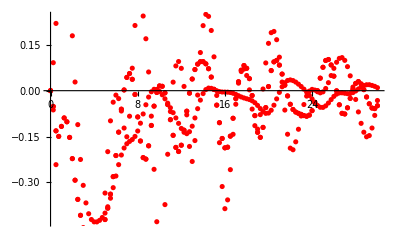

```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192594341 near {ϕ$192594341} = {1.10437}. NIntegrate obtained -9.43256×10^-18 and 2.43631×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192663482 near {ϕ$192663482} = {1.11664}. NIntegrate obtained 7.96838×10^-14 and 1.31915×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192715116 near {ϕ$192715116} = {2.19656}. NIntegrate obtained 1.37482×10^-14 and 2.20778×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

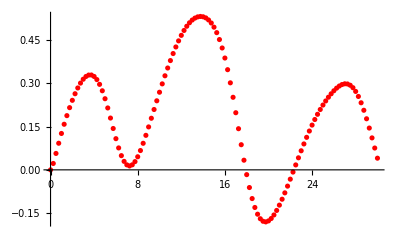

{{0.,{0.,0.}},{0.25,{0.0221996,-3.23371×10^-16}},{0.5,{0.0570201,2.45458×10^-12}},{0.75,{0.0924455,4.00548×10^-13}},{1.,{0.126369,-6.22923×10^-18}},{1.25,{0.158359,-8.20582×10^-17}},{1.5,{0.188286,-2.95008×10^-12}},{1.75,{0.216041,-5.84337×10^-10}},{2.,{0.241466,-4.17965×10^-12}},{2.25,{0.264347,-1.7678×10^-14}},{2.5,{0.284411,-7.59937×10^-18}},{2.75,{0.30133,4.54418×10^-12}},{3.,{0.314724,4.55711×10^-12}},{3.25,{0.324169,1.43257×10^-9}},{3.5,{0.32921,1.30203×10^-17}},{3.75,{0.329386,6.39768×10^-9}},{4.,{0.324269,4.10414×10^-12}},{4.25,{0.313515,-6.18532×10^-17}},{4.5,{0.296944,-1.82982×10^-9}},{4.75,{0.274634,1.20098×10^-12}},{5.,{0.247021,3.59797×10^-11}},{5.25,{0.214987,1.42508×10^-9}},{5.5,{0.179908,2.88088×10^-12}},{5.75,{0.143619,-1.64378×10^-9}},{6.,{0.108286,2.00813×10^-11}},{6.25,{0.0761718,1.36664×10^-8}},{6.5,{0.0493521,-2.77871×10^-10}},{6.75,{0.0294468,5.09257×10^-11}},{7.,{0.017435,5.834×10^-12}},{7.25,{0.0135951,1.81532×10^-8}},{7.5,{0.0175805,-4.21426×10^-8}},{7.75,{0.0285727,5.27911×10^-11}},{8.,{0.0454757,2.86761×10^-8}},{8.25,{0.0670884,3.77256×10^-11}},{8.5,{0.0922415,-1.24882×10^-10}},{8.75,{0.119882,-1.0731×10^-10}},{9.,{0.149113,2.15116×10^-10}},{9.25,{0.179206,2.30835×10^-10}},{9.5,{0.209589,-2.16329×10^-9}},{9.75,{0.239822,6.95511×10^-9}},{10.,{0.269576,2.40401×10^-8}},{10.25,{0.298601,2.67795×10^-10}},{10.5,{0.326704,2.27408×10^-10}},{10.75,{0.353727,-1.14827×10^-8}},{11.,{0.379522,-3.93818×10^-11}},{11.25,{0.403939,-5.71563×10^-10}},{11.5,{0.42681,6.79603×10^-9}},{11.75,{0.447942,9.37176×10^-9}},{12.,{0.467118,-2.70399×10^-10}},{12.25,{0.484117,1.84624×10^-9}},{12.5,{0.498729,6.41399×10^-11}},{12.75,{0.510797,-2.6307×10^-10}},{13.,{0.52023,1.94169×10^-10}},{13.25,{0.527012,2.48967×10^-9}},{13.5,{0.531166,-6.55033×10^-10}},{13.75,{0.532708,7.70974×10^-8}},{14.,{0.531583,7.16468×10^-10}},{14.25,{0.527632,4.16582×10^-8}},{14.5,{0.520575,4.84173×10^-10}},{14.75,{0.510019,6.18242×10^-8}},{15.,{0.495495,-2.55434×10^-10}},{15.25,{0.476498,1.22061×10^-9}},{15.5,{0.452544,-4.44731×10^-10}},{15.75,{0.423239,7.1037×10^-10}},{16.,{0.38835,3.07023×10^-7}},{16.25,{0.347891,6.19011×10^-10}},{16.5,{0.302197,7.10515×10^-9}},{16.75,{0.251988,1.20482×10^-8}},{17.,{0.198389,-9.82006×10^-10}},{17.25,{0.1429,-2.89299×10^-9}},{17.5,{0.0873091,-8.32899×10^-10}},{17.75,{0.0335223,-8.56629×10^-10}},{18.,{-0.0165947,4.04049×10^-8}},{18.25,{-0.0614151,3.80142×10^-8}},{18.5,{-0.0996968,-1.96062×10^-9}},{18.75,{-0.130642,-2.08509×10^-9}},{19.,{-0.153978,5.29826×10^-10}},{19.25,{-0.169779,-3.04424×10^-9}},{19.5,{-0.178478,5.3309×10^-10}},{19.75,{-0.18073,-3.82875×10^-8}},{20.,{-0.177303,-1.82994×10^-9}},{20.25,{-0.169014,-4.73431×10^-9}},{20.5,{-0.156644,-8.31918×10^-9}},{20.75,{-0.140932,-6.51649×10^-9}},{21.,{-0.122525,-1.97073×10^-9}},{21.25,{-0.102002,-5.87279×10^-9}},{21.5,{-0.079854,2.15905×10^-9}},{21.75,{-0.0565126,-2.7443×10^-9}},{22.,{-0.0323491,-1.28922×10^-8}},{22.25,{-0.00769936,1.02072×10^-8}},{22.5,{0.017134,-8.94704×10^-9}},{22.75,{0.0418644,-1.19515×10^-8}},{23.,{0.0662379,-3.67112×10^-9}},{23.25,{0.0899928,1.82462×10^-8}},{23.5,{0.112905,-5.28397×10^-9}},{23.75,{0.134781,-2.38656×10^-8}},{24.,{0.155465,-8.15137×10^-9}},{24.25,{0.174857,3.49973×10^-8}},{24.5,{0.192907,-1.42864×10^-8}},{24.75,{0.209629,-9.98399×10^-9}},{25.,{0.225061,-4.47209×10^-10}},{25.25,{0.239268,-7.57695×10^-10}},{25.5,{0.252289,-2.00509×10^-8}},{25.75,{0.264121,-1.768×10^-8}},{26.,{0.27468,-2.09888×10^-8}},{26.25,{0.283777,-1.27144×10^-8}},{26.5,{0.291114,-6.64079×10^-9}},{26.75,{0.296292,-1.30231×10^-8}},{27.,{0.298821,1.81283×10^-7}},{27.25,{0.29817,-4.55412×10^-9}},{27.5,{0.293819,-1.13286×10^-8}},{27.75,{0.28533,-6.31555×10^-8}},{28.,{0.272378,-1.83807×10^-8}},{28.25,{0.254887,1.38391×10^-8}},{28.5,{0.232939,-2.53063×10^-8}},{28.75,{0.206923,-2.12846×10^-8}},{29.,{0.177415,-2.33819×10^-8}},{29.25,{0.145154,-6.32264×10^-8}},{29.5,{0.111,-3.97756×10^-8}},{29.75,{0.0758315,-8.03388×10^-8}},{30.,{0.0405409,-9.46502×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$201309560 near {ϕ$201309560} = {2.71198}. NIntegrate obtained -4.77961×10^-6 and 8.22802×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$202182264 near {ϕ$202182264} = {1.28845}. NIntegrate obtained 3.50731×10^-6 and 5.85175×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$202257890 near {ϕ$202257890} = {1.25163}. NIntegrate obtained -3.54072×10^-6 and 5.48343×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

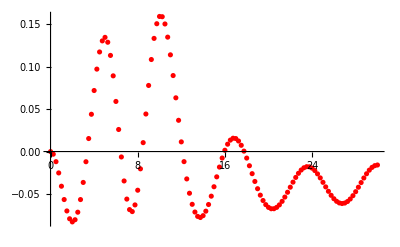

{{0.,{0.,0.}},{0.25,{-0.00309306,0.000750954}},{0.5,{-0.0119145,0.00323082}},{0.75,{-0.0251503,0.00778633}},{1.,{-0.0407959,0.0146037}},{1.25,{-0.0564838,0.0236247}},{1.5,{-0.0698936,0.0345614}},{1.75,{-0.0791022,0.0469708}},{2.,{-0.0827828,0.0603467}},{2.25,{-0.0802443,0.0741943}},{2.5,{-0.0713666,0.0880696}},{2.75,{-0.0564958,0.101583}},{3.,{-0.0363525,0.114382}},{3.25,{-0.0119737,0.126112}},{3.5,{0.0153099,0.136383}},{3.75,{0.0438767,0.14473}},{4.,{0.0718237,0.150591}},{4.25,{0.0970151,0.153302}},{4.5,{0.117202,0.152123}},{4.75,{0.130237,0.1463}},{5.,{0.134382,0.135169}},{5.25,{0.128653,0.118278}},{5.5,{0.113128,0.0955099}},{5.75,{0.0890952,0.0671641}},{6.,{0.0589675,0.0339598}},{6.25,{0.0259637,-0.00303082}},{6.5,{-0.00636037,-0.0425091}},{6.75,{-0.0346051,-0.0830886}},{7.,{-0.0559293,-0.123408}},{7.25,{-0.0683078,-0.1622}},{7.5,{-0.0706468,-0.198316}},{7.75,{-0.0627976,-0.230726}},{8.,{-0.0455087,-0.25852}},{8.25,{-0.0203369,-0.28091}},{8.5,{0.0104769,-0.297281}},{8.75,{0.0441866,-0.30725}},{9.,{0.0777857,-0.31074}},{9.25,{0.10831,-0.308032}},{9.5,{0.133165,-0.299786}},{9.75,{0.150415,-0.286994}},{10.,{0.158979,-0.270878}},{10.25,{0.158677,-0.252744}},{10.5,{0.150148,-0.233893}},{10.75,{0.13465,-0.215388}},{11.,{0.113818,-0.198094}},{11.25,{0.0894324,-0.182594}},{11.5,{0.0632309,-0.16921}},{11.75,{0.0367771,-0.15804}},{12.,{0.0113944,-0.149014}},{12.25,{-0.0118613,-0.141937}},{12.5,{-0.0321957,-0.136534}},{12.75,{-0.0490539,-0.132495}},{13.,{-0.0620966,-0.129492}},{13.25,{-0.0711709,-0.127212}},{13.5,{-0.0762895,-0.125364}},{13.75,{-0.0776124,-0.123699}},{14.,{-0.075432,-0.122011}},{14.25,{-0.0701604,-0.120151}},{14.5,{-0.0623166,-0.118024}},{14.75,{-0.0525101,-0.115599}},{15.,{-0.0414185,-0.112896}},{15.25,{-0.0297618,-0.109991}},{15.5,{-0.0182676,-0.106998}},{15.75,{-0.00763233,-0.104064}},{16.,{0.00151965,-0.101345}},{16.25,{0.0086746,-0.0989941}},{16.5,{0.0134627,-0.0971431}},{16.75,{0.0156781,-0.0958875}},{17.,{0.0152884,-0.0952776}},{17.25,{0.012426,-0.0953131}},{17.5,{0.00736878,-0.0959473}},{17.75,{0.000509203,-0.0970909}},{18.,{-0.0076832,-0.098627}},{18.25,{-0.0166995,-0.100421}},{18.5,{-0.0260281,-0.102337}},{18.75,{-0.0351842,-0.104249}},{19.,{-0.0437339,-0.106058}},{19.25,{-0.0513106,-0.107693}},{19.5,{-0.0576251,-0.109106}},{19.75,{-0.0624678,-0.110311}},{20.,{-0.0657108,-0.111344}},{20.25,{-0.0673041,-0.112277}},{20.5,{-0.0672705,-0.113215}},{20.75,{-0.0657009,-0.114287}},{21.,{-0.0627481,-0.115641}},{21.25,{-0.05862,-0.11743}},{21.5,{-0.0535727,-0.119807}},{21.75,{-0.047901,-0.122914}},{22.,{-0.0419298,-0.126866}},{22.25,{-0.0359991,-0.131747}},{22.5,{-0.0304494,-0.137595}},{22.75,{-0.0256031,-0.144399}},{23.,{-0.0217446,-0.152091}},{23.25,{-0.0191014,-0.160555}},{23.5,{-0.0178255,-0.169624}},{23.75,{-0.0179808,-0.179103}},{24.,{-0.0195371,-0.188777}},{24.25,{-0.0223728,-0.198435}},{24.5,{-0.0262829,-0.207887}},{24.75,{-0.0309998,-0.216986}},{25.,{-0.0362106,-0.225626}},{25.25,{-0.0415831,-0.233769}},{25.5,{-0.0467888,-0.241428}},{25.75,{-0.0515212,-0.248673}},{26.,{-0.0555133,-0.255622}},{26.25,{-0.0585455,-0.262423}},{26.5,{-0.0604585,-0.269252}},{26.75,{-0.0611517,-0.276295}},{27.,{-0.0605893,-0.283741}},{27.25,{-0.0587953,-0.291756}},{27.5,{-0.0558612,-0.300489}},{27.75,{-0.0519352,-0.310052}},{28.,{-0.0472221,-0.320516}},{28.25,{-0.0419795,-0.331882}},{28.5,{-0.0365029,-0.344105}},{28.75,{-0.0311151,-0.357068}},{29.,{-0.0261444,-0.370597}},{29.25,{-0.0219013,-0.384455}},{29.5,{-0.0186537,-0.398367}},{29.75,{-0.0165963,-0.412035}},{30.,{-0.0158339,-0.425163}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$211137135 near {ϕ$211137135} = {2.57699}. NIntegrate obtained -2.01977×10^-13 and 2.53476×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$211213254 near {ϕ$211213254} = {0.638038}. NIntegrate obtained 5.67255×10^-15 and 1.25353×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$211293801 near {ϕ$211293801} = {4.23369}. NIntegrate obtained 4.41921×10^-15 and 5.51898×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

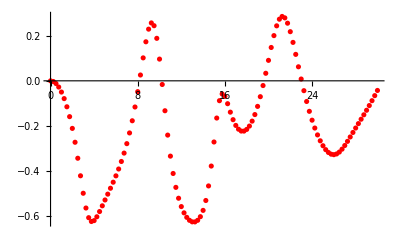

{{0.,{0.,0.}},{0.25,{-0.00293846,-3.22266×10^-14}},{0.5,{-0.0119878,4.01797×10^-15}},{0.75,{-0.0274896,8.05572×10^-15}},{1.,{-0.0496732,3.74359×10^-14}},{1.25,{-0.0786963,4.28793×10^-14}},{1.5,{-0.114789,-6.03624×10^-13}},{1.75,{-0.158429,-3.55129×10^-17}},{2.,{-0.210431,2.61653×10^-12}},{2.25,{-0.271718,-1.06398×10^-12}},{2.5,{-0.342421,-5.93236×10^-11}},{2.75,{-0.420021,3.5364×10^-11}},{3.,{-0.497264,7.23561×10^-12}},{3.25,{-0.562566,-7.13039×10^-9}},{3.5,{-0.605292,1.42908×10^-9}},{3.75,{-0.62223,-4.08025×10^-9}},{4.,{-0.618239,-5.81003×10^-10}},{4.25,{-0.601331,1.24109×10^-9}},{4.5,{-0.578195,4.04457×10^-9}},{4.75,{-0.552817,-3.57247×10^-11}},{5.,{-0.526988,1.47112×10^-9}},{5.25,{-0.501173,3.04482×10^-9}},{5.5,{-0.47516,1.02292×10^-10}},{5.75,{-0.448418,-7.07705×10^-11}},{6.,{-0.420273,1.03417×10^-8}},{6.25,{-0.389976,1.79615×10^-8}},{6.5,{-0.356724,-3.05977×10^-9}},{6.75,{-0.319663,-4.44271×10^-11}},{7.,{-0.277894,-2.47251×10^-11}},{7.25,{-0.230502,2.16695×10^-10}},{7.5,{-0.176646,-2.85718×10^-10}},{7.75,{-0.115746,2.7498×10^-12}},{8.,{-0.0478498,-1.51385×10^-10}},{8.25,{0.0257362,5.98577×10^-10}},{8.5,{0.101504,-3.03453×10^-10}},{8.75,{0.172664,1.71001×10^-10}},{9.,{0.228584,-4.39478×10^-8}},{9.25,{0.256093,-1.35779×10^-10}},{9.5,{0.243768,1.80117×10^-10}},{9.75,{0.187961,2.44382×10^-10}},{10.,{0.0961155,-3.32592×10^-9}},{10.25,{-0.0161986,9.39926×10^-10}},{10.5,{-0.132316,-8.89064×10^-10}},{10.75,{-0.240029,1.53059×10^-9}},{11.,{-0.333077,-8.73849×10^-11}},{11.25,{-0.409818,2.59413×10^-8}},{11.5,{-0.471218,-5.93729×10^-11}},{11.75,{-0.519297,-1.65977×10^-7}},{12.,{-0.55623,3.20114×10^-14}},{12.25,{-0.58392,-9.15752×10^-10}},{12.5,{-0.603832,-1.34332×10^-10}},{12.75,{-0.616939,-5.77897×10^-9}},{13.,{-0.623691,8.20746×10^-9}},{13.25,{-0.623961,-9.89742×10^-9}},{13.5,{-0.616931,-9.21197×10^-9}},{13.75,{-0.600898,-5.27947×10^-10}},{14.,{-0.57304,-8.64402×10^-9}},{14.25,{-0.529286,-1.75417×10^-9}},{14.5,{-0.464894,1.09976×10^-9}},{14.75,{-0.376998,-3.81623×10^-9}},{15.,{-0.270524,5.50331×10^-9}},{15.25,{-0.164605,-3.38064×10^-9}},{15.5,{-0.087889,-3.76231×10^-9}},{15.75,{-0.058007,-3.55694×10^-9}},{16.,{-0.068785,2.06293×10^-9}},{16.25,{-0.101157,-1.31209×10^-9}},{16.5,{-0.13856,2.46724×10^-8}},{16.75,{-0.171809,-1.55624×10^-7}},{17.,{-0.197223,1.84117×10^-8}},{17.25,{-0.213924,-1.32234×10^-8}},{17.5,{-0.222123,-6.69793×10^-9}},{17.75,{-0.2223,9.57063×10^-9}},{18.,{-0.21489,-6.14174×10^-8}},{18.25,{-0.200167,7.39934×10^-9}},{18.5,{-0.178263,-2.05153×10^-9}},{18.75,{-0.149237,4.9509×10^-9}},{19.,{-0.113092,-1.16386×10^-8}},{19.25,{-0.070118,-3.76135×10^-9}},{19.5,{-0.0208926,-9.86587×10^-9}},{19.75,{0.0333654,-2.04069×10^-9}},{20.,{0.0905492,-4.21111×10^-9}},{20.25,{0.147491,-1.285×10^-8}},{20.5,{0.199981,-2.5641×10^-8}},{20.75,{0.243209,-8.28052×10^-9}},{21.,{0.272559,-2.52265×10^-8}},{21.25,{0.284694,-2.42728×10^-8}},{21.5,{0.278405,1.94579×10^-8}},{21.75,{0.254908,-4.16011×10^-8}},{22.,{0.217366,-1.3882×10^-8}},{22.25,{0.169974,-9.59871×10^-9}},{22.5,{0.116993,-3.66937×10^-8}},{22.75,{0.062076,2.75005×10^-8}},{23.,{0.00794649,-3.01615×10^-8}},{23.25,{-0.0435514,1.25449×10^-8}},{23.5,{-0.0913512,-1.59653×10^-8}},{23.75,{-0.134919,4.47874×10^-9}},{24.,{-0.174075,-2.16859×10^-8}},{24.25,{-0.208816,5.94535×10^-8}},{24.5,{-0.239213,-8.45132×10^-8}},{24.75,{-0.26531,3.69644×10^-8}},{25.,{-0.287072,-1.98294×10^-8}},{25.25,{-0.304354,-8.21445×10^-7}},{25.5,{-0.316903,3.54906×10^-9}},{25.75,{-0.324407,-4.23101×10^-9}},{26.,{-0.326601,-2.85156×10^-8}},{26.25,{-0.323405,6.47479×10^-9}},{26.5,{-0.315083,-3.31133×10^-7}},{26.75,{-0.302306,-1.48647×10^-8}},{27.,{-0.286127,-1.17954×10^-8}},{27.25,{-0.267735,3.28228×10^-8}},{27.5,{-0.248234,2.31983×10^-8}},{27.75,{-0.228432,-6.87637×10^-7}},{28.,{-0.208734,-4.3891×10^-8}},{28.25,{-0.189261,-4.57546×10^-8}},{28.5,{-0.169846,-4.8988×10^-7}},{28.75,{-0.150243,1.1607×10^-7}},{29.,{-0.130176,6.18468×10^-8}},{29.25,{-0.109409,-1.70999×10^-8}},{29.5,{-0.0878411,1.65943×10^-8}},{29.75,{-0.0654788,-2.8936×10^-7}},{30.,{-0.04255,3.99352×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$219324640 near {ϕ$219324640} = {3.58328}. NIntegrate obtained 4.77961×10^-6 and 8.22802×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$220197494 near {ϕ$220197494} = {1.86522}. NIntegrate obtained 3.50731×10^-6 and 5.85175×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$220273120 near {ϕ$220273120} = {1.90204}. NIntegrate obtained -3.54072×10^-6 and 5.48343×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

{{0.,{0.,0.}},{0.25,{-0.00309306,-0.000750954}},{0.5,{-0.0119145,-0.00323082}},{0.75,{-0.0251503,-0.00778633}},{1.,{-0.0407959,-0.0146037}},{1.25,{-0.0564838,-0.0236247}},{1.5,{-0.0698936,-0.0345614}},{1.75,{-0.0791022,-0.0469708}},{2.,{-0.0827828,-0.0603467}},{2.25,{-0.0802443,-0.0741943}},{2.5,{-0.0713666,-0.0880696}},{2.75,{-0.0564958,-0.101583}},{3.,{-0.0363525,-0.114382}},{3.25,{-0.0119737,-0.126112}},{3.5,{0.0153099,-0.136383}},{3.75,{0.0438767,-0.14473}},{4.,{0.0718237,-0.150591}},{4.25,{0.0970151,-0.153302}},{4.5,{0.117202,-0.152123}},{4.75,{0.130237,-0.1463}},{5.,{0.134382,-0.135169}},{5.25,{0.128653,-0.118278}},{5.5,{0.113128,-0.0955099}},{5.75,{0.0890952,-0.0671641}},{6.,{0.0589675,-0.0339598}},{6.25,{0.0259637,0.00303082}},{6.5,{-0.00636037,0.0425091}},{6.75,{-0.0346051,0.0830886}},{7.,{-0.0559293,0.123408}},{7.25,{-0.0683078,0.1622}},{7.5,{-0.0706468,0.198316}},{7.75,{-0.0627976,0.230726}},{8.,{-0.0455087,0.25852}},{8.25,{-0.0203369,0.28091}},{8.5,{0.0104769,0.297281}},{8.75,{0.0441866,0.30725}},{9.,{0.0777857,0.31074}},{9.25,{0.10831,0.308032}},{9.5,{0.133165,0.299786}},{9.75,{0.150415,0.286994}},{10.,{0.158979,0.270878}},{10.25,{0.158677,0.252744}},{10.5,{0.150148,0.233893}},{10.75,{0.13465,0.215388}},{11.,{0.113818,0.198094}},{11.25,{0.0894324,0.182594}},{11.5,{0.0632309,0.16921}},{11.75,{0.0367771,0.15804}},{12.,{0.0113944,0.149014}},{12.25,{-0.0118613,0.141937}},{12.5,{-0.0321957,0.136534}},{12.75,{-0.0490539,0.132495}},{13.,{-0.0620966,0.129492}},{13.25,{-0.0711709,0.127212}},{13.5,{-0.0762895,0.125364}},{13.75,{-0.0776124,0.123699}},{14.,{-0.075432,0.122011}},{14.25,{-0.0701604,0.120151}},{14.5,{-0.0623166,0.118024}},{14.75,{-0.0525101,0.115599}},{15.,{-0.0414185,0.112896}},{15.25,{-0.0297618,0.109991}},{15.5,{-0.0182676,0.106998}},{15.75,{-0.00763233,0.104064}},{16.,{0.00151965,0.101345}},{16.25,{0.0086746,0.0989941}},{16.5,{0.0134627,0.0971431}},{16.75,{0.0156781,0.0958875}},{17.,{0.0152884,0.0952776}},{17.25,{0.012426,0.0953131}},{17.5,{0.00736878,0.0959473}},{17.75,{0.000509203,0.0970909}},{18.,{-0.0076832,0.098627}},{18.25,{-0.0166995,0.100421}},{18.5,{-0.0260281,0.102337}},{18.75,{-0.0351842,0.104249}},{19.,{-0.0437339,0.106058}},{19.25,{-0.0513106,0.107693}},{19.5,{-0.0576251,0.109106}},{19.75,{-0.0624678,0.110311}},{20.,{-0.0657108,0.111344}},{20.25,{-0.0673041,0.112277}},{20.5,{-0.0672705,0.113215}},{20.75,{-0.0657009,0.114287}},{21.,{-0.0627481,0.115641}},{21.25,{-0.05862,0.11743}},{21.5,{-0.0535727,0.119807}},{21.75,{-0.047901,0.122914}},{22.,{-0.0419298,0.126866}},{22.25,{-0.0359991,0.131747}},{22.5,{-0.0304494,0.137595}},{22.75,{-0.0256031,0.144399}},{23.,{-0.0217446,0.152091}},{23.25,{-0.0191014,0.160555}},{23.5,{-0.0178255,0.169624}},{23.75,{-0.0179808,0.179103}},{24.,{-0.0195371,0.188777}},{24.25,{-0.0223728,0.198435}},{24.5,{-0.0262829,0.207887}},{24.75,{-0.0309998,0.216986}},{25.,{-0.0362106,0.225626}},{25.25,{-0.0415831,0.233769}},{25.5,{-0.0467888,0.241428}},{25.75,{-0.0515212,0.248673}},{26.,{-0.0555133,0.255622}},{26.25,{-0.0585455,0.262423}},{26.5,{-0.0604585,0.269252}},{26.75,{-0.0611517,0.276295}},{27.,{-0.0605893,0.283741}},{27.25,{-0.0587953,0.291756}},{27.5,{-0.0558612,0.300489}},{27.75,{-0.0519352,0.310052}},{28.,{-0.0472221,0.320516}},{28.25,{-0.0419795,0.331882}},{28.5,{-0.0365029,0.344105}},{28.75,{-0.0311151,0.357068}},{29.,{-0.0261444,0.370597}},{29.25,{-0.0219013,0.384455}},{29.5,{-0.0186537,0.398367}},{29.75,{-0.0165963,0.412035}},{30.,{-0.0158339,0.425163}}}

```mathematica
Getv2kT[0.5, 0]
Getv2kT[0.5, π/4]
Getv2kT[0.5, π/2]
Getv2kT[0.5, (3π)/4]
```

## b=3 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,x1u, x3u,bu,i,kT},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤100,i++,
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
kT=0.1*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05
]
```

```mathematica
Getv2kT[3.0, 0]
Getv2kT[3.0, π/4]
Getv2kT[3.0, π/2]
Getv2kT[3.0, (3π)/4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$154063 near {ϕ$154063} = {4.52821}. NIntegrate obtained -2.67069×10^-17 and 3.8377×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$215044 near {ϕ$215044} = {1.77932}. NIntegrate obtained 1.1542×10^-14 and 5.30506×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$302602 near {ϕ$302602} = {4.51594}. NIntegrate obtained -5.48144×10^-13 and 3.30647×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

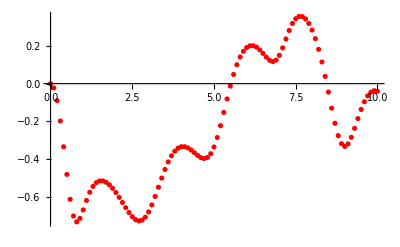
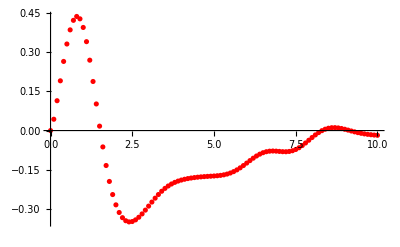
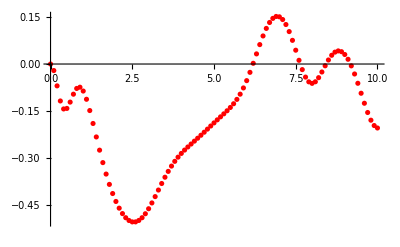
```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

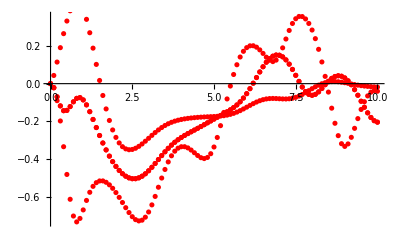

## Dipole v_2

```mathematica
v2HZ[kT_,b_,rA_,rB_, nMC_:10^4]:=Module[{num,den,n},
n=2;
num=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
den=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
{num,den,num/den}
]
```

```mathematica
v2HZ[kT_,b_,rA_,rB_, nMC_:10^4]:=Module[{num,den,n},
n=2;
num=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
den=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"MonteCarlo"}];
{num,den,num/den}
]
```

```mathematica
ti=AbsoluteTime[]
v2HZ[1.0,2.0,1.0,1.0]
AbsoluteTime[]-ti
```

3.884416395256339×10^9

$Aborted

169.04157

```mathematica
v2HZ[kT_,b_,rA_,rB_, nMC_:10^4]:=Module[{num,den,n},
n=2;
num=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
den=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
{num,den,num/den}
]
ti=AbsoluteTime[];
v2HZ[1.0,2.0,1.0,1.0]
AbsoluteTime[]-ti
```

```mathematica
v2[kT_,b_,rA_,rB_, nMC_:10^4]:=Module[{num,den,n},
n=2;
num=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
den=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"MonteCarlo"}];
{num,den,num/den}
]
ti=AbsoluteTime[];
v2[1.0,2.0,1.0,1.0]
AbsoluteTime[]-ti
```

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0118749+0. ⅈ and 0.000231322 for the integral and error estimates.

{0.0118749,0.243037,0.0488606}

5075.240334

```mathematica
v2[kT_,b_,rA_,rB_, nMC_:10^4]:=Module[{num,den,n},
n=2;
num=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
den=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
{num,den,num/den}
]
ti=AbsoluteTime[];
v2[1.0,2.0,1.0,1.0,10^3]
AbsoluteTime[]-ti
```

NIntegrate::maxp: The integral failed to converge after 1001000 integrand evaluations. NIntegrate obtained 0.0113904+0. ⅈ and 0.000165583 for the integral and error estimates.

{0.0113904,0.242128,0.047043}

4067.467797

```mathematica
Getv2kT[b_]:=Module[{v2kTb05},
v2kTb05={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσ[bu,x1u,x3u,kT,False]}];
]
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
v2kTb05

]
```